```mathematica
Quit[];
```

```mathematica
NotebookDirectory[]
```

/Users/windfolgen/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/

### function

```mathematica
ClearAll[MutateGraph];
MutateGraph::usage="MutateGraph[g,v] mutate the graph at the vertex v";
MutateGraph[g_,v_]:=Module[{sub,in,out,ng,subed,ced,ned,n},
sub=NeighborhoodGraph[g,{v}];
subed=EdgeList[sub];
ng=EdgeDelete[g,subed];
out=EdgeList[sub,v->_][[All,2]];(*vertex out*)
in=EdgeList[sub,_->v][[All,1]];(*vertex in*)
ned=DirectedEdge@@@Tuples[{out,in}];
ced=ned;
ned=Join[(ConstantArray[#,Count[ced,#]]&/@Complement[ced,subed])//Flatten,(ConstantArray[#,Count[ced,#]-Min[Count[subed,#],Count[ced,#]]]&/@ Intersection[subed,ced])//Flatten];
(*Echo[ced,"ced"];
Echo[ned,"ned"];*)
subed=Join[(ConstantArray[#,Count[subed,#]]&/@Complement[subed,Join[ced,DirectedEdge[v,#]&/@out,DirectedEdge[#,v]&/@in]])//Flatten,(ConstantArray[#,Count[subed,#]-Min[Count[subed,#],Count[ced,#]]]&/@ Intersection[subed,ced])//Flatten];(*edges not mutated*)
Return[EdgeAdd[ng,Join[subed,Reverse/@Join[DirectedEdge[#,v]&/@in,DirectedEdge[v,#]&/@out,ned]]]];
];
```

```mathematica
ClearAll[MutateB];
MutateB::usage="MutateB[B,x,k] mutate the exchange matrix B and the corresponding cluster variables x in direction k";
MutateB[B_,x_,k_]:=Module[{Bp,xp,l,tem},
l=B[[All,k]];
xp=x;
Bp=Table[
If[i==k||j==k,-B[[i,j]],
If[B[[i,k]]>0&&B[[k,j]]>0,
B[[i,j]]+B[[i,k]]*B[[k,j]],
If[B[[i,k]]<0&&B[[k,j]]<0,B[[i,j]]-B[[i,k]]*B[[k,j]],B[[i,j]]]
]
]
,{i,1,Length[B]},{j,1,Length[B[[1]]]}];
tem=Join[Table[If[l[[i]]>0,{1,Power[x[[i]],l[[i]]]},{2,Power[x[[i]],-l[[i]]]}],{i,1,Length[l]}],{{1,1},{2,1}}]//GatherBy[#,First]&;
(*Print[l];
Print[tem];*)
xp[[k]]=((Times@@tem[[1,All,2]])+(Times@@tem[[2,All,2]]))/xp[[k]]//Factor;
Return[{Bp,xp}];
];
```

```mathematica
ClearAll[MutateY];
MutateY::usage="MutateY[B,y,k] mutate the exchange matrix B and the corresponding X coordinates y in direction k";
MutateY[B_,y_,k_]:=Module[{Bp,yp,l,tem},
l=B[[k]];
yp=y;
Bp=Table[
If[i==k||j==k,-B[[i,j]],
If[B[[i,k]]>0&&B[[k,j]]>0,
B[[i,j]]+B[[i,k]]*B[[k,j]],
If[B[[i,k]]<0&&B[[k,j]]<0,B[[i,j]]-B[[i,k]]*B[[k,j]],B[[i,j]]]
]
]
,{i,1,Length[B]},{j,1,Length[B[[1]]]}];
yp=Table[
If[i==k,(*Print["y"<>ToString[k]<>"-> 1/y"<>ToString[k]];*)1/y[[i]],
If[B[[k,i]]<=0,(*Print["y"<>ToString[i]<>"->y"<>ToString[i]<>"*(1+y"<>ToString[k]<>")^"<>ToString[-B[[k,i]]]];*)y[[i]]*Power[(y[[k]]+1),-B[[k,i]]],(*Print["y"<>ToString[i]<>"->y"<>ToString[i]<>"*(1+1/y"<>ToString[k]<>")^"<>ToString[-B[[k,i]]]];*)y[[i]]*Power[(1/y[[k]]+1),-B[[k,i]]]]]
,{i,1,Length[y]}]//Factor;
Return[{Bp,yp}];
];
```

```mathematica
ClearAll[CreateQuiver];
CreateQuiver::usage="CreateQuiver[B] creates a quiver graph from extended exchange matrix B";
Options[CreateQuiver]={GraphLayout->"SpringElectricalEmbedding","outputlevel"->1};
CreateQuiver[B_,OptionsPattern[]]:=Module[{l,cl,g,vlabel},
l=Length[B];(*n rows correspond to n vertices*)
cl=Length[B[[1]]];(*n columns correspond to n mutable vertices*)
If[OptionValue["outputlevel"],Print[cl," mutable variables; ",l-cl," frozen variables."]];
g=Reap[Do[
Do[
If[B[[i,j]]>0,Sow[ConstantArray[DirectedEdge[i,j],B[[i,j]]]],Sow[ConstantArray[DirectedEdge[j,i],-B[[i,j]]]]]
,{j,i+1,cl}]
,{i,1,Min[l,cl]}]
][[2]];
If[g=!={},g=g[[1]]//Flatten,Return[{}]];
(*Print[g];*)
vlabel=Join[(#->Button[#,h=MutateGraph[h,#]])&/@Table[i,{i,1,cl}],(#->Button[#,Null])&/@Table[i,{i,cl+1,l}]];
Graph[g,VertexLabels->vlabel,GraphLayout->OptionValue[GraphLayout]]
];
```

```mathematica
ClearAll[a];
SetAttributes[a,{Orderless}];
ClearAll[GramM];
GramM::err="The input should be a square matrix.";
GramM[I_]:=GramM[I,I];
Options[GramM]={"explicitM"->{}};
GramM[I_,J_,OptionsPattern[]]:=Module[{r,c,rep={}},
r=I//Sort;
c=J//Sort;
If[Length[I]!=Length[J],Message[GramM::err];Return[$Failed]];
If[OptionValue["explicitM"]=!={},rep={a[i_,j_]:>OptionValue["explicitM"][[i,j]]}];
Det[Outer[a,r,c]/.rep]
];
```

```mathematica
ClearAll[MatFromQuiver];
MatFromQuiver[g_]:=Module[{edg,ver},
edg=EdgeList[g];
ver=VertexCount[g];
(*Print[edg];*)
Return[SparseArray[edg/.DirectedEdge[a_,b_]:>({{a,b}->#,{b,a}->-#}&[Count[edg,DirectedEdge[a,b]]])//Flatten,{ver,ver}]//Normal];
];
```

### Parametrize for momentum twistors

We need to develop a parametrization suitable for momentum twistor representation. calculation of momentum twistor variables

```mathematica
ClearAll[RandomZs];
RandomZs::usage="RandomZs[n] generate a set of positive ordered list for G(4,n) which also satisfies the kinematic conditions by using algorithm in the ancillary file of 1911.09106. The Option \"positive\"->False can generate a set of random ordered list. The last two denote infinity line.";
Options[RandomZs]={"positive"->True};
RandomZs[n_]:=Module[{pl,tl,rl,row={},i},
If[Not@OptionValue["positive"],Return[Append[RandomPrime[10000,{n-1,4}],Prepend[RandomPrime[10000,3],0]]]];
pl=(Accumulate[RandomInteger[{1,20},n+6]]);
tl=ConstantArray[1,n+6];
row=Prepend[Delete[Partition[Riffle[pl,tl],2],-1],{0,1}];(*the first one is special corresponding to the last light-like momentum p_n {{0,0},{x,x}} which also doesn't affect the positive order*)
Do[
rl=RandomInteger[{1,10},n+6];(*mulitipling positive random integer doesn't change the positivity*)
row=Prepend[Delete[Append[#,1]&/@Accumulate[rl*row],-1],UnitVector[i+2,i+2]];
,{i,1,2}];
rl=RandomPrime[{1,100},n+6];
row=row*rl;
Return[Join[(row[[3;;-5]]//Reverse),{{0,0,0,1},{0,0,1,0}}]];(*the last two denote the infinity line*)
];
```

```mathematica
ClearAll[FB,Z,BiTw,Int,MTExpand,DisplayAll];
FB::usage="FB[a,b,c,d] is the four bracket of momentum twistor variables.";
FB[List[a_,b_,c_,d_]]:=FB[a,b,c,d];
FB[a_,b_,c_,d_]/;((!OrderedQ[{a,b,c,d}])&&FreeQ[{a,b,c,d},Int]):=Signature[{a,b,c,d}]*FB[Sequence@@Sort[{a,b,c,d}]];
(*FB[a__,Int[b_,c_],d___]:=
If[FreeQ[{a},Int],If[OddQ[Length[b]+Length[c]],Power[-1,Length[({a})//Flatten]]*FB[Int[b,c],a,d],FB[Int[b,c],a,d]],FB[a,Int[b,c],d]];*)
FB[a___,b_,d___,b_,c___]:=0;
FB[a___,-b_,d___]:=-FB[a,b,d];
FB[a___,Z[b_],d___]:=FB[a,b,d];
FB[a___,Z[b_]*FB[c__],d___]:=FB[a,b,d]*FB[c];
FB[a___,Times[x___,Z[b_]],d___]:=FB[a,b,d]*Times[x];
FB[a___,BiTw[b_,c_],e___]:=FB[a,b,c,e];
FB[a___,BiTw[b_,c_]*FB[d__],e___]:=FB[a,b,c,e]*FB[d];
FB[a___,Plus[b_,c__],d___]:=FB[a,b,d]+FB[a,Plus[c],d];
FB[a___,Times[b_,Int[c__]],d___]:=b*FB[a,Int[c],d];
FB[a___,Times[b_,BiTw[c__]],d___]:=b*FB[a,BiTw[c],d];
FB[a_,BiTw[b_,c_],BiTw[d_,e_],BiTw[f_,g_]]:=FB[Int[{b,c,a},{d,e,a}],f,g];
FB[Int[{a_,b_,c_},{d_,e_,f_}]/;(Length[Intersection[{a,b,c},{d,e,f}]]==2),g_/;FreeQ[g,Int],h_/;FreeQ[h,Int]]:=FB[a,b,g,h]*FB[c,d,e,f]+FB[b,c,g,h]*FB[a,d,e,f]+FB[c,a,g,h]*FB[b,d,e,f];
(*when the Int[{a,b,c},{d,e,f}] is a line which can be characterized by two point in {a,b,c,d,e,f}, we directly write it as a line*)
BiTw[a_,a_]:=0;
BiTw[a_,b_]/;(!OrderedQ[{a,b}]&&FreeQ[{a,b},Int]):=Signature[{a,b}]*BiTw[Sequence@@Sort[{a,b}]];
Options[MTExpand]={"order"->"brfirst"};
MTExpand[exp_,OptionsPattern[]]:=Module[{rule1={},rule2={}},
rule1={FB[Int[{a_,b_,c_},{d_,e_,f_}],g_/;FreeQ[g,Int],h_/;FreeQ[h,Int]]:>FB[a,b,c,g]*FB[d,e,f,h]-FB[a,b,c,h]*FB[d,e,f,g]};rule2={Int[a_,b_]:>If[Length[a]==2&&Length[b]==3,
Z[a[[1]]]*FB[a[[2]],Sequence@@b]-Z[a[[2]]]*FB[a[[1]],Sequence@@b],
If[Length[a]==3&&Length[b]==2,
Z[b[[2]]]*FB[Sequence@@a,b[[1]]]-Z[b[[1]]]*FB[Sequence@@a,b[[2]]],
If[Length[a]==2&&Length[b]==2,Z[Sequence@@Intersection[a,b]],
If[Length[a]==3&&Length[b]==3,BiTw[a[[1]],a[[2]]]*FB[a[[3]],Sequence@@b]+BiTw[a[[2]],a[[3]]]*FB[a[[1]],Sequence@@b]+BiTw[a[[3]],a[[1]]]*FB[a[[2]],Sequence@@b]]]]]};
If[OptionValue["order"]==="brfirst",Return[exp/.rule1/.rule2]];
If[OptionValue["order"]==="intfirst",Return[exp/.rule2/.rule1]];
];
DisplayAll[exp_]:=exp//.{Int[a_,b_]:>RawBoxes[RowBox[{AdjustmentBox["("<>StringJoin[ToString/@a]<>")",BoxMargins->-0.05],"∩",AdjustmentBox["("<>StringJoin[ToString/@b]<>")",BoxMargins->-0.05]}]],FBI[a__]:>Row[{"⟨",a,"⟩"}],FB[a__]:>Row[{"⟨",a,"⟩"}],BiTw[a_,b_]:>RawBoxes[RowBox[{AdjustmentBox["(",BoxMargins->-0.05],StringJoin[ToString[a],ToString[b]],AdjustmentBox[")",BoxMargins->-0.05]}]]};
```

```mathematica
ClearAll[FBToNum];
FBToNum::usage="Transform the expression of FB[__] to numeric values.";
Options[FBToNum]={"explicitM"->{}};
FBToNum[exp_,OptionsPattern[]]:=(exp//MTExpand)/.{FB[a__]:>fB[{a},"explicitM"->OptionValue["explicitM"]]};
```

```mathematica
Options[FBToNum]={"explicitM"->RandomZs[If[NumericQ[$NUM],$NUM,9]]};(*set the options for numeric calculation*)
```

```mathematica
ClearAll[SpecialSimplify];
(*there is a special case we will use a lot in the calculation, the simplification of which we encode by hand*)
SpecialSimplify[list1_,list2_,pair_]:=Module[{int,res,res1,tem,p,p1,p2,p3,p4,int2,int3,e,sig,sig1},
If[FreeQ[{list1,list2},Int],Return[False]];
If[Length[pair]==1&&FreeQ[pair,Int],
int=Intersection[Sequence@@(pair[[1]])];
res={Complement[pair[[1,1]],int],Complement[pair[[1,2]],int]};
res1={DeleteCases[list1,pair[[1,1]]][[1]],DeleteCases[list2,pair[[1,2]]][[1]]};(*the other term*)
tem=(Cases[#,Int[_,_],Infinity]&/@res1)//Flatten;
p3=DeleteCases[#,Int[__]]&/@res1;
If[Not@MatchQ[tem,{Int[{_,_,_},{_,_,_}],Int[{_,_,_},{_,_,_}]}]||Length[p3[[1]]]!=2||Length[p3[[2]]]!=2,Return[False]];
res1={Sort/@(List@@tem[[1]]),Sort/@(List@@tem[[2]])};
int2=Intersection[Sequence@@res1];
int3=Intersection[Intersection[Sequence@@(res1[[1]])],Intersection[Sequence@@(res1[[2]])]];
If[Not@MatchQ[int2,{{_,_,_}}]||Not@MatchQ[int3,{_}],Return[False],int2=int2[[1]]];
p1={Complement[int2,int3],Complement[int2,int3]};p2={Complement[DeleteCases[res1[[1]],int2][[1]],int3],Complement[DeleteCases[res1[[2]],int2][[1]],int3]};
(*three pairs of variables*)
tem=ContainsAll[int,#]&/@{p1[[1]],p2[[1]],p3[[1]]};
If[FreeQ[tem,True],Return[False],tem={p1[[1]],p2[[1]],p3[[1]]}[[Position[tem,True][[1,1]]]]];(*the common indcies*)
p4={Complement[pair[[1,1]],tem],Complement[pair[[1,2]],tem]};
p={p1,p2,p3,p4};
If[Not@ContainsExactly[p[[All,1]],p[[All,2]]],Return[False]];
e=Intersection[p4[[1]],p4[[2]]];
p4={Join[Complement[p4[[1]],e],e],Join[e,Complement[p4[[2]],e]]};
int=DeleteCases[Intersection[p[[{1,2,3},1]],p[[{1,2,3},2]]],tem][[1]];
sig=FB[Int[Join[int3,p4[[2]]],Join[int3,int]],Sequence@@(tem)]*FB[Sequence@@Join[tem,p4[[1]]]]/(Times@@FB@@@list1)//FBToNum;(*get the sign*)
(*tem=FB[Sequence@@Join[res[[2]],a,c]]*FB[Int[Join[res[[1]],a,b],Join[b,c]],int1[[1]],int1[[2]]]-FB[Sequence@@Join[b,a,c]]*FB[Int[Join[int1,b],Join[res[[2]],a,res[[1]]]],c[[1]],c[[2]]];*)
sig1=FB[Int[Join[int3,p4[[1]]],Join[int3,int]],Sequence@@(tem)]*FB[Sequence@@Join[tem,p4[[2]]]]/(Times@@FB@@@list2)//FBToNum;(*get the sign*)
rep={Times@@FB@@@list1->sig*(sig1*(Times@@FB@@@list2)+FB[Sequence@@Join[tem,e,int3]]*FB[Int[Join[int3,int],Join[Complement[p4[[1]],e],e,Complement[p4[[2]],e]]],Sequence@@tem])};
Return[rep]
,
Return[False]
];
];
```

```mathematica
ClearAll[PairMatchQ];
Options[PairMatchQ]={deBug->False};
PairMatchQ[list1_,list2_,OptionsPattern[]]:=Module[{pair,int,res,sig,res1,sig1,rep,rec={{},{}},b,tem,sgn},
If[Length[list1]!=2||Length[list2]!=2,Return[False]];
pair=Reap[
Do[
Do[
If[MemberQ[rec[[1]],j]||MemberQ[rec[[2]],k],Continue[]];
int=Intersection[list1[[j]],list2[[k]]];
If[Length[int]<3,Continue[]];
If[Length[int]==3,Sow[{list1[[j]],list2[[k]]}];AppendTo[rec[[1]],j];AppendTo[rec[[2]],k];Continue[]]
,{k,1,2}]
,{j,1,2}]
][[2]];
If[OptionValue[deBug],Print["pair: ",pair]];
If[pair=!={},pair=pair[[1]],Return[False]];
If[Length[pair]<2,
(*there is a special case we will use a lot in the calculation, the simplification of which we encode by hand*)
Return[SpecialSimplify[list1,list2,pair]],
int={Intersection[Sequence@@(pair[[1]])],Intersection[Sequence@@(pair[[2]])]};
res={Complement[pair[[1,1]],int[[1]]],Complement[pair[[1,2]],int[[1]]]};
(*sig={Signature[Join[int[[1]],res[[1]]]],Signature[Join[int[[1]],res[[2]]]]};*)
res1={Complement[pair[[2,1]],int[[2]]],Complement[pair[[2,2]],int[[2]]]};
(*sig1={Signature[Join[int[[2]],res1[[1]]]],Signature[Join[int[[2]],res1[[2]]]]};*)
If[OptionValue[deBug],Print["pair: ",pair];(*Print["sig: ",sig];Print["sig1: ",sig1]*)];
If[OptionValue[deBug],Print["int: ",int];Print["res1: ",res];Print["res2: ",res1]];
If[res[[1]]=!=res1[[2]]||res[[2]]=!=res1[[1]],
If[MatchQ[res,{{Int[_,_]},{Int[_,_]}}]||MatchQ[res1,{{Int[_,_]},{Int[_,_]}}],
If[MatchQ[res,{{Int[_,_]},{Int[_,_]}}],
res=res//Flatten;
res={(List@@res[[1]]),(List@@res[[2]])};
Do[
b=Intersection[res[[j]]//Flatten,int[[1]]];
res[[j]]=Int@@(DeleteDuplicates[Join[b,#]]&/@res[[j]])
,{j,1,2}];
If[OptionValue[deBug],Print["intput: ",{Prepend[Complement[int[[1]],b],res[[1]]],pair[[2,1]]},{Prepend[Complement[int[[1]],b],res[[2]]],pair[[2,2]]},pair[[{2}]]]];
tem=SpecialSimplify[{Prepend[Complement[int[[1]],b],res[[1]]],pair[[2,1]]},{Prepend[Complement[int[[1]],b],res[[2]]],pair[[2,2]]},pair[[{2}]]];
If[OptionValue[deBug],Print["tem: ",tem]];
If[tem===False,
Return[False],
sgn=tem[[1,1]]/(Times@@FB@@@list1)//FBToNum;
rep={Times@@FB@@@({Prepend[Complement[int[[1]],b],res[[2]]],pair[[2,2]]})->(FBToNum[(Times@@FB@@@({Prepend[Complement[int[[1]],b],res[[2]]],pair[[2,2]]}))/(Times@@FB@@@list2)]*(Times@@FB@@@list2))};
Return[{(Times@@FB@@@list1)->sgn*(tem[[1,2]]/.rep)}]
]
,
res1=res1//Flatten;
res1={(List@@res1[[1]]),(List@@res1[[2]])};
Do[
b=Intersection[res1[[j]]//Flatten,int[[2]]];
res1[[j]]=Int@@(DeleteDuplicates[Join[b,#]]&/@res1[[j]])
,{j,1,2}];
If[OptionValue[deBug],Print["intput: ",{pair[[1,1]],Prepend[Complement[int[[2]],b],res1[[1]]]},{pair[[1,2]],Prepend[Complement[int[[2]],b],res1[[2]]]},pair[[{1}]]]];
tem=SpecialSimplify[{pair[[1,1]],Prepend[Complement[int[[2]],b],res1[[1]]]},{pair[[1,2]],Prepend[Complement[int[[2]],b],res1[[2]]]},pair[[{1}]]];
If[OptionValue[deBug],Print["tem: ",tem]];
If[tem===False,
Return[False],
sgn=tem[[1,1]]/(Times@@FB@@@list1)//FBToNum;
rep={Times@@FB@@@({pair[[1,2]],Prepend[Complement[int[[2]],b],res1[[2]]]})->(FBToNum[(Times@@FB@@@({pair[[1,2]],Prepend[Complement[int[[2]],b],res1[[2]]]}))/(Times@@FB@@@list2)]*(Times@@FB@@@list2))};
Return[{(Times@@FB@@@list1)->sgn*(tem[[1,2]]/.rep)}]
]
]
,
Return[False]
];
];
sig=FB[Sequence@@pair[[1,1]]]*FB[Sequence@@pair[[2,1]]]/(FB[Sequence@@(Join[int[[1]],res[[1]]])]*FB[Sequence@@(Join[int[[2]],res[[2]]])])//FBToNum;(*get the sign*)
rep={FB[Sequence@@pair[[1,1]]]*FB[Sequence@@pair[[2,1]]]->sig*(FB[Int[int[[1]],int[[2]]],res[[1,1]],res[[2,1]]]+FB[Sequence@@(Join[int[[1]],res[[2]]])]*FB[Sequence@@(Join[int[[2]],res[[1]]])])};
Return[rep]];
];
ClearAll[SchoutenQ];
Options[SchoutenQ]={deBug->False};
SchoutenQ[list_,OptionsPattern[]]:=Catch@Module[{subset,i,int1,int2,int,tem,cl,j},
If[Length[list]<3,Throw[{False,{}}]];
subset=Subsets[list,{3}];
If[OptionValue[deBug],Print["subset: ",subset]];
Do[
int1={Intersection[#,subset[[i,1,1]]]&/@subset[[i,2]],Intersection[#,subset[[i,1,1]]]&/@subset[[i,3]]};
int2={Intersection[#,subset[[i,1,2]]]&/@subset[[i,2]],Intersection[#,subset[[i,1,2]]]&/@subset[[i,3]]};
int1=Intersection[int1[[1]],int1[[2]]];
int2=Intersection[int2[[1]],int2[[2]]];
If[OptionValue[deBug],Print["int1: ",int1];Print["int2: ",int2]];
If[(Max[Length/@int1])===3||(Max[Length/@int2])===3,(*there are three indices repeating in three terms*)
If[(Max[Length/@int1])===3,(*if the repeating three indices are in the first term*)
int=int1[[Position[Length/@int1,3,1][[1,1]]]];
If[Length[Complement[subset[[i,1]]//Flatten,int]]!=5,Continue[]];(*only consider when the remaining 5 indices are different*)
tem=Join[Complement[subset[[i,1,1]],int],subset[[i,1,2]]];
cl=Table[RotateLeft[tem,j],{j,0,4}];
If[OptionValue[deBug],Print["int: ",int];Print["cl: ",cl]];
Throw[{True,Table[FB[Sequence@@(Append[int,cl[[j,1]]])]*FB[Sequence@@(Drop[cl[[j]],1])],{j,1,5}]}](*generate the schounten identity*),
int=int2[[Position[Length/@int2,3,1][[1,1]]]];
If[Length[Complement[subset[[i,1]]//Flatten,int]]!=5,Continue[]];(*only consider when the remaining 5 indices are different*)
tem=Join[Complement[subset[[i,1,2]],int],subset[[i,1,1]]];
cl=Table[RotateLeft[tem,j],{j,0,4}];
If[OptionValue[deBug],Print["int: ",int];Print["cl: ",cl]];
Throw[{True,Table[FB[Sequence@@(Append[int,cl[[j,1]]])]*FB[Sequence@@(Drop[cl[[j]],1])],{j,1,5}]}](*generate the schounten identity*)
]
,Continue[]]
,{i,1,Length[subset]}];
Throw[{False,{}}]
];
ClearAll[CombinePair];
Options[CombinePair]={deBug->False};
CombinePair[exp_,OptionsPattern[]]:=Catch@Module[{tem,flist,sgn,pair,pos,flag,rep,tem1,tem2,const,k=0},
tem=exp//Expand;
If[Head[tem]=!=Plus||Length[tem]<2,Throw[{0,0,exp}],tem=List@@tem];
tem1=tem;
flist=Table[Cases[tem[[i]],FB[a__]->{a},Infinity],{i,1,Length[tem]}];
If[OptionValue[deBug],Print["flist: ",flist]];
If[OptionValue[deBug],Print["tem: ",tem]];
flag=0;

(*find whether there are some schouten pairs, if there is, return {True, schouten identity}, else, return {False,{}}*)
tem2=SchoutenQ[flist];
If[OptionValue[deBug],Print["tem2: ",tem2]];
While[tem2[[1]]&&k<10,
(*decide the sign of schouten identity, that is, whether we add it or minus it*)
pos=Position[Abs/@(tem//FBToNum),tem2[[2,1]]//FBToNum//Abs,1];
If[pos==={},(*Print["something is wrong with the generated schouten identity! ",tem2[[2]]];Print["tem ",tem];*)Break[]];
If[(tem[[pos[[1,1]]]]+tem2[[2,1]]//Factor)===0,sgn=1,sgn=-1];
tem=Total[tem]+sgn*Total[tem2[[2]]];
If[OptionValue[deBug],Print["sgn: ",sgn];Print["tem2: ",tem2];Print["tem: ",tem]];
If[Head[tem]=!=Plus,Throw[{1,tem,0}],tem=List@@tem];
If[Length[tem]>Length[tem1],tem=tem1;Break[]];(*in this case, no simplification happens*)
tem1=tem;
flist=Table[Cases[tem[[i]],FB[a__]->{a},Infinity],{i,1,Length[tem]}];
tem2=SchoutenQ[flist];
k=k+1;
];

Do[(*search all pairs that can be combined together*)
If[flag>=i,Continue[]];(*This term has been replaced*)
Do[
If[tem[[i]]===0,Break[]];
If[tem[[j]]===0,Continue[]];
rep=PairMatchQ[flist[[i]],flist[[j]]];
If[rep===False,Continue[]];
If[OptionValue[deBug],Print["rep: ",rep]];
const=Abs[(tem[[i]]/.{FB[__]->1})/(tem[[j]]/.{FB[__]->1})];
tem[[i]]=(tem[[i]]+tem[[j]]*const//Factor)/.rep//Factor;
tem[[j]]=tem[[j]]-tem[[j]]*const//Factor;
If[OptionValue[deBug],Print["tem: ",tem]];
flag=i;Break[];
,{j,i+1,Length[flist]}]
,{i,1,Length[flist]}];
tem2=tem1-tem;
pos=Position[tem2,0,1];
tem=Delete[tem,pos];
Throw[{flag,tem//Total//Factor,tem1[[pos//Flatten]]//Total//Factor}];(*flag indicates whether a replacement has happened, tem is the reduced list, tem1 is the remaining list*)
];
```

```mathematica
ClearAll[FBCancel];
Options[FBCancel]={deBug->False};
FBCancel[exp_,OptionsPattern[]]:=Module[{nd,al,fac,rep,sub,nl,result={},sim,pos},
nd=FactorList[exp];
fac=nd[[All,1]]//MTExpand;
If[OptionValue[deBug],Print["fac: ",fac]];
al=Table[a[i],{i,1,Length[fac]}];
sub=Subsets[Table[a[i],{i,1,Length[fac]}],{2}];
(*generate a set of random number and check which terms are actually the same with each other*)
Do[
nl=Table[RandomPrime[{10^4,10^6},4],{j,1,20}];
rep=Thread@Rule[al,fac/.{FB[a__]:>fB[{a},"explicitM"->nl]}];
AppendTo[result,(#[[2]]/#[[1]])&/@(sub/.rep)]
,{i,1,3}];
result=Union/@(result//Transpose);
If[OptionValue[deBug],Print["result: ",result]];
pos=Position[result,_?(Length[#]==1&)]//Flatten;(*select terms that are relevant*)
If[pos==={},Return[exp]];(*this expression can not be simplified*)
rep=Reap[
Do[
Sow[Rule[sub[[pos[[i]],2]],sub[[pos[[i]],1]]*result[[pos[[i]],1]]]]
,{i,1,Length[pos]}]
][[2,1]];
fac=Partition[Riffle[al,nd[[All,2]]],2]/.rep;
rep=Thread@Rule[al,nd[[All,1]]];
Return[Times@@Power@@@(fac/.rep)];
];
```

```mathematica
ClearAll[FBCombineR];
Options[FBCombineR]={deBug->False};
FBCombineR[exp_,OptionsPattern[]]:=Module[{tem,flist,pow,subset,coef,sim,result=0,flag=1,k=1},
tem=exp//Expand(*//MTExpand//Expand*);
If[Head[tem]=!=Plus,Return[tem]];
flist=Cases[tem,FB[__],Infinity]//DeleteDuplicates;
pow=Count[tem[[1]],FB[__]];
If[OptionValue[deBug],Print["pow ",pow]];
If[pow<=2,
If[pow==1,Return[exp]];
sim=CombinePair[tem];
If[OptionValue[deBug],Print["sim: ",sim]];
Return[sim[[2]]+sim[[3]]]];
While[tem=!=0&&flag==1&&k<10,
If[OptionValue[deBug],Print["tem: ",tem]];
flist=Cases[tem,FB[__],Infinity]//DeleteDuplicates;
subset=Times@@@(Subsets[flist,{pow-2}]);
coef=Coefficient[tem,#]&/@subset//Factor;
If[OptionValue[deBug],Print["subset: ",subset];Print["coef: ",coef]];
flag=0;
Do[
sim=CombinePair[coef[[j]]];
If[OptionValue[deBug],Print["sim: ",sim]];
If[sim[[1]]==0,
Continue[],
result=result+subset[[j]]*sim[[2]];
tem=tem-coef[[j]]*subset[[j]]+subset[[j]]*sim[[3]]//Expand;
flag=1;
Break[]];
,{j,1,Length[coef]}];
If[OptionValue[deBug],Print["result: ",result];Print["tem: ",tem]];
k=k+1;
];
Return[tem+result//Factor];
];
```

```mathematica
ClearAll[FBCombine];
Options[FBCombineR]={deBug->False};
FBCombine[exp_,OptionsPattern[]]:=Module[{tem,nd,sim},
If[Not@FreeQ[exp,Int],
nd=FactorList[exp];(*first don not expand the expression*)
sim=Reap[Do[
If[NumericQ[nd[[i,1]]],Sow[nd[[i]]];Continue[]];
Sow[{nd[[i,1]]//FBCombineR,nd[[i,2]]}]
,{i,1,Length[nd]}]
][[2,1]];
tem=(Times@@Power@@@sim),
tem=exp
];
nd=FactorList[tem//MTExpand];
sim=Reap[Do[
If[NumericQ[nd[[i,1]]],Sow[nd[[i]]];Continue[]];
Sow[{nd[[i,1]]//FBCombineR,nd[[i,2]]}]
,{i,1,Length[nd]}]
][[2,1]];
Return[(Times@@Power@@@sim)//FBCancel];
];
```

```mathematica
ClearAll[a];
(*SetAttributes[a,{Orderless}];*)
ClearAll[GramM];
GramM::err="The input should be a square matrix.";
GramM[I_]:=GramM[I,I];
Options[GramM]={"explicitM"->{}};
GramM[I_,J_,OptionsPattern[]]:=Module[{r,c,rep={}},
r=I;
c=J;
If[Length[I]!=Length[J],Message[GramM::err];Return[$Failed]];
If[OptionValue["explicitM"]=!={},rep={a[i_,j_]:>OptionValue["explicitM"][[i,j]]}];
Det[Outer[a,r,c]/.rep]
];
```

```mathematica
ClearAll[fB];
Options[fB]={"explicitM"->{}};
fB[a_,b_,c_,d_,OptionsPattern[]]:=fB[{a,b,c,d},"explicitM"->(OptionValue["explicitM"])];
fB[list_,OptionsPattern[]]:=If[OptionValue["explicitM"]==={},GramM[{1,2,3,4},list],GramM[{1,2,3,4},list,"explicitM"->(OptionValue["explicitM"]//Transpose)]];
```

```mathematica
Options[fB]={"explicitM"->RandomZs[If[NumericQ[$NUM],$NUM,9]]};(*set the options for numeric calculation*)
```

```mathematica
ClearAll[ToMT];
Options[ToMT]={"loopvar"->{{A,B},{C,D}},"keeporder"->True};
ToMT[exp_,n_,OptionsPattern[]]:=If[OptionValue["keeporder"],exp/.{d[x[a_],x[b_]]:>FBI[Mod[a-2,n]+1,a,Mod[b-2,n]+1,b],d[x[a_],y[i_]]:>FBI[OptionValue["loopvar"][[i,1]],OptionValue["loopvar"][[i,2]],Mod[a-2,n]+1,a],d[y[a_],y[b_]]:>FBI[OptionValue["loopvar"][[a,1]],OptionValue["loopvar"][[a,2]],OptionValue["loopvar"][[b,1]],OptionValue["loopvar"][[b,2]]]},exp/.{d[x[a_],x[b_]]:>FB[Mod[a-2,n]+1,a,Mod[b-2,n]+1,b],d[x[a_],y[i_]]:>FB[OptionValue["loopvar"][[i,1]],OptionValue["loopvar"][[i,2]],Mod[a-2,n]+1,a],d[y[a_],y[b_]]:>FB[OptionValue["loopvar"][[a,1]],OptionValue["loopvar"][[a,2]],OptionValue["loopvar"][[b,1]],OptionValue["loopvar"][[b,2]]]}];
```

```mathematica
ClearAll[ReconstructExp];
ReconstructExp::usage="Re-express the expression using Mandelstam variables.";
Options[ReconstructExp]={deBug->False};
ReconstructExp[exp_,basis_,OptionsPattern[]]:=Module[{start,tem,pow,tem1,fac,list,tuples,tem2,zs},
start=SessionTime[];
tem=exp//MTExpand//Expand;
pow=Exponent[tem/.{FB[a__]:>M*FB[a]},M];(*count the dimension*)
If[OptionValue[deBug],Print["pow: ",pow]];
If[Head[exp]===Plus,tem1=tem[[1]],tem1=tem];
fac=FactorList[tem1];
list=Reap[
Do[
If[Head[fac[[i,1]]]===FB,Do[Sow[List@@fac[[i,1]]],{j,1,fac[[i,2]]}]]
,{i,1,Length[fac]}]
][[2]];
If[list=!={},list=list[[1]]//Flatten//Sort];
If[OptionValue[deBug],Print["list: ",list]];
tem1=DeleteCases[Identity@@@(Abs/@basis),_?(Not@ContainsAll[list,List@@#]&)];(*remove terms that cannot appear in the expression, the minus sign before each term is removed*)
If[OptionValue[deBug],Print["basis: ",tem1]];
tuples=(Sort/@Tuples[tem1,pow])//DeleteDuplicates;
tem1=Reap[
Do[
If[((List@@@tuples[[i]])//Flatten//Sort)=!=list,Continue[],Sow[Times@@tuples[[i]]]]
,{i,1,Length[tuples]}]
][[2]];
If[tem1==={},Print["no such expressions can be constructed!"];Return[$Failed]];
tem1=tem1[[1]];
If[OptionValue[deBug],Print["length of ansatz: ",Length[tem1]];Print["session time: ",SessionTime[]-start]];
If[OptionValue[deBug],If[Length[tem1]<100,Print["tem1 ",tem1],Print["examples: ",Take[tem1,UpTo[10]]]]];
tem2=Reap[(*generate sufficient sets of numbers to solve the coefficients*)
Monitor[Do[
zs=RandomZs[$NUM];
Sow[tem1//FBToNum[#,"explicitM"->zs]&,1];
Sow[tem//FBToNum[#,"explicitM"->zs]&,2];
,{i,1,Length[tem1]}],Refresh[i,UpdateInterval->1,TrackedSymbols->{}]]
][[2]];
If[OptionValue[deBug],Print["session time: ",SessionTime[]-start]];
Return[LinearSolve[tem2[[1]],tem2[[2]]].tem1];
];
```

### Somos-4 sequence

```mathematica
ClearAll[Somos4];
Somos4[0]=1;
Somos4[1]=1;
Somos4[2]=1;
Somos4[3]=1;
Somos4[n_/;(n>0)]:=Somos4[n]=(Somos4[n-1]*Somos4[n-3]+Somos4[n-2]^2)/Somos4[n-4];
```

```mathematica
Table[Somos4[i],{i,1,50}]
```

{1,1,1,2,3,7,23,59,314,1529,8209,83313,620297,7869898,126742987,1687054711,47301104551,1123424582771,32606721084786,1662315215971057,61958046554226593,4257998884448335457,334806306946199122193,23385756731869683322514,3416372868727801226636179,397068399296019032727466599,62595441409640805744780870839,15886280085653574502219650145963,2993270782370572835241882188306602,1107464108502549897934954766675333353,424202695773047673359251734568172738737,157131202095317153373302215985417166354641,118253616021740752904870890844242082115408921,67590197098545828288675045139752541981367236186,58001627211098227368565907864525353503139727123291,72724810504190700143428160252112214508376885590618327,70016235558882614573644056998774307162566889963758959943,138332984039816553080047747162882949497622931483966154322147,257967129752333150838112744988838143761819714312408826207196898,511488466434777991613525885037502784419576015414291860383191329249,1961013253576877730870756490708373774633596121451564255861276129379649,5548188069928446683996347504849473705027049520200202877011428548745990849,25907979805412230144914099508240296236020415269340706571266102156690578761249,159511480678744654677734650533268485902821507462611257818957474052517051450104098,793581128978877777065658397583994328715082983471213476608510387259981602037863149347,8291715376631029163057897649633868464743756790444106609176573298842949666119504781433543,75358820719655699688708121911432868512855709767890429725553454231563941889763735083365943127,805934979509039771205378447702180153947679730416231658124368464581217341101176896148356173176091,15576901807535479409866478477978676584707699546427305298787456134434858022039191095720009882987740186,219904815717255875308748071485242655634057045445213281862798628792887075130833172048949113187462471362521}

```mathematica
Table[Somos4[i-1]*Somos4[i+1]/Somos4[i]^2,{i,1,10}]
```

{1,1,2,3/4,14/9,69/49,413/529,7222/3481,90211/98596,2577626/2337841}

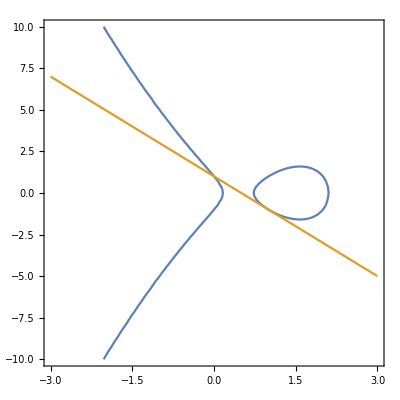

```mathematica
ContourPlot[{y^2==1-8x+12x^2-4x^3,y+2x-1==0},{x,-3,3},{y,-10,10}]
```

```mathematica
ClearAll[EllipticAdd];
EllipticAdd[curve_,P_,Q_]:=Module[{sol,lam,nu,sol1,tem,pos},
If[P===Infinity,Return[Q]];
If[Q===Infinity,Return[P]];
If[P[[1]]==Q[[1]],
If[P[[2]]!=Q[[2]],Return[Infinity],
tem=curve/.{y->0};sol={lam->(-(D[tem,x]/2y)/.{x->P[[1]],y->P[[2]]}),nu->P[[2]]-lam*P[[1]]};
sol={y->((lam*x+nu)//.sol)}
],
If[P[[2]]==Q[[2]],
sol={y->P[[2]]},
sol=Solve[{nu==P[[2]]-lam*P[[1]],nu==Q[[2]]-lam*Q[[1]]},{lam,nu}][[1]];
sol={y->((lam*x+nu)/.sol)}
];
];
sol1=Solve[(curve/.sol)==0,x];
tem={P[[1]],Q[[1]]};
Do[
pos=Position[sol1,tem[[i]]][[1,1]];
sol1=Delete[sol1,pos]
,{i,1,2}];
Return[{x/.sol1[[1]],-y/.sol/.sol1[[1]]}];
];
```

```mathematica
Reap[
tem={0,1};
Do[
tem=EllipticAdd[y^2+4x^3-12x^2+8x-1,tem,{1,-1}];
Sow[tem]
,{i,1,20}];
][[2]]
```

{{{1,1},∞,{1,-1},{0,-1},{2,1},{-1,5},{3/4,1/4},{-5,-29},{14/9,-43/27},{4/25,13/125},{69/49,527/343},{-145/16,2033/32},{413/529,-4943/12167},{-516/841,-82165/24389},{7222/3481,-118669/205379},{-1885/16641,3085549/2146689},{90211/98596,12597407/15479572},{-475881/4225,-665302133/274625},{2577626/2337841,-4238455369/3574558889},{1057160/13608721,-33642446759/50202571769}}}

The x coordinates of odd terms match the results from Somos-4 sequence.

### Quiver

#### basic example

```mathematica
ClearAll[g];
g=Graph[{1->2,2->3},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];]},GraphLayout->"GridEmbedding"];
```

```mathematica
Dynamic[g]
```

```mathematica
ClearAll[g];
g=Graph[{1->2,2->3,1->3},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];]},GraphLayout->"GridEmbedding"];
Dynamic[g]
```

#### Somos-4 quiver

```mathematica
ClearAll[g];
g=Graph[{1->2,1->4,2->3,2->3,2->3,3->1,3->1,3->4,4->2,4->2},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];]},VertexCoordinates->{1->{0,2},2->{2,2},3->{2,0},4->{0,0}},GraphLayout->"GridEmbedding"];
Dynamic[g]
```

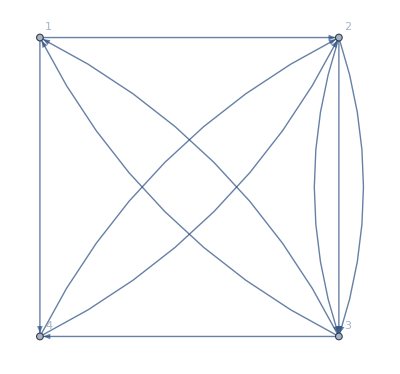

#### Markov triples

```mathematica
ClearAll[g];
g=Graph[{1->2,1->2,2->3,2->3,3->1,3->1},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];]},VertexCoordinates->{1->{1,Sqrt[3]},2->{0,0},3->{2,0}},GraphLayout->"GridEmbedding"];
Dynamic[g]
```

```mathematica
x1^2+x2^2+x3^2=3x1*x2*x3
```

#### exchange matrix

```mathematica
(*exchange matrix to quiver*)
```

```mathematica
Bm={{0,2,-2},{-2,0,2},{2,-2,0}};
```

```mathematica
ClearAll[h]
```

```mathematica
h=CreateQuiver[Bm];
```

3 mutable variables; 0 frozen variables.

```mathematica
Dynamic[h]
```

```mathematica
(*mutation of exchange matrix *)
```

```mathematica
Bm={{0,1},{-2,0},{1,0}};(*C2*)
```

```mathematica
MutateB[Bm,{x1,x2,y},1]
```

{{{0,-2},{2,0},{-1,2}},{(x2^2+y)/x1,x2,y}}

```mathematica
temp={Bm,{x1,x2,y}};
Reap[
Do[
temp=MutateB[temp[[1]],temp[[2]],Mod[i,2]+1];
Sow[temp];
,{i,2,7}]][[2,1]]
```

{{{{0,-1},{2,0},{-1,1}},{(x2^2+y)/x1,x2,y}},{{{0,1},{-2,0},{1,-1}},{(x2^2+y)/x1,(x2^2+y+x1 y)/(x1 x2),y}},{{{0,-1},{2,0},{-1,0}},{(x2^2+y+2 x1 y+x1^2 y)/(x1 x2^2),(x2^2+y+x1 y)/(x1 x2),y}},{{{0,1},{-2,0},{-1,0}},{(x2^2+y+2 x1 y+x1^2 y)/(x1 x2^2),(1+x1)/x2,y}},{{{0,-1},{2,0},{1,0}},{x1,(1+x1)/x2,y}},{{{0,1},{-2,0},{1,0}},{x1,x2,y}}}

```mathematica
cv=%[[All,2]]
```

{{(x2^2+y)/x1,x2,y},{(x2^2+y)/x1,(x2^2+y+x1 y)/(x1 x2),y},{(x2^2+y+2 x1 y+x1^2 y)/(x1 x2^2),(x2^2+y+x1 y)/(x1 x2),y},{(x2^2+y+2 x1 y+x1^2 y)/(x1 x2^2),(1+x1)/x2,y},{x1,(1+x1)/x2,y},{x1,x2,y}}

```mathematica
cv/.{y->1}//Factor
```

{{(1+x2^2)/x1,x2,1},{(1+x2^2)/x1,(1+x1+x2^2)/(x1 x2),1},{(1+2 x1+x1^2+x2^2)/(x1 x2^2),(1+x1+x2^2)/(x1 x2),1},{(1+2 x1+x1^2+x2^2)/(x1 x2^2),(1+x1)/x2,1},{x1,(1+x1)/x2,1},{x1,x2,1}}

Mutation of Y seeds is different from mutation of x variables

```mathematica
MutateY[Bm,{y/x2^2,x1},1]
```

{{{0,-1},{2,0},{-1,1}},{x2^2/y,(x1 y)/(x2^2+y)}}

```mathematica
temp={Bm,{y/x2^2,x1}};
Reap[
Do[
temp=MutateY[temp[[1]],temp[[2]],Mod[i,2]+1];
Sow[temp];
,{i,2,7}]][[2,1]]
```

{{{{0,-1},{2,0},{-1,1}},{x2^2/y,(x1 y)/(x2^2+y)}},{{{0,1},{-2,0},{1,-1}},{(x1^2 x2^2 y)/((x2^2+y+x1 y)^2),(x2^2+y)/(x1 y)}},{{{0,-1},{2,0},{-1,0}},{((x2^2+y+x1 y)^2)/(x1^2 x2^2 y),(x1 x2^2)/(x2^2+y+2 x1 y+x1^2 y)}},{{{0,1},{-2,0},{-1,0}},{x2^2/((1+x1)^2 y),(x2^2+y+2 x1 y+x1^2 y)/(x1 x2^2)}},{{{0,-1},{2,0},{1,0}},{((1+x1)^2 y)/x2^2,1/x1}},{{{0,1},{-2,0},{1,0}},{y/x2^2,x1}}}

```mathematica
temp={Bm,{y1,y2}};
Reap[
Do[
temp=MutateY[temp[[1]],temp[[2]],Mod[i,2]+1];
Sow[temp];
,{i,2,7}]][[2,1]]
```

{{{{0,-1},{2,0},{-1,1}},{1/y1,(y1 y2)/(1+y1)}},{{{0,1},{-2,0},{1,-1}},{(y1 y2^2)/(1+y1+y1 y2)^2,(1+y1)/(y1 y2)}},{{{0,-1},{2,0},{-1,0}},{(1+y1+y1 y2)^2/(y1 y2^2),y2/(1+y1+2 y1 y2+y1 y2^2)}},{{{0,1},{-2,0},{-1,0}},{1/(y1 (1+y2)^2),(1+y1+2 y1 y2+y1 y2^2)/y2}},{{{0,-1},{2,0},{1,0}},{y1 (1+y2)^2,1/y2}},{{{0,1},{-2,0},{1,0}},{y1,y2}}}

```mathematica
{z1,z2,z3,1-z1,1-z2,1-z3}/.{z3->1-z1-z2}/.{z1->-x2^2/(1+x1),z2->-(1+x1+x2^2)/(x1(1+x1))}//Factor
```

{-x2^2/(1+x1),-(1+x1+x2^2)/(x1 (1+x1)),(1+x1+x2^2)/x1,(1+x1+x2^2)/(1+x1),(1+2 x1+x1^2+x2^2)/(x1 (1+x1)),-(1+x2^2)/x1}

```mathematica
Bm={{0,-1,0},{1,0,-1},{0,1,0},{-1,0,0},{1,0,0},{-1,1,0},{0,-1,1},{0,0,-1},{0,0,1}};(*A3*)
```

```mathematica
MutateB[Bm,{x1,x2,x3,p12,p23,p34,p45,p56,p61},1]
```

{{{0,1,0},{-1,0,-1},{0,1,0},{1,-1,0},{-1,0,0},{1,0,0},{0,-1,1},{0,0,-1},{0,0,1}},{(p12 p34+p23 x2)/x1,x2,x3,p12,p23,p34,p45,p56,p61}}

```mathematica
tem=Reap[
temp={Bm,{x1,x2,x3,1,1,1,1,1,1}};
Do[
temp=MutateB[temp[[1]],temp[[2]],Mod[i,3]+1];
Sow[temp];
,{i,0,17}];
temp={Bm,{x1,x2,x3,1,1,1,1,1,1}};
Do[
temp=MutateB[temp[[1]],temp[[2]],Mod[i,2]+1];
Sow[temp];
,{i,0,8}];
temp={Bm,{x1,x2,x3,1,1,1,1,1,1}};
Do[
temp=MutateB[temp[[1]],temp[[2]],Mod[i,2]*2+1];
Sow[temp];
,{i,0,8}];
][[2,1]];
```

```mathematica
tem=Sort/@(%[[All,2]])//DeleteDuplicates;
```

```mathematica
tem//Length
```

13

```mathematica
tem
```

{{1,1,1,1,1,1,x2,(1+x2)/x1,x3},{1,1,1,1,1,1,(1+x2)/x1,x3,(x1+x3+x2 x3)/(x1 x2)},{1,1,1,1,1,1,(1+x2)/x1,((1+x2) (x1+x3))/(x1 x2 x3),(x1+x3+x2 x3)/(x1 x2)},{1,1,1,1,1,1,(x1+x3)/x2,((1+x2) (x1+x3))/(x1 x2 x3),(x1+x3+x2 x3)/(x1 x2)},{1,1,1,1,1,1,(x1+x3)/x2,((1+x2) (x1+x3))/(x1 x2 x3),(x1+x1 x2+x3)/(x2 x3)},{1,1,1,1,1,1,x1,(x1+x3)/x2,(x1+x1 x2+x3)/(x2 x3)},{1,1,1,1,1,1,x1,(1+x2)/x3,(x1+x1 x2+x3)/(x2 x3)},{1,1,1,1,1,1,x1,x2,(1+x2)/x3},{1,1,1,1,1,1,x2,(1+x2)/x1,(1+x2)/x3},{1,1,1,1,1,1,x3,(x1+x3)/x2,(x1+x3+x2 x3)/(x1 x2)},{1,1,1,1,1,1,(1+x2)/x3,((1+x2) (x1+x3))/(x1 x2 x3),(x1+x1 x2+x3)/(x2 x3)},{1,1,1,1,1,1,x1,x2,x3},{1,1,1,1,1,1,x1,x3,(x1+x3)/x2}}

```mathematica
Solve[{z1==-((x1+x3)(1+x2))/(x1*x2),z2==-((x1+x3)(1+x2))/(x3*x2),z3==(x1+x3)/x2},{x1,x2,x3}]
```

{{x1→-(z2 z3)/(z1+z2+z1 z2),x2→(-z1-z2)/(z1+z2+z1 z2),x3→-(z1 z3)/(z1+z2+z1 z2)}}

```mathematica
{x1->(z2 z3)/(-z1-z2+z1 z2),x2->(z1+z2)/(-z1-z2+z1 z2),x3->(z1 z3)/(-z1-z2+z1 z2)}/.{z1->1+z1,z2->z2+1}//Factor
```

{x1→((1+z2) z3)/(-1+z1 z2),x2→(2+z1+z2)/(-1+z1 z2),x3→((1+z1) z3)/(-1+z1 z2)}

```mathematica
tem/.{x1->-(z2 z3)/(z1+z2+z1 z2),x2->(-z1-z2)/(z1+z2+z1 z2),x3->-(z1 z3)/(z1+z2+z1 z2)}//Factor
```

{{1,1,1,1,1,1,-(z1+z2)/(z1+z2+z1 z2),-z1/z3,-(z1 z3)/(z1+z2+z1 z2)},{1,1,1,1,1,1,-z1/z3,-(z1 z3)/(z1+z2+z1 z2),-1-z1},{1,1,1,1,1,1,-z1/z3,(z1+z2+z1 z2)/z3,-1-z1},{1,1,1,1,1,1,z3,(z1+z2+z1 z2)/z3,-1-z1},{1,1,1,1,1,1,z3,(z1+z2+z1 z2)/z3,-1-z2},{1,1,1,1,1,1,-(z2 z3)/(z1+z2+z1 z2),z3,-1-z2},{1,1,1,1,1,1,-(z2 z3)/(z1+z2+z1 z2),-z2/z3,-1-z2},{1,1,1,1,1,1,-(z2 z3)/(z1+z2+z1 z2),-(z1+z2)/(z1+z2+z1 z2),-z2/z3},{1,1,1,1,1,1,-(z1+z2)/(z1+z2+z1 z2),-z1/z3,-z2/z3},{1,1,1,1,1,1,-(z1 z3)/(z1+z2+z1 z2),z3,-1-z1},{1,1,1,1,1,1,-z2/z3,(z1+z2+z1 z2)/z3,-1-z2},{1,1,1,1,1,1,-(z2 z3)/(z1+z2+z1 z2),-(z1+z2)/(z1+z2+z1 z2),-(z1 z3)/(z1+z2+z1 z2)},{1,1,1,1,1,1,-(z2 z3)/(z1+z2+z1 z2),-(z1 z3)/(z1+z2+z1 z2),z3}}

#### n-gon

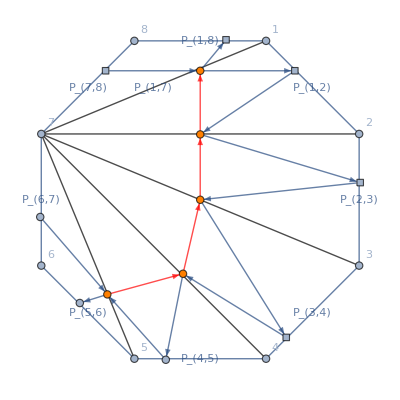

```mathematica
Graph[{UndirectedEdge[1,2],UndirectedEdge[2,3],UndirectedEdge[3,4],UndirectedEdge[4,5],UndirectedEdge[5,6],UndirectedEdge[6,7],UndirectedEdge[7,8],UndirectedEdge[8,1],UndirectedEdge[7,1],DirectedEdge[10,9],DirectedEdge[10,11],DirectedEdge[12,10],DirectedEdge[13,10],DirectedEdge[11,13],UndirectedEdge[7,2],UndirectedEdge[7,3],UndirectedEdge[7,4],UndirectedEdge[7,5],DirectedEdge[14,13],DirectedEdge[15,14],DirectedEdge[13,15],DirectedEdge[16,14],DirectedEdge[14,17],DirectedEdge[17,16],DirectedEdge[18,16],DirectedEdge[16,19],DirectedEdge[19,18],DirectedEdge[21,18],DirectedEdge[18,20]},EdgeLabels->{1<->2->Subscript[P, 1,2],2<->3->Subscript[P, 2,3],3<->4->Subscript[P, 3,4],4<->5->Subscript[P, 4,5],5<->6->Subscript[P, 5,6],6<->7->Subscript[P, 6,7],7<->8->Subscript[P, 7,8],8<->1->Subscript[P, 1,8],7<->1->Subscript[P, 1,7]},EdgeStyle->{7<->1->Black,7<->2->Black,7<->3->Black,7<->4->Black,7<->5->Black,DirectedEdge[13,10]->Red,DirectedEdge[14,13]->Red,DirectedEdge[16,14]->Red,DirectedEdge[18,16]->Red}, VertexLabels->{1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8},
VertexStyle->{18->Orange,16->Orange,14->Orange,13->Orange,10->Orange}, VertexShapeFunction->{9->"Square",11->"Square",12->"Square",15->"Square",17->"Square"},VertexCoordinates->{1->{Cos[3*Pi/8],Sin[3*Pi/8]},2->{Cos[Pi/8],Sin[Pi/8]},3->{Cos[Pi/8],-Sin[Pi/8]},4->{Cos[3*Pi/8],-Sin[3*Pi/8]},5->{-Cos[3*Pi/8],-Sin[3*Pi/8]},6->{-Cos[Pi/8],-Sin[Pi/8]},7->{-Cos[Pi/8],Sin[Pi/8]},8->{-Cos[3*Pi/8],Sin[3*Pi/8]},9->{0.15,0.93},10->{0,0.75},11->{0.55,0.75},12->{-0.55,0.75},13->{0,0.38},14->{0,0},15->{0.93,0.1},16->{-0.1,-0.43},17->{0.5,-0.8},18->{-0.54,-0.55},19->{-0.2,-0.93},20->{-0.7,-0.6},21->{-0.93,-0.1}}]
```

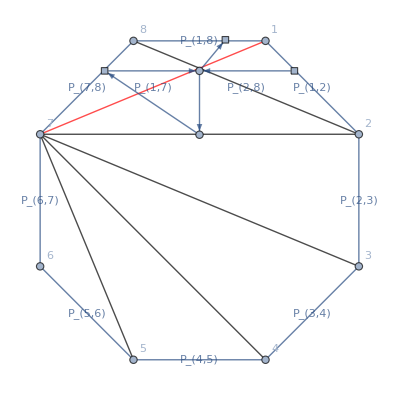

```mathematica
Graph[{UndirectedEdge[1,2],UndirectedEdge[2,3],UndirectedEdge[3,4],UndirectedEdge[4,5],UndirectedEdge[5,6],UndirectedEdge[6,7],UndirectedEdge[7,8],UndirectedEdge[8,1],UndirectedEdge[8,2],UndirectedEdge[7,1],DirectedEdge[10,9],DirectedEdge[11,10],DirectedEdge[12,10],DirectedEdge[10,13],DirectedEdge[13,12],UndirectedEdge[7,2],UndirectedEdge[7,3],UndirectedEdge[7,4],UndirectedEdge[7,5]},EdgeLabels->{1<->2->Subscript[P, 1,2],2<->3->Subscript[P, 2,3],3<->4->Subscript[P, 3,4],4<->5->Subscript[P, 4,5],5<->6->Subscript[P, 5,6],6<->7->Subscript[P, 6,7],7<->8->Subscript[P, 7,8],8<->1->Subscript[P, 1,8],8<->2->Subscript[P, 2,8],7<->1->Subscript[P, 1,7]},EdgeStyle->{7<->1->Red,8<->2->Black,7<->2->Black,7<->3->Black,7<->4->Black,7<->5->Black}, VertexLabels->{1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8},VertexShapeFunction->{9->"Square",11->"Square",12->"Square"},VertexCoordinates->{1->{Cos[3*Pi/8],Sin[3*Pi/8]},2->{Cos[Pi/8],Sin[Pi/8]},3->{Cos[Pi/8],-Sin[Pi/8]},4->{Cos[3*Pi/8],-Sin[3*Pi/8]},5->{-Cos[3*Pi/8],-Sin[3*Pi/8]},6->{-Cos[Pi/8],-Sin[Pi/8]},7->{-Cos[Pi/8],Sin[Pi/8]},8->{-Cos[3*Pi/8],Sin[3*Pi/8]},9->{0.15,0.93},10->{0,0.75},11->{0.55,0.75},12->{-0.55,0.75},13->{0,0.38}}]
```

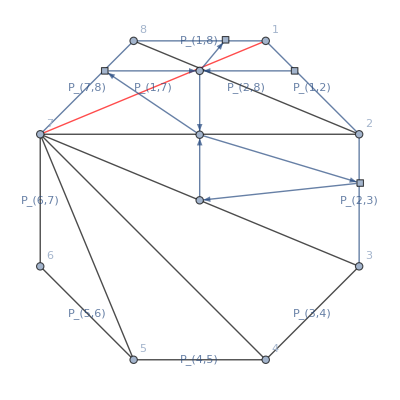

```mathematica
Graph[{UndirectedEdge[1,2],UndirectedEdge[2,3],UndirectedEdge[3,4],UndirectedEdge[4,5],UndirectedEdge[5,6],UndirectedEdge[6,7],UndirectedEdge[7,8],UndirectedEdge[8,1],UndirectedEdge[8,2],UndirectedEdge[7,1],DirectedEdge[10,9],DirectedEdge[11,10],DirectedEdge[12,10],DirectedEdge[10,13],DirectedEdge[13,12],DirectedEdge[14,13],DirectedEdge[13,15],DirectedEdge[15,14],UndirectedEdge[7,2],UndirectedEdge[7,3],UndirectedEdge[7,4],UndirectedEdge[7,5]},EdgeLabels->{1<->2->Subscript[P, 1,2],2<->3->Subscript[P, 2,3],3<->4->Subscript[P, 3,4],4<->5->Subscript[P, 4,5],5<->6->Subscript[P, 5,6],6<->7->Subscript[P, 6,7],7<->8->Subscript[P, 7,8],8<->1->Subscript[P, 1,8],8<->2->Subscript[P, 2,8],7<->1->Subscript[P, 1,7]},EdgeStyle->{7<->1->Red,8<->2->Black,7<->2->Black,7<->3->{Black,Thick},7<->4->Black,7<->5->Black,6<->7->{Black,Thick},5<->6->{Black,Thick},4<->5->{Black,Thick},3<->4->{Black,Thick}}, VertexLabels->{1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8},VertexShapeFunction->{9->"Square",11->"Square",12->"Square",15->"Square"},VertexCoordinates->{1->{Cos[3*Pi/8],Sin[3*Pi/8]},2->{Cos[Pi/8],Sin[Pi/8]},3->{Cos[Pi/8],-Sin[Pi/8]},4->{Cos[3*Pi/8],-Sin[3*Pi/8]},5->{-Cos[3*Pi/8],-Sin[3*Pi/8]},6->{-Cos[Pi/8],-Sin[Pi/8]},7->{-Cos[Pi/8],Sin[Pi/8]},8->{-Cos[3*Pi/8],Sin[3*Pi/8]},9->{0.15,0.93},10->{0,0.75},11->{0.55,0.75},12->{-0.55,0.75},13->{0,0.38},14->{0,0},15->{0.93,0.1}}]
```

### D_n

#### D_8

```mathematica
Table[i->{3*Cos[(i-9)*Pi/4],3*Sin[(i-9)*Pi/4]},{i,9,16}]
```

{9→{3,0},10→{3/(√2),3/(√2)},11→{0,3},12→{-3/(√2),3/(√2)},13→{-3,0},14→{-3/(√2),-3/(√2)},15→{0,-3},16→{3/(√2),-3/(√2)}}

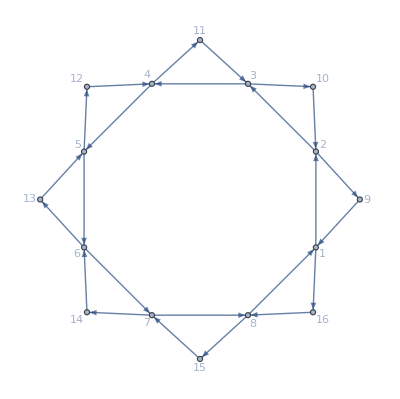

```mathematica
ClearAll[g];
g=Graph[{1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->1,1->16,16->8,2->9,9->1,3->10,10->2,4->11,11->3,5->12,12->4,6->13,13->5,7->14,14->6,8->15,15->7},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];],5->Button[5,g=MutateGraph[g,5];],6->Button[6,g=MutateGraph[g,6];],7->Button[7,g=MutateGraph[g,7];],8->Button[8,g=MutateGraph[g,8];],9->Button[9,Null],10->Button[10,Null],11->Button[11,Null],12->Button[12,Null],13->Button[13,Null],14->Button[14,Null],15->Button[15,Null],16->Button[16,Null]},VertexCoordinates->{9->{3,0},10->{3/(√2),3/(√2)},11->{0,3},12->{-3/(√2),3/(√2)},13->{-3,0},14->{-3/(√2),-3/(√2)},15->{0,-3},16->{3/(√2),-3/(√2)}},GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Dynamic[g]
```

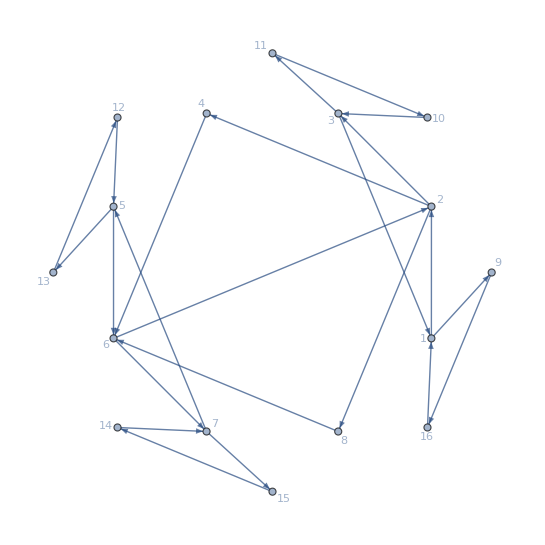

#### D_4

```mathematica
StringJoin[Table[ToString[i]<>"->Button["<>ToString[i]<>",g=MutateGraph[g,"<>ToString[i]<>"];],",{i,1,8}]]
```

1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];],5->Button[5,g=MutateGraph[g,5];],6->Button[6,g=MutateGraph[g,6];],7->Button[7,g=MutateGraph[g,7];],8->Button[8,g=MutateGraph[g,8];],

```mathematica
StringJoin[Table[ToString[i]<>"->Button["<>ToString[i]<>",Null],",{i,9,16}]]
```

9->Button[9,Null],10->Button[10,Null],11->Button[11,Null],12->Button[12,Null],13->Button[13,Null],14->Button[14,Null],15->Button[15,Null],16->Button[16,Null],

```mathematica
Table[i->{3*Cos[(i-9)*Pi/4],3*Sin[(i-9)*Pi/4]},{i,9,16}]
```

{9→{3,0},10→{3/(√2),3/(√2)},11→{0,3},12→{-3/(√2),3/(√2)},13→{-3,0},14→{-3/(√2),-3/(√2)},15→{0,-3},16→{3/(√2),-3/(√2)}}

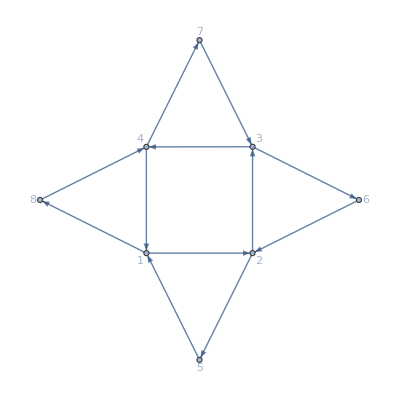

```mathematica
ClearAll[g];
g=Graph[{1->2,2->3,3->4,4->1,5->1,2->5,3->6,6->2,4->7,7->3,1->8,8->4},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];],5->Button[5,Null],6->Button[6,Null],7->Button[7,Null],8->Button[8,Null]},VertexCoordinates->{5->{0,-3},6->{3,0},7->{0,3},8->{-3,0}},GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Dynamic[g]
```

### G37

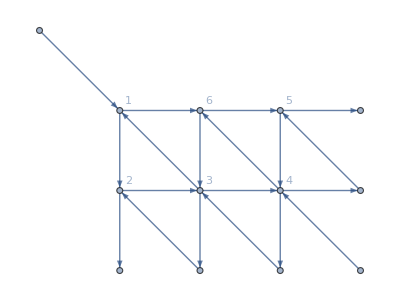

```mathematica
ClearAll[g];
g=Graph[{1->2,2->3,3->1,1->6,6->3,3->4,4->6,6->5,5->4,0->1,2->7,8->2,3->8,9->3,4->9,10->4,4->11,11->5,5->12},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];],5->Button[5,g=MutateGraph[g,5];],6->Button[6,g=MutateGraph[g,6];]},VertexCoordinates->{1->{0,0},2->{0,-1},3->{1,-1},4->{2,-1},5->{2,0},6->{1,0},0->{-1,1},7->{0,-2},8->{1,-2},9->{2,-2},10->{3,-2},11->{3,-1},12->{3,0}},GraphLayout->"GridEmbedding"]
```

```mathematica
Dynamic[g]
```

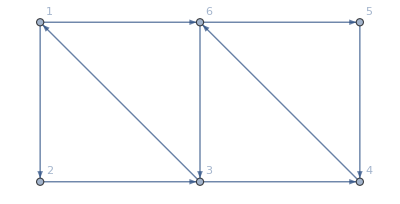

```mathematica
ClearAll[g];
g=Graph[{1->2,2->3,3->1,1->6,6->3,3->4,4->6,6->5,5->4},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];],5->Button[5,g=MutateGraph[g,5];],6->Button[6,g=MutateGraph[g,6];]},VertexCoordinates->{1->{0,0},2->{0,-1},3->{1,-1},4->{2,-1},5->{2,0},6->{1,0}},GraphLayout->"GridEmbedding"]
```

```mathematica
Dynamic[g]
```

```mathematica
exMat={{0,1,0,1,-1,0},{-1,0,1,0,1,-1},{0,-1,0,0,0,1},{-1,0,0,0,1,0},{1,-1,0,-1,0,1},{0,1,-1,0,-1,0},{0,0,0,-1,0,0},{0,0,0,1,-1,0},{0,0,0,0,1,-1},{0,0,0,0,0,1},{0,0,1,0,0,-1},{0,0,-1,0,0,0},{1,0,0,0,0,0}};
xv={GramM[{1,2,3},{4,6,7}],GramM[{1,2,3},{3,6,7}],GramM[{1,2,3},{2,6,7}],GramM[{1,2,3},{4,5,7}],GramM[{1,2,3},{3,4,7}],GramM[{1,2,3},{2,3,7}],GramM[{1,2,3},{4,5,6}],GramM[{1,2,3},{3,4,5}],GramM[{1,2,3},{2,3,4}],GramM[{1,2,3},{1,2,3}],GramM[{1,2,3},{1,2,7}],GramM[{1,2,3},{1,6,7}],GramM[{1,2,3},{5,6,7}]};
```

```mathematica
exMat//Dimensions
xv//Length
```

{13,6}

13

```mathematica
ml={4,5,6,1,2,3,4,5,6,1,2,3};
tem=Reap[
temp={exMat,xv};
Do[
temp=MutateB[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

```mathematica
tem//Length
```

12

```mathematica
var=tem[[6,2,{1,2,3,4,5,6}]]
```

{-a[1,6] a[2,5] a[3,3]+a[1,5] a[2,6] a[3,3]+a[1,6] a[2,3] a[3,5]-a[1,3] a[2,6] a[3,5]-a[1,5] a[2,3] a[3,6]+a[1,3] a[2,5] a[3,6],-a[1,6] a[2,3] a[2,5]+a[1,5] a[2,3] a[2,6]+a[1,6] a[2,2] a[3,5]-a[1,2] a[2,6] a[3,5]-a[1,5] a[2,2] a[3,6]+a[1,2] a[2,5] a[3,6],-a[1,3] a[1,6] a[2,5]+a[1,3] a[1,5] a[2,6]+a[1,2] a[1,6] a[3,5]-a[1,1] a[2,6] a[3,5]-a[1,2] a[1,5] a[3,6]+a[1,1] a[2,5] a[3,6],-a[1,6] a[2,4] a[3,3]+a[1,4] a[2,6] a[3,3]+a[1,6] a[2,3] a[3,4]-a[1,3] a[2,6] a[3,4]-a[1,4] a[2,3] a[3,6]+a[1,3] a[2,4] a[3,6],-a[1,6] a[2,3]^2+a[1,3] a[2,3] a[2,6]+a[1,6] a[2,2] a[3,3]-a[1,2] a[2,6] a[3,3]-a[1,3] a[2,2] a[3,6]+a[1,2] a[2,3] a[3,6],-a[1,3] a[1,6] a[2,2]+a[1,2] a[1,6] a[2,3]+a[1,2] a[1,3] a[2,6]-a[1,1] a[2,3] a[2,6]-a[1,2]^2 a[3,6]+a[1,1] a[2,2] a[3,6]}

```mathematica
varcheck={GramM[{1,2,3},{3,5,6}],GramM[{1,2,3},{2,5,6}],GramM[{1,2,3},{1,5,6}],GramM[{1,2,3},{3,4,6}],GramM[{1,2,3},{2,3,6}],GramM[{1,2,3},{1,2,6}]};
```

```mathematica
var-varcheck
```

{0,0,0,0,0,0}

```mathematica
var=tem[[12,2,{1,2,3,4,5,6}]]
```

{-a[1,5] a[2,3] a[2,4]+a[1,4] a[2,3] a[2,5]+a[1,5] a[2,2] a[3,4]-a[1,2] a[2,5] a[3,4]-a[1,4] a[2,2] a[3,5]+a[1,2] a[2,4] a[3,5],-a[1,3] a[1,5] a[2,4]+a[1,3] a[1,4] a[2,5]+a[1,2] a[1,5] a[3,4]-a[1,1] a[2,5] a[3,4]-a[1,2] a[1,4] a[3,5]+a[1,1] a[2,4] a[3,5],-a[1,7] a[2,5] a[3,4]+a[1,5] a[2,7] a[3,4]+a[1,7] a[2,4] a[3,5]-a[1,4] a[2,7] a[3,5]-a[1,5] a[2,4] a[3,7]+a[1,4] a[2,5] a[3,7],-a[1,5] a[2,3]^2+a[1,3] a[2,3] a[2,5]+a[1,5] a[2,2] a[3,3]-a[1,2] a[2,5] a[3,3]-a[1,3] a[2,2] a[3,5]+a[1,2] a[2,3] a[3,5],-a[1,3] a[1,5] a[2,2]+a[1,2] a[1,5] a[2,3]+a[1,2] a[1,3] a[2,5]-a[1,1] a[2,3] a[2,5]-a[1,2]^2 a[3,5]+a[1,1] a[2,2] a[3,5],-a[1,3] a[1,7] a[2,5]+a[1,3] a[1,5] a[2,7]+a[1,2] a[1,7] a[3,5]-a[1,1] a[2,7] a[3,5]-a[1,2] a[1,5] a[3,7]+a[1,1] a[2,5] a[3,7]}

```mathematica
varcheck={GramM[{1,2,3},{2,4,5}],GramM[{1,2,3},{1,4,5}],GramM[{1,2,3},{4,5,7}],GramM[{1,2,3},{2,3,5}],GramM[{1,2,3},{1,2,5}],GramM[{1,2,3},{1,5,7}]};
```

```mathematica
var-varcheck//Factor
```

{0,0,0,0,0,0}

### G48

#### OPE parameterization: 1303.1396

#### momentum twistor parameterization

The momentum twistor parameterization from 2112.11842

```mathematica
fdefE711={f[1]->(ab[1,2,3,6] ab[1,2,4,5])/(ab[1,2,3,4] ab[1,2,5,6]),f[2]->(ab[1,2,3,7] ab[1,2,5,6])/(ab[1,2,3,5] ab[1,2,6,7]),f[3]->(ab[1,2,3,8] ab[1,2,6,7])/(ab[1,2,3,6] ab[1,2,7,8]),f[4]->(ab[1,2,5,6] ab[1,3,4,5])/(ab[1,2,3,5] ab[1,4,5,6]),f[5]->(ab[1,2,3,5] ab[1,2,6,7] ab[1,4,5,6])/(ab[1,2,3,6] ab[1,2,4,5] ab[1,5,6,7]),f[6]->(ab[1,2,3,6] ab[1,2,7,8] ab[1,5,6,7])/(ab[1,2,3,7] ab[1,2,5,6] ab[1,6,7,8]),f[7]->(ab[1,4,5,6] ab[2,3,4,5])/(ab[1,2,4,5] ab[3,4,5,6]),f[8]->(ab[1,2,4,5] ab[1,5,6,7] ab[3,4,5,6])/(ab[1,2,5,6] ab[1,3,4,5] ab[4,5,6,7]),f[9]->(ab[1,2,5,6] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,6] ab[5,6,7,8])};
```

```mathematica
MatE711={{1,0,0,0},{(1+f[9]+f[8] f[9]+f[7] f[8] f[9])/(f[7] f[8] f[9]),1,0,0},{(1+f[5]+f[4] f[5]+f[5] f[9]+f[4] f[5] f[9]+f[4] f[5] f[8] f[9])/(f[4] f[5] f[7] f[8] f[9]),(1+f[6]+f[5] f[6]+f[4] f[5] f[6])/(f[4] f[5] f[6]),1,0},{(1+f[1]+f[1] f[5]+f[1] f[5] f[9])/(f[1] f[4] f[5] f[7] f[8] f[9]),(1+f[2]+f[1] f[2]+f[2] f[6]+f[1] f[2] f[6]+f[1] f[2] f[5] f[6])/(f[1] f[2] f[4] f[5] f[6]),(1+f[3]+f[2] f[3]+f[1] f[2] f[3])/(f[1] f[2] f[3]),1},{1/(f[1] f[4] f[5] f[7] f[8] f[9]),(1+f[2]+f[2] f[6])/(f[1] f[2] f[4] f[5] f[6]),(1+f[3]+f[2] f[3])/(f[1] f[2] f[3]),1},{0,1/(f[1] f[2] f[4] f[5] f[6]),(1+f[3])/(f[1] f[2] f[3]),1},{0,0,1/(f[1] f[2] f[3]),1},{0,0,0,1}};
```

```mathematica
((FB[1,2,3,HoldForm[k+5]]*FB[1,2,HoldForm[k+3],HoldForm[k+4]]/FB[1,2,3,HoldForm[k+3]]/FB[1,2,HoldForm[k+4],HoldForm[k+5]]/.{k->1})//ReleaseHold)/.{FB[a__]:>fB[a,"explicitM"->MatE711]}
```

f[1]

We first work out how the parity-even letters of 8-point amplitudes fold

data from 1105.5606

```mathematica
frozen=Table[br[i,If[i+1>8,Mod[i+1,8],i+1],If[i+2>8,Mod[i+2,8],i+2],If[i+3>8,Mod[i+3,8],i+3]],{i,1,8}]
```

{br[1,2,3,4],br[2,3,4,5],br[3,4,5,6],br[4,5,6,7],br[5,6,7,8],br[1,6,7,8],br[1,2,7,8],br[1,2,3,8]}

```mathematica
first=FactorList[#][[All,1]]&/@(Cases[symbol,Tensor[a_,__]:>{a},Infinity]//Flatten//DeleteDuplicates)//Flatten//DeleteDuplicates//DeleteCases[#,1]&//Complement[#,frozen]&
```

{br[1,2,4,5],br[1,2,5,6],br[1,2,6,7],br[1,3,4,8],br[1,4,5,8],br[1,5,6,8],br[2,3,5,6],br[2,3,6,7],br[2,3,7,8],br[3,4,6,7],br[3,4,7,8],br[4,5,7,8]}

```mathematica
first={br[1,2,4,5],br[1,2,5,6],br[1,2,6,7],br[1,3,4,8],br[1,4,5,8],br[1,5,6,8],br[2,3,5,6],br[2,3,6,7],br[2,3,7,8],br[3,4,6,7],br[3,4,7,8],br[4,5,7,8]};
```

```mathematica
last=FactorList[#][[All,1]]&/@(Cases[symbol,Tensor[__,a_]:>{a},Infinity]//Flatten//DeleteDuplicates)//Flatten//DeleteDuplicates//DeleteCases[#,1]&//Complement[#,{br[1,2,3,4],br[2,3,4,5],br[3,4,5,6],br[4,5,6,7],br[5,6,7,8],br[1,6,7,8],br[1,2,7,8],br[1,2,3,8]}]&
```

{br[1,2,3,5],br[1,2,3,6],br[1,2,3,7],br[1,2,4,8],br[1,2,5,8],br[1,2,6,8],br[1,3,4,5],br[1,3,7,8],br[1,4,5,6],br[1,4,7,8],br[1,5,6,7],br[1,5,7,8],br[2,3,4,6],br[2,3,4,7],br[2,3,4,8],br[2,4,5,6],br[2,5,6,7],br[2,6,7,8],br[3,4,5,7],br[3,4,5,8],br[3,5,6,7],br[3,6,7,8],br[4,5,6,8],br[4,6,7,8]}

```mathematica
last={br[1,2,3,5],br[1,2,3,6],br[1,2,3,7],br[1,2,4,8],br[1,2,5,8],br[1,2,6,8],br[1,3,4,5],br[1,3,7,8],br[1,4,5,6],br[1,4,7,8],br[1,5,6,7],br[1,5,7,8],br[2,3,4,6],br[2,3,4,7],br[2,3,4,8],br[2,4,5,6],br[2,5,6,7],br[2,6,7,8],br[3,4,5,7],br[3,4,5,8],br[3,5,6,7],br[3,6,7,8],br[4,5,6,8],br[4,6,7,8]};
```

```mathematica
alphabet8=Join[first,last,FactorList[#][[All,1]]&/@(Cases[symbol,Tensor[a__]:>{a},Infinity]//Flatten//DeleteDuplicates)//Flatten//DeleteDuplicates//DeleteCases[#,1]&//Complement[#,{br[1,2,3,4],br[2,3,4,5],br[3,4,5,6],br[4,5,6,7],br[5,6,7,8],br[1,6,7,8],br[1,2,7,8],br[1,2,3,8]}]&//Complement[#,first]&//Complement[#,last]&];
```

```mathematica
alphabet8=;
```

```mathematica
alphabet8//Length
```

108

#### the quivers and mutation

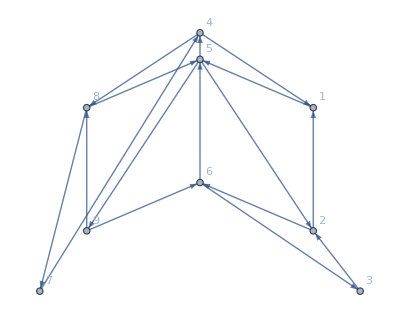

```mathematica
ClearAll[g];
g=Graph[{7->4,4->8,8->7,4->1,1->5,5->4,8->5,5->9,9->8,3->2,2->6,6->3,9->6,6->5,5->2,2->1},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];],5->Button[5,g=MutateGraph[g,5];],6->Button[6,g=MutateGraph[g,6];],7->Button[7,g=MutateGraph[g,7];],8->Button[8,g=MutateGraph[g,8];],9->Button[9,g=MutateGraph[g,9];]},VertexCoordinates->{{0.,0.},{1.4692632954328266,2.3754513411849483},{0.43033725588378147,1.6871755247669755},{2.5081893349818727,1.6871755247669755},{1.4692632954328273,2.131432434507923},{0.4303372558837819,0.5546427986080558},{2.9385265908656533,0.},{2.508189334981873,0.5546427986080557},{1.4692632954328277,0.9988997083490033}},GraphLayout->"HighDimensionalEmbedding"]
```

```mathematica
Dynamic[g]
```

```mathematica
seq1={4,8,1,6,7,3};
seq2={7,3,9,2,8,1,6,8,1,7,3,6,7,3,9,2,6,7,3};
seq3={7,3,8,1,9,2,6,8,1,7,3,9,2,6};
seq4={5,8,1,5,8,1,4,7,3,6,5,8,1,5,8,1,6,4,7,3};
```

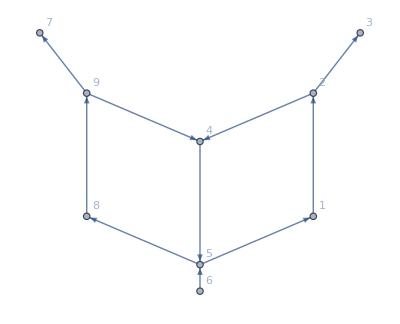

```mathematica
Graph[List[7,4,8,1,5,9,3,2,6],List[DirectedEdge[9,7],DirectedEdge[2,3],DirectedEdge[8,9],DirectedEdge[9,4],DirectedEdge[1,2],DirectedEdge[2,4],DirectedEdge[5,8],DirectedEdge[5,1],DirectedEdge[4,5],DirectedEdge[6,5]],List[Rule[FormatType,TraditionalForm],Rule[GraphLayout,List[Rule["Dimension",2],Rule["VertexLayout","HighDimensionalEmbedding"]]],Rule[VertexLabels,List[Rule[8,Button[8,CompoundExpression[Set[g,MutateGraph[g,8]],Null]]],Rule[2,Button[2,CompoundExpression[Set[g,MutateGraph[g,2]],Null]]],Rule[1,Button[1,CompoundExpression[Set[g,MutateGraph[g,1]],Null]]],Rule[4,Button[4,CompoundExpression[Set[g,MutateGraph[g,4]],Null]]],Rule[5,Button[5,CompoundExpression[Set[g,MutateGraph[g,5]],Null]]],Rule[7,Button[7,CompoundExpression[Set[g,MutateGraph[g,7]],Null]]],Rule[3,Button[3,CompoundExpression[Set[g,MutateGraph[g,3]],Null]]],Rule[9,Button[9,CompoundExpression[Set[g,MutateGraph[g,9]],Null]]],Rule[6,Button[6,CompoundExpression[Set[g,MutateGraph[g,6]],Null]]]]]]]
```

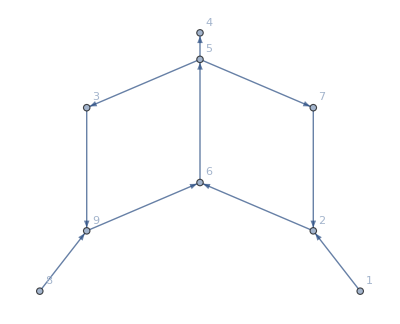

```mathematica
Graph[List[7,4,8,1,5,9,3,2,6],List[DirectedEdge[5,4],DirectedEdge[5,3],DirectedEdge[5,7],DirectedEdge[6,5],DirectedEdge[9,6],DirectedEdge[8,9],DirectedEdge[3,9],DirectedEdge[2,6],DirectedEdge[7,2],DirectedEdge[1,2]],List[Rule[FormatType,TraditionalForm],Rule[GraphLayout,List[Rule["Dimension",2],Rule["VertexLayout","HighDimensionalEmbedding"]]],Rule[VertexLabels,List[Rule[8,Button[8,CompoundExpression[Set[g,MutateGraph[g,8]],Null]]],Rule[2,Button[2,CompoundExpression[Set[g,MutateGraph[g,2]],Null]]],Rule[1,Button[1,CompoundExpression[Set[g,MutateGraph[g,1]],Null]]],Rule[4,Button[4,CompoundExpression[Set[g,MutateGraph[g,4]],Null]]],Rule[5,Button[5,CompoundExpression[Set[g,MutateGraph[g,5]],Null]]],Rule[7,Button[7,CompoundExpression[Set[g,MutateGraph[g,7]],Null]]],Rule[3,Button[3,CompoundExpression[Set[g,MutateGraph[g,3]],Null]]],Rule[9,Button[9,CompoundExpression[Set[g,MutateGraph[g,9]],Null]]],Rule[6,Button[6,CompoundExpression[Set[g,MutateGraph[g,6]],Null]]]]]]]
```

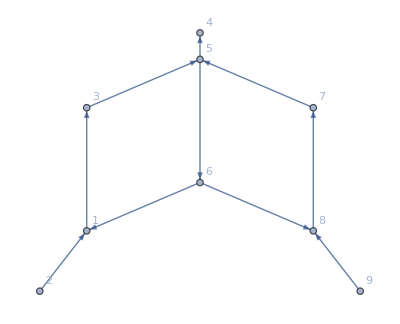

```mathematica
Graph[List[7,4,8,1,5,9,3,2,6],List[DirectedEdge[5,4],DirectedEdge[8,7],DirectedEdge[9,8],DirectedEdge[7,5],DirectedEdge[1,3],DirectedEdge[2,1],DirectedEdge[3,5],DirectedEdge[6,8],DirectedEdge[6,1],DirectedEdge[5,6]],List[Rule[FormatType,TraditionalForm],Rule[GraphLayout,List[Rule["Dimension",2],Rule["VertexLayout","HighDimensionalEmbedding"]]],Rule[VertexLabels,List[Rule[8,Button[8,CompoundExpression[Set[g,MutateGraph[g,8]],Null]]],Rule[2,Button[2,CompoundExpression[Set[g,MutateGraph[g,2]],Null]]],Rule[1,Button[1,CompoundExpression[Set[g,MutateGraph[g,1]],Null]]],Rule[4,Button[4,CompoundExpression[Set[g,MutateGraph[g,4]],Null]]],Rule[5,Button[5,CompoundExpression[Set[g,MutateGraph[g,5]],Null]]],Rule[7,Button[7,CompoundExpression[Set[g,MutateGraph[g,7]],Null]]],Rule[3,Button[3,CompoundExpression[Set[g,MutateGraph[g,3]],Null]]],Rule[9,Button[9,CompoundExpression[Set[g,MutateGraph[g,9]],Null]]],Rule[6,Button[6,CompoundExpression[Set[g,MutateGraph[g,6]],Null]]]]]]]
```

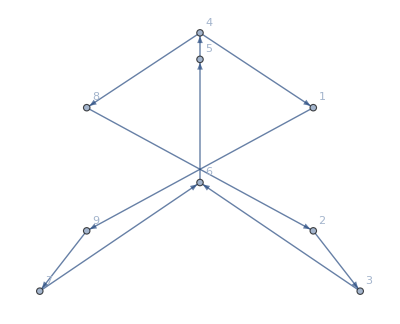

```mathematica
Graph[List[7,4,8,1,5,9,3,2,6],List[DirectedEdge[4,8],DirectedEdge[4,1],DirectedEdge[1,9],DirectedEdge[8,2],DirectedEdge[9,7],DirectedEdge[2,3],DirectedEdge[7,6],DirectedEdge[3,6],DirectedEdge[5,4],DirectedEdge[6,5]],List[Rule[FormatType,TraditionalForm],Rule[GraphLayout,List[Rule["Dimension",2],Rule["VertexLayout","HighDimensionalEmbedding"]]],Rule[VertexCoordinates,List[List[0.,0.],List[1.4692632954328266,2.3754513411849483],List[0.43033725588378147,1.6871755247669755],List[2.5081893349818727,1.6871755247669755],List[1.4692632954328273,2.131432434507923],List[0.4303372558837819,0.5546427986080558],List[2.9385265908656533,0.],List[2.508189334981873,0.5546427986080557],List[1.4692632954328277,0.9988997083490033]]],Rule[VertexLabels,List[Rule[8,Button[8,CompoundExpression[Set[g,MutateGraph[g,8]],Null]]],Rule[2,Button[2,CompoundExpression[Set[g,MutateGraph[g,2]],Null]]],Rule[1,Button[1,CompoundExpression[Set[g,MutateGraph[g,1]],Null]]],Rule[4,Button[4,CompoundExpression[Set[g,MutateGraph[g,4]],Null]]],Rule[5,Button[5,CompoundExpression[Set[g,MutateGraph[g,5]],Null]]],Rule[7,Button[7,CompoundExpression[Set[g,MutateGraph[g,7]],Null]]],Rule[3,Button[3,CompoundExpression[Set[g,MutateGraph[g,3]],Null]]],Rule[9,Button[9,CompoundExpression[Set[g,MutateGraph[g,9]],Null]]],Rule[6,Button[6,CompoundExpression[Set[g,MutateGraph[g,6]],Null]]]]]]]
```

```mathematica
g0=Graph[{7->4,4->8,8->7,4->1,1->5,5->4,8->5,5->9,9->8,3->2,2->6,6->3,9->6,6->5,5->2,2->1}];
```

```mathematica
ClearAll[MatFromQuiver];
MatFromQuiver[g_]:=Module[{edg,ver},
edg=EdgeList[g];
ver=VertexCount[g];
(*Print[edg];*)
Return[SparseArray[edg/.DirectedEdge[a_,b_]:>({{a,b}->#,{b,a}->-#}&[Count[edg,DirectedEdge[a,b]]])//Flatten,{ver,ver}]//Normal];
];
```

```mathematica
MatFromQuiver[g]
```

{{0,-1,0,-1,1,0,0,0,0},{1,0,-1,0,-1,1,0,0,0},{0,1,0,0,0,-1,0,0,0},{1,0,0,0,-1,0,-1,1,0},{-1,1,0,1,0,-1,0,-1,1},{0,-1,1,0,1,0,0,0,-1},{0,0,0,1,0,0,0,-1,0},{0,0,0,-1,1,0,1,0,-1},{0,0,0,0,-1,1,0,1,0}}

```mathematica
exMat=MatFromQuiver[g0];
xv=f/@Range[9];
```

```mathematica
exMat
```

{{0,-1,0,-1,1,0,0,0,0},{1,0,-1,0,-1,1,0,0,0},{0,1,0,0,0,-1,0,0,0},{1,0,0,0,-1,0,-1,1,0},{-1,1,0,1,0,-1,0,-1,1},{0,-1,1,0,1,0,0,0,-1},{0,0,0,1,0,0,0,-1,0},{0,0,0,-1,1,0,1,0,-1},{0,0,0,0,-1,1,0,1,0}}

```mathematica
xv
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9]}

```mathematica
ml={1,8,5,2,9,7};
tem=Reap[
temp={exMat,xv};
Do[
temp=MutateY[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

```mathematica
tem//Length
```

6

```mathematica
tem[[-1]]
```

{{{0,-1,0,0,1,0,0,0,0},{1,0,1,0,0,-1,0,0,0},{0,-1,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0},{-1,0,0,1,0,1,0,-1,0},{0,1,0,0,-1,0,0,0,1},{0,0,0,0,0,0,0,0,-1},{0,0,0,0,1,0,0,0,-1},{0,0,0,0,0,-1,1,1,0}},{((1+f[2]+f[1] f[2]) f[5] f[8])/(1+f[1]+f[8]+f[1] f[8]+f[1] f[5] f[8]),1/((1+f[1]) f[2]),(1+f[2]+f[1] f[2]) f[3],f[4] (1+f[1]+f[8]+f[1] f[8]+f[1] f[5] f[8]),((1+f[1]) (1+f[8]))/(f[1] f[5] f[8]),(f[2] f[6] (1+f[1]+f[8]+f[1] f[8]+f[1] f[5] f[8]) f[9])/((1+f[2]+f[1] f[2]) (1+f[9]+f[8] f[9])),(1+f[9]+f[8] f[9])/(f[7] f[8] f[9]),(f[1] f[5] (1+f[9]+f[8] f[9]))/(1+f[1]+f[8]+f[1] f[8]+f[1] f[5] f[8]),(f[7] f[8])/((1+f[8]) (1+f[9]+f[8] f[9]+f[7] f[8] f[9]))}}

```mathematica
list={((1+f[2]+f[1] f[2]) f[5] f[8])/(1+f[1]+f[8]+f[1] f[8]+f[1] f[5] f[8]),1/((1+f[1]) f[2]),(1+f[2]+f[1] f[2]) f[3],f[4] (1+f[1]+f[8]+f[1] f[8]+f[1] f[5] f[8]),((1+f[1]) (1+f[8]))/(f[1] f[5] f[8]),(f[2] f[6] (1+f[1]+f[8]+f[1] f[8]+f[1] f[5] f[8]) f[9])/((1+f[2]+f[1] f[2]) (1+f[9]+f[8] f[9])),(1+f[9]+f[8] f[9])/(f[7] f[8] f[9]),(f[1] f[5] (1+f[9]+f[8] f[9]))/(1+f[1]+f[8]+f[1] f[8]+f[1] f[5] f[8]),(f[7] f[8])/((1+f[8]) (1+f[9]+f[8] f[9]+f[7] f[8] f[9]))};
```

```mathematica
Solve[Thread@Equal[F/@Range[9],list],f/@Range[9]]
```

{{f[1]→(1+F[2])/(F[1] F[2] (1+F[5])),f[2]→(F[1] (1+F[5]))/(1+F[2]+F[1] F[2]+F[1] F[2] F[5]),f[3]→(F[2] F[3])/(1+F[2]),f[4]→(F[1] F[2] F[4] F[5] (1+F[5]) (1+F[7]) F[8] F[9])/((1+F[2]+F[1] F[2]+F[1] F[2] F[5]) (1+F[9]+F[7] F[9]+F[8] F[9]+F[5] F[8] F[9]+F[7] F[8] F[9]+F[5] F[7] F[8] F[9])),f[5]→((1+F[2]+F[1] F[2]+F[1] F[2] F[5]) (1+F[9]+F[7] F[9]+F[8] F[9]+F[5] F[8] F[9]+F[7] F[8] F[9]+F[5] F[7] F[8] F[9]))/((1+F[2]) F[5] (1+F[9]+F[7] F[9])),f[6]→((1+F[2]) F[5] F[6] (1+F[9]+F[7] F[9]))/(1+F[5]),f[7]→(1+F[9]+F[7] F[9]+F[8] F[9]+F[5] F[8] F[9]+F[7] F[8] F[9]+F[5] F[7] F[8] F[9])/F[7],f[8]→(1+F[9]+F[7] F[9])/((1+F[5]) (1+F[7]) F[8] F[9]),f[9]→((1+F[5]) F[8])/(1+F[9]+F[7] F[9]+F[8] F[9]+F[5] F[8] F[9]+F[7] F[8] F[9]+F[5] F[7] F[8] F[9])}}

```mathematica
{list[[3]]-list[[7]]==0,list[[2]]-list[[9]]==0,list[[1]]-list[[8]]==0}/.{f[1]->-(f[8]/(-1+f[3] f[9]+f[3] f[8] f[9])),f[2]->(-f[9]-f[3] f[9])/(-1+f[3] f[9]),f[7]->(1-f[3] f[9]-f[3] f[8] f[9])/(f[3] f[8] f[9])}//Factor
```

{True,True,True}

```mathematica
(*the folding condition for E711*)
```

```mathematica
Solve[{list[[3]]-list[[7]]==0,list[[2]]-list[[9]]==0,list[[1]]-list[[8]]==0},{f[1],f[2],f[7]}]
```

{{f[1]→-f[8]/(-1+f[3] f[9]+f[3] f[8] f[9]),f[2]→(-f[9]-f[3] f[9])/(-1+f[3] f[9]),f[7]→(1-f[3] f[9]-f[3] f[8] f[9])/(f[3] f[8] f[9])}}

```mathematica
Solve[{list[[3]]-list[[7]]==0,list[[2]]-list[[9]]==0,list[[1]]-list[[8]]==0}]
```

{{f[1]→(-1-f[2])/f[2],f[9]→1/(-1-f[8])},{f[1]→(1+f[8]+f[7] f[8])/f[7],f[2]→(1+f[9]+f[8] f[9]+f[7] f[8] f[9])/((1+f[7]) f[8]),f[3]→1/((1+f[8]+f[7] f[8]) f[9])},{f[1]→(f[2]-1/(1+f[8]+f[7] f[8])-f[2]/(1+f[8]+f[7] f[8])-f[8]/(1+f[8]+f[7] f[8])-(f[2] f[8])/(1+f[8]+f[7] f[8])-f[9]-f[8] f[9])/(-f[2]+f[2]/(1+f[8]+f[7] f[8])+(f[2] f[8])/(1+f[8]+f[7] f[8])),f[3]→1/((1+f[8]+f[7] f[8]) f[9]),f[5]→0},{f[1]→(-1-f[2])/f[2],f[5]→0,f[9]→1/(-1-f[8])},{f[1]→(1+f[8]+f[7] f[8])/f[7],f[2]→-1,f[3]→1/(-1-f[8]-f[7] f[8]),f[9]→-1}}

```mathematica
%//Factor
```

{{f[1]→-(1+f[2])/f[2],f[9]→-1/(1+f[8])},{f[1]→(1+f[8]+f[7] f[8])/f[7],f[2]→(1+f[9]+f[8] f[9]+f[7] f[8] f[9])/((1+f[7]) f[8]),f[3]→1/((1+f[8]+f[7] f[8]) f[9])},{f[1]→-(-1-f[8]+f[2] f[7] f[8]-f[9]-2 f[8] f[9]-f[7] f[8] f[9]-f[8]^2 f[9]-f[7] f[8]^2 f[9])/(f[2] f[7] f[8]),f[3]→1/((1+f[8]+f[7] f[8]) f[9]),f[5]→0},{f[1]→-(1+f[2])/f[2],f[5]→0,f[9]→-1/(1+f[8])},{f[1]→(1+f[8]+f[7] f[8])/f[7],f[2]→-1,f[3]→-1/(1+f[8]+f[7] f[8]),f[9]→-1}}

```mathematica
{f[1]->(1+f[8]+f[7] f[8])/f[7],f[2]->(1+f[9]+f[8] f[9]+f[7] f[8] f[9])/((1+f[7]) f[8]),f[3]->1/((1+f[8]+f[7] f[8]) f[9])}/.{f[1]->-(f[8]/(-1+f[3] f[9]+f[3] f[8] f[9])),f[2]->(-f[9]-f[3] f[9])/(-1+f[3] f[9]),f[7]->(1-f[3] f[9]-f[3] f[8] f[9])/(f[3] f[8] f[9])}//Factor
```

{-f[8]/(-1+f[3] f[9]+f[3] f[8] f[9])→-f[8]/(-1+f[3] f[9]+f[3] f[8] f[9]),-((1+f[3]) f[9])/(-1+f[3] f[9])→-((1+f[3]) f[9])/(-1+f[3] f[9]),f[3]→f[3]}

```mathematica
{list[[3]]-list[[7]]==0,list[[2]]-list[[9]]==0,list[[1]]-list[[8]]==0}/.{f[1]->-(1+f[2])/f[2],f[9]->-1/(1+f[8])}//Factor
```

{True,True,True}

```mathematica
seq1={4,8,1,6,7,3};
seq2={7,3,9,2,8,1,6,8,1,7,3,6,7,3,9,2,6,7,3};
seq3={7,3,8,1,9,2,6,8,1,7,3,9,2,6};
seq4={5,8,1,5,8,1,4,7,3,6,5,8,1,5,8,1,6,4,7,3}
```

{5,8,1,5,8,1,4,7,3,6,5,8,1,5,8,1,6,4,7,3}

```mathematica
seqlist={seq1,seq2,seq3,seq4};
```

```mathematica
Bmn={{0,-1,0,0,1,0,0,0,0},{1,0,1,0,0,-1,0,0,0},{0,-1,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0},{-1,0,0,1,0,1,0,-1,0},{0,1,0,0,-1,0,0,0,1},{0,0,0,0,0,0,0,0,-1},{0,0,0,0,1,0,0,0,-1},{0,0,0,0,0,-1,1,1,0}};
```

```mathematica
yv=f/@Range[9];
```

```mathematica
(*ml=Table[{{4,8,1,6,7,3}},{i,1,12}]//Flatten;*)
(*we use a random walk with above sequence*)
$Steps=10;
tem=Module[{a,i},Reap[
temp={Bmn,yv};
Sow[temp[[2]]];
Monitor[Do[
a=3;
Do[
temp=MutateY[temp[[1]],temp[[2]],seqlist[[a]][[i]]];
Switch[a,
1,If[MemberQ[{1,4,6},i],Sow[temp[[2]]]],
2,If[MemberQ[{2,17,19},i],Sow[temp[[2]]]],
3,If[MemberQ[{2,14},i],Sow[temp[[2]]]],
4,If[MemberQ[{14,17,18,20},i],Sow[temp[[2]]]],
_,0
]
,{i,1,Length[seqlist[[a]]]}];
,{s,1,$Steps}],s];
][[2,1]]];
```

$Aborted

```mathematica
temp14=tem[[All,4]]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp14sim=%/.{f[8]->f[1],f[7]->f[3],f[9]->f[2]}//Factor
%//Length
```

{f[4]}

1

```mathematica
temp15=tem[[All,5]]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp15sim=%/.{f[8]->f[1],f[7]->f[3],f[9]->f[2]}//Factor
%//Length
```

{f[5],(1+f[4]) f[5],(f[1]^2 (1+f[4]) f[5] (1+f[6]))/(1+f[1])^2,(f[1]^2 f[5] (1+f[6]))/(1+f[1])^2}

4

```mathematica
temp16=tem[[All,6]]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp16sim=%/.{f[8]->f[1],f[7]->f[3],f[9]->f[2]}//Factor
%//Length
```

{f[6]}

1

```mathematica
temp118=tem[[All,{1,8}]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp118sim=%/.{f[8]->f[1],f[7]->f[3],f[9]->f[2]}//Factor//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&
%//Length
```

{f[1]}

1

```mathematica
temp137=tem[[All,{3,7}]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp137sim=%/.{f[8]->f[1],f[7]->f[3],f[9]->f[2]}//Factor//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&
%//Length
```

{f[3]}

1

```mathematica
temp129=tem[[All,{2,9}]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp129sim=%/.{f[8]->f[1],f[7]->f[3],f[9]->f[2]}//Factor//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&
%//Length
```

{f[2],((1+f[1]) f[2] f[6])/(1+f[6]),((1+f[1]) f[2] (1+f[3]) f[6])/(1+f[6]),f[2] (1+f[3])}

4

#### the quivers and folding

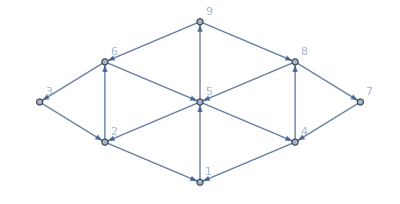

```mathematica
ClearAll[g];
g=Graph[{7->4,4->8,8->7,4->1,1->5,5->4,8->5,5->9,9->8,3->2,2->6,6->3,9->6,6->5,5->2,2->1},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];],5->Button[5,g=MutateGraph[g,5];],6->Button[6,g=MutateGraph[g,6];],7->Button[7,g=MutateGraph[g,7];],8->Button[8,g=MutateGraph[g,8];],9->Button[9,g=MutateGraph[g,9];]},GraphLayout->"HighDimensionalEmbedding"]
```

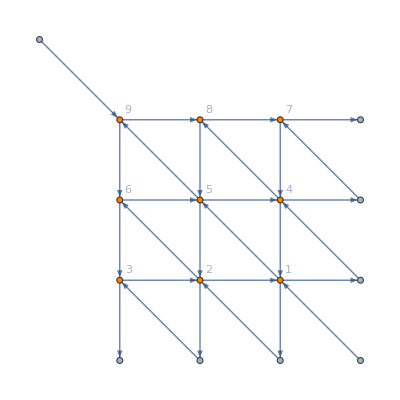

```mathematica
ClearAll[g];
g=Graph[{0->9,7->4,4->8,8->7,4->1,1->5,5->4,8->5,5->9,9->8,3->2,2->6,6->3,9->6,6->5,5->2,2->1,7->10,4->11,1->12,11->7,12->4,13->1,1->14,2->15,3->16,14->2,15->3},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];],5->Button[5,g=MutateGraph[g,5];],6->Button[6,g=MutateGraph[g,6];],7->Button[7,g=MutateGraph[g,7];],8->Button[8,g=MutateGraph[g,8];],9->Button[9,g=MutateGraph[g,9];]},VertexStyle->{1->Orange,2->Orange,3->Orange,4->Orange,5->Orange,6->Orange,7->Orange,8->Orange,9->Orange},VertexCoordinates->{0->{-1,1},9->{0,0},8->{1,0},7->{2,0},6->{0,-1},5->{1,-1},4->{2,-1},3->{0,-2},2->{1,-2},1->{2,-2},10->{3,0},11->{3,-1},12->{3,-2},13->{3,-3},14->{2,-3},15->{1,-3},16->{0,-3}},GraphLayout->"HighDimensionalEmbedding"]
```

```mathematica
Dynamic[g]
```

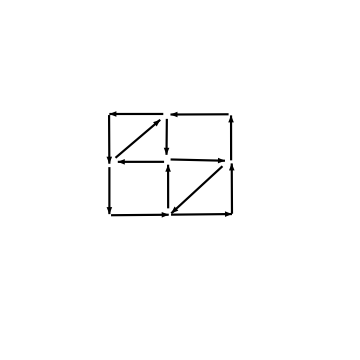

### E6

#### OPE parameterization

```mathematica
rewrite={a11->(ab[1,2,3,4] ab[1,5,6,7] ab[2,3,6,7])/(ab[1,2,3,7] ab[1,2,6,7] ab[3,4,5,6]),a21->(ab[1,2,3,4] ab[2,5,6,7])/(ab[1,2,6,7] ab[2,3,4,5]),a31->(ab[1,5,6,7] ab[2,3,4,7])/(ab[1,2,3,7] ab[4,5,6,7]),a41->(ab[2,4,5,7] ab[3,4,5,6])/(ab[2,3,4,5] ab[4,5,6,7]),a51->ab[1,cap1[{2,3},{4,5},{6,7}]]/(ab[1,2,3,4] ab[1,5,6,7]),a61->-ab[1,cap1[{2,7},{3,4},{5,6}]]/(ab[1,2,3,4] ab[1,5,6,7]),a12->(ab[1,2,6,7] ab[1,3,4,7] ab[2,3,4,5])/(ab[1,2,3,4] ab[1,2,3,7] ab[4,5,6,7]),a22->(ab[1,3,6,7] ab[2,3,4,5])/(ab[1,2,3,7] ab[3,4,5,6]),a32->(ab[1,2,6,7] ab[1,3,4,5])/(ab[1,2,3,4] ab[1,5,6,7]),a42->(ab[1,3,5,6] ab[4,5,6,7])/(ab[1,5,6,7] ab[3,4,5,6]),a52->ab[2,cap1[{1,7},{3,4},{5,6}]]/(ab[1,2,6,7] ab[2,3,4,5]),a62->-ab[2,cap1[{1,3},{4,5},{6,7}]]/(ab[1,2,6,7] ab[2,3,4,5]),a13->(ab[1,2,3,7] ab[1,2,4,5] ab[3,4,5,6])/(ab[1,2,3,4] ab[1,5,6,7] ab[2,3,4,5]),a23->(ab[1,2,4,7] ab[3,4,5,6])/(ab[1,2,3,4] ab[4,5,6,7]),a33->(ab[1,2,3,7] ab[2,4,5,6])/(ab[1,2,6,7] ab[2,3,4,5]),a43->(ab[1,5,6,7] ab[2,4,6,7])/(ab[1,2,6,7] ab[4,5,6,7]),a53->ab[3,cap1[{1,2},{4,5},{6,7}]]/(ab[1,2,3,7] ab[3,4,5,6]),a63->-ab[3,cap1[{1,7},{2,4},{5,6}]]/(ab[1,2,3,7] ab[3,4,5,6]),a14->(ab[1,2,3,4] ab[2,3,5,6] ab[4,5,6,7])/(ab[1,2,6,7] ab[2,3,4,5] ab[3,4,5,6]),a24->(ab[1,2,3,5] ab[4,5,6,7])/(ab[1,5,6,7] ab[2,3,4,5]),a34->(ab[1,2,3,4] ab[3,5,6,7])/(ab[1,2,3,7] ab[3,4,5,6]),a44->(ab[1,2,6,7] ab[1,3,5,7])/(ab[1,2,3,7] ab[1,5,6,7]),a54->ab[4,cap1[{1,7},{2,3},{5,6}]]/(ab[1,2,3,4] ab[4,5,6,7]),a64->-ab[4,cap1[{1,2},{3,5},{6,7}]]/(ab[1,2,3,4] ab[4,5,6,7]),a15->(ab[1,5,6,7] ab[2,3,4,5] ab[3,4,6,7])/(ab[1,2,3,7] ab[3,4,5,6] ab[4,5,6,7]),a25->(ab[1,5,6,7] ab[2,3,4,6])/(ab[1,2,6,7] ab[3,4,5,6]),a35->(ab[1,4,6,7] ab[2,3,4,5])/(ab[1,2,3,4] ab[4,5,6,7]),a45->(ab[1,2,3,7] ab[1,2,4,6])/(ab[1,2,3,4] ab[1,2,6,7]),a55->ab[5,cap1[{1,2},{3,4},{6,7}]]/(ab[1,5,6,7] ab[2,3,4,5]),a65->-ab[5,cap1[{1,7},{2,3},{4,6}]]/(ab[1,5,6,7] ab[2,3,4,5]),a16->(ab[1,2,6,7] ab[1,4,5,7] ab[3,4,5,6])/(ab[1,2,3,4] ab[1,5,6,7] ab[4,5,6,7]),a26->(ab[1,2,6,7] ab[3,4,5,7])/(ab[1,2,3,7] ab[4,5,6,7]),a36->(ab[1,2,5,7] ab[3,4,5,6])/(ab[1,5,6,7] ab[2,3,4,5]),a46->(ab[1,2,3,4] ab[2,3,5,7])/(ab[1,2,3,7] ab[2,3,4,5]),a56->ab[6,cap1[{1,7},{2,3},{4,5}]]/(ab[1,2,6,7] ab[3,4,5,6]),a66->-ab[6,cap1[{1,2},{3,4},{5,7}]]/(ab[1,2,6,7] ab[3,4,5,6]),a17->(ab[1,2,3,7] ab[1,2,5,6] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,5,6,7] ab[2,3,4,5]),a27->(ab[1,2,3,7] ab[1,4,5,6])/(ab[1,2,3,4] ab[1,5,6,7]),a37->(ab[1,2,3,6] ab[4,5,6,7])/(ab[1,2,6,7] ab[3,4,5,6]),a47->(ab[1,3,4,6] ab[2,3,4,5])/(ab[1,2,3,4] ab[3,4,5,6]),a57->ab[7,cap1[{1,2},{3,4},{5,6}]]/(ab[1,2,3,7] ab[4,5,6,7]),a67->-ab[7,cap1[{1,6},{2,3},{4,5}]]/(ab[1,2,3,7] ab[4,5,6,7])}//Sort;
```

```mathematica
ainf=(rewrite/.{ab[a_,cap1[{b_,c_},{d_,e_},{f_,g_}]]:>FB[a,BiTw[b,c],BiTw[d,e],BiTw[f,g]],ab[a__]:>FB[a]}//MTExpand)/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor;
```

```mathematica
(ab[1,cap1[{2,3},{4,5},{6,7}]]/.{ab[a_,cap1[{b_,c_},{d_,e_},{f_,g_}]]:>FB[a,BiTw[b,c],BiTw[d,e],BiTw[f,g]],ab[a__]:>FB[a]}//MTExpand)
```

-FB[1,2,3,7] FB[1,4,5,6]+FB[1,2,3,6] FB[1,4,5,7]

```mathematica
fdefE6={f[1]->-((ab[1,2,4,7] ab[3,4,5,6])/ab[4,cap1[{1,2},{3,5},{6,7}]]),f[2]->(ab[1,2,3,4] ab[1,2,6,7])/(ab[1,2,3,7] ab[1,2,4,6]),f[3]->-(ab[4,cap1[{1,2},{3,5},{6,7}]]/(ab[1,2,3,4] ab[4,5,6,7])),f[4]->(ab[5,cap1[{1,2},{3,4},{6,7}]] ab[1,2,4,6])/(ab[1,2,4,5] ab[1,2,6,7] ab[3,4,5,6]),f[5]->(ab[1,5,6,7] ab[2,3,4,5])/ab[5,cap1[{1,2},{3,4},{6,7}]],f[6]->-((ab[1,2,6,7] ab[1,3,4,5] ab[4,5,6,7])/(ab[4,cap1[{1,2},{3,5},{6,7}]] ab[1,5,6,7]))};
```

```mathematica
MatE6={{1,0,0,0},{(1+f[5])/f[5],1,0,0},{(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])/(f[1] f[2] f[3] f[4] f[5]),(1+f[2]+f[1] f[2]+f[6]+f[2] f[6]+f[1] f[2] f[6]+f[1] f[2] f[4] f[6]+f[1] f[2] f[3] f[4] f[6])/(f[1] f[2] f[3] f[4] f[6]),1,0},{(1+f[2]+f[1] f[2]+f[1] f[2] f[4])/(f[1] f[2] f[3] f[4] f[5]),((1+f[2]+f[1] f[2]+f[1] f[2] f[4]) (1+f[6]))/(f[1] f[2] f[3] f[4] f[6]),1+f[2]+f[1] f[2]+f[1] f[2] f[4],1},{0,1/(f[3] f[6]),f[2] (1+f[1]+f[1] f[4]),1},{0,0,(f[2] (1+f[2]+f[1] f[2]+f[1] f[2] f[4]))/(1+f[2]),1},{0,0,0,1}};
```

```mathematica
M1m={{S1/Sqrt[F1],0,0,0},{0,1/S1/Sqrt[F1],0,0},{0,0,Sqrt[F1]/T1,0},{0,0,0,T1*Sqrt[F1]}};
```

```mathematica
M2m={{1/S2/Sqrt[F2],0,0,-1/S2/Sqrt[F2]+Sqrt[F2]/T2},{0,S2/Sqrt[F2],0,0},{0,S2/Sqrt[F2]-T2*Sqrt[F2],Sqrt[F2]*T2,-Sqrt[F2]*T2+Sqrt[F2]/T2},{0,0,0,Sqrt[F2]/T2}};
```

```mathematica
MatE6n={{1,0,1,1}.M1m,{1,0,0,0},{-1,0,0,1},{-1,1,-1,3}.Inverse[M2m],{0,2,-1,1}.Inverse[M2m],{0,1,0,0},{0,1,1,0}.M1m}//Simplify;
```

```mathematica
MatE6n={{S1/(√F1),0,(√F1)/T1,√F1 T1},{1,0,0,0},{-1,0,0,1},{-√F2 S2,1/(√F2 T2),-1/(√F2 T2),(1+F2 S2 T2+T2^2)/(√F2 T2)},{0,(S2+F2 T2)/(√F2 S2 T2),-1/(√F2 T2),1/(√F2 T2)},{0,1,0,0},{0,1/(√F1 S1),(√F1)/T1,0}};
```

```mathematica
Table[(fdefE6[[i,2]]/.{ab[a_,cap1[{b_,c_},{d_,e_},{f_,g_}]]:>FB[a,BiTw[b,c],BiTw[d,e],BiTw[f,g]],ab[a__]:>FB[a]}//MTExpand)/.{FB[a__]:>fB[a,"explicitM"->MatE6n]}//Simplify,{i,1,6}]
```

{(S2 T1 T2 (1+F1 S1 T1+T1^2+F2 S2 T2+T2^2))/(F1 S1 (S2 T2 (1+T2^2)+F2^2 S2 T2 (1+T2^2)+F2 (1+(2+S2^2) T2^2+T2^4+T1^2 (1+T2^2)))),(F1 S1 T1)/(1+T1^2+F2 S2 T2+T2^2),(S2 T2 (1+T2^2)+F2^2 S2 T2 (1+T2^2)+F2 (1+(2+S2^2) T2^2+T2^4+T1^2 (1+T2^2)))/(F2 S2^2),((1+T1^2+F2 S2 T2+T2^2) (S2 T2+F2 (1+T1^2+T2^2)))/(T1^2 T2^2 (S2 T2+F2^2 S2 T2+F2 (1+S2^2+T1^2+T2^2))),(F2 S1 T1)/(F1 (S2 T2+F2 (1+T1^2+T2^2))),(F2 S2 T1 T2 (F2 S1 T1+F1 S2 T2+F1 F2 (1+T1^2+T2^2)))/(S1 (S2 T2 (1+T2^2)+F2^2 S2 T2 (1+T2^2)+F2 (1+(2+S2^2) T2^2+T2^4+T1^2 (1+T2^2))))}

```mathematica
(S2 T1 T2 (1+F1 S1 T1+T1^2+F2 S2 T2+T2^2))/(F1 S1 (S2 T2 (1+T2^2)+F2^2 S2 T2 (1+T2^2)+F2 (1+(2+S2^2) T2^2+T2^4+T1^2 (1+T2^2))))-(F2 S2 T1 T2 (F2 S1 T1+F1 S2 T2+F1 F2 (1+T1^2+T2^2)))/(S1 (S2 T2 (1+T2^2)+F2^2 S2 T2 (1+T2^2)+F2 (1+(2+S2^2) T2^2+T2^4+T1^2 (1+T2^2))))/.{F1->1,F2->1}//Factor
```

0

```mathematica
({(FB[7,1,2,3]*FB[3,4,5,6])/(FB[7,1,3,4]*FB[2,3,5,6]),(FB[1,2,3,4]*FB[7,1,4,5])/(FB[1,2,4,5]*FB[7,1,3,4]),(FB[2,3,4,5]*FB[1,2,5,6])/(FB[2,3,5,6]*FB[1,2,4,5])}//MTExpand)/.{FB[a__]:>fB[a,"explicitM"->MatE6n]}//Simplify
```

{(F1 T1^2)/(S1 T1+F1^2 S1 T1+F1 (1+S1^2+2 T1^2)),(S1^2 (2 F1 S1 T1+2 F1^3 S1 T1+T1^2+F1^4 T1^2+F1^2 (2+S1^2+2 T1^2)))/((S1 T1+F1^2 S1 T1+F1 (1+S1^2+2 T1^2))^2),(F1 (1+T1^2))/(S1 T1+F1^2 S1 T1+F1 (1+S1^2+2 T1^2))}

```mathematica
ainf=(rewrite/.{ab[a_,cap1[{b_,c_},{d_,e_},{f_,g_}]]:>FB[a,BiTw[b,c],BiTw[d,e],BiTw[f,g]],ab[a__]:>FB[a]}//MTExpand)/.{FB[a__]:>fB[a,"explicitM"->MatE6n]}//Factor;
```

```mathematica
ainfparity=ainf/.{F1->1/F1,F2->1/F2}//Factor;
```

```mathematica
ainfparity[[15;;21]]
```

{a31→(F2 S1 (S1+F1 T1))/(S2 T2),a32→(T1 T2 (1+F1 S1 T1+T1^2+F2 S2 T2+T2^2))/(F1 F2 S1 S2),a33→(F1 S2 (S2+F2 T2))/(S1 T1),a34→S1/(F1 T1 T2^2),a35→(T1 (F1 F2 S1+F1 S1 S2 T2+S2 T1 T2+F1 F2 S1 T2^2))/(F2 S2^2),a36→(T2 (F1 F2 S2+F2 S1 S2 T1+F1 F2 S2 T1^2+S1 T1 T2))/(F1 S1^2),a37→S2/(F2 T1^2 T2)}

```mathematica
Values[ainf]===Values[Join[Take[ainfparity,7],ainfparity[[15;;21]]//RotateRight,ainfparity[[8;;14]]//RotateLeft,ainfparity[[29;;35]],ainfparity[[22;;28]],Take[ainfparity,-7]]]
```

True

```mathematica
cyc={7->6,6->5,5->4,4->3,3->2,2->1,1->7};
```

```mathematica
ulist=Nest[ReplaceAll[#,cyc]&,{(FB[7,1,2,3]*FB[3,4,5,6])/(FB[7,1,3,4]*FB[2,3,5,6]),(FB[1,2,3,4]*FB[7,1,4,5])/(FB[1,2,4,5]*FB[7,1,3,4]),(FB[2,3,4,5]*FB[1,2,5,6])/(FB[2,3,5,6]*FB[1,2,4,5])},7]
vlist=Nest[ReplaceAll[#,cyc]&,{(FB[1,2,6,7]*FB[3,4,5,6])/(FB[1,2,5,6]*FB[3,4,6,7]),(FB[7,1,5,6]*FB[1,2,4,5])/(FB[7,1,4,5]*FB[1,2,5,6]),(FB[6,7,4,5]*FB[7,1,3,4])/(FB[6,7,3,4]*FB[4,5,7,1])},7]
```

{(FB[1,2,3,7] FB[3,4,5,6])/(FB[1,3,4,7] FB[2,3,5,6]),(FB[1,2,3,4] FB[1,4,5,7])/(FB[1,2,4,5] FB[1,3,4,7]),(FB[1,2,5,6] FB[2,3,4,5])/(FB[1,2,4,5] FB[2,3,5,6])}

{(FB[1,2,6,7] FB[3,4,5,6])/(FB[1,2,5,6] FB[3,4,6,7]),(FB[1,2,4,5] FB[1,5,6,7])/(FB[1,2,5,6] FB[1,4,5,7]),(FB[1,3,4,7] FB[4,5,6,7])/(FB[1,4,5,7] FB[3,4,6,7])}

```mathematica
ulist=ulist/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor;
vlist=vlist/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor;
```

```mathematica
solx=Solve[x/(1+x)==ulist[[2]],x][[1]]//Factor
```

{x→(1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6])/(f[1] f[3] f[4] f[6])}

```mathematica
soly=Solve[(y/(1+x)/.solx)==ulist[[1]]/ulist[[3]],y][[1]]//Factor
```

{y→1/(f[1] f[2] f[3] f[4] (1+f[4]) f[5] f[6])}

```mathematica
((ulistope[[3]]/.{T1->Sqrt[x],S1->Sqrt[y]}/.solx/.soly)==ulist[[3]])/.{F1->1}
```

1/(1+1/(f[1] f[2] f[3] f[4] (1+f[4]) f[5] f[6])+(1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6])/(f[1] f[3] f[4] f[6])+2 √(1/(f[1] f[2] f[3] f[4] (1+f[4]) f[5] f[6])) √((1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6])/(f[1] f[3] f[4] f[6])))==(f[1] f[2] f[3] f[4] (1+f[4]) f[5] f[6])/(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[5]+f[2] f[5]+f[1] f[2] f[5]+f[1] f[2] f[4] f[5]+f[5] f[6]+f[2] f[5] f[6]+f[1] f[2] f[5] f[6]+f[4] f[5] f[6]+f[2] f[4] f[5] f[6]+2 f[1] f[2] f[4] f[5] f[6]+f[1] f[2] f[3] f[4] f[5] f[6]+f[1] f[2] f[4]^2 f[5] f[6]+f[1] f[2] f[3] f[4]^2 f[5] f[6])

```mathematica
Solve[(ulistope[[3]]/.{T1->Sqrt[x],S1->Sqrt[y]}/.solx/.soly)==ulist[[3]],F1]//Simplify[#,Thread@Greater[f/@Range[6],0]]&
```

{{F1→(f[2]+f[1] f[2]+f[1] f[2] f[4]+f[5]-f[2] f[4] f[5]+f[5] f[6]+f[4] f[5] f[6]-√(f[2]^2 (1+f[1] (1+f[4])-f[4] f[5])^2+f[5]^2 (1+(1+f[4]) f[6])^2-2 f[2] f[5] (1+f[6]+f[4]^2 f[5] f[6]+f[1] (1+f[4]) (1+(1+f[4]) f[6])+f[4] (2+f[5]+f[6]+f[5] f[6]))))/(2 √(f[2] (1+f[4]) f[5] (1+f[1]+f[6]+f[1] (1+f[4]) f[6])))},{F1→(f[2]+f[1] f[2]+f[1] f[2] f[4]+f[5]-f[2] f[4] f[5]+f[5] f[6]+f[4] f[5] f[6]+√(f[2]^2 (1+f[1] (1+f[4])-f[4] f[5])^2+f[5]^2 (1+(1+f[4]) f[6])^2-2 f[2] f[5] (1+f[6]+f[4]^2 f[5] f[6]+f[1] (1+f[4]) (1+(1+f[4]) f[6])+f[4] (2+f[5]+f[6]+f[5] f[6]))))/(2 √(f[2] (1+f[4]) f[5] (1+f[1]+f[6]+f[1] (1+f[4]) f[6])))}}

```mathematica
(f[2]+f[1] f[2]+f[1] f[2] f[4]+f[5]-f[2] f[4] f[5]+f[5] f[6]+f[4] f[5] f[6]-√(f[2]^2 (1+f[1] (1+f[4])-f[4] f[5])^2+f[5]^2 (1+(1+f[4]) f[6])^2-2 f[2] f[5] (1+f[6]+f[4]^2 f[5] f[6]+f[1] (1+f[4]) (1+(1+f[4]) f[6])+f[4] (2+f[5]+f[6]+f[5] f[6]))))/(2 √(f[2] (1+f[4]) f[5] (1+f[1]+f[6]+f[1] (1+f[4]) f[6])))*(f[2]+f[1] f[2]+f[1] f[2] f[4]+f[5]-f[2] f[4] f[5]+f[5] f[6]+f[4] f[5] f[6]+√(f[2]^2 (1+f[1] (1+f[4])-f[4] f[5])^2+f[5]^2 (1+(1+f[4]) f[6])^2-2 f[2] f[5] (1+f[6]+f[4]^2 f[5] f[6]+f[1] (1+f[4]) (1+(1+f[4]) f[6])+f[4] (2+f[5]+f[6]+f[5] f[6]))))/(2 √(f[2] (1+f[4]) f[5] (1+f[1]+f[6]+f[1] (1+f[4]) f[6])))//Simplify
```

1

```mathematica
%[[1]]/.{f[6]->f[1],f[5]->f[2]}//Simplify[#,Thread@Greater[f/@Range[6],0]]&
```

{F1→-(-2+f[2] f[4]-2 f[1] (1+f[4])+√(f[4] (-4+f[2]^2 f[4]-4 f[2] (1+f[1]+f[1] f[4]))))/(2 √((1+f[4]) (1+2 f[1]+f[1]^2 (1+f[4]))))}

```mathematica
solx=Solve[x/(1+x)==vlist[[2]],x][[1]]//Factor
```

{x→f[4]/((1+f[1]+f[1] f[4]) (1+f[6]+f[4] f[6]))}

```mathematica
soly=Solve[(y/(1+x)/.solx)==vlist[[1]]/vlist[[3]],y][[1]]//Factor
```

{y→(f[3] (1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6])^2)/((1+f[1]+f[1] f[4]) (1+f[6]+f[4] f[6]) (1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6]+f[1] f[3] f[4] f[6]))}

```mathematica
Solve[(vlistope[[3]]/.{T2->Sqrt[x],S2->Sqrt[y]}/.solx/.soly)==vlist[[3]],F2]//Simplify[#,Thread@Greater[f/@Range[6],0]]&
```

{{F2→(f[4] (-1+f[1] f[3]+f[3] f[6])-√(f[4] (f[4]+f[3]^2 f[4] (f[1]-f[6])^2-2 f[3] (2+(2+f[4]) f[6]+f[1] (2+f[4]+2 f[6]+2 f[4] f[6])))))/(2 √(f[3] f[4] (1+f[1]+f[6]+f[1] (1+(1+f[3]) f[4]) f[6])))},{F2→(f[4] (-1+f[1] f[3]+f[3] f[6])+√(f[4] (f[4]+f[3]^2 f[4] (f[1]-f[6])^2-2 f[3] (2+(2+f[4]) f[6]+f[1] (2+f[4]+2 f[6]+2 f[4] f[6])))))/(2 √(f[3] f[4] (1+f[1]+f[6]+f[1] (1+(1+f[3]) f[4]) f[6])))}}

```mathematica
%[[1]]/.{f[6]->f[1],f[5]->f[2]}//Simplify[#,Thread@Greater[f/@Range[6],0]]&
```

```mathematica
ulist=Nest[ReplaceAll[#,cyc]&,{(FB[7,1,2,3]*FB[3,4,5,6])/(FB[7,1,3,4]*FB[2,3,5,6]),(FB[1,2,3,4]*FB[7,1,4,5])/(FB[1,2,4,5]*FB[7,1,3,4]),(FB[2,3,4,5]*FB[1,2,5,6])/(FB[2,3,5,6]*FB[1,2,4,5])},4]
vlist=Nest[ReplaceAll[#,cyc]&,{(FB[1,2,6,7]*FB[3,4,5,6])/(FB[1,2,5,6]*FB[3,4,6,7]),(FB[7,1,5,6]*FB[1,2,4,5])/(FB[7,1,4,5]*FB[1,2,5,6]),(FB[6,7,4,5]*FB[7,1,3,4])/(FB[6,7,3,4]*FB[4,5,7,1])},4]
```

{(FB[1,2,6,7] FB[3,4,5,6])/(FB[1,2,5,6] FB[3,4,6,7]),(FB[1,3,4,7] FB[4,5,6,7])/(FB[1,4,5,7] FB[3,4,6,7]),(FB[1,2,4,5] FB[1,5,6,7])/(FB[1,2,5,6] FB[1,4,5,7])}

{(FB[1,2,6,7] FB[2,3,4,5])/(FB[1,2,4,5] FB[2,3,6,7]),(FB[1,2,3,4] FB[1,4,5,7])/(FB[1,2,4,5] FB[1,3,4,7]),(FB[1,2,3,7] FB[3,4,6,7])/(FB[1,3,4,7] FB[2,3,6,7])}

```mathematica
ulist=ulist/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor;
vlist=vlist/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor;
```

```mathematica
solx=Solve[x/(1+x)==ulist[[2]],x][[1]]//Factor
```

{x→(1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6]+f[1] f[3] f[4] f[6])/((1+f[1]) f[3] (1+f[6]))}

```mathematica
1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6]+f[1] f[3] f[4] f[6]/.{f[6]->f[1],f[5]->f[2]}//Factor
```

1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]

```mathematica
soly=Solve[(y/(1+x)/.solx)==ulist[[1]]/ulist[[3]],y][[1]]//Factor
```

{y→(1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6])^2/((1+f[1]) f[4] (1+f[6]))}

```mathematica
Solve[(ulistope[[3]]/.{T1->Sqrt[x],S1->Sqrt[y]}/.solx/.soly)==ulist[[3]],F1]//Simplify[#,Thread@Greater[f/@Range[6],0]]&
```

{{F1→(-1+f[1] f[3]+f[3] f[6]+√(1+f[3]^2 (f[1]-f[6])^2-(2 f[3] (2+(2+f[4]) f[6]+f[1] (2+f[4]+2 f[6]+2 f[4] f[6])))/f[4]))/(2 √((f[3] (1+f[1]+f[6]+f[1] (1+(1+f[3]) f[4]) f[6]))/f[4]))},{F1→(-1+f[1] f[3]+f[3] f[6]-√(1+f[3]^2 (f[1]-f[6])^2-(2 f[3] (2+(2+f[4]) f[6]+f[1] (2+f[4]+2 f[6]+2 f[4] f[6])))/f[4]))/(2 √((f[3] (1+f[1]+f[6]+f[1] (1+(1+f[3]) f[4]) f[6]))/f[4]))}}

```mathematica
%[[1]]/.{f[6]->f[1],f[5]->f[2]}//Simplify[#,Thread@Greater[f/@Range[6],0]]&
```

{F1→(-1+2 f[1] f[3]+√(1-(4 (1+f[1]) f[3] (1+f[1] (1+f[4])))/f[4]))/(2 √((f[3] (1+2 f[1]+f[1]^2 (1+(1+f[3]) f[4])))/f[4]))}

```mathematica
solx=Solve[x/(1+x)==vlist[[2]],x][[1]]//Factor
```

{x→(1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6])/(f[1] f[3] f[4] f[6])}

```mathematica
soly=Solve[(y/(1+x)/.solx)==vlist[[1]]/vlist[[3]],y][[1]]//Factor
```

{y→(f[2] f[5] (1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6]+f[1] f[3] f[4] f[6])^2)/(f[1] (1+f[3]) f[4] f[6])}

```mathematica
Solve[(vlistope[[3]]/.{T2->Sqrt[x],S2->Sqrt[y]}/.solx/.soly)==vlist[[3]],F2]//Simplify[#,Thread@Greater[f/@Range[6],0]]&
```

{{F2→(-1+f[2] f[3]+f[1] f[2] f[3]+f[3] f[5]+f[3] f[5] f[6]+√((1+f[1])^2 f[2]^2 f[3]^2+(-1+f[3] f[5] (1+f[6]))^2-2 f[2] f[3] (1+f[1]+(2+f[3]) f[5] (1+f[6])+f[1] f[5] (2+2 (1+f[4]) f[6]+f[3] (1+f[6]+2 f[4] f[6])))))/(2 √(f[2] f[3] (1+f[3]) f[5] (1+f[1]+f[6]+f[1] (1+f[4]) f[6])))},{F2→(-1+f[2] f[3]+f[1] f[2] f[3]+f[3] f[5]+f[3] f[5] f[6]-√((1+f[1])^2 f[2]^2 f[3]^2+(-1+f[3] f[5] (1+f[6]))^2-2 f[2] f[3] (1+f[1]+(2+f[3]) f[5] (1+f[6])+f[1] f[5] (2+2 (1+f[4]) f[6]+f[3] (1+f[6]+2 f[4] f[6])))))/(2 √(f[2] f[3] (1+f[3]) f[5] (1+f[1]+f[6]+f[1] (1+f[4]) f[6])))}}

```mathematica
%[[1]]/.{f[6]->f[1],f[5]->f[2]}//Simplify[#,Thread@Greater[f/@Range[6],0]]&
```

{F2→(-1+2 (1+f[1]) f[2] f[3]+√(1-4 (1+f[1]) f[2] f[3]-4 f[2]^2 f[3] (1+2 f[1]+f[1]^2 (1+f[4]+f[3] f[4]))))/(2 f[2] √(f[3] (1+f[3]) (1+2 f[1]+f[1]^2 (1+f[4]))))}

```mathematica
ulist={(FB[7,1,2,3]*FB[3,4,5,6])/(FB[7,1,3,4]*FB[2,3,5,6]),(FB[1,2,3,4]*FB[7,1,4,5])/(FB[1,2,4,5]*FB[7,1,3,4]),(FB[2,3,4,5]*FB[1,2,5,6])/(FB[2,3,5,6]*FB[1,2,4,5])}/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor
```

{(f[1] f[3] f[4] f[6])/((1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6]+f[1] f[3] f[4] f[6]) (1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[5]+f[2] f[5]+f[1] f[2] f[5]+f[1] f[2] f[4] f[5]+f[5] f[6]+f[2] f[5] f[6]+f[1] f[2] f[5] f[6]+f[4] f[5] f[6]+f[2] f[4] f[5] f[6]+2 f[1] f[2] f[4] f[5] f[6]+f[1] f[2] f[3] f[4] f[5] f[6]+f[1] f[2] f[4]^2 f[5] f[6]+f[1] f[2] f[3] f[4]^2 f[5] f[6])),(1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6])/(1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6]+f[1] f[3] f[4] f[6]),(f[1] f[2] f[3] f[4] (1+f[4]) f[5] f[6])/(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[5]+f[2] f[5]+f[1] f[2] f[5]+f[1] f[2] f[4] f[5]+f[5] f[6]+f[2] f[5] f[6]+f[1] f[2] f[5] f[6]+f[4] f[5] f[6]+f[2] f[4] f[5] f[6]+2 f[1] f[2] f[4] f[5] f[6]+f[1] f[2] f[3] f[4] f[5] f[6]+f[1] f[2] f[4]^2 f[5] f[6]+f[1] f[2] f[3] f[4]^2 f[5] f[6])}

```mathematica
sol=Solve[Join[Thread@Equal[ulist,{u1,u2,u3}],Thread@Equal[vlist,{v1,v2,v3}]],f/@Range[6]];
```

```mathematica
(Cases[sol,Power[_,1/2],Infinity]//DeleteDuplicates)[[2]]/.Thread@Rule[{u1,u2,u3},ulistope]/.Thread@Rule[{v1,v2,v3},vlistope]/.{F1->1,F2->1}//Simplify[#,Assumptions->{S1>0,T1>0,S2>2,T2>0}]&
```

$Aborted

```mathematica
sol1={T1->Sqrt[(1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6])/(f[1] f[3] f[4] f[6])],S1->Sqrt[1/(f[1] f[2] f[3] f[4] (1+f[4]) f[5] f[6])],F1->(f[2]+f[1] f[2]+f[1] f[2] f[4]+f[5]-f[2] f[4] f[5]+f[5] f[6]+f[4] f[5] f[6]-√(f[2]^2 (1+f[1] (1+f[4])-f[4] f[5])^2+f[5]^2 (1+(1+f[4]) f[6])^2-2 f[2] f[5] (1+f[6]+f[4]^2 f[5] f[6]+f[1] (1+f[4]) (1+(1+f[4]) f[6])+f[4] (2+f[5]+f[6]+f[5] f[6]))))/(2 √(f[2] (1+f[4]) f[5] (1+f[1]+f[6]+f[1] (1+f[4]) f[6])))};
```

```mathematica
{(F1 S1^2)/((1+T1^2) (F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2)),T1^2/(1+T1^2),F1/(F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2)}/.sol1//Simplify[#,Thread@Greater[f/@Range[6],0]]&
```

{(f[1] f[3] f[4] f[6])/((1+f[1]+f[6]+f[1] (1+(1+f[3]) f[4]) f[6]) (1+f[5] (1+(1+f[4]) f[6])+f[2] (1+f[5]+f[5] f[6]+f[4] f[5] f[6]+f[1] (1+f[4]) (1+f[5]+(1+(1+f[3]) f[4]) f[5] f[6])))),(1+f[1]+f[6]+f[1] (1+f[4]) f[6])/(1+f[1]+f[6]+f[1] (1+(1+f[3]) f[4]) f[6]),(f[1] f[2] f[3] f[4] (1+f[4]) f[5] f[6])/(1+f[5] (1+(1+f[4]) f[6])+f[2] (1+f[5]+f[5] f[6]+f[4] f[5] f[6]+f[1] (1+f[4]) (1+f[5]+(1+(1+f[3]) f[4]) f[5] f[6])))}

```mathematica
ulistope={S1^2/(1+T1^2)/(1+(T1+S1*F1)(T1+S1/F1)),1/(1+1/T1^2),1/(1+(T1+S1*F1)(T1+S1/F1))}//Factor
```

{(F1 S1^2)/((1+T1^2) (F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2)),T1^2/(1+T1^2),F1/(F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2)}

```mathematica
vlist={(FB[1,2,6,7]*FB[3,4,5,6])/(FB[1,2,5,6]*FB[3,4,6,7]),(FB[7,1,5,6]*FB[1,2,4,5])/(FB[7,1,4,5]*FB[1,2,5,6]),(FB[6,7,4,5]*FB[7,1,3,4])/(FB[6,7,3,4]*FB[4,5,7,1])}/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor
```

{f[3]/((1+f[3]) (1+f[4])),f[4]/((1+f[4]) (1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6])),(1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6]+f[1] f[3] f[4] f[6])/((1+f[3]) (1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6]))}

```mathematica
vlistope={S1^2/(1+T1^2)/(1+(T1+S1*F1)(T1+S1/F1)),1/(1+1/T1^2),1/(1+(T1+S1*F1)(T1+S1/F1))}/.{S1->S2,T1->T2,F1->F2}//Factor
```

{(F2 S2^2)/((1+T2^2) (F2+F2 S2^2+S2 T2+F2^2 S2 T2+F2 T2^2)),T2^2/(1+T2^2),F2/(F2+F2 S2^2+S2 T2+F2^2 S2 T2+F2 T2^2)}

```mathematica
sol2={T2->Sqrt[f[4]/((1+f[1]+f[1] f[4]) (1+f[6]+f[4] f[6]))],S2->Sqrt[(f[3] (1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6])^2)/((1+f[1]+f[1] f[4]) (1+f[6]+f[4] f[6]) (1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6]+f[1] f[3] f[4] f[6]))],F2->(f[4] (-1+f[1] f[3]+f[3] f[6])-√(f[4] (f[4]+f[3]^2 f[4] (f[1]-f[6])^2-2 f[3] (2+(2+f[4]) f[6]+f[1] (2+f[4]+2 f[6]+2 f[4] f[6])))))/(2 √(f[3] f[4] (1+f[1]+f[6]+f[1] (1+(1+f[3]) f[4]) f[6])))};
```

```mathematica
Join[sol1,sol2]
```

{T1→√((1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6])/(f[1] f[3] f[4] f[6])),S1→√(1/(f[1] f[2] f[3] f[4] (1+f[4]) f[5] f[6])),F1→(f[2]+f[1] f[2]+f[1] f[2] f[4]+f[5]-f[2] f[4] f[5]+f[5] f[6]+f[4] f[5] f[6]-√(f[2]^2 (1+f[1] (1+f[4])-f[4] f[5])^2+f[5]^2 (1+(1+f[4]) f[6])^2-2 f[2] f[5] (1+f[6]+f[4]^2 f[5] f[6]+f[1] (1+f[4]) (1+(1+f[4]) f[6])+f[4] (2+f[5]+f[6]+f[5] f[6]))))/(2 √(f[2] (1+f[4]) f[5] (1+f[1]+f[6]+f[1] (1+f[4]) f[6]))),T2→√(f[4]/((1+f[1]+f[1] f[4]) (1+f[6]+f[4] f[6]))),S2→√((f[3] (1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6])^2)/((1+f[1]+f[1] f[4]) (1+f[6]+f[4] f[6]) (1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6]+f[1] f[3] f[4] f[6]))),F2→(f[4] (-1+f[1] f[3]+f[3] f[6])-√(f[4] (f[4]+f[3]^2 f[4] (f[1]-f[6])^2-2 f[3] (2+(2+f[4]) f[6]+f[1] (2+f[4]+2 f[6]+2 f[4] f[6])))))/(2 √(f[3] f[4] (1+f[1]+f[6]+f[1] (1+(1+f[3]) f[4]) f[6])))}

```mathematica
asdopemap=Import["/Users/windfolgen/Downloads/2207.11815/anc/letter_map_R72.txt","Text"]//ToExpression;
```

```mathematica
(asdopemap//Keys)
```

{S1,S2,T1,S1+T1,1+T1^2,1+S1 T1+T1^2,1+S1^2+2 S1 T1+T1^2,T2,S2+T2,S1 S2+S2 T1+S1 T2,S2+S1 S2 T1+S2 T1^2+S1 T1 T2,S2+S1^2 S2+2 S1 S2 T1+S2 T1^2+S1^2 T2+S1 T1 T2,1+T2^2,1+T1^2+T2^2,1+S1 T1+T1^2+T2^2,1+S1^2+2 S1 T1+T1^2+T2^2,1+S2 T2+T2^2,1+T1^2+S2 T2+T2^2,1+S1 T1+T1^2+S2 T2+T2^2,1+S2^2+2 S2 T2+T2^2,1+S2^2+T1^2+2 S2 T2+T2^2,S1+S1 S2 T2+S2 T1 T2+S1 T2^2,S1+S1 S2^2+S2^2 T1+2 S1 S2 T2+S2 T1 T2+S1 T2^2,S1^2+S1^2 S2^2+2 S1 S2^2 T1+S2^2 T1^2+2 S1^2 S2 T2+2 S1 S2 T1 T2+S1^2 T2^2,S2^2+S1^2 S2^2+2 S1 S2^2 T1+S2^2 T1^2+2 S1^2 S2 T2+2 S1 S2 T1 T2+S1^2 T2^2,S1^2+S2^2+S1^2 S2^2+2 S1 S2^2 T1+S2^2 T1^2+2 S1^2 S2 T2+2 S1 S2 T1 T2+S1^2 T2^2,1+2 S1 T1+2 T1^2+S1^2 T1^2+2 S1 T1^3+T1^4+T2^2+T1^2 T2^2,1+T1^2+2 S2 T2+2 T2^2+S2^2 T2^2+T1^2 T2^2+2 S2 T2^3+T2^4}

#### mutate 1642

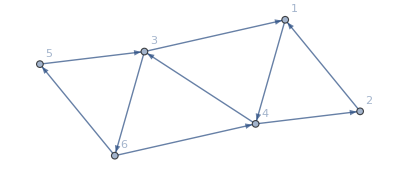

```mathematica
ClearAll[g];
g=Graph[{2->1,1->4,4->2,4->3,3->1,5->3,3->6,6->5,6->4},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];],5->Button[5,g=MutateGraph[g,5];],6->Button[6,g=MutateGraph[g,6];]},VertexCoordinates->{{2.632270101299922,0.3659725975716903},{2.016435883889035,1.121405098814431},{1.7732239568678387,0.26235895438234447},{0.8590461444320836,0.85904614443208},{0.,0.7554325012427503},{0.6158342174108874,0.}},GraphLayout->"HighDimensionalEmbedding"]
```

```mathematica
g0=Graph[{2->1,1->4,4->2,4->3,3->1,5->3,3->6,6->5,6->4}];
```

```mathematica
Dynamic[g]
```

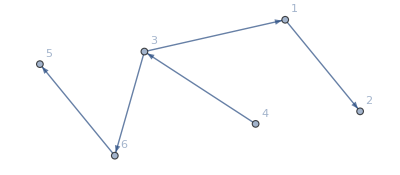

```mathematica
fdefE6={f[1]->-((ab[1,2,4,7] ab[3,4,5,6])/ab[4,cap1[{1,2},{3,5},{6,7}]]),f[2]->(ab[1,2,3,4] ab[1,2,6,7])/(ab[1,2,3,7] ab[1,2,4,6]),f[3]->-(ab[4,cap1[{1,2},{3,5},{6,7}]]/(ab[1,2,3,4] ab[4,5,6,7])),f[4]->(ab[5,cap1[{1,2},{3,4},{6,7}]] ab[1,2,4,6])/(ab[1,2,4,5] ab[1,2,6,7] ab[3,4,5,6]),f[5]->(ab[1,5,6,7] ab[2,3,4,5])/ab[5,cap1[{1,2},{3,4},{6,7}]],f[6]->-((ab[1,2,6,7] ab[1,3,4,5] ab[4,5,6,7])/(ab[4,cap1[{1,2},{3,5},{6,7}]] ab[1,5,6,7]))};
MatE6={{1,0,0,0},{(1+f[5])/f[5],1,0,0},{(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])/(f[1] f[2] f[3] f[4] f[5]),(1+f[2]+f[1] f[2]+f[6]+f[2] f[6]+f[1] f[2] f[6]+f[1] f[2] f[4] f[6]+f[1] f[2] f[3] f[4] f[6])/(f[1] f[2] f[3] f[4] f[6]),1,0},{(1+f[2]+f[1] f[2]+f[1] f[2] f[4])/(f[1] f[2] f[3] f[4] f[5]),((1+f[2]+f[1] f[2]+f[1] f[2] f[4]) (1+f[6]))/(f[1] f[2] f[3] f[4] f[6]),1+f[2]+f[1] f[2]+f[1] f[2] f[4],1},{0,1/(f[3] f[6]),f[2] (1+f[1]+f[1] f[4]),1},{0,0,(f[2] (1+f[2]+f[1] f[2]+f[1] f[2] f[4]))/(1+f[2]),1},{0,0,0,1}};
```

```mathematica
MatE6[[5]]
```

{0,1/(f[3] f[6]),f[2] (1+f[1]+f[1] f[4]),1}

```mathematica
TeXForm[MatE6[[7]]/.{f[i_]:>Subscript[f,i]}]
```

\{0,0,0,1\}

```mathematica
FB[1,2,3,6]*FB[1,2,4,5]/FB[1,2,3,4]/FB[1,2,5,6]/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor
```

(1+f[2])/(f[1] f[2] (1+f[4]))

```mathematica
FB[1,2,3,7]*FB[1,2,5,6]/FB[1,2,3,5]/FB[1,2,6,7]/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor
```

(f[1] (1+f[4]))/(1+f[2]+f[1] f[2]+f[1] f[2] f[4])

So the quiver starts from the foldable one

```mathematica
Bm=MatFromQuiver[g0]
```

{{0,-1,-1,1,0,0},{1,0,0,-1,0,0},{1,0,0,-1,-1,1},{-1,1,1,0,0,-1},{0,0,1,0,0,-1},{0,0,-1,1,1,0}}

```mathematica
yv={f[1],f[2],f[3],f[4],f[5],f[6]};
```

```mathematica
ml={1,6,4,2};
tem=Reap[
temp={Bm,yv};
Sow[temp];
Do[
temp=MutateY[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

```mathematica
yv=f/@Range[6];
```

```mathematica
(*folding condition, checked!*)
```

```mathematica
Solve[{tem[[-1,2,1]]==tem[[-1,2,6]],tem[[-1,2,2]]==tem[[-1,2,5]]}]//Factor
```

{{f[1]→-((1+f[2]) f[6])/(-1+f[2] f[6]),f[5]→-(-1+f[2] f[6])/(f[2] f[6])},{f[1]→-(-1-f[6]+f[2] f[5] f[6])/(f[2] f[5] f[6]),f[4]→0}}

```mathematica
Bmn={{0,-1,0,1,0,0},{1,0,0,0,0,0},{0,0,0,-1,0,0},{-1,0,1,0,0,-1},{0,0,0,0,0,1},{0,0,0,1,-1,0}};
yv=f/@Range[6];
```

```mathematica
ml={2,4,6,1};
temtest=Reap[
temp={Bmn,yv};
Sow[temp];
Do[
temp=MutateY[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];(*this get back to the initial quiver of the net of G(4,7)*)
```

```mathematica
temtest[[-1]]
```

{{{0,-1,-1,1,0,0},{1,0,0,-1,0,0},{1,0,0,-1,-1,1},{-1,1,1,0,0,-1},{0,0,1,0,0,-1},{0,0,-1,1,1,0}},{(1+f[2])/(f[1] f[2] (1+f[4])),(f[1] (1+f[4]))/(1+f[2]+f[1] f[2]+f[1] f[2] f[4]),(f[1] f[2] f[3] f[4] (1+f[4]) f[6])/((1+f[2]+f[1] f[2]+f[1] f[2] f[4]) (1+f[6]+f[4] f[6])),((1+f[2]+f[1] f[2]+f[1] f[2] f[4]) (1+f[6]+f[4] f[6]))/((1+f[2]) f[4]),f[5] (1+f[6]+f[4] f[6]),1/((1+f[4]) f[6])}}

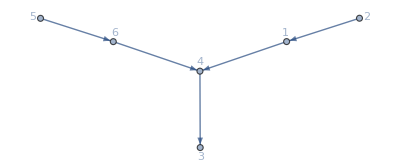

```mathematica
Graph[List[2,1,4,3,5,6],List[DirectedEdge[5,6],DirectedEdge[4,3],DirectedEdge[1,4],DirectedEdge[6,4],DirectedEdge[2,1]],List[Rule[FormatType,TraditionalForm],GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]]
```

```mathematica
rep=Thread@Rule[f/@Range[6],{((1+f[2]+f[1] f[2]) f[4] f[6])/(1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6]),1/((1+f[1]) f[2]),f[3] (1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6]),((1+f[1]) (1+f[6]))/(f[1] f[4] f[6]),(f[5] f[6])/(1+f[6]),(f[1] f[4])/(1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6])}];(*the relation between the new set of f variables and the f variables of the initial net quiver*)
```

```mathematica
Table[{3,4,1,6,2,5},{i,1,12}]//Flatten
```

{3,4,1,6,2,5,3,4,1,6,2,5,3,4,1,6,2,5,3,4,1,6,2,5,3,4,1,6,2,5,3,4,1,6,2,5,3,4,1,6,2,5,3,4,1,6,2,5,3,4,1,6,2,5,3,4,1,6,2,5,3,4,1,6,2,5,3,4,1,6,2,5}

```mathematica
ml=Table[{3,4,1,6,2,5},{i,1,12}]//Flatten;
tem=Reap[
temp={Bmn,yv};
Sow[temp];
Do[
temp=MutateY[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

```mathematica
Table[{2,3,5,7}+6*(i-1),{i,1,12}]//Flatten
%//Length
```

{2,3,5,7,8,9,11,13,14,15,17,19,20,21,23,25,26,27,29,31,32,33,35,37,38,39,41,43,44,45,47,49,50,51,53,55,56,57,59,61,62,63,65,67,68,69,71,73}

48

```mathematica
alpexp=;
```

```mathematica
alpexp[[8;;14]]
```

{(f_2^2 (1+f_1+f_2+2 f_1 f_2+f_1^2 f_2+f_1^2 f_2 f_4+f_1^2 f_2 f_3 f_4)^2)/f_1^2,f_1^2 f_3^2,(1+f_2+f_1 f_2+f_1 f_2 f_4)^2/(f_1^2 f_2^4 f_3^2 f_4^2),(1+f_2+f_1 f_2+f_1 f_2 f_4+f_1 f_2 f_3 f_4)^2/(f_1^2 f_3^2),(1+f_1)^2 f_2^2 f_3^2,(1+f_1+f_1 f_4)^2/(f_2^2 f_4^2),(1+f_2)^2/(f_1^2 f_2^2 f_3^2)}

```mathematica
1+2 Subscript[f, 1]+Subscript[f, 1]^2+Subscript[f, 1]^2 Subscript[f, 4]/.{Subscript[f, i_]:>f[i]}
```

1+2 f[1]+f[1]^2+f[1]^2 f[4]

```mathematica
Position[temp14sim,1+f[4]]
```

{{5,3},{6,2,1},{7,4,1}}

```mathematica
temp125sim//Length
```

7

The last entry can be derived in the following way!

```mathematica
temp116simt[[11]]*temp13sim[[6]]^2
```

(1+f[1])^2 f[2]^2 f[3]^2

```mathematica
temp116simt[[12]]/temp13sim[[7]]^2
```

(1+f[1])^2 f[2]^2 f[3]^2

```mathematica
temp116simt[[3]]*temp13sim[[2]]^2
```

(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])^2/(f[1]^2 f[3]^2)

```mathematica
temp116simt[[4]]/temp13sim[[3]]^2
```

(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])^2/(f[1]^2 f[3]^2)

```mathematica
temp116simt[[7]]*temp13sim[[4]]^2
```

(f[2]^2 (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4])^2)/f[1]^2

```mathematica
temp116simt[[8]]/temp13sim[[5]]^2
```

(f[2]^2 (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4])^2)/f[1]^2

```mathematica
temp116simt[[9]]*temp13sim[[5]]^2
```

(1+f[2]+f[1] f[2]+f[1] f[2] f[4])^2/(f[1]^2 f[2]^4 f[3]^2 f[4]^2)

```mathematica
temp116simt[[10]]/temp13sim[[6]]^2
```

(1+f[2]+f[1] f[2]+f[1] f[2] f[4])^2/(f[1]^2 f[2]^4 f[3]^2 f[4]^2)

```mathematica
temp116simt[[1]]/temp13sim[[1]]^2
```

f[1]^2 f[3]^2

```mathematica
temp116simt[[2]]/temp13sim[[2]]^2
```

f[1]^2 f[3]^2

```mathematica
temp116simt[[5]]*temp13sim[[3]]^2
```

(1+f[1]+f[1] f[4])^2/(f[2]^2 f[4]^2)

```mathematica
temp116simt[[6]]/temp13sim[[4]]^2
```

(1+f[1]+f[1] f[4])^2/(f[2]^2 f[4]^2)

```mathematica
temp116simt[[13]]*temp13sim[[7]]^2
```

(1+f[2])^2/(f[1]^2 f[2]^2 f[3]^2)

```mathematica
temp116simt[[14]]*temp13sim[[1]]^2
```

(1+f[2])^2/(f[1]^2 f[2]^2 f[3]^2)

```mathematica
alpexp[[1;;7]]
```

{(1+2 f_2+2 f_1 f_2+f_2^2+2 f_1 f_2^2+f_1^2 f_2^2+f_1^2 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4)/(f_1^2 f_3),f_2^2 f_3 (1+2 f_1+f_1^2+f_1^2 f_4+f_1^2 f_3 f_4),1/(f_2^2 f_4),(1+2 f_2+2 f_1 f_2+f_2^2+2 f_1 f_2^2+f_1^2 f_2^2+2 f_1 f_2 f_4+2 f_1 f_2^2 f_4+2 f_1^2 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4+f_1^2 f_2^2 f_4^2+f_1^2 f_2^2 f_3 f_4^2)/(f_1^2 f_2^2 f_3^2 f_4),f_2^2 (1+f_3) f_4,(f_3 (1+2 f_1+f_1^2+f_1^2 f_4))/f_4,(1+f_4)/(f_2^2 f_3 f_4)}

Now we derive the first entry in a similar way

```mathematica
Position[temp14sim,1+f[4]]
```

{{3,3},{4,4,1}}

```mathematica
temp14sim[[1]]*temp125simt[[1]]
```

f[2]^2 (1+f[3]) f[4]

```mathematica
temp14sim[[2]]/temp125simt[[2]]
```

1/(f[2]^2 (1+f[3]) f[4])

```mathematica
temp14sim[[3]]/temp125simt[[2]]
```

(1+f[4])/(f[2]^2 f[3] f[4])

```mathematica
temp14sim[[4]]/temp125simt[[3]]
```

(f[2]^2 f[3] f[4])/(1+f[4])

```mathematica
temp14sim[[5]]/temp125simt[[3]]
```

f[2]^2 f[3] (1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4])

```mathematica
temp14sim[[6]]/temp125simt[[4]]
```

1/(f[2]^2 f[3] (1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]))

```mathematica
temp14sim[[7]]/temp125simt[[4]]
```

1/(f[1]^2 f[2]^2 f[3]^2 f[4])(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)

```mathematica
temp14sim[[8]]/temp125simt[[5]]
```

(f[1]^2 f[2]^2 f[3]^2 f[4])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)

```mathematica
temp14sim[[9]]/temp125simt[[5]]
```

(f[3] (1+2 f[1]+f[1]^2+f[1]^2 f[4]))/f[4]

```mathematica
temp14sim[[10]]/temp125simt[[6]]
```

f[4]/(f[3] (1+2 f[1]+f[1]^2+f[1]^2 f[4]))

```mathematica
temp14sim[[11]]/temp125simt[[6]]
```

(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])/(f[1]^2 f[3])

```mathematica
temp14sim[[12]]/temp125simt[[7]]
```

(f[1]^2 f[3])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])

```mathematica
temp14sim[[13]]/temp125simt[[7]]
```

1/(f[2]^2 f[4])

```mathematica
temp14sim[[14]]*temp125simt[[1]]
```

f[2]^2 f[4]

```mathematica
temp1=tem[[{2,3,5,7,8,9,11,13,14,15,17,19,20,21,23,25,26,27,29,31,32,33,35,37,38,39,41,43,44,45,47,49,50,51,53,55,56,57,59,61,62,63,65,67,68,69,71,73}]][[All,2]]//Factor;
```

```mathematica
temp13=temp1[[All,3]]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp13sim=%/.{f[6]->f[1],f[5]->f[2]}//Factor
%//Length
```

{1/f[3],(1+f[4]+f[3] f[4])/f[3],(1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2)/f[4],1/(f[1]^2 f[3] f[4])(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3),1/(f[1]^2 f[2]^2 f[3] f[4]^2)(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3),1/(f[1]^2 f[4])(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2),(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4])/(f[1]^2 f[2]^2 f[3] f[4])}

7

```mathematica
Complement[temp13sim,alpexp[[-7;;-1]]/.{Subscript[f, i_]:>f[i]}]
```

{1/f[3]}

```mathematica
temp14=temp1[[All,4]]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp14sim=%/.{f[6]->f[1],f[5]->f[2]}//DeleteDuplicates[#,((#1*#2===1)&)]&//Factor//DeleteDuplicates
%//Length
```

{(1+f[3]) f[4],(1+f[1]+f[1] f[4]+f[1] f[3] f[4])^2/((1+f[3]) f[4]),((1+f[4]) (1+f[1]+f[1] f[4]+f[1] f[3] f[4])^2)/(f[3] f[4]),1/(f[1]^2 f[3] f[4] (1+f[4]))(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)^2,1/(f[1]^2 f[3] f[4]^2)(1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]) (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)^2,(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)^2/(f[1]^2 f[2]^2 f[3] f[4]^2 (1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4])),1/(f[1]^4 f[2]^2 f[3]^2 f[4]^3)(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2),(1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)^2/(f[1]^2 f[4] (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)),1/(f[1]^4 f[2]^2 f[3] f[4]^3)(1+2 f[1]+f[1]^2+f[1]^2 f[4]) (1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)^2,((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])^2)/(f[1]^2 f[2]^2 f[3] f[4] (1+2 f[1]+f[1]^2+f[1]^2 f[4])),1/(f[1]^4 f[2]^2 f[3] f[4]^2)(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]),((1+f[2]+f[1] f[2])^2 f[3])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]),(1+f[2]+f[1] f[2])^2/(f[1]^2 f[2]^2 f[4]),f[4]}

14

{f[4],(1+f[3]) f[4],(1+f[1]+f[1] f[4]+f[1] f[3] f[4])/((1+f[3]) f[4]),(1+f[1]+f[1] f[4]+f[1] f[3] f[4])^2/((1+f[3]) f[4]),((1+f[4]) (1+f[1]+f[1] f[4]+f[1] f[3] f[4])^2)/(f[3] f[4]),(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)/(f[1] (1+f[4]) (1+f[1]+f[1] f[4]+f[1] f[3] f[4])),1/(f[1]^2 f[3] f[4] (1+f[4]))(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)^2,1/(f[1]^2 f[3] f[4]^2)(1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]) (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)^2,(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)/(f[2] (1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]) (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)),(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)^2/(f[1]^2 f[2]^2 f[3] f[4]^2 (1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4])),1/(f[1]^4 f[2]^2 f[3]^2 f[4]^3)(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2),(f[1] f[2] f[3] f[4] (1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2))/((1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2) (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)),(1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)^2/(f[1]^2 f[4] (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)),1/(f[1]^4 f[2]^2 f[3] f[4]^3)(1+2 f[1]+f[1]^2+f[1]^2 f[4]) (1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)^2,(f[1] f[4] (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]))/((1+2 f[1]+f[1]^2+f[1]^2 f[4]) (1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)),((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])^2)/(f[1]^2 f[2]^2 f[3] f[4] (1+2 f[1]+f[1]^2+f[1]^2 f[4])),1/(f[1]^4 f[2]^2 f[3] f[4]^2)(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]),(f[1]^2 f[2] (1+f[2]+f[1] f[2]) f[3] f[4])/((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]) (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])),((1+f[2]+f[1] f[2])^2 f[3])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]),(1+f[2]+f[1] f[2])^2/(f[1]^2 f[2]^2 f[4]),(f[1] f[2] f[4])/(1+f[2]+f[1] f[2])}

21

```mathematica
(*{f[4],1+f[3],(f[1] f[2] f[4])/(1+f[2]+f[1] f[2]),(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])/(f[1]^2 f[2]^2 f[4]^2f[3]),(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])/f[1],f[2]^2 f[3] f[4] (1+2 f[1]+f[1]^2+f[1]^2 f[4]),1/(f[1]^2 f[2]^2 f[4]^2f[3])((1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)),(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)/(f[1]^2 f[2]^4 f[3]^2 f[4]^3)}*)
```

```mathematica
temp116=temp1[[All,{1,6}]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp116sim=%/.{f[6]->f[1],f[5]->f[2]}//DeleteDuplicates[#,((#1*#2===1)&)]&//Factor//DeleteDuplicates
%//Length
```

{f[1],f[1] (1+f[4]+f[3] f[4]),(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])/(f[1] (1+f[4]+f[3] f[4])),1/(f[1] f[3] f[4])(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4]) (1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2),(1+f[1]+f[1] f[4])/(f[2] (1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2)),1/(f[1]^2 f[2] f[3] f[4]^2)(1+f[1]+f[1] f[4]) (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3),(f[1] f[2] f[3] f[4] (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]))/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3),1/(f[1]^3 f[2] f[3] f[4]^2)(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]) (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3),(f[1] f[4] (1+f[2]+f[1] f[2]+f[1] f[2] f[4]))/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3),1/(f[1]^3 f[2]^2 f[3] f[4]^2)(1+f[2]+f[1] f[2]+f[1] f[2] f[4]) (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2),(f[1]^2 (1+f[1]) f[2] f[3] f[4])/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2),((1+f[1]) (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]))/(f[1]^2 f[2] f[4]),(f[1] f[2] (1+f[2]) f[4])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]),(1+f[2])/(f[1] f[2])}

14

```mathematica
temp116t=temp1[[All,1]]*temp1[[All,6]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp116simt=%/.{f[6]->f[1],f[5]->f[2]}//DeleteDuplicates[#,((#1*#2===1)&)]&//Factor//DeleteDuplicates
%//Length
```

{f[1]^2,f[1]^2 (1+f[4]+f[3] f[4])^2,(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])^2/(f[1]^2 (1+f[4]+f[3] f[4])^2),1/(f[1]^2 f[3]^2 f[4]^2)(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])^2 (1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2)^2,(1+f[1]+f[1] f[4])^2/(f[2]^2 (1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2)^2),1/(f[1]^4 f[2]^2 f[3]^2 f[4]^4)(1+f[1]+f[1] f[4])^2 (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3)^2,(f[1]^2 f[2]^2 f[3]^2 f[4]^2 (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4])^2)/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3)^2,1/(f[1]^6 f[2]^2 f[3]^2 f[4]^4)(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4])^2 (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3)^2,(f[1]^2 f[4]^2 (1+f[2]+f[1] f[2]+f[1] f[2] f[4])^2)/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3)^2,1/(f[1]^6 f[2]^4 f[3]^2 f[4]^4)(1+f[2]+f[1] f[2]+f[1] f[2] f[4])^2 (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2)^2,(f[1]^4 (1+f[1])^2 f[2]^2 f[3]^2 f[4]^2)/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2)^2,((1+f[1])^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4])^2)/(f[1]^4 f[2]^2 f[4]^2),(f[1]^2 f[2]^2 (1+f[2])^2 f[4]^2)/((1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4])^2),(1+f[2])^2/(f[1]^2 f[2]^2)}

14

```mathematica
temp1[[All,1]]-temp1[[All,6]]/.{f[6]->f[1],f[5]->f[2]}//Factor
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
temp1[[All,5]]-temp1[[All,2]]/.{f[6]->f[1],f[5]->f[2]}//Factor
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{f[1],1/(f[1] (1+f[4]+f[3] f[4])),(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])/(f[1] (1+f[4]+f[3] f[4])),(f[1] f[3] f[4])/((1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4]) (1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2)),(1+f[1]+f[1] f[4])/(f[2] (1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2)),(f[1]^2 f[2] f[3] f[4]^2)/((1+f[1]+f[1] f[4]) (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3)),(f[1] f[2] f[3] f[4] (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]))/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3),(f[1]^3 f[2] f[3] f[4]^2)/((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]) (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3)),(f[1] f[4] (1+f[2]+f[1] f[2]+f[1] f[2] f[4]))/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3),(f[1]^3 f[2]^2 f[3] f[4]^2)/((1+f[2]+f[1] f[2]+f[1] f[2] f[4]) (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2)),(f[1]^2 (1+f[1]) f[2] f[3] f[4])/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2),(f[1]^2 f[2] f[4])/((1+f[1]) (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4])),(f[1] f[2] (1+f[2]) f[4])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]),(f[1] f[2])/(1+f[2])}

14

```mathematica
temp125=temp1[[All,{2,5}]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp125sim=%/.{f[6]->f[1],f[5]->f[2]}//DeleteDuplicates[#,((#1*#2===1)&)]&//Factor//DeleteDuplicates
%//Length
```

{f[2],f[2] (1+f[1]+f[1] f[4]+f[1] f[3] f[4]),1/(f[1] f[2] f[3] f[4])(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2),1/(f[1] f[4])(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2),1/(f[1]^2 f[2] f[3] f[4])(1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2),(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])/(f[1] f[2] f[4]),(1+f[2]+f[1] f[2])/f[1]}

7

```mathematica
temp125t=temp1[[All,2]]*temp1[[All,5]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp125simt=%/.{f[6]->f[1],f[5]->f[2]}//DeleteDuplicates[#,((#1*#2===1)&)]&//Factor//DeleteDuplicates
%//Length
```

{f[2]^2,f[2]^2 (1+f[1]+f[1] f[4]+f[1] f[3] f[4])^2,1/(f[1]^2 f[2]^2 f[3]^2 f[4]^2)(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)^2,1/(f[1]^2 f[4]^2)(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)^2,1/(f[1]^4 f[2]^2 f[3]^2 f[4]^2)(1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)^2,((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])^2)/(f[1]^2 f[2]^2 f[4]^2),(1+f[2]+f[1] f[2])^2/f[1]^2}

7

```mathematica
Complement[temp125simt,alpexp[[15;;21]]/.{Subscript[f, i_]:>f[i]}]
```

{f[2]^2}

Then we consider the first 14 terms

```mathematica
alpexp[[1;;7]]
```

{(1+2 f_2+2 f_1 f_2+f_2^2+2 f_1 f_2^2+f_1^2 f_2^2+f_1^2 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4)/(f_1^2 f_3),f_2^2 f_3 (1+2 f_1+f_1^2+f_1^2 f_4+f_1^2 f_3 f_4),1/(f_2^2 f_4),(1+2 f_2+2 f_1 f_2+f_2^2+2 f_1 f_2^2+f_1^2 f_2^2+2 f_1 f_2 f_4+2 f_1 f_2^2 f_4+2 f_1^2 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4+f_1^2 f_2^2 f_4^2+f_1^2 f_2^2 f_3 f_4^2)/(f_1^2 f_2^2 f_3^2 f_4),f_2^2 (1+f_3) f_4,(f_3 (1+2 f_1+f_1^2+f_1^2 f_4))/f_4,(1+f_4)/(f_2^2 f_3 f_4)}

```mathematica
alpexp[[8;;14]]
```

{(f_2^2 (1+f_1+f_2+2 f_1 f_2+f_1^2 f_2+f_1^2 f_2 f_4+f_1^2 f_2 f_3 f_4)^2)/f_1^2,f_1^2 f_3^2,(1+f_2+f_1 f_2+f_1 f_2 f_4)^2/(f_1^2 f_2^4 f_3^2 f_4^2),(1+f_2+f_1 f_2+f_1 f_2 f_4+f_1 f_2 f_3 f_4)^2/(f_1^2 f_3^2),(1+f_1)^2 f_2^2 f_3^2,(1+f_1+f_1 f_4)^2/(f_2^2 f_4^2),(1+f_2)^2/(f_1^2 f_2^2 f_3^2)}

```mathematica
ml=Table[{2,5,1,6,4,3},{i,1,12}]//Flatten;
temm=Reap[
temp={Bmn,yv};
Sow[temp];
Do[
temp=MutateY[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

```mathematica
Table[{3,5,6,7}+6*(i-1),{i,1,12}]//Flatten
%//Length
```

{3,5,6,7,9,11,12,13,15,17,18,19,21,23,24,25,27,29,30,31,33,35,36,37,39,41,42,43,45,47,48,49,51,53,54,55,57,59,60,61,63,65,66,67,69,71,72,73}

48

```mathematica
temp2=temm[[{3,5,6,7,9,11,12,13,15,17,18,19,21,23,24,25,27,29,30,31,33,35,36,37,39,41,42,43,45,47,48,49,51,53,54,55,57,59,60,61,63,65,66,67,69,71,72,73}]][[All,2]]//Factor;
```

```mathematica
temp23=temp2[[All,3]]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp23sim=%/.{f[6]->f[1],f[5]->f[2]}//Factor
%//Length
```

{f[3],(f[1]^2 f[2]^2 f[3] f[4])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]),(f[1]^2 f[4])/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2),(f[1]^2 f[2]^2 f[3] f[4]^2)/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3),(f[1]^2 f[3] f[4])/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3),f[4]/(1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2),f[3]/(1+f[4]+f[3] f[4])}

7

```mathematica
Join[temp23sim,temp13sim]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&//Length
```

7

```mathematica
temp225=temp2[[All,{2,5}]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp225sim=%/.{f[6]->f[1],f[5]->f[2]}//Factor//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&
%//Length
```

{1/f[2],f[1]/(1+f[2]+f[1] f[2]),(f[1] f[2] f[4])/(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]),(f[1]^2 f[2] f[3] f[4])/(1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2),(f[1] f[4])/(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2),(f[1] f[2] f[3] f[4])/(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2),1/(f[2] (1+f[1]+f[1] f[4]+f[1] f[3] f[4]))}

7

```mathematica
Join[temp225sim,temp125sim]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&//Length
```

7

```mathematica
temp24=temp2[[All,4]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp24sim=%/.{f[6]->f[1],f[5]->f[2]}//Factor//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&
%//Length
```

{f[4],(f[1]^2 f[2]^2 f[4])/(1+f[2]+f[1] f[2])^2,((1+f[2]+f[1] f[2])^2 f[3])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]),(f[1]^4 f[2]^2 f[3] f[4]^2)/((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])),((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])^2)/(f[1]^2 f[2]^2 f[3] f[4] (1+2 f[1]+f[1]^2+f[1]^2 f[4])),(f[1]^4 f[2]^2 f[3] f[4]^3)/((1+2 f[1]+f[1]^2+f[1]^2 f[4]) (1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)^2),(1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)^2/(f[1]^2 f[4] (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)),(f[1]^4 f[2]^2 f[3]^2 f[4]^3)/((1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)),(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)^2/(f[1]^2 f[2]^2 f[3] f[4]^2 (1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4])),(f[1]^2 f[3] f[4]^2)/((1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]) (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)^2),1/(f[1]^2 f[3] f[4] (1+f[4]))(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)^2,(f[3] f[4])/((1+f[4]) (1+f[1]+f[1] f[4]+f[1] f[3] f[4])^2),(1+f[1]+f[1] f[4]+f[1] f[3] f[4])^2/((1+f[3]) f[4]),1/((1+f[3]) f[4])}

14

```mathematica
Join[temp24sim,temp14sim]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&//Length
```

14

```mathematica
temp216=temp2[[All,{1,6}]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp216sim=%/.{f[6]->f[1],f[5]->f[2]}//Factor//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&
%//Length
```

{(f[1] f[2])/(1+f[2]),(f[1] f[2] (1+f[2]) f[4])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]),(f[1]^2 f[2] f[4])/((1+f[1]) (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4])),(f[1]^2 (1+f[1]) f[2] f[3] f[4])/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2),(f[1]^3 f[2]^2 f[3] f[4]^2)/((1+f[2]+f[1] f[2]+f[1] f[2] f[4]) (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2)),(f[1] f[4] (1+f[2]+f[1] f[2]+f[1] f[2] f[4]))/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3),(f[1]^3 f[2] f[3] f[4]^2)/((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]) (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3)),(f[1] f[2] f[3] f[4] (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]))/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3),(f[1]^2 f[2] f[3] f[4]^2)/((1+f[1]+f[1] f[4]) (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3)),(1+f[1]+f[1] f[4])/(f[2] (1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2)),(f[1] f[3] f[4])/((1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4]) (1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2)),(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])/(f[1] (1+f[4]+f[3] f[4])),1/(f[1] (1+f[4]+f[3] f[4])),f[1]}

14

```mathematica
Join[temp216sim,temp116sim]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&//Length
```

14

#### mutate 1642 (less selection, most elegent)

```mathematica
ClearAll[g];
g=Graph[{2->1,1->4,4->2,4->3,3->1,5->3,3->6,6->5,6->4},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];],5->Button[5,g=MutateGraph[g,5];],6->Button[6,g=MutateGraph[g,6];]},VertexCoordinates->{{2.632270101299922,0.3659725975716903},{2.016435883889035,1.121405098814431},{1.7732239568678387,0.26235895438234447},{0.8590461444320836,0.85904614443208},{0.,0.7554325012427503},{0.6158342174108874,0.}},GraphLayout->"HighDimensionalEmbedding"]
```

-Graphics-

```mathematica
g0=Graph[{2->1,1->4,4->2,4->3,3->1,5->3,3->6,6->5,6->4}];
```

```mathematica
Dynamic[g]
```

```mathematica
ClearAll[MatFromQuiver];
MatFromQuiver[g_]:=Module[{edg,ver},
edg=EdgeList[g];
ver=VertexCount[g];
(*Print[edg];*)
Return[SparseArray[edg/.DirectedEdge[a_,b_]:>({{a,b}->#,{b,a}->-#}&[Count[edg,DirectedEdge[a,b]]])//Flatten,{ver,ver}]//Normal];
];
```

So the quiver starts from the foldable one

```mathematica
Bmn={{0,-1,0,1,0,0},{1,0,0,0,0,0},{0,0,0,-1,0,0},{-1,0,1,0,0,-1},{0,0,0,0,0,1},{0,0,0,1,-1,0}};
yv=f/@Range[6];
```

```mathematica
Graph[List[2,1,4,3,5,6],List[DirectedEdge[5,6],DirectedEdge[4,3],DirectedEdge[1,4],DirectedEdge[6,4],DirectedEdge[2,1]],List[Rule[FormatType,TraditionalForm],GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]]
```

-Graphics-

```mathematica
ml=Table[{3,4,1,6,2,5},{i,1,12}]//Flatten;
tem=Reap[
temp={Bmn,yv};
Sow[temp];
Do[
temp=MutateY[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

```mathematica
Table[{3}+6*(i-1),{i,1,12}]//Flatten
%//Length
```

{3,9,15,21,27,33,39,45,51,57,63,69}

12

```mathematica
alpexp=;
```

```mathematica
alpexp[[8;;14]]
```

{(f_2^2 (1+f_1+f_2+2 f_1 f_2+f_1^2 f_2+f_1^2 f_2 f_4+f_1^2 f_2 f_3 f_4)^2)/f_1^2,f_1^2 f_3^2,(1+f_2+f_1 f_2+f_1 f_2 f_4)^2/(f_1^2 f_2^4 f_3^2 f_4^2),(1+f_2+f_1 f_2+f_1 f_2 f_4+f_1 f_2 f_3 f_4)^2/(f_1^2 f_3^2),(1+f_1)^2 f_2^2 f_3^2,(1+f_1+f_1 f_4)^2/(f_2^2 f_4^2),(1+f_2)^2/(f_1^2 f_2^2 f_3^2)}

The last entry can be derived in the following way!

```mathematica
Position[temp116simt,1+f[1]]
```

{{6,2,1}}

```mathematica
temp116simt[[6]]/temp13sim[[6]]^2
```

(1+f[1])^2 f[2]^2 f[3]^2

```mathematica
temp116simt[[5]]/temp13sim[[5]]^2
```

(1+f[2]+f[1] f[2]+f[1] f[2] f[4])^2/(f[1]^2 f[2]^4 f[3]^2 f[4]^2)

```mathematica
temp116simt[[4]]/temp13sim[[4]]^2
```

(f[2]^2 (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4])^2)/f[1]^2

```mathematica
temp116simt[[3]]/temp13sim[[3]]^2
```

(1+f[1]+f[1] f[4])^2/(f[2]^2 f[4]^2)

```mathematica
temp116simt[[2]]/temp13sim[[2]]^2
```

(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])^2/(f[1]^2 f[3]^2)

```mathematica
temp116simt[[1]]/temp13sim[[1]]^2
```

f[1]^2 f[3]^2

```mathematica
alpexp[[1;;7]]
```

{(1+2 f_2+2 f_1 f_2+f_2^2+2 f_1 f_2^2+f_1^2 f_2^2+f_1^2 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4)/(f_1^2 f_3),f_2^2 f_3 (1+2 f_1+f_1^2+f_1^2 f_4+f_1^2 f_3 f_4),1/(f_2^2 f_4),(1+2 f_2+2 f_1 f_2+f_2^2+2 f_1 f_2^2+f_1^2 f_2^2+2 f_1 f_2 f_4+2 f_1 f_2^2 f_4+2 f_1^2 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4+f_1^2 f_2^2 f_4^2+f_1^2 f_2^2 f_3 f_4^2)/(f_1^2 f_2^2 f_3^2 f_4),f_2^2 (1+f_3) f_4,(f_3 (1+2 f_1+f_1^2+f_1^2 f_4))/f_4,(1+f_4)/(f_2^2 f_3 f_4)}

Now we derive the first entry in a similar way

```mathematica
temp14sim[[1]]/temp125simt[[1]]
```

1/(f[2]^2 (1+f[3]) f[4])

```mathematica
temp14sim[[2]]/temp125simt[[2]]
```

(f[2]^2 f[3] f[4])/(1+f[4])

```mathematica
temp14sim[[3]]/temp125simt[[3]]
```

1/(f[2]^2 f[3] (1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]))

```mathematica
temp14sim[[4]]/temp125simt[[4]]
```

(f[1]^2 f[2]^2 f[3]^2 f[4])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)

```mathematica
temp14sim[[5]]/temp125simt[[5]]
```

f[4]/(f[3] (1+2 f[1]+f[1]^2+f[1]^2 f[4]))

```mathematica
temp14sim[[6]]/temp125simt[[6]]
```

(f[1]^2 f[3])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])

```mathematica
temp14sim[[7]]/temp125simt[[7]]
```

f[2]^2 f[4]

```mathematica
temp1=tem[[{3,9,15,21,27,33,39,45,51,57,63,69}]][[All,2]]//Factor;
```

```mathematica
temp13=temp1[[All,3]]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp13sim=%/.{f[6]->f[1],f[5]->f[2]}//Factor
%//Length
```

{(1+f[4]+f[3] f[4])/f[3],(1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2)/f[4],1/(f[1]^2 f[3] f[4])(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3),1/(f[1]^2 f[2]^2 f[3] f[4]^2)(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3),1/(f[1]^2 f[4])(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2),(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4])/(f[1]^2 f[2]^2 f[3] f[4]),f[3]}

7

```mathematica
Complement[temp13sim,alpexp[[-7;;-1]]/.{Subscript[f, i_]:>f[i]}]
```

{}

```mathematica
temp14=temp1[[All,4]]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp14sim=%/.{f[6]->f[1],f[5]->f[2]}//DeleteDuplicates[#,((#1*#2===1)&)]&//Factor//DeleteDuplicates
%//Length
```

{1/((1+f[3]) f[4]),(f[3] f[4])/((1+f[4]) (1+f[1]+f[1] f[4]+f[1] f[3] f[4])^2),(f[1]^2 f[3] f[4]^2)/((1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]) (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)^2),(f[1]^4 f[2]^2 f[3]^2 f[4]^3)/((1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)),(f[1]^4 f[2]^2 f[3] f[4]^3)/((1+2 f[1]+f[1]^2+f[1]^2 f[4]) (1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)^2),(f[1]^4 f[2]^2 f[3] f[4]^2)/((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])),(f[1]^2 f[2]^2 f[4])/(1+f[2]+f[1] f[2])^2}

7

```mathematica
temp116t=temp1[[All,1]]*temp1[[All,6]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp116simt=%/.{f[6]->f[1],f[5]->f[2]}//DeleteDuplicates[#,((#1*#2===1)&)]&//Factor//DeleteDuplicates
%//Length
```

{f[1]^2 (1+f[4]+f[3] f[4])^2,1/(f[1]^2 f[3]^2 f[4]^2)(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])^2 (1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2)^2,1/(f[1]^4 f[2]^2 f[3]^2 f[4]^4)(1+f[1]+f[1] f[4])^2 (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3)^2,1/(f[1]^6 f[2]^2 f[3]^2 f[4]^4)(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4])^2 (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3)^2,1/(f[1]^6 f[2]^4 f[3]^2 f[4]^4)(1+f[2]+f[1] f[2]+f[1] f[2] f[4])^2 (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2)^2,((1+f[1])^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4])^2)/(f[1]^4 f[2]^2 f[4]^2),(1+f[2])^2/(f[1]^2 f[2]^2)}

7

```mathematica
temp1[[All,1]]-temp1[[All,6]]/.{f[6]->f[1],f[5]->f[2]}//Factor
```

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
temp1[[All,5]]-temp1[[All,2]]/.{f[6]->f[1],f[5]->f[2]}//Factor
```

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
temp125t=temp1[[All,2]]*temp1[[All,5]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp125simt=%/.{f[6]->f[1],f[5]->f[2]}//DeleteDuplicates[#,((#1*#2===1)&)]&//Factor//DeleteDuplicates
%//Length
```

{f[2]^2,1/(f[2]^2 (1+f[1]+f[1] f[4]+f[1] f[3] f[4])^2),(f[1]^2 f[2]^2 f[3]^2 f[4]^2)/(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)^2,(f[1]^2 f[4]^2)/(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)^2,(f[1]^4 f[2]^2 f[3]^2 f[4]^2)/(1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)^2,(f[1]^2 f[2]^2 f[4]^2)/((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])^2),f[1]^2/(1+f[2]+f[1] f[2])^2}

7

```mathematica
Complement[1/temp125simt//Factor,alpexp[[15;;21]]/.{Subscript[f, i_]:>f[i]}]
```

{}

Then we consider the first 14 terms

```mathematica
alpexp[[1;;7]]
```

{(1+2 f_2+2 f_1 f_2+f_2^2+2 f_1 f_2^2+f_1^2 f_2^2+f_1^2 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4)/(f_1^2 f_3),f_2^2 f_3 (1+2 f_1+f_1^2+f_1^2 f_4+f_1^2 f_3 f_4),1/(f_2^2 f_4),(1+2 f_2+2 f_1 f_2+f_2^2+2 f_1 f_2^2+f_1^2 f_2^2+2 f_1 f_2 f_4+2 f_1 f_2^2 f_4+2 f_1^2 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4+f_1^2 f_2^2 f_4^2+f_1^2 f_2^2 f_3 f_4^2)/(f_1^2 f_2^2 f_3^2 f_4),f_2^2 (1+f_3) f_4,(f_3 (1+2 f_1+f_1^2+f_1^2 f_4))/f_4,(1+f_4)/(f_2^2 f_3 f_4)}

```mathematica
alpexp[[8;;14]]
```

{(f_2^2 (1+f_1+f_2+2 f_1 f_2+f_1^2 f_2+f_1^2 f_2 f_4+f_1^2 f_2 f_3 f_4)^2)/f_1^2,f_1^2 f_3^2,(1+f_2+f_1 f_2+f_1 f_2 f_4)^2/(f_1^2 f_2^4 f_3^2 f_4^2),(1+f_2+f_1 f_2+f_1 f_2 f_4+f_1 f_2 f_3 f_4)^2/(f_1^2 f_3^2),(1+f_1)^2 f_2^2 f_3^2,(1+f_1+f_1 f_4)^2/(f_2^2 f_4^2),(1+f_2)^2/(f_1^2 f_2^2 f_3^2)}

#### mutate 1642: futher exchange {3,4},{16,25}

```mathematica
ClearAll[g];
g=Graph[{2->1,1->4,4->2,4->3,3->1,5->3,3->6,6->5,6->4},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];],5->Button[5,g=MutateGraph[g,5];],6->Button[6,g=MutateGraph[g,6];]},VertexCoordinates->{{2.632270101299922,0.3659725975716903},{2.016435883889035,1.121405098814431},{1.7732239568678387,0.26235895438234447},{0.8590461444320836,0.85904614443208},{0.,0.7554325012427503},{0.6158342174108874,0.}},GraphLayout->"HighDimensionalEmbedding"]
```

-Graphics-

```mathematica
g0=Graph[{2->1,1->4,4->2,4->3,3->1,5->3,3->6,6->5,6->4}];
```

```mathematica
Dynamic[g]
```

```mathematica
ClearAll[MatFromQuiver];
MatFromQuiver[g_]:=Module[{edg,ver},
edg=EdgeList[g];
ver=VertexCount[g];
(*Print[edg];*)
Return[SparseArray[edg/.DirectedEdge[a_,b_]:>({{a,b}->#,{b,a}->-#}&[Count[edg,DirectedEdge[a,b]]])//Flatten,{ver,ver}]//Normal];
];
```

```mathematica
fdefE6={f[1]->-((ab[1,2,4,7] ab[3,4,5,6])/ab[4,cap1[{1,2},{3,5},{6,7}]]),f[2]->(ab[1,2,3,4] ab[1,2,6,7])/(ab[1,2,3,7] ab[1,2,4,6]),f[3]->-(ab[4,cap1[{1,2},{3,5},{6,7}]]/(ab[1,2,3,4] ab[4,5,6,7])),f[4]->(ab[5,cap1[{1,2},{3,4},{6,7}]] ab[1,2,4,6])/(ab[1,2,4,5] ab[1,2,6,7] ab[3,4,5,6]),f[5]->(ab[1,5,6,7] ab[2,3,4,5])/ab[5,cap1[{1,2},{3,4},{6,7}]],f[6]->-((ab[1,2,6,7] ab[1,3,4,5] ab[4,5,6,7])/(ab[4,cap1[{1,2},{3,5},{6,7}]] ab[1,5,6,7]))};
MatE6={{1,0,0,0},{(1+f[5])/f[5],1,0,0},{(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])/(f[1] f[2] f[3] f[4] f[5]),(1+f[2]+f[1] f[2]+f[6]+f[2] f[6]+f[1] f[2] f[6]+f[1] f[2] f[4] f[6]+f[1] f[2] f[3] f[4] f[6])/(f[1] f[2] f[3] f[4] f[6]),1,0},{(1+f[2]+f[1] f[2]+f[1] f[2] f[4])/(f[1] f[2] f[3] f[4] f[5]),((1+f[2]+f[1] f[2]+f[1] f[2] f[4]) (1+f[6]))/(f[1] f[2] f[3] f[4] f[6]),1+f[2]+f[1] f[2]+f[1] f[2] f[4],1},{0,1/(f[3] f[6]),f[2] (1+f[1]+f[1] f[4]),1},{0,0,(f[2] (1+f[2]+f[1] f[2]+f[1] f[2] f[4]))/(1+f[2]),1},{0,0,0,1}};
```

```mathematica
FB[1,2,3,6]*FB[1,2,4,5]/FB[1,2,3,4]/FB[1,2,5,6]/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor
```

(1+f[2])/(f[1] f[2] (1+f[4]))

```mathematica
FB[1,2,3,7]*FB[1,2,5,6]/FB[1,2,3,5]/FB[1,2,6,7]/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor
```

(f[1] (1+f[4]))/(1+f[2]+f[1] f[2]+f[1] f[2] f[4])

So the quiver starts from the foldable one

```mathematica
Bmn={{0,-1,0,1,0,0},{1,0,0,0,0,0},{0,0,0,-1,0,0},{-1,0,1,0,0,-1},{0,0,0,0,0,1},{0,0,0,1,-1,0}};
yv=f/@Range[6];
```

```mathematica
ml=Table[{3,4,1,6,2,5},{i,1,12}]//Flatten;
tem=Reap[
temp={Bmn,yv};
Sow[temp];
Do[
temp=MutateY[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

```mathematica
tem[[7]]
```

{{{0,-1,0,1,0,0},{1,0,0,0,0,0},{0,0,0,-1,0,0},{-1,0,1,0,0,-1},{0,0,0,0,0,1},{0,0,0,1,-1,0}},{(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])/(f[1] (1+f[4]+f[3] f[4])),1/(f[2] (1+f[1]+f[1] f[4]+f[1] f[3] f[4])),(1+f[4]+f[3] f[4])/f[3],((1+f[1]+f[1] f[4]+f[1] f[3] f[4]) (1+f[6]+f[4] f[6]+f[3] f[4] f[6]))/((1+f[3]) f[4]),1/(f[5] (1+f[6]+f[4] f[6]+f[3] f[4] f[6])),(1+f[5]+f[5] f[6]+f[4] f[5] f[6]+f[3] f[4] f[5] f[6])/((1+f[4]+f[3] f[4]) f[6])}}

```mathematica
tem[[1]]
```

{{{0,-1,0,1,0,0},{1,0,0,0,0,0},{0,0,0,-1,0,0},{-1,0,1,0,0,-1},{0,0,0,0,0,1},{0,0,0,1,-1,0}},{f[1],f[2],f[3],f[4],f[5],f[6]}}

```mathematica
temp1=tem[[{1,2,3,5,7,8,9,11,13,14,15,17,19,20,21,23,25,26,27,29,31,32,33,35,37,38,39,41,43,44,45,47,49,50,51,53,55,56,57,59,61,62,63,65,67,68,69,71,73}]]//Factor;
```

```mathematica
tem1=Reap[
Do[
temp=temp1[[j]];
Switch[Mod[j-1,4],
0,ml={4,3,2,5,1,6,2,5,4},
1,ml={3,4,3,2,5,1,6,2,5},
2,ml={4,3,4,3,2,5,1,6,2,5,3},
3,ml={6,1,4,3,4,3,2,5,1,6,2,5,3,2,5}];
Do[
temp=MutateY[temp[[1]],temp[[2]],ml[[i]]];
,{i,1,Length[ml]}];
Sow[temp];
,{j,1,Length[temp1]}]
][[2,1]];
```

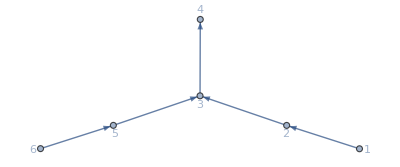

```mathematica
Graph[List[DirectedEdge[6,5],DirectedEdge[3,4],DirectedEdge[2,3],DirectedEdge[5,3],DirectedEdge[1,2]],List[Rule[FormatType,TraditionalForm],GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]]
```

```mathematica
temp1=tem1[[All,2]]//Factor;
```

```mathematica
alpexp=;
```

```mathematica
alpexp[[1;;7]]
```

{(1+2 f_2+2 f_1 f_2+f_2^2+2 f_1 f_2^2+f_1^2 f_2^2+f_1^2 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4)/(f_1^2 f_3),f_2^2 f_3 (1+2 f_1+f_1^2+f_1^2 f_4+f_1^2 f_3 f_4),1/(f_2^2 f_4),(1+2 f_2+2 f_1 f_2+f_2^2+2 f_1 f_2^2+f_1^2 f_2^2+2 f_1 f_2 f_4+2 f_1 f_2^2 f_4+2 f_1^2 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4+f_1^2 f_2^2 f_4^2+f_1^2 f_2^2 f_3 f_4^2)/(f_1^2 f_2^2 f_3^2 f_4),f_2^2 (1+f_3) f_4,(f_3 (1+2 f_1+f_1^2+f_1^2 f_4))/f_4,(1+f_4)/(f_2^2 f_3 f_4)}

The last entry will now end as the first entry!

```mathematica
temp13sim[[1]]*temp116simt[[1]]
```

1/(f[2]^2 (1+f[3]) f[4])

```mathematica
temp13sim[[14]]/temp116simt[[7]]
```

f[2]^2 (1+f[3]) f[4]

```mathematica
temp13sim[[2]]*temp116simt[[1]]
```

(1+f[4])/(f[2]^2 f[3] f[4])

```mathematica
temp13sim[[3]]/temp116simt[[2]]
```

(f[2]^2 f[3] f[4])/(1+f[4])

```mathematica
temp13sim[[4]]/temp116simt[[2]]
```

f[2]^2 f[3] (1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4])

```mathematica
alpexp[[1;;7]]
```

{(1+2 f_2+2 f_1 f_2+f_2^2+2 f_1 f_2^2+f_1^2 f_2^2+f_1^2 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4)/(f_1^2 f_3),f_2^2 f_3 (1+2 f_1+f_1^2+f_1^2 f_4+f_1^2 f_3 f_4),1/(f_2^2 f_4),(1+2 f_2+2 f_1 f_2+f_2^2+2 f_1 f_2^2+f_1^2 f_2^2+2 f_1 f_2 f_4+2 f_1 f_2^2 f_4+2 f_1^2 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4+f_1^2 f_2^2 f_4^2+f_1^2 f_2^2 f_3 f_4^2)/(f_1^2 f_2^2 f_3^2 f_4),f_2^2 (1+f_3) f_4,(f_3 (1+2 f_1+f_1^2+f_1^2 f_4))/f_4,(1+f_4)/(f_2^2 f_3 f_4)}

```mathematica
temp13=temp1[[All,3]]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp13sim=%/.{f[6]->f[1],f[5]->f[2]}//Factor
%//Length
```

{(1+f[1]+f[1] f[4]+f[1] f[3] f[4])^2/((1+f[3]) f[4]),((1+f[4]) (1+f[1]+f[1] f[4]+f[1] f[3] f[4])^2)/(f[3] f[4]),1/(f[1]^2 f[3] f[4] (1+f[4]))(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)^2,1/(f[1]^2 f[3] f[4]^2)(1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]) (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)^2,(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)^2/(f[1]^2 f[2]^2 f[3] f[4]^2 (1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4])),1/(f[1]^4 f[2]^2 f[3]^2 f[4]^3)(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2),(1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)^2/(f[1]^2 f[4] (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)),1/(f[1]^4 f[2]^2 f[3] f[4]^3)(1+2 f[1]+f[1]^2+f[1]^2 f[4]) (1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)^2,((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])^2)/(f[1]^2 f[2]^2 f[3] f[4] (1+2 f[1]+f[1]^2+f[1]^2 f[4])),1/(f[1]^4 f[2]^2 f[3] f[4]^2)(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]),((1+f[2]+f[1] f[2])^2 f[3])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]),(1+f[2]+f[1] f[2])^2/(f[1]^2 f[2]^2 f[4]),f[4],(1+f[3]) f[4]}

14

```mathematica
temp14=temp1[[All,4]]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp14sim=%/.{f[6]->f[1],f[5]->f[2]}//DeleteDuplicates[#,((#1*#2===1)&)]&//Factor//DeleteDuplicates
%//Length
```

{(1+f[4]+f[3] f[4])/f[3],(1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2)/f[4],1/(f[1]^2 f[3] f[4])(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3),1/(f[1]^2 f[2]^2 f[3] f[4]^2)(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3),1/(f[1]^2 f[4])(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2),(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4])/(f[1]^2 f[2]^2 f[3] f[4]),f[3]}

7

```mathematica
Complement[temp14sim,alpexp[[-7;;-1]]/.{Subscript[f, i_]:>f[i]}]
```

{}

{f[4],(1+f[3]) f[4],(1+f[1]+f[1] f[4]+f[1] f[3] f[4])/((1+f[3]) f[4]),(1+f[1]+f[1] f[4]+f[1] f[3] f[4])^2/((1+f[3]) f[4]),((1+f[4]) (1+f[1]+f[1] f[4]+f[1] f[3] f[4])^2)/(f[3] f[4]),(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)/(f[1] (1+f[4]) (1+f[1]+f[1] f[4]+f[1] f[3] f[4])),1/(f[1]^2 f[3] f[4] (1+f[4]))(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)^2,1/(f[1]^2 f[3] f[4]^2)(1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]) (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)^2,(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)/(f[2] (1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]) (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)),(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)^2/(f[1]^2 f[2]^2 f[3] f[4]^2 (1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4])),1/(f[1]^4 f[2]^2 f[3]^2 f[4]^3)(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2),(f[1] f[2] f[3] f[4] (1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2))/((1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2) (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)),(1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)^2/(f[1]^2 f[4] (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)),1/(f[1]^4 f[2]^2 f[3] f[4]^3)(1+2 f[1]+f[1]^2+f[1]^2 f[4]) (1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)^2,(f[1] f[4] (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]))/((1+2 f[1]+f[1]^2+f[1]^2 f[4]) (1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)),((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])^2)/(f[1]^2 f[2]^2 f[3] f[4] (1+2 f[1]+f[1]^2+f[1]^2 f[4])),1/(f[1]^4 f[2]^2 f[3] f[4]^2)(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]),(f[1]^2 f[2] (1+f[2]+f[1] f[2]) f[3] f[4])/((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]) (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])),((1+f[2]+f[1] f[2])^2 f[3])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]),(1+f[2]+f[1] f[2])^2/(f[1]^2 f[2]^2 f[4]),(f[1] f[2] f[4])/(1+f[2]+f[1] f[2])}

21

```mathematica
(*{f[4],1+f[3],(f[1] f[2] f[4])/(1+f[2]+f[1] f[2]),(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])/(f[1]^2 f[2]^2 f[4]^2f[3]),(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])/f[1],f[2]^2 f[3] f[4] (1+2 f[1]+f[1]^2+f[1]^2 f[4]),1/(f[1]^2 f[2]^2 f[4]^2f[3])((1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)),(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)/(f[1]^2 f[2]^4 f[3]^2 f[4]^3)}*)
```

```mathematica
temp116t=temp1[[All,1]]*temp1[[All,6]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp116simt=%/.{f[6]->f[1],f[5]->f[2]}//DeleteDuplicates[#,((#1*#2===1)&)]&//Factor//DeleteDuplicates
%//Length
```

{1/(f[2]^2 (1+f[1]+f[1] f[4]+f[1] f[3] f[4])^2),1/(f[1]^2 f[2]^2 f[3]^2 f[4]^2)(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1] f[4]+2 f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^2 f[2] f[4]^2+f[1]^2 f[2] f[3] f[4]^2)^2,1/(f[1]^2 f[4]^2)(1+2 f[1]+f[1]^2+f[2]+3 f[1] f[2]+3 f[1]^2 f[2]+f[1]^3 f[2]+f[1]^2 f[4]+f[1] f[2] f[4]+3 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+f[1]^2 f[2] f[3] f[4]+f[1]^3 f[2] f[3] f[4]+f[1]^3 f[2] f[4]^2+f[1]^3 f[2] f[3] f[4]^2)^2,1/(f[1]^4 f[2]^2 f[3]^2 f[4]^2)(1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)^2,((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])^2)/(f[1]^2 f[2]^2 f[4]^2),(1+f[2]+f[1] f[2])^2/f[1]^2,1/f[2]^2}

7

```mathematica
temp1[[All,1]]-temp1[[All,6]]/.{f[6]->f[1],f[5]->f[2]}//Factor
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
temp1[[All,5]]-temp1[[All,2]]/.{f[6]->f[1],f[5]->f[2]}//Factor
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
temp125t=temp1[[All,2]]*temp1[[All,5]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp125simt=%/.{f[6]->f[1],f[5]->f[2]}//DeleteDuplicates[#,((#1*#2===1)&)]&//Factor//DeleteDuplicates
%//Length
```

{(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])^2/(f[1]^2 (1+f[4]+f[3] f[4])^2),1/(f[1]^2 f[3]^2 f[4]^2)(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])^2 (1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2)^2,(1+f[1]+f[1] f[4])^2/(f[2]^2 (1+2 f[1]+f[1]^2+2 f[1] f[4]+2 f[1]^2 f[4]+f[1]^2 f[3] f[4]+f[1]^2 f[4]^2+f[1]^2 f[3] f[4]^2)^2),1/(f[1]^4 f[2]^2 f[3]^2 f[4]^4)(1+f[1]+f[1] f[4])^2 (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3)^2,(f[1]^2 f[2]^2 f[3]^2 f[4]^2 (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4])^2)/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+2 f[1]^2 f[2] f[3] f[4]+2 f[1]^3 f[2] f[3] f[4]+2 f[1]^2 f[2]^2 f[3] f[4]+4 f[1]^3 f[2]^2 f[3] f[4]+2 f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2] f[3] f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2+4 f[1]^3 f[2]^2 f[3] f[4]^2+4 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[3]^2 f[4]^2+f[1]^4 f[2]^2 f[4]^3+2 f[1]^4 f[2]^2 f[3] f[4]^3+f[1]^4 f[2]^2 f[3]^2 f[4]^3)^2,1/(f[1]^6 f[2]^2 f[3]^2 f[4]^4)(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4])^2 (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3)^2,(f[1]^2 f[4]^2 (1+f[2]+f[1] f[2]+f[1] f[2] f[4])^2)/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+f[1]^2 f[4]+2 f[1] f[2] f[4]+6 f[1]^2 f[2] f[4]+4 f[1]^3 f[2] f[4]+2 f[1] f[2]^2 f[4]+7 f[1]^2 f[2]^2 f[4]+8 f[1]^3 f[2]^2 f[4]+3 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+2 f[1]^3 f[2] f[4]^2+f[1]^2 f[2]^2 f[4]^2+4 f[1]^3 f[2]^2 f[4]^2+3 f[1]^4 f[2]^2 f[4]^2+2 f[1]^3 f[2]^2 f[3] f[4]^2+2 f[1]^4 f[2]^2 f[3] f[4]^2+f[1]^4 f[2]^2 f[4]^3+f[1]^4 f[2]^2 f[3] f[4]^3)^2,1/(f[1]^6 f[2]^4 f[3]^2 f[4]^4)(1+f[2]+f[1] f[2]+f[1] f[2] f[4])^2 (1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2)^2,(f[1]^4 (1+f[1])^2 f[2]^2 f[3]^2 f[4]^2)/(1+2 f[1]+f[1]^2+2 f[2]+6 f[1] f[2]+6 f[1]^2 f[2]+2 f[1]^3 f[2]+f[2]^2+4 f[1] f[2]^2+6 f[1]^2 f[2]^2+4 f[1]^3 f[2]^2+f[1]^4 f[2]^2+2 f[1]^2 f[2] f[4]+2 f[1]^3 f[2] f[4]+2 f[1]^2 f[2]^2 f[4]+4 f[1]^3 f[2]^2 f[4]+2 f[1]^4 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+2 f[1]^3 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[3] f[4]+f[1]^4 f[2]^2 f[4]^2+f[1]^4 f[2]^2 f[3] f[4]^2)^2,((1+f[1])^2 (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4])^2)/(f[1]^4 f[2]^2 f[4]^2),(f[1]^2 f[2]^2 (1+f[2])^2 f[4]^2)/((1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4])^2),(1+f[2])^2/(f[1]^2 f[2]^2),f[1]^2,f[1]^2 (1+f[4]+f[3] f[4])^2}

14

#### mutate 52

```mathematica
ClearAll[g];
g=Graph[{2->1,1->4,4->2,4->3,3->1,5->3,3->6,6->5,6->4},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];],5->Button[5,g=MutateGraph[g,5];],6->Button[6,g=MutateGraph[g,6];]},VertexCoordinates->{{2.632270101299922,0.3659725975716903},{2.016435883889035,1.121405098814431},{1.7732239568678387,0.26235895438234447},{0.8590461444320836,0.85904614443208},{0.,0.7554325012427503},{0.6158342174108874,0.}},GraphLayout->"HighDimensionalEmbedding"]
```

-Graphics-

```mathematica
g0=Graph[{2->1,1->4,4->2,4->3,3->1,5->3,3->6,6->5,6->4}];
```

```mathematica
Dynamic[g]
```

```mathematica
ClearAll[MatFromQuiver];
MatFromQuiver[g_]:=Module[{edg,ver},
edg=EdgeList[g];
ver=VertexCount[g];
(*Print[edg];*)
Return[SparseArray[edg/.DirectedEdge[a_,b_]:>({{a,b}->#,{b,a}->-#}&[Count[edg,DirectedEdge[a,b]]])//Flatten,{ver,ver}]//Normal];
];
```

```mathematica
fdefE6={f[1]->-((ab[1,2,4,7] ab[3,4,5,6])/ab[4,cap1[{1,2},{3,5},{6,7}]]),f[2]->(ab[1,2,3,4] ab[1,2,6,7])/(ab[1,2,3,7] ab[1,2,4,6]),f[3]->-(ab[4,cap1[{1,2},{3,5},{6,7}]]/(ab[1,2,3,4] ab[4,5,6,7])),f[4]->(ab[5,cap1[{1,2},{3,4},{6,7}]] ab[1,2,4,6])/(ab[1,2,4,5] ab[1,2,6,7] ab[3,4,5,6]),f[5]->(ab[1,5,6,7] ab[2,3,4,5])/ab[5,cap1[{1,2},{3,4},{6,7}]],f[6]->-((ab[1,2,6,7] ab[1,3,4,5] ab[4,5,6,7])/(ab[4,cap1[{1,2},{3,5},{6,7}]] ab[1,5,6,7]))};
MatE6={{1,0,0,0},{(1+f[5])/f[5],1,0,0},{(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])/(f[1] f[2] f[3] f[4] f[5]),(1+f[2]+f[1] f[2]+f[6]+f[2] f[6]+f[1] f[2] f[6]+f[1] f[2] f[4] f[6]+f[1] f[2] f[3] f[4] f[6])/(f[1] f[2] f[3] f[4] f[6]),1,0},{(1+f[2]+f[1] f[2]+f[1] f[2] f[4])/(f[1] f[2] f[3] f[4] f[5]),((1+f[2]+f[1] f[2]+f[1] f[2] f[4]) (1+f[6]))/(f[1] f[2] f[3] f[4] f[6]),1+f[2]+f[1] f[2]+f[1] f[2] f[4],1},{0,1/(f[3] f[6]),f[2] (1+f[1]+f[1] f[4]),1},{0,0,(f[2] (1+f[2]+f[1] f[2]+f[1] f[2] f[4]))/(1+f[2]),1},{0,0,0,1}};
```

```mathematica
FB[1,2,3,6]*FB[1,2,4,5]/FB[1,2,3,4]/FB[1,2,5,6]/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor
```

(1+f[2])/(f[1] f[2] (1+f[4]))

```mathematica
FB[1,2,3,7]*FB[1,2,5,6]/FB[1,2,3,5]/FB[1,2,6,7]/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor
```

(f[1] (1+f[4]))/(1+f[2]+f[1] f[2]+f[1] f[2] f[4])

So the quiver starts from the foldable one

```mathematica
Bm=MatFromQuiver[g0]
```

{{0,-1,-1,1,0,0},{1,0,0,-1,0,0},{1,0,0,-1,-1,1},{-1,1,1,0,0,-1},{0,0,1,0,0,-1},{0,0,-1,1,1,0}}

```mathematica
yv={f[1],f[2],f[3],f[4],f[5],f[6]};
```

```mathematica
ml={2,5};
tem=Reap[
temp={Bm,yv};
Sow[temp];
Do[
temp=MutateY[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

```mathematica
(*folding condition, checked!*)
```

```mathematica
Solve[{tem[[-1,2,1]]==tem[[-1,2,6]],tem[[-1,2,2]]==tem[[-1,2,5]]}]//Factor
```

{{f[1]→((1+f[2])^2 f[6])/f[2],f[5]→f[2]}}

```mathematica
tem[[-1,1]]
```

{{0,1,-1,0,0,0},{-1,0,0,1,0,0},{1,0,0,-1,1,0},{0,-1,1,0,0,-1},{0,0,-1,0,0,1},{0,0,0,1,-1,0}}

```mathematica
Bmn={{0,1,-1,0,0,0},{-1,0,0,1,0,0},{1,0,0,-1,1,0},{0,-1,1,0,0,-1},{0,0,-1,0,0,1},{0,0,0,1,-1,0}};
yv=f/@Range[6];
```

```mathematica
ml={5,2};
temtest=Reap[
temp={Bmn,yv};
Sow[temp];
Do[
temp=MutateY[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];(*this get back to the initial quiver of the net of G(4,7)*)
```

```mathematica
temtest[[-1]]
```

{{{0,-1,-1,1,0,0},{1,0,0,-1,0,0},{1,0,0,-1,-1,1},{-1,1,1,0,0,-1},{0,0,1,0,0,-1},{0,0,-1,1,1,0}},{f[1] (1+f[2]),1/f[2],f[3] (1+f[5]),(f[2] f[4])/(1+f[2]),1/f[5],(f[5] f[6])/(1+f[5])}}

```mathematica
Solve[{f[1] (1+f[2]),1/f[2],f[3] (1+f[5]),(f[2] f[4])/(1+f[2]),1/f[5],(f[5] f[6])/(1+f[5])}=={(1+F[2])/(F[1] F[2] (1+F[4])),(F[1] (1+F[4]))/(1+F[2]+F[1] F[2]+F[1] F[2] F[4]),(F[1] F[2] F[3] F[4] (1+F[4]) F[6])/((1+F[2]+F[1] F[2]+F[1] F[2] F[4]) (1+F[6]+F[4] F[6])),((1+F[2]+F[1] F[2]+F[1] F[2] F[4]) (1+F[6]+F[4] F[6]))/((1+F[2]) F[4]),F[5] (1+F[6]+F[4] F[6]),1/((1+F[4]) F[6])},f/@Range[6]]
```

{{f[1]→1/(F[2] (1+F[1]+F[1] F[4])),f[2]→(1+F[2]+F[1] F[2]+F[1] F[2] F[4])/(F[1] (1+F[4])),f[3]→(F[1] F[2] F[3] F[4] F[5] F[6]+F[1] F[2] F[3] F[4]^2 F[5] F[6])/((1+F[2]+F[1] F[2]+F[1] F[2] F[4]) (1+F[5]+F[5] F[6]+F[4] F[5] F[6])),f[4]→((1+F[1]+F[1] F[4]) (1+F[6]+F[4] F[6]))/F[4],f[5]→1/(F[5] (1+F[6]+F[4] F[6])),f[6]→(1+F[5]+F[5] F[6]+F[4] F[5] F[6])/((1+F[4]) F[6])}}

```mathematica
frep1={f[1]->1/(F[2] (1+F[1]+F[1] F[4])),f[2]->(1+F[2]+F[1] F[2]+F[1] F[2] F[4])/(F[1] (1+F[4])),f[3]->(F[1] F[2] F[3] F[4] F[5] F[6]+F[1] F[2] F[3] F[4]^2 F[5] F[6])/((1+F[2]+F[1] F[2]+F[1] F[2] F[4]) (1+F[5]+F[5] F[6]+F[4] F[5] F[6])),f[4]->((1+F[1]+F[1] F[4]) (1+F[6]+F[4] F[6]))/F[4],f[5]->1/(F[5] (1+F[6]+F[4] F[6])),f[6]->(1+F[5]+F[5] F[6]+F[4] F[5] F[6])/((1+F[4]) F[6])}/.{F->f}
```

{f[1]→1/(f[2] (1+f[1]+f[1] f[4])),f[2]→(1+f[2]+f[1] f[2]+f[1] f[2] f[4])/(f[1] (1+f[4])),f[3]→(f[1] f[2] f[3] f[4] f[5] f[6]+f[1] f[2] f[3] f[4]^2 f[5] f[6])/((1+f[2]+f[1] f[2]+f[1] f[2] f[4]) (1+f[5]+f[5] f[6]+f[4] f[5] f[6])),f[4]→((1+f[1]+f[1] f[4]) (1+f[6]+f[4] f[6]))/f[4],f[5]→1/(f[5] (1+f[6]+f[4] f[6])),f[6]→(1+f[5]+f[5] f[6]+f[4] f[5] f[6])/((1+f[4]) f[6])}

```mathematica
Solve[{f[5]==f[1],f[6]==f[2]}/.frep1]
```

{{f[1]→f[6],f[5]→f[2]},{f[2]→1/(-1-f[1]-f[1] f[4]),f[5]→-1/(1+f[6]+f[4] f[6])}}

This folding condition is consistent with the former ones

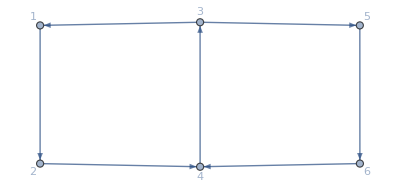

```mathematica
Graph[List[DirectedEdge[4,3],DirectedEdge[3,1],DirectedEdge[6,4],DirectedEdge[5,6],DirectedEdge[3,5],DirectedEdge[2,4],DirectedEdge[1,2]],List[Rule[FormatType,TraditionalForm],GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]]
```

```mathematica
Table[{4,1,5,3,2,6},{i,1,12}]//Flatten
```

{4,3,1,6,2,5,4,3,1,6,2,5,4,3,1,6,2,5,4,3,1,6,2,5,4,3,1,6,2,5,4,3,1,6,2,5,4,3,1,6,2,5,4,3,1,6,2,5,4,3,1,6,2,5,4,3,1,6,2,5,4,3,1,6,2,5,4,3,1,6,2,5}

```mathematica
ml=Table[{4,1,5,3,2,6},{i,1,12}]//Flatten;
tem=Reap[
temp={Bmn,yv};
Sow[temp];
Do[
temp=MutateY[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

```mathematica
Table[{3+1,6+1}+6*(i-1),{i,1,12}]//Flatten
%//Length
```

{4,7,10,13,16,19,22,25,28,31,34,37,40,43,46,49,52,55,58,61,64,67,70,73}

24

```mathematica
alpexp=;
```

```mathematica
temp1=tem[[{4,7,10,13,16,19,22,25,28,31,34,37,40,43,46,49,52,55,58,61,64,67,70,73}]][[All,2]]//Factor;
```

```mathematica
temp14=temp1[[All,4]]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp14sim=%/.frep1/.{f[6]->f[1],f[5]->f[2]}//Factor
%//Length
```

{f[4]/(1+f[1]+f[1] f[4])^2,((1+f[1])^2 f[3])/(1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]),(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])^2/(f[3] (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])),(1+f[2]+f[1] f[2]+f[1] f[2] f[4])^2/(f[1]^2 f[2]^2 f[3] f[4] (1+f[4])),(f[1]^2 f[3] f[4])/(1+2 f[1]+f[1]^2+f[1]^2 f[4]),((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4])^2)/(f[1]^2 (1+f[3]) f[4]),((1+f[2])^2 f[4])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)}

7

```mathematica
temp13=temp1[[All,3]]//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp13sim=%/.{f[5]->f[1],f[6]->f[2]}/.frep1/.{f[6]->f[1],f[5]->f[2]}//DeleteDuplicates[#,((#1*#2===1)&)]&//Factor//DeleteDuplicates
%//Length
```

{(f[1]^2 f[3] f[4])/(1+2 f[1]+f[1]^2+f[1]^2 f[4]),((1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4])^2)/(f[1]^2 (1+f[3]) f[4]),((1+f[2])^2 f[4])/(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2),(1+f[1]+f[1] f[4])^2/f[4],((1+f[1])^2 f[3])/(1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]),(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])^2/(f[3] (1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])),(1+f[2]+f[1] f[2]+f[1] f[2] f[4])^2/(f[1]^2 f[2]^2 f[3] f[4] (1+f[4]))}

7

```mathematica
(*{f[4],1+f[3],(f[1] f[2] f[4])/(1+f[2]+f[1] f[2]),(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])/(f[1]^2 f[2]^2 f[4]^2f[3]),(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4])/f[1],f[2]^2 f[3] f[4] (1+2 f[1]+f[1]^2+f[1]^2 f[4]),1/(f[1]^2 f[2]^2 f[4]^2f[3])((1+f[1]+2 f[2]+4 f[1] f[2]+2 f[1]^2 f[2]+f[2]^2+3 f[1] f[2]^2+3 f[1]^2 f[2]^2+f[1]^3 f[2]^2+f[1] f[2] f[4]+2 f[1]^2 f[2] f[4]+f[1] f[2]^2 f[4]+3 f[1]^2 f[2]^2 f[4]+2 f[1]^3 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[3] f[4]+f[1]^3 f[2]^2 f[4]^2+f[1]^3 f[2]^2 f[3] f[4]^2)),(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)/(f[1]^2 f[2]^4 f[3]^2 f[4]^3)}*)
```

```mathematica
temp116=temp1[[All,{1,6}]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp116sim=%/.frep1/.{f[6]->f[1],f[5]->f[2]}//DeleteDuplicates[#,((#1*#2===1)&)]&//Factor//DeleteDuplicates
%//Length
```

{f[2] (1+f[1]+f[1] f[4]),(1+2 f[1]+f[1]^2+f[1]^2 f[4])/(f[1] f[4]),(f[2] (1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]))/(1+f[1]),(f[1] f[2] (1+f[3]) f[4])/(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]),(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])/(f[1] (1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])),(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)/(f[1] f[2] (1+f[2]) f[3] f[4]),(f[1] (1+f[4]))/(1+f[2]+f[1] f[2]+f[1] f[2] f[4])}

7

```mathematica
temp125=temp1[[All,{2,5}]]//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&;
temp125sim=%/.frep1/.{f[6]->f[1],f[5]->f[2]}//DeleteDuplicates[#,((#1*#2===1)&)]&//Factor//DeleteDuplicates
%//Length
```

{(1+2 f[1]+f[1]^2+f[1]^2 f[4])/(f[1] f[4]),f[2] (1+f[1]+f[1] f[4]),(f[2] (1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]))/(1+f[1]),(f[1] f[2] (1+f[3]) f[4])/(1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]),(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])/(f[1] (1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])),(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2)/(f[1] f[2] (1+f[2]) f[3] f[4]),(f[1] (1+f[4]))/(1+f[2]+f[1] f[2]+f[1] f[2] f[4])}

7

Then we consider the first 14 terms

```mathematica
alpexp[[1;;7]]/.{Subscript[f, i_]:>f[i]}
```

{(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4])/(f[1]^2 f[3]),f[2]^2 f[3] (1+2 f[1]+f[1]^2+f[1]^2 f[4]+f[1]^2 f[3] f[4]),1/(f[2]^2 f[4]),1/(f[1]^2 f[2]^2 f[3]^2 f[4])(1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+2 f[1] f[2] f[4]+2 f[1] f[2]^2 f[4]+2 f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]+f[1]^2 f[2]^2 f[4]^2+f[1]^2 f[2]^2 f[3] f[4]^2),f[2]^2 (1+f[3]) f[4],(f[3] (1+2 f[1]+f[1]^2+f[1]^2 f[4]))/f[4],(1+f[4])/(f[2]^2 f[3] f[4])}

```mathematica
Position[temp13sim,1+2 f[2]+2 f[1] f[2]+f[2]^2+2 f[1] f[2]^2+f[1]^2 f[2]^2+f[1]^2 f[2]^2 f[4]+f[1]^2 f[2]^2 f[3] f[4]]
```

{{6,3,1}}

```mathematica
alpexp[[8;;14]]
```

{(f_2^2 (1+f_1+f_2+2 f_1 f_2+f_1^2 f_2+f_1^2 f_2 f_4+f_1^2 f_2 f_3 f_4)^2)/f_1^2,f_1^2 f_3^2,(1+f_2+f_1 f_2+f_1 f_2 f_4)^2/(f_1^2 f_2^4 f_3^2 f_4^2),(1+f_2+f_1 f_2+f_1 f_2 f_4+f_1 f_2 f_3 f_4)^2/(f_1^2 f_3^2),(1+f_1)^2 f_2^2 f_3^2,(1+f_1+f_1 f_4)^2/(f_2^2 f_4^2),(1+f_2)^2/(f_1^2 f_2^2 f_3^2)}

```mathematica
alpexp[[15;;21]]
```

{((1+f_1+f_2+2 f_1 f_2+f_1^2 f_2+f_1^2 f_2 f_4)^2)/(f_1^2 f_2^2 f_4^2),((1+f_1+f_2+2 f_1 f_2+f_1^2 f_2+f_1 f_4+2 f_1 f_2 f_4+2 f_1^2 f_2 f_4+f_1^2 f_2 f_3 f_4+f_1^2 f_2 f_4^2+f_1^2 f_2 f_3 f_4^2)^2)/(f_1^2 f_2^2 f_3^2 f_4^2),(1+f_2+f_1 f_2)^2/f_1^2,1/(f_1^2 f_4^2)(1+2 f_1+f_1^2+f_2+3 f_1 f_2+3 f_1^2 f_2+f_1^3 f_2+f_1^2 f_4+f_1 f_2 f_4+3 f_1^2 f_2 f_4+2 f_1^3 f_2 f_4+f_1^2 f_2 f_3 f_4+f_1^3 f_2 f_3 f_4+f_1^3 f_2 f_4^2+f_1^3 f_2 f_3 f_4^2)^2,1/f_2^2,1/(f_1^4 f_2^2 f_3^2 f_4^2)(1+f_1+2 f_2+4 f_1 f_2+2 f_1^2 f_2+f_2^2+3 f_1 f_2^2+3 f_1^2 f_2^2+f_1^3 f_2^2+f_1 f_2 f_4+2 f_1^2 f_2 f_4+f_1 f_2^2 f_4+3 f_1^2 f_2^2 f_4+2 f_1^3 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4+f_1^3 f_2^2 f_3 f_4+f_1^3 f_2^2 f_4^2+f_1^3 f_2^2 f_3 f_4^2)^2,f_2^2 (1+f_1+f_1 f_4+f_1 f_3 f_4)^2}

```mathematica
alpexp[[22;;28]]
```

{(1+2 f_1+f_1^2+2 f_1 f_4+2 f_1^2 f_4+f_1^2 f_3 f_4+f_1^2 f_4^2+f_1^2 f_3 f_4^2)/f_4,(1+2 f_2+2 f_1 f_2+f_2^2+2 f_1 f_2^2+f_1^2 f_2^2+f_1^2 f_2^2 f_4)/(f_1^2 f_2^2 f_3 f_4),1/(f_1^2 f_3 f_4)(1+2 f_1+f_1^2+2 f_2+6 f_1 f_2+6 f_1^2 f_2+2 f_1^3 f_2+f_2^2+4 f_1 f_2^2+6 f_1^2 f_2^2+4 f_1^3 f_2^2+f_1^4 f_2^2+f_1^2 f_4+2 f_1 f_2 f_4+6 f_1^2 f_2 f_4+4 f_1^3 f_2 f_4+2 f_1 f_2^2 f_4+7 f_1^2 f_2^2 f_4+8 f_1^3 f_2^2 f_4+3 f_1^4 f_2^2 f_4+2 f_1^2 f_2 f_3 f_4+2 f_1^3 f_2 f_3 f_4+2 f_1^2 f_2^2 f_3 f_4+4 f_1^3 f_2^2 f_3 f_4+2 f_1^4 f_2^2 f_3 f_4+2 f_1^3 f_2 f_4^2+f_1^2 f_2^2 f_4^2+4 f_1^3 f_2^2 f_4^2+3 f_1^4 f_2^2 f_4^2+2 f_1^3 f_2 f_3 f_4^2+f_1^2 f_2^2 f_3 f_4^2+4 f_1^3 f_2^2 f_3 f_4^2+4 f_1^4 f_2^2 f_3 f_4^2+f_1^4 f_2^2 f_3^2 f_4^2+f_1^4 f_2^2 f_4^3+2 f_1^4 f_2^2 f_3 f_4^3+f_1^4 f_2^2 f_3^2 f_4^3),f_3,1/(f_1^2 f_2^2 f_3 f_4^2)(1+2 f_1+f_1^2+2 f_2+6 f_1 f_2+6 f_1^2 f_2+2 f_1^3 f_2+f_2^2+4 f_1 f_2^2+6 f_1^2 f_2^2+4 f_1^3 f_2^2+f_1^4 f_2^2+f_1^2 f_4+2 f_1 f_2 f_4+6 f_1^2 f_2 f_4+4 f_1^3 f_2 f_4+2 f_1 f_2^2 f_4+7 f_1^2 f_2^2 f_4+8 f_1^3 f_2^2 f_4+3 f_1^4 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4+2 f_1^3 f_2^2 f_3 f_4+f_1^4 f_2^2 f_3 f_4+2 f_1^3 f_2 f_4^2+f_1^2 f_2^2 f_4^2+4 f_1^3 f_2^2 f_4^2+3 f_1^4 f_2^2 f_4^2+2 f_1^3 f_2^2 f_3 f_4^2+2 f_1^4 f_2^2 f_3 f_4^2+f_1^4 f_2^2 f_4^3+f_1^4 f_2^2 f_3 f_4^3),(1+f_4+f_3 f_4)/f_3,1/(f_1^2 f_4)(1+2 f_1+f_1^2+2 f_2+6 f_1 f_2+6 f_1^2 f_2+2 f_1^3 f_2+f_2^2+4 f_1 f_2^2+6 f_1^2 f_2^2+4 f_1^3 f_2^2+f_1^4 f_2^2+2 f_1^2 f_2 f_4+2 f_1^3 f_2 f_4+2 f_1^2 f_2^2 f_4+4 f_1^3 f_2^2 f_4+2 f_1^4 f_2^2 f_4+f_1^2 f_2^2 f_3 f_4+2 f_1^3 f_2^2 f_3 f_4+f_1^4 f_2^2 f_3 f_4+f_1^4 f_2^2 f_4^2+f_1^4 f_2^2 f_3 f_4^2)}

#### new quiver 3124

```mathematica
rewrite={a11->(ab[1,2,3,4] ab[1,5,6,7] ab[2,3,6,7])/(ab[1,2,3,7] ab[1,2,6,7] ab[3,4,5,6]),a21->(ab[1,2,3,4] ab[2,5,6,7])/(ab[1,2,6,7] ab[2,3,4,5]),a31->(ab[1,5,6,7] ab[2,3,4,7])/(ab[1,2,3,7] ab[4,5,6,7]),a41->(ab[2,4,5,7] ab[3,4,5,6])/(ab[2,3,4,5] ab[4,5,6,7]),a51->ab[1,cap1[{2,3},{4,5},{6,7}]]/(ab[1,2,3,4] ab[1,5,6,7]),a61->-ab[1,cap1[{2,7},{3,4},{5,6}]]/(ab[1,2,3,4] ab[1,5,6,7]),a12->(ab[1,2,6,7] ab[1,3,4,7] ab[2,3,4,5])/(ab[1,2,3,4] ab[1,2,3,7] ab[4,5,6,7]),a22->(ab[1,3,6,7] ab[2,3,4,5])/(ab[1,2,3,7] ab[3,4,5,6]),a32->(ab[1,2,6,7] ab[1,3,4,5])/(ab[1,2,3,4] ab[1,5,6,7]),a42->(ab[1,3,5,6] ab[4,5,6,7])/(ab[1,5,6,7] ab[3,4,5,6]),a52->ab[2,cap1[{1,7},{3,4},{5,6}]]/(ab[1,2,6,7] ab[2,3,4,5]),a62->-ab[2,cap1[{1,3},{4,5},{6,7}]]/(ab[1,2,6,7] ab[2,3,4,5]),a13->(ab[1,2,3,7] ab[1,2,4,5] ab[3,4,5,6])/(ab[1,2,3,4] ab[1,5,6,7] ab[2,3,4,5]),a23->(ab[1,2,4,7] ab[3,4,5,6])/(ab[1,2,3,4] ab[4,5,6,7]),a33->(ab[1,2,3,7] ab[2,4,5,6])/(ab[1,2,6,7] ab[2,3,4,5]),a43->(ab[1,5,6,7] ab[2,4,6,7])/(ab[1,2,6,7] ab[4,5,6,7]),a53->ab[3,cap1[{1,2},{4,5},{6,7}]]/(ab[1,2,3,7] ab[3,4,5,6]),a63->-ab[3,cap1[{1,7},{2,4},{5,6}]]/(ab[1,2,3,7] ab[3,4,5,6]),a14->(ab[1,2,3,4] ab[2,3,5,6] ab[4,5,6,7])/(ab[1,2,6,7] ab[2,3,4,5] ab[3,4,5,6]),a24->(ab[1,2,3,5] ab[4,5,6,7])/(ab[1,5,6,7] ab[2,3,4,5]),a34->(ab[1,2,3,4] ab[3,5,6,7])/(ab[1,2,3,7] ab[3,4,5,6]),a44->(ab[1,2,6,7] ab[1,3,5,7])/(ab[1,2,3,7] ab[1,5,6,7]),a54->ab[4,cap1[{1,7},{2,3},{5,6}]]/(ab[1,2,3,4] ab[4,5,6,7]),a64->-ab[4,cap1[{1,2},{3,5},{6,7}]]/(ab[1,2,3,4] ab[4,5,6,7]),a15->(ab[1,5,6,7] ab[2,3,4,5] ab[3,4,6,7])/(ab[1,2,3,7] ab[3,4,5,6] ab[4,5,6,7]),a25->(ab[1,5,6,7] ab[2,3,4,6])/(ab[1,2,6,7] ab[3,4,5,6]),a35->(ab[1,4,6,7] ab[2,3,4,5])/(ab[1,2,3,4] ab[4,5,6,7]),a45->(ab[1,2,3,7] ab[1,2,4,6])/(ab[1,2,3,4] ab[1,2,6,7]),a55->ab[5,cap1[{1,2},{3,4},{6,7}]]/(ab[1,5,6,7] ab[2,3,4,5]),a65->-ab[5,cap1[{1,7},{2,3},{4,6}]]/(ab[1,5,6,7] ab[2,3,4,5]),a16->(ab[1,2,6,7] ab[1,4,5,7] ab[3,4,5,6])/(ab[1,2,3,4] ab[1,5,6,7] ab[4,5,6,7]),a26->(ab[1,2,6,7] ab[3,4,5,7])/(ab[1,2,3,7] ab[4,5,6,7]),a36->(ab[1,2,5,7] ab[3,4,5,6])/(ab[1,5,6,7] ab[2,3,4,5]),a46->(ab[1,2,3,4] ab[2,3,5,7])/(ab[1,2,3,7] ab[2,3,4,5]),a56->ab[6,cap1[{1,7},{2,3},{4,5}]]/(ab[1,2,6,7] ab[3,4,5,6]),a66->-ab[6,cap1[{1,2},{3,4},{5,7}]]/(ab[1,2,6,7] ab[3,4,5,6]),a17->(ab[1,2,3,7] ab[1,2,5,6] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,5,6,7] ab[2,3,4,5]),a27->(ab[1,2,3,7] ab[1,4,5,6])/(ab[1,2,3,4] ab[1,5,6,7]),a37->(ab[1,2,3,6] ab[4,5,6,7])/(ab[1,2,6,7] ab[3,4,5,6]),a47->(ab[1,3,4,6] ab[2,3,4,5])/(ab[1,2,3,4] ab[3,4,5,6]),a57->ab[7,cap1[{1,2},{3,4},{5,6}]]/(ab[1,2,3,7] ab[4,5,6,7]),a67->-ab[7,cap1[{1,6},{2,3},{4,5}]]/(ab[1,2,3,7] ab[4,5,6,7])}//Sort;
```

```mathematica
ClearAll[g];
g=Graph[{2->1,1->4,4->2,4->3,3->1,5->3,3->6,6->5,6->4},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];],5->Button[5,g=MutateGraph[g,5];],6->Button[6,g=MutateGraph[g,6];]},VertexCoordinates->{{2.632270101299922,0.3659725975716903},{2.016435883889035,1.121405098814431},{1.7732239568678387,0.26235895438234447},{0.8590461444320836,0.85904614443208},{0.,0.7554325012427503},{0.6158342174108874,0.}},GraphLayout->"HighDimensionalEmbedding"]
```

-Graphics-

```mathematica
Dynamic[g](*mutate 3,1,2,4,5,1,5*)
```

```mathematica
g0=Graph[{2->1,1->4,4->2,4->3,3->1,5->3,3->6,6->5,6->4}];
```

```mathematica
fdefE6={f[1]->-((ab[1,2,4,7] ab[3,4,5,6])/ab[4,cap1[{1,2},{3,5},{6,7}]]),f[2]->(ab[1,2,3,4] ab[1,2,6,7])/(ab[1,2,3,7] ab[1,2,4,6]),f[3]->-(ab[4,cap1[{1,2},{3,5},{6,7}]]/(ab[1,2,3,4] ab[4,5,6,7])),f[4]->(ab[5,cap1[{1,2},{3,4},{6,7}]] ab[1,2,4,6])/(ab[1,2,4,5] ab[1,2,6,7] ab[3,4,5,6]),f[5]->(ab[1,5,6,7] ab[2,3,4,5])/ab[5,cap1[{1,2},{3,4},{6,7}]],f[6]->-((ab[1,2,6,7] ab[1,3,4,5] ab[4,5,6,7])/(ab[4,cap1[{1,2},{3,5},{6,7}]] ab[1,5,6,7]))};
MatE6={{1,0,0,0},{(1+f[5])/f[5],1,0,0},{(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])/(f[1] f[2] f[3] f[4] f[5]),(1+f[2]+f[1] f[2]+f[6]+f[2] f[6]+f[1] f[2] f[6]+f[1] f[2] f[4] f[6]+f[1] f[2] f[3] f[4] f[6])/(f[1] f[2] f[3] f[4] f[6]),1,0},{(1+f[2]+f[1] f[2]+f[1] f[2] f[4])/(f[1] f[2] f[3] f[4] f[5]),((1+f[2]+f[1] f[2]+f[1] f[2] f[4]) (1+f[6]))/(f[1] f[2] f[3] f[4] f[6]),1+f[2]+f[1] f[2]+f[1] f[2] f[4],1},{0,1/(f[3] f[6]),f[2] (1+f[1]+f[1] f[4]),1},{0,0,(f[2] (1+f[2]+f[1] f[2]+f[1] f[2] f[4]))/(1+f[2]),1},{0,0,0,1}};
```

```mathematica
ainf=Thread@Rule[Keys[rewrite],(Values[rewrite]/.{ab[a_,cap1[{b_,c_},{d_,e_},{f_,g_}]]:>FB[a,BiTw[b,c],BiTw[d,e],BiTw[f,g]],ab[a__]:>FB[a]}//MTExpand)/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor];
```

```mathematica
ainfrev=Join[Thread@Rule[Values[ainf]//Factor,Keys[ainf]]]//ReverseSortBy[#,LeafCount]&;
```

```mathematica
Export["/Users/windfolgen/Documents/datafile/heptagon_ainfrev.m",ainfrev];
```

```mathematica
Bm=MatFromQuiver[g0]
```

{{0,-1,-1,1,0,0},{1,0,0,-1,0,0},{1,0,0,-1,-1,1},{-1,1,1,0,0,-1},{0,0,1,0,0,-1},{0,0,-1,1,1,0}}

```mathematica
yv={(1+f[2])/(f[1] f[2] (1+f[4])),(f[1] (1+f[4]))/(1+f[2]+f[1] f[2]+f[1] f[2] f[4]),(f[1] f[2] f[3] f[4] (1+f[4]) f[6])/((1+f[2]+f[1] f[2]+f[1] f[2] f[4]) (1+f[6]+f[4] f[6])),((1+f[2]+f[1] f[2]+f[1] f[2] f[4]) (1+f[6]+f[4] f[6]))/((1+f[2]) f[4]),f[5] (1+f[6]+f[4] f[6]),1/((1+f[4]) f[6])};
```

```mathematica
ml={3,1,2,4,5,1,5};
tem=Reap[
temp={Bm,yv};
Sow[temp];
Do[
temp=MutateY[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

6 mutable variables; 0 frozen variables.

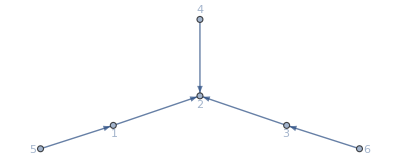

```mathematica
CreateQuiver[tem[[-1,1]]]
```

```mathematica
tem[[-1]]
```

{{{0,1,0,0,-1,0},{-1,0,-1,-1,0,0},{0,1,0,0,0,-1},{0,1,0,0,0,0},{1,0,0,0,0,0},{0,0,1,0,0,0}},{(1+f[1]+f[1] f[4])/(f[5] (1+f[1]+f[1] f[4]+f[6]+f[1] f[6]+f[4] f[6]+2 f[1] f[4] f[6]+f[1] f[3] f[4] f[6]+f[1] f[4]^2 f[6]+f[1] f[3] f[4]^2 f[6])),1/(f[1] f[3] f[4]^2 f[6])(1+f[1]+f[6]+f[1] f[6]+f[1] f[4] f[6]+f[1] f[3] f[4] f[6]) (1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[6]+f[2] f[6]+f[1] f[2] f[6]+f[4] f[6]+f[2] f[4] f[6]+2 f[1] f[2] f[4] f[6]+f[1] f[2] f[3] f[4] f[6]+f[1] f[2] f[4]^2 f[6]+f[1] f[2] f[3] f[4]^2 f[6]) (1+f[1]+f[1] f[4]+f[5]+f[1] f[5]+f[1] f[4] f[5]+f[5] f[6]+f[1] f[5] f[6]+f[4] f[5] f[6]+2 f[1] f[4] f[5] f[6]+f[1] f[3] f[4] f[5] f[6]+f[1] f[4]^2 f[5] f[6]+f[1] f[3] f[4]^2 f[5] f[6]),(1+f[6]+f[4] f[6])/(f[2] (1+f[1]+f[1] f[4]+f[6]+f[1] f[6]+f[4] f[6]+2 f[1] f[4] f[6]+f[1] f[3] f[4] f[6]+f[1] f[4]^2 f[6]+f[1] f[3] f[4]^2 f[6])),f[4]/(1+f[1]+f[1] f[4]+f[6]+f[1] f[6]+f[4] f[6]+2 f[1] f[4] f[6]+f[1] f[3] f[4] f[6]+f[1] f[4]^2 f[6]+f[1] f[3] f[4]^2 f[6]),(f[3] f[4] f[5] f[6])/(1+f[1]+f[1] f[4]+f[5]+f[1] f[5]+f[1] f[4] f[5]+f[5] f[6]+f[1] f[5] f[6]+f[4] f[5] f[6]+2 f[1] f[4] f[5] f[6]+f[1] f[3] f[4] f[5] f[6]+f[1] f[4]^2 f[5] f[6]+f[1] f[3] f[4]^2 f[5] f[6]),(f[1] f[2] f[3] f[4])/(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[6]+f[2] f[6]+f[1] f[2] f[6]+f[4] f[6]+f[2] f[4] f[6]+2 f[1] f[2] f[4] f[6]+f[1] f[2] f[3] f[4] f[6]+f[1] f[2] f[4]^2 f[6]+f[1] f[2] f[3] f[4]^2 f[6])}}

```mathematica
(*sovle the folding condition*)
```

```mathematica
Solve[{tem[[-1,2,1]]==tem[[-1,2,3]],tem[[-1,2,5]]==tem[[-1,2,6]]}]
```

{{f[1]→f[6],f[4]→(-1-f[6])/f[6]},{f[1]→f[6],f[5]→f[2]},{f[4]→0,f[6]→(f[2]+f[1] f[2]-f[5])/f[5]},{f[3]→0,f[6]→(f[2]+f[1] f[2]+f[1] f[2] f[4]-f[5])/((1+f[4]) f[5])},{f[2]→f[5],f[3]→0,f[4]→-1}}

```mathematica
(*only one solution is not singular*)
```

```mathematica
tem[[-1,2]]/.{f[1]->f[6],f[5]->f[2]}//Factor
```

{(1+f[6]+f[4] f[6])/(f[2] (1+2 f[6]+2 f[4] f[6]+f[6]^2+2 f[4] f[6]^2+f[3] f[4] f[6]^2+f[4]^2 f[6]^2+f[3] f[4]^2 f[6]^2)),1/(f[3] f[4]^2 f[6]^2)(1+2 f[6]+f[6]^2+f[4] f[6]^2+f[3] f[4] f[6]^2) (1+f[2]+f[6]+2 f[2] f[6]+f[4] f[6]+2 f[2] f[4] f[6]+f[2] f[6]^2+2 f[2] f[4] f[6]^2+f[2] f[3] f[4] f[6]^2+f[2] f[4]^2 f[6]^2+f[2] f[3] f[4]^2 f[6]^2)^2,(1+f[6]+f[4] f[6])/(f[2] (1+2 f[6]+2 f[4] f[6]+f[6]^2+2 f[4] f[6]^2+f[3] f[4] f[6]^2+f[4]^2 f[6]^2+f[3] f[4]^2 f[6]^2)),f[4]/(1+2 f[6]+2 f[4] f[6]+f[6]^2+2 f[4] f[6]^2+f[3] f[4] f[6]^2+f[4]^2 f[6]^2+f[3] f[4]^2 f[6]^2),(f[2] f[3] f[4] f[6])/(1+f[2]+f[6]+2 f[2] f[6]+f[4] f[6]+2 f[2] f[4] f[6]+f[2] f[6]^2+2 f[2] f[4] f[6]^2+f[2] f[3] f[4] f[6]^2+f[2] f[4]^2 f[6]^2+f[2] f[3] f[4]^2 f[6]^2),(f[2] f[3] f[4] f[6])/(1+f[2]+f[6]+2 f[2] f[6]+f[4] f[6]+2 f[2] f[4] f[6]+f[2] f[6]^2+2 f[2] f[4] f[6]^2+f[2] f[3] f[4] f[6]^2+f[2] f[4]^2 f[6]^2+f[2] f[3] f[4]^2 f[6]^2)}

```mathematica
tem[[-1,2]]/.{f[1]->f[6],f[5]->f[2]}//Factor
```

{(1+f[6]+f[4] f[6])/(f[2] (1+2 f[6]+2 f[4] f[6]+f[6]^2+2 f[4] f[6]^2+f[3] f[4] f[6]^2+f[4]^2 f[6]^2+f[3] f[4]^2 f[6]^2)),1/(f[3] f[4]^2 f[6]^2)(1+2 f[6]+f[6]^2+f[4] f[6]^2+f[3] f[4] f[6]^2) (1+f[2]+f[6]+2 f[2] f[6]+f[4] f[6]+2 f[2] f[4] f[6]+f[2] f[6]^2+2 f[2] f[4] f[6]^2+f[2] f[3] f[4] f[6]^2+f[2] f[4]^2 f[6]^2+f[2] f[3] f[4]^2 f[6]^2)^2,(1+f[6]+f[4] f[6])/(f[2] (1+2 f[6]+2 f[4] f[6]+f[6]^2+2 f[4] f[6]^2+f[3] f[4] f[6]^2+f[4]^2 f[6]^2+f[3] f[4]^2 f[6]^2)),f[4]/(1+2 f[6]+2 f[4] f[6]+f[6]^2+2 f[4] f[6]^2+f[3] f[4] f[6]^2+f[4]^2 f[6]^2+f[3] f[4]^2 f[6]^2),(f[2] f[3] f[4] f[6])/(1+f[2]+f[6]+2 f[2] f[6]+f[4] f[6]+2 f[2] f[4] f[6]+f[2] f[6]^2+2 f[2] f[4] f[6]^2+f[2] f[3] f[4] f[6]^2+f[2] f[4]^2 f[6]^2+f[2] f[3] f[4]^2 f[6]^2),(f[2] f[3] f[4] f[6])/(1+f[2]+f[6]+2 f[2] f[6]+f[4] f[6]+2 f[2] f[4] f[6]+f[2] f[6]^2+2 f[2] f[4] f[6]^2+f[2] f[3] f[4] f[6]^2+f[2] f[4]^2 f[6]^2+f[2] f[3] f[4]^2 f[6]^2)}

```mathematica
Bmn={{0,1,0,0,-1,0},{-1,0,-1,-1,0,0},{0,1,0,0,0,-1},{0,1,0,0,0,0},{1,0,0,0,0,0},{0,0,1,0,0,0}};
yv=f/@Range[6];
```

```mathematica
ml={5,1,5,4,2,1,3};
temtest=Reap[
temp={Bmn,yv};
Sow[temp];
Do[
temp=MutateY[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];(*this get back to the initial quiver of the net of G(4,7)*)
```

Now we perform the mutation for cluster variables

```mathematica
Bm=MatFromQuiver[g0]
```

{{0,-1,-1,1,0,0},{1,0,0,-1,0,0},{1,0,0,-1,-1,1},{-1,1,1,0,0,-1},{0,0,1,0,0,-1},{0,0,-1,1,1,0}}

```mathematica
Graph[{2->1,1->4,4->2,4->3,3->1,5->3,3->6,6->5,6->4},VertexCoordinates->{{2.632270101299922,0.3659725975716903},{2.016435883889035,1.121405098814431},{1.7732239568678387,0.26235895438234447},{0.8590461444320836,0.85904614443208},{0.,0.7554325012427503},{0.6158342174108874,0.}},GraphLayout->"HighDimensionalEmbedding",VertexLabels->"Name"]
```

-Graphics-

```mathematica
mask=Thread@Rule[{ab[1,2,3,7],ab[1,2,6,7],ab[1,5,6,7],ab[4,5,6,7],ab[3,4,5,6],ab[2,3,4,5],ab[1,2,3,4]},1]
```

{ab[1,2,3,7]→1,ab[1,2,6,7]→1,ab[1,5,6,7]→1,ab[4,5,6,7]→1,ab[3,4,5,6]→1,ab[2,3,4,5]→1,ab[1,2,3,4]→1}

```mathematica
{a27,a32,a17,a13,a37,a24}/.rewrite/.mask
```

{ab[1,4,5,6],ab[1,3,4,5],ab[1,2,5,6],ab[1,2,4,5],ab[1,2,3,6],ab[1,2,3,5]}

```mathematica
xv=({a27,a32,a17,a13,a37,a24}/.rewrite/.{ab[a_,cap1[{b_,c_},{d_,e_},{f_,g_}]]:>FB[a,BiTw[b,c],BiTw[d,e],BiTw[f,g]],ab[a__]:>FB[a]}//MTExpand)/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor;
```

```mathematica
{a27,a32,a17,a13,a37,a24}[[{3,1,2,5,1,5,4}]]
```

{a17,a27,a32,a37,a27,a37,a13}

```mathematica
ml={3,1,2,5,1,5,4};
tem=Reap[
temp={Bm,xv};
Sow[temp];
Do[
temp=MutateB[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

6 mutable variables; 0 frozen variables.

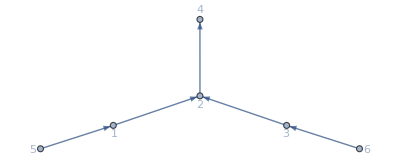

```mathematica
CreateQuiver[tem[[-2,1]]]
```

```mathematica
temcheck=({a41,a62,a51,a13,a33,a24}/.rewrite/.{ab[a_,cap1[{b_,c_},{d_,e_},{f_,g_}]]:>FB[a,BiTw[b,c],BiTw[d,e],BiTw[f,g]],ab[a__]:>FB[a]}//MTExpand)/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor;
```

```mathematica
tem[[-2,2]]/temcheck//Factor
```

{1,1,1,1,1,1}

```mathematica
(*if we further mutate 4, then we get from a11 from a13*)
```

```mathematica
CreateQuiver[tem[[-1,1]]]
```

6 mutable variables; 0 frozen variables.

-Graphics-

```mathematica
tem[[-1,2,4]]-((a11/.rewrite/.{ab[a_,cap1[{b_,c_},{d_,e_},{f_,g_}]]:>FB[a,BiTw[b,c],BiTw[d,e],BiTw[f,g]],ab[a__]:>FB[a]}//MTExpand)/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor)//Factor
```

0

```mathematica
temcheck=({a41,a62,a51,a11,a33,a24}/.rewrite/.{ab[a_,cap1[{b_,c_},{d_,e_},{f_,g_}]]:>FB[a,BiTw[b,c],BiTw[d,e],BiTw[f,g]],ab[a__]:>FB[a]}//MTExpand)/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor;
```

```mathematica
tem[[-1,2]]/temcheck//Factor
```

{1,1,1,1,1,1}

```mathematica
(*cyclic mutation*)
```

```mathematica
ml={2,1,4,3,6,5};
tem=Reap[
temp={Bm,xv};
Sow[temp];
Do[
temp=MutateB[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

6 mutable variables; 0 frozen variables.

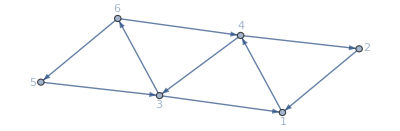

```mathematica
CreateQuiver[tem[[-1,1]]]
```

```mathematica
temcheck=({a21,a33,a11,a14,a31,a25}/.rewrite/.{ab[a_,cap1[{b_,c_},{d_,e_},{f_,g_}]]:>FB[a,BiTw[b,c],BiTw[d,e],BiTw[f,g]],ab[a__]:>FB[a]}//MTExpand)/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor;
```

```mathematica
tem[[-1,2]]/temcheck//Factor
```

{1,1,1,1,1,1}

```mathematica
Det[{{1,0,0,1,1,1},{1,1,0,0,1,1},{1,1,1,0,0,1},{1,1,1,1,0,0},{0,1,1,1,1,0},{0,0,1,1,1,1}}]
```

0

```mathematica
Det[{{1,0,0,0,1,1,1},{1,1,0,0,0,1,1},{1,1,1,0,0,0,1},{1,1,1,1,0,0,0},{0,1,1,1,1,0,0},{0,0,1,1,1,1,0},{0,0,0,1,1,1,1}}]
```

4

```mathematica
Det[{{1,0,0,0,0,0,1,1,1},{1,1,0,0,0,0,0,1,1},{1,1,1,0,0,0,0,0,1},{1,1,1,1,0,0,0,0,0},{0,1,1,1,1,0,0,0,0},{0,0,1,1,1,1,0,0,0},{0,0,0,1,1,1,1,0,0},{0,0,0,0,1,1,1,1,0},{0,0,0,0,0,1,1,1,1}}]
```

4

```mathematica
Det[{{1,0,0,-1,0,0,0},{0,1,0,0,-1,0,0},{0,0,1,0,0,-1,0},{0,0,0,1,0,0,-1},{-1,0,0,0,1,0,0},{0,-1,0,0,0,1,0},{0,0,0,1,1,1,1}}]
```

4

```mathematica
Det[{{1,0,0,-1,0,0,0},{0,1,0,0,-1,0,0},{0,0,1,0,0,-1,0},{0,0,0,1,0,0,-1},{-1,0,0,0,1,0,0},{0,-1,0,0,0,1,0},{0,0,-1,0,0,0,1}}]
```

0

```mathematica
(*E6 quiver*)
```

```mathematica
ml={3,1,2,5,1,5};
tem=Reap[
temp={Bm,xv};
Sow[temp];
Do[
temp=MutateB[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

```mathematica
CreateQuiver[tem[[-1,1]]]
```

6 mutable variables; 0 frozen variables.

-Graphics-

```mathematica
tem[[-1,1]]
```

{{0,1,0,0,-1,0},{-1,0,-1,1,0,0},{0,1,0,0,0,-1},{0,-1,0,0,0,0},{1,0,0,0,0,0},{0,0,1,0,0,0}}

```mathematica
(tem[[-1,2]]//Factor)/.ainfrev
```

{a41,a62,a51,a13,a33,a24}

```mathematica
Bmn={{0,1,0,0,-1,0},{-1,0,-1,1,0,0},{0,1,0,0,0,-1},{0,-1,0,0,0,0},{1,0,0,0,0,0},{0,0,1,0,0,0}};
xvn=tem[[-1,2]];
```

```mathematica
ml=Table[{4,2,1,3,5,6},{i,1,24}]//Flatten;
tem=Reap[
temp={Bmn,xvn};
Sow[temp];
Do[
temp=MutateB[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

```mathematica
temp=(tem[[All,2]]//Factor)/.ainfrev;
```

```mathematica
Export["/Users/windfolgen/Documents/datafile/E6mutate_clustervariables.m",temp];
```

```mathematica
tempp=Import["/Users/windfolgen/Documents/datafile/E6mutate_clustervariables.m"];
```

```mathematica
temp==tempp
```

True

```mathematica
pos=Table[{2,3,5,7}+6*(i-1),{i,1,24}]//Flatten;
%//Length
```

96

```mathematica
alphabet42[[{16,33}]]
```

{a32,a55}

```mathematica
Select[temp,(Not@FreeQ[#,a32]&&Not@FreeQ[#,a55])&]//DeleteDuplicates
```

{{a55,a66,a57,a17,a32,a23},{a55,a66,a45,a17,a32,a23},{a45,a66,a55,a17,a23,a32},{a45,a66,a55,a17,a37,a32}}

```mathematica
(((1+a55)/a32/.ainf)//Factor)/.ainfrev
```

a21

```mathematica
(((1+a62)/a13/a11/.ainf)//Factor)/.ainfrev
```

1

```mathematica
(((a17+a13*a37)/a24/.ainf)//Factor)/.ainfrev
```

a45

```mathematica
(*patterns repeated*)
```

```mathematica
Position[temp,temp[[1]]]
```

{{1},{85}}

```mathematica
Position[temp,temp[[2]]]
```

{{2},{86}}

```mathematica
Position[temp,temp[[3]]]
```

{{3},{87}}

```mathematica
temp[[pos,4]]//DeleteDuplicates//Sort
```

{a11,a12,a13,a14,a15,a16,a17}

```mathematica
temp[[pos,2]]//DeleteDuplicates//Sort
```

{a61,a62,a63,a64,a65,a66,a67}

```mathematica
temp[[pos,1]]//DeleteDuplicates//Sort
```

{a41,a42,a43,a44,a45,a46,a47,a51,a52,a53,a54,a55,a56,a57}

```mathematica
temp[[pos,1]]
```

{a41,a41,a56,a56,a56,a56,a44,a44,a44,a44,a52,a52,a52,a52,a47,a47,a47,a47,a55,a55,a55,a55,a43,a43,a43,a43,a51,a51,a51,a51,a46,a46,a46,a46,a54,a54,a54,a54,a42,a42,a42,a42,a57,a57,a57,a57,a45,a45,a45,a45,a53,a53,a53,a53,a41,a41,a41,a41,a56,a56,a56,a56,a44,a44,a44,a44,a52,a52,a52,a52,a47,a47,a47,a47,a55,a55,a55,a55,a43,a43,a43,a43,a51,a51,a51,a51,a46,a46,a46,a46,a54,a54,a54,a54,a42,a42}

```mathematica
temp[[pos,3]]//DeleteDuplicates//Sort
```

{a41,a42,a43,a44,a45,a46,a47,a51,a52,a53,a54,a55,a56,a57}

```mathematica
temp[[pos,5]]//DeleteDuplicates//Sort
```

{a21,a22,a23,a24,a25,a26,a27,a31,a32,a33,a34,a35,a36,a37}

```mathematica
temp[[pos,6]]//DeleteDuplicates//Sort
```

{a21,a22,a23,a24,a25,a26,a27,a31,a32,a33,a34,a35,a36,a37}

```mathematica
(*another E6 quiver*)
```

```mathematica
xv=({a27,a32,a17,a13,a37,a24}/.rewrite/.{ab[a_,cap1[{b_,c_},{d_,e_},{f_,g_}]]:>FB[a,BiTw[b,c],BiTw[d,e],BiTw[f,g]],ab[a__]:>FB[a]}//MTExpand)/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor;
```

```mathematica
ml={1,6,4,2};
tem=Reap[
temp1={Bm,xv};
Sow[temp1];
Do[
temp1=MutateB[temp1[[1]],temp1[[2]],ml[[i]]];
Sow[temp1];
,{i,1,Length[ml]}];
][[2,1]];
```

6 mutable variables; 0 frozen variables.

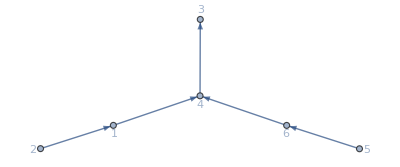

```mathematica
CreateQuiver[tem[[-1,1]]]
```

```mathematica
(tem[[-1,2]]//Factor)/.ainfrev
```

{a55,a21,a17,a66,a37,a45}

```mathematica
{a55,a21,a17,a66,a37,a45}[[{1,4,6,3,2,5}]]
```

{a55,a66,a45,a17,a21,a37}

```mathematica
Position[temp,{a55,a66,a45,a17,a21,a37}]
```

{{31},{115}}

#### Search all 833 clusters in E6

```mathematica
rewrite=//Sort;
```

```mathematica
alphabet42=rewrite[[All,1]]//Sort
```

{a11,a12,a13,a14,a15,a16,a17,a21,a22,a23,a24,a25,a26,a27,a31,a32,a33,a34,a35,a36,a37,a41,a42,a43,a44,a45,a46,a47,a51,a52,a53,a54,a55,a56,a57,a61,a62,a63,a64,a65,a66,a67}

```mathematica
MatE6={{1,0,0,0},{(1+f[5])/f[5],1,0,0},{(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])/(f[1] f[2] f[3] f[4] f[5]),(1+f[2]+f[1] f[2]+f[6]+f[2] f[6]+f[1] f[2] f[6]+f[1] f[2] f[4] f[6]+f[1] f[2] f[3] f[4] f[6])/(f[1] f[2] f[3] f[4] f[6]),1,0},{(1+f[2]+f[1] f[2]+f[1] f[2] f[4])/(f[1] f[2] f[3] f[4] f[5]),((1+f[2]+f[1] f[2]+f[1] f[2] f[4]) (1+f[6]))/(f[1] f[2] f[3] f[4] f[6]),1+f[2]+f[1] f[2]+f[1] f[2] f[4],1},{0,1/(f[3] f[6]),f[2] (1+f[1]+f[1] f[4]),1},{0,0,(f[2] (1+f[2]+f[1] f[2]+f[1] f[2] f[4]))/(1+f[2]),1},{0,0,0,1}};
```

```mathematica
ainf=Thread@Rule[Keys[rewrite],(Values[rewrite]/.{ab[a_,cap1[{b_,c_},{d_,e_},{f_,g_}]]:>FB[a,BiTw[b,c],BiTw[d,e],BiTw[f,g]],ab[a__]:>FB[a]}//MTExpand)/.{FB[a__]:>fB[a,"explicitM"->MatE6]}//Factor];
```

```mathematica
ainfrev=Join[Thread@Rule[Values[ainf]//Factor,Keys[ainf]]]//ReverseSortBy[#,LeafCount]&;
```

```mathematica
Bm={{0,-1,-1,1,0,0},{1,0,0,-1,0,0},{1,0,0,-1,-1,1},{-1,1,1,0,0,-1},{0,0,1,0,0,-1},{0,0,-1,1,1,0}};
xv={a27,a32,a17,a13,a37,a24};
```

```mathematica
assoc=Association[{"ex"->Bm,"xv"->xv}];
```

```mathematica
ClearAll[MutateBR];
MutateBR::usage="MutateB[B,x,k] mutate the exchange matrix B and the corresponding cluster variables x in direction k";
Options[MutateBR]={"rep"->{},"repinv"->{}};
MutateBR[B_,x_,k_,OptionsPattern[]]:=Module[{Bp,xp,l,tem,tem1},
l=B[[All,k]];
xp=x;
Bp=Table[
If[i==k||j==k,-B[[i,j]],
If[B[[i,k]]>0&&B[[k,j]]>0,
B[[i,j]]+B[[i,k]]*B[[k,j]],
If[B[[i,k]]<0&&B[[k,j]]<0,B[[i,j]]-B[[i,k]]*B[[k,j]],B[[i,j]]]
]
]
,{i,1,Length[B]},{j,1,Length[B[[1]]]}];
tem=Join[Table[If[l[[i]]>0,{1,Power[x[[i]],l[[i]]]},{2,Power[x[[i]],-l[[i]]]}],{i,1,Length[l]}],{{1,1},{2,1}}]//GatherBy[#,First]&;
tem1=((Times@@tem[[1,All,2]])+(Times@@tem[[2,All,2]]))/xp[[k]];
xp[[k]]=((tem1/.OptionValue["rep"])//Factor)/.OptionValue["repinv"];
Return[{{Bp,xp},Numerator[Together[xp[[k]]-tem1]](*the exchange relation used*)}];
];
```

```mathematica
ClearAll[BFSExplore];
BFSExplore[initialSeed_,rep_,repinv_]:=Module[{queue,seen,current,mutated,clust,exr,kk=1,graph,graphv,exm},
queue={initialSeed};
seen=<||>;
exr={};
graph={};
graphv={};
exm={};
While[Length[queue]>0&&kk<10000,
current=First[queue];
queue=Rest[queue];
clust=Sort[current["xv"]];
If[!KeyExistsQ[seen,clust],
seen[clust]=current["xv"];
Do[
mutated=MutateBR[current["ex"],current["xv"],k,"rep"->rep,"repinv"->repinv];
AppendTo[queue,Association[Thread@Rule[{"ex","xv"},mutated[[1]]]]];(*new cluster*)
AppendTo[exr,mutated[[2]]](*the exchange relation used to obtain the new cluster*);
AppendTo[graph,UndirectedEdge[Sort[current["xv"]],Sort[mutated[[1,2]]]]](*record the relations between two clusters in graph*);
AppendTo[exm,{current["ex"],current["xv"]}](*record the relations between two clusters in graph*);
graphv=Join[graphv,Thread@UndirectedEdge[current["xv"],mutated[[1,2]]]//DeleteCases[#,UndirectedEdge[a_,a_]]&](*record the change of vertices*),
{k,6}];
];
kk++;
];
{Values[seen],exr,graph,graphv,exm}
];
```

```mathematica
result=BFSExplore[assoc,ainf,ainfrev];
```

```mathematica
Export["/Users/windfolgen/Documents/datafile/heptagon_E6_clusters.m",result];
```

```mathematica
result=Import["/Users/windfolgen/Documents/datafile/heptagon_E6_clusters.m"];
```

```mathematica
result[[1]]//Length
```

833

```mathematica
cycrep=Prepend[Table[(Table[a[i,j]->a[i,If[j+k>7,Mod[j+k,7],j+k]],{i,1,6},{j,1,7}]//Flatten)/.{a[i_,j_]:>ToExpression["a"<>ToString[i]<>ToString[j]]},{k,1,6}],Thread@Rule[alphabet42,alphabet42]];
```

```mathematica
fliprep=Join[Table[Thread@Rule[a[k,#]&/@Range[7],a[k,#]&/@Range[7]/.{a[k,i_]:>a[k,If[8-i>7,Mod[8-i,7],8-i]]}],{k,{1,4,5,6}}]//Flatten,Thread@Rule[a[2,#]&/@Range[7],(a[3,#]&/@Range[7]/.{a[3,i_]:>a[3,If[8-i>7,Mod[8-i,7],8-i]]})],Thread@Rule[a[3,#]&/@Range[7],(a[2,#]&/@Range[7]/.{a[2,i_]:>a[2,If[8-i>7,Mod[8-i,7],8-i]]})]]/.{a[i_,j_]:>ToExpression["a"<>ToString[i]<>ToString[j]]};
```

Example of mutation starting from a given quiver

```mathematica
MatFromQuiver[Graph[{2->1,3->2,4->2,5->3,6->4}]]
```

{{0,-1,0,0,0,0},{1,0,-1,-1,0,0},{0,1,0,0,-1,0},{0,1,0,0,0,-1},{0,0,1,0,0,0},{0,0,0,1,0,0}}

```mathematica
MutateBR[{{0,-1,0,0,0,0},{1,0,-1,-1,0,0},{0,1,0,0,-1,0},{0,1,0,0,0,-1},{0,0,1,0,0,0},{0,0,0,1,0,0}},{a13,a62,a41,a51,a33,a24},2,"rep"->ainf,"repinv"->ainfrev]
```

{{{{0,1,-1,-1,0,0},{-1,0,1,1,0,0},{1,-1,0,0,-1,0},{1,-1,0,0,0,-1},{0,0,1,0,0,0},{0,0,0,1,0,0}},{a13,a16,a41,a51,a33,a24}},-a13-a41 a51+a16 a62}

Check all adjacent pair in our results

```mathematica
adjpair=Import["/Users/windfolgen/Documents/datafile/MHVadjpairtotal.wxf"];
```

```mathematica
adjpair[[1]]//Length(*adjacent two pair*)
```

840

```mathematica
Table[AnyTrue[result[[1]],ContainsAll[#,alphabet42[[adjpair[[1,i]]]]]&],{i,1,Length[adjpair[[1]]]}]//Union
```

{True}

all adjacent pair is contained in some cluster

```mathematica
adjpair3class={Position[#,True,1],Position[#,False,1]}&[Table[AnyTrue[result[[1]],ContainsAll[#,alphabet42[[adjpair[[2,i]]]]]&],{i,1,Length[adjpair[[2]]]}]];
```

```mathematica
Export["/Users/windfolgen/Documents/datafile/adjpair3class.wxf",adjpair3class];
```

```mathematica
adjpair3class[[1]]//Flatten//Length(*first class that are all contained in the same cluster*)
```

11102

```mathematica
adjpair3type1=alphabet42[[#]]&/@(adjpair[[2]][[adjpair3class[[1]]//Flatten]]);
```

```mathematica
FreeQ[adjpair3type1,{a_,b_,b_}|{a_,a_,b_}|{a_,a_,a_}]
```

False

```mathematica
Table[AnyTrue[EdgeList[result[[4]]] /. UndirectedEdge -> List // Sort // DeleteDuplicates, ContainsAll[#, adjpair3type1[[i, {1, 3}]]] &], {i, 1, Length[adjpair3type1]}] // Union
```

{False,True}

```mathematica
Do[
test=(adjpair3type1/.cycrep[[j]])//Sort;
Print[test==(adjpair3type1//Sort)]
,{j,1,6}]
```

True

True

True

«3 more identical outputs»

```mathematica
test=(adjpair3type1/.fliprep)//Sort;
Print[test==(adjpair3type1//Sort)]
```

True

```mathematica
adjpair3class[[2]]//Flatten//Length(*second class that are not all contained in the same cluster*)
```

2394

```mathematica
adjpair3=alphabet42[[#]]&/@(adjpair[[2]][[adjpair3class[[2]]//Flatten]])
```

```mathematica
FreeQ[adjpair3,{a_,b_,b_}|{a_,a_,b_}|{a_,a_,a_}]
```

True

```mathematica
adjpair3c=adjpair3//GatherBy[#,#[[{1,3}]]&]&;
```

```mathematica
adjpair3c//Length
```

770

```mathematica
adjpair3c[[1]]
```

{{a11,a14,a17},{a11,a21,a17},{a11,a37,a17}}

```mathematica
adjpair3c[[1]]/.fliprep
```

{{a17,a14,a11},{a17,a37,a11},{a17,a21,a11}}

```mathematica
exlist=(result[[2]]//DeleteDuplicates);(*all exchange relations used to check*)
```

```mathematica
exlist//Length
```

385

```mathematica
plist=Table[Position[ContainsExactly[Variables[#],adjpair3c[[i]]//Flatten//Union]&/@(exlist),True,1]//Flatten,{i,1,Length[adjpair3c]}];
```

```mathematica
FreeQ[plist,{}]
```

True

```mathematica
exlist[[79]]
```

-a14+a11 a17-a21 a37

```mathematica
plist
```

{{79},{181},{306},{370},{243},{380},{332},{374},{289},{296},{224},{126},{95},{335},{235},{319},{357},{82},{75},{238},{380},{382},{299},{345},{302},{118},{340},{180},{278},{368},{112},{329},{254},{202},{341},{216},{350},{110},{114},{266},{118},{53},{171},{91},{160},{11},{4},{92},{54},{33},{231},{72},{9},{150},{23},{36},{13},{40},{75},{65},{291},{227},{207},{141},{244},{11},{89},{59},{188},{208},{225},{293},{17},{84},{165},{107},{169},{290},{266},{163},{291},{373},{328},{285},{384},{331},{337},{383},{339},{385},{183},{178},{234},{376},{217},{378},{61},{122},{65},{68},{331},{263},{277},{199},{279},{20},{124},{71},{154},{264},{318},{255},{196},{97},{14},{109},{317},{149},{163},{238},{20},{80},{3},{34},{32},{79},{148},{38},{189},{87},{230},{81},{48},{8},{22},{168},{31},{18},{114},{68},{206},{146},{303},{103},{348},{229},{10},{280},{73},{203},{350},{308},{292},{149},{144},{7},{206},{327},{175},{262},{338},{192},{215},{218},{269},{260},{13},{60},{123},{18},{108},{83},{262},{198},{326},{21},{102},{223},{253},{363},{132},{115},{357},{309},{169},{316},{24},{135},{21},{6},{28},{39},{88},{186},{49},{30},{77},{164},{110},{19},{61},{66},{226},{15},{305},{287},{222},{361},{39},{247},{375},{283},{128},{268},{358},{40},{317},{159},{50},{170},{333},{342},{281},{355},{375},{220},{44},{275},{258},{139},{351},{182},{290},{31},{142},{27},{85},{1},{35},{56},{44},{157},{10},{57},{120},{161},{12},{93},{122},{82},{16},{246},{228},{347},{304},{276},{369},{343},{372},{352},{230},{295},{231},{311},{336},{312},{226},{246},{276},{197},{190},{2},{101},{41},{117},{179},{95},{42},{17},{195},{121},{113},{50},{7},{2},{25},{151},{78},{37},{250},{172},{152},{233},{254},{234},{94},{167},{74},{142},{83},{288},{242},{204},{354},{78},{322},{213},{131},{294},{96},{9},{196},{364},{69},{16},{135},{261},{346},{273},{367},{213},{201},{119},{315},{111},{324},{165},{22},{360},{63},{144},{15},{55},{45},{143},{137},{119},{252},{5},{136},{224},{232},{62},{217},{116},{162},{108},{170},{228},{147},{156},{90},{187},{86},{5},{52},{112},{47},{166},{14},{76},{70},{24},{27},{80},{85},{101},{236},{129},{344},{340},{274},{325},{251},{225},{294},{310},{353},{378},{260},{176},{358},{76},{240},{181},{103},{37},{265},{106},{185},{4},{51},{29},{105},{183},{111},{43},{104},{109},{115},{267},{182},{336},{184},{227},{327},{288},{356},{313},{381},{382},{284},{379},{298},{81},{77},{232},{359},{127},{318},{366},{93},{121},{155},{337},{198},{261},{191},{301},{193},{53},{274},{99},{330},{335},{268},{47},{211},{245},{48},{133},{292},{167},{270},{124},{6},{55},{236},{46},{145},{89},{51},{174},{125},{202},{139},{311},{256},{140},{235},{173},{123},{69},{64},{373},{305},{147},{356},{286},{221},{148},{265},{307},{371},{209},{349},{150},{161},{195},{239},{341},{309},{360},{321},{263},{333},{369},{191},{334},{271},{332},{284},{212},{200},{100},{259},{107},{203},{94},{194},{23},{19},{116},{67},{3},{102},{45},{46},{26},{98},{180},{99},{241},{158},{178},{96},{43},{100},{84},{73},{239},{159},{312},{155},{306},{88},{90},{307},{248},{249},{92},{174},{210},{297},{310},{359},{255},{324},{376},{269},{194},{351},{113},{270},{207},{287},{347},{286},{177},{257},{299},{212},{214},{130},{104},{211},{8},{62},{97},{132},{176},{12},{74},{64},{383},{342},{197},{334},{365},{282},{171},{325},{241},{362},{366},{256},{319},{166},{168},{164},{267},{308},{364},{321},{71},{1},{25},{129},{26},{58},{59},{29},{210},{134},{126},{128},{295},{127},{209},{133},{216},{60},{63},{67},{328},{146},{242},{313},{177},{153},{38},{106},{248},{320},{329},{258},{42},{245},{259},{173},{36},{316},{162},{240},{277},{338},{346},{301},{365},{377},{374},{379},{214},{300},{293},{233},{353},{349},{72},{120},{140},{66},{70},{184},{339},{199},{192},{281},{343},{273},{193},{282},{272},{54},{188},{280},{49},{172},{52},{125},{134},{219},{141},{285},{175},{222},{304},{204},{221},{153},{237},{154},{34},{223},{35},{41},{143},{145},{58},{205},{385},{279},{326},{355},{190},{367},{271},{377},{272},{370},{189},{348},{186},{250},{187},{371},{320},{323},{264},{32},{28},{56},{151},{137},{344},{98},{205},{289},{345},{215},{283},{372},{131},{200},{300},{138},{243},{87},{229},{247},{322},{86},{185},{249},{323},{278},{91},{253},{275},{117},{315},{251},{158},{314},{296},{302},{218},{220},{352},{201},{298},{130},{138},{33},{208},{30},{57},{152},{136},{105},{297},{219},{244},{384},{303},{361},{354},{156},{381},{257},{237},{368},{160},{363},{157},{179},{252},{330},{362},{314}}

```mathematica
Table[AnyTrue[EdgeList[result[[4]]] /. UndirectedEdge -> List // Sort // DeleteDuplicates, ContainsAll[#, adjpair3[[i, {1, 3}]]] &], {i, 1, Length[adjpair3]}] // Union
```

{True}

```mathematica
letter2num=Thread@Rule[alphabet42,Range[42]];
```

```mathematica
Export["/Users/windfolgen/Documents/datafile/hep_letter2num.wxf",letter2num];
```

```mathematica
adjpair3c[[1]]/.letter2num
```

{{1,4,7},{1,8,7},{1,21,7}}

```mathematica
adjpair3c[[1]]
```

{{a11,a14,a17},{a11,a21,a17},{a11,a37,a17}}

```mathematica
Position[adjpair3c,Reverse/@adjpair3c[[1]]]
```

{{126}}

all length-3 adjacent pairs are type a⊗x⊗a'

Now we find for all the second type, whether there are first type ones coincide the begin and the end.

```mathematica
Table[Cases[adjpair3type1,{adjpair3c[[i,1,1]],_,adjpair3c[[i,1,3]]},1],{i,1,Length[adjpair3c]}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

So there is no coincidence, this is important!

```mathematica
Export["/Users/windfolgen/Documents/datafile/MHVtripletadjpair3cn.wxf",adjpair3c/.letter2num];
```

```mathematica
test=adjpair3c[[All,1,{1,3}]]//Sort;
test==(Reverse/@test//Sort)
```

True

```mathematica
Do[
test=Sort/@(adjpair3c/.cycrep[[j]])//Sort;
Print[test==((Sort/@adjpair3c)//Sort)]
,{j,1,6}]
```

True

True

True

«3 more identical outputs»

```mathematica
test=Sort/@(adjpair3c/.fliprep)//Sort;
Print[test==((Sort/@adjpair3c)//Sort)]
```

True

Now we remove the dihedral symmetry

```mathematica
adjpair3s={adjpair3c[[1]]};
temp=Complement[(Sort/@adjpair3c)//Sort,Sort/@(Join[#,#/.fliprep]&[Join@@Table[adjpair3s/.cycrep[[i]],{i,1,7}]])//Sort]//Sort;
kk=1;
While[temp=!={}&&kk<1000,
adjpair3s=Join[adjpair3s,{temp[[1]]}];
temp=Complement[temp,Sort/@Join[#,#/.fliprep]&[(Join@@Table[{temp[[1]]}/.cycrep[[i]],{i,1,7}])//Sort]]//Sort;
kk=kk+1;
];
```

```mathematica
adjpair3s=adjpair3s//Select[#,Length[#]>1&]&;
```

```mathematica
adjpair3s//Length
```

52

```mathematica
Export["/Users/windfolgen/Documents/datafile/MHVtripletadjpair3s.wxf",adjpair3s/.letter2num];
```

The total coefficients we extract from the physical result

```mathematica
coeff={{1,{{1,-1,-1}}},{2,{{1,-1}}},{3,{{1,-1}}},{4,{{1,-1}}},{5,{{1,-1}}},{6,{{1,-1}}},{7,{{1,-1}}},{8,{{1,-1}}},{9,{{1,-1}}},{10,{{1,-1}}},{11,{{1,1}}},{12,{{1,-1}}},{13,{{1,1}}},{15,{{1,-1,1}}},{16,{{1,-1,1}}},{17,{{1,-1,1}}},{19,{{1,-1,-1}}},{21,{{1,1,-1}}},{22,{{1,1,-1}}},{23,{{1,-1,-1}}},{24,{{1,-1,-1}}},{25,{{1,1,-1}}},{26,{{1,-1,1}}},{27,{{1,-1,-1}}},{28,{{1,1,-1}}},{29,{{1,-1,-1}}},{30,{{1,1,-1}}},{31,{{1,1,-1}}},{33,{{1,1,-1,-1}}},{34,{{1,-1,-1,1}}},{37,{{1,1,-1,-1}}},{38,{{1,-1,-1,1}}},{39,{{1,1,1,-1}}},{41,{{1,-1,-1,1}}},{42,{{1,-1,1,1}}},{43,{{1,-1,-1,1}}},{45,{{1,-1,1,-1}}},{46,{{1,-1,1,-1}}},{50,{{1,1,-1,-1,-1}}},{51,{{1,1,1,-1,-1}}},{14,{{1,-1,-1}}},{18,{{1,1,-1}}},{20,{{1,-1,1}}},{32,{{1,1,1}}},{35,{{1,1,-1,-1}}},{36,{{1,-1,1,-1}}},{40,{{1,-1,1,1}}},{44,{{1,-1,1,1}}},{47,{{1,-1,1,1}}},{48,{{1,-1,1,1}}},{49,{{1,1,-1,1,-1}}},{52,{{1,-1,1,-1,1}}}};
```

```mathematica
(Times@@alphabet42[[adjpair3s[[#[[1]]]][[1,{1,3}]]]])&/@coeff
```

{a11 a17,a11 a36,a11 a32,a21 a22,a21 a27,a21 a51,a21 a47,a12 a21,a16 a21,a22 a41,a41 a53,a21 a51,a46 a51,a11 a55,a11 a44,a21 a56,a21 a42,a21 a54,a21 a44,a27 a41,a14 a41,a34 a41,a23 a51,a15 a51,a34 a51,a15 a61,a22 a61,a31 a61,a11 a42,a11 a52,a17 a41,a41 a45,a41 a55,a17 a51,a45 a51,a51 a55,a26 a61,a35 a61,a41 a52,a42 a51,a11 a65,a21 a67,a21 a61,a61 a63,a21 a63,a21 a65,a41 a64,a51 a64,a44 a61,a54 a61,a11 a63,a16 a61}

```mathematica
alphabet42[[#]]&/@(Sort[adjpair3s[[#[[1]]]]][[All,2]])&/@coeff
```

{{a14,a21,a37},{a21,a46},{a22,a53},{a11,a34},{a17,a33},{a24,a62},{a25,a66},{a31,a57},{a36,a41},{a26,a67},{a26,a62},{a24,a62},{a24,a67},{a21,a34,a53},{a22,a34,a46},{a11,a14,a33},{a14,a17,a34},{a31,a33,a52},{a34,a36,a46},{a13,a16,a33},{a21,a33,a46},{a21,a26,a46},{a13,a16,a35},{a22,a35,a53},{a22,a24,a53},{a12,a47,a57},{a12,a42,a47},{a12,a52,a57},{a14,a22,a34,a37},{a14,a21,a25,a31},{a13,a21,a33,a36},{a13,a23,a33,a43},{a13,a21,a26,a36},{a13,a24,a27,a37},{a13,a27,a35,a37},{a13,a24,a32,a53},{a12,a32,a36,a57},{a12,a23,a27,a47},{a21,a23,a31,a33,a36},{a22,a24,a27,a32,a37},{a14,a46,a56},{a11,a41,a46},{a17,a52,a57},{a12,a42,a52},{a14,a31,a34,a52},{a14,a33,a36,a46},{a13,a23,a26,a43},{a13,a32,a35,a53},{a12,a32,a36,a42},{a12,a23,a27,a52},{a14,a22,a25,a31,a34},{a12,a23,a27,a32,a36}}

```mathematica
exchange=((Times@@alphabet42[[adjpair3s[[#[[1]]]][[1,{1,3}]]]])-(Plus@@NumeratorDenominator[Times@@Thread@Power[alphabet42[[#]]&/@(Sort[adjpair3s[[#[[1]]]]][[All,2]]),#[[2,1]]]]))&/@coeff
```

{-a14+a11 a17-a21 a37,-a21+a11 a36-a46,-a22+a11 a32-a53,-a11+a21 a22-a34,-a17+a21 a27-a33,-a24+a21 a51-a62,-a25+a21 a47-a66,a12 a21-a31-a57,a16 a21-a36-a41,-a26+a22 a41-a67,-1+a41 a53-a26 a62,-a24+a21 a51-a62,-1+a46 a51-a24 a67,-a34-a21 a53+a11 a55,-a34+a11 a44-a22 a46,-a14-a11 a33+a21 a56,-a14-a17 a34+a21 a42,-a31 a33-a52+a21 a54,-a34 a36+a21 a44-a46,-a13-a16 a33+a27 a41,-a21+a14 a41-a33 a46,-a21 a26+a34 a41-a46,-a16-a13 a35+a23 a51,-a22+a15 a51-a35 a53,-a22 a24+a34 a51-a53,-a12-a47 a57+a15 a61,-a12 a42-a47+a22 a61,-a12 a52-a57+a31 a61,-a14 a22-a34 a37+a11 a42,-a21 a25-a14 a31+a11 a52,-a13 a21-a33 a36+a17 a41,-a23 a33-a13 a43+a41 a45,-a13 a21 a26-a36+a41 a55,-a24 a27-a13 a37+a17 a51,-a27-a13 a35 a37+a45 a51,-a24 a32-a13 a53+a51 a55,-a12 a36-a32 a57+a26 a61,-a12 a27-a23 a47+a35 a61,-a21 a23-a31 a33 a36+a41 a52,-a22 a24 a27-a32 a37+a42 a51,-a14-a46 a56+a11 a65,-a11 a41-a46+a21 a67,-a52-a17 a57+a21 a61,-1-a12 a42 a52+a61 a63,-a14 a31-a34 a52+a21 a63,-a14 a36-a33 a46+a21 a65,-a23-a13 a26 a43+a41 a64,-a32-a13 a35 a53+a51 a64,-a32-a12 a36 a42+a44 a61,-a23-a12 a27 a52+a54 a61,-a14 a22 a31-a25 a34+a11 a63,-a23 a32-a12 a27 a36+a16 a61}

```mathematica
ContainsAll[result[[2]],exchange]
```

True

```mathematica
AnyTrue[result[[1]],ContainsAll[#,{a11,a41,a51}]&]
```

True

```mathematica
AnyTrue[result[[4]],ContainsAll[List@@#,{a11,a51}]&]
```

False

find all quivers isomorphic to E6 Dynkin diagram

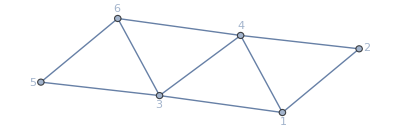

```mathematica
CreateQuiver[result[[-1,1]][[1]],"outputlevel"->0]//UndirectedGraph
```

```mathematica
ClearAll[AllIsomorphicQ];
AllIsomorphicQ[list_,exp_]:=AllTrue[list,IsomorphicGraphQ[exp,#]&];
```

```mathematica
graph={Graph[{1->6,6->5,6->4,2->4,3->5}],Graph[{1->6,6->5,6->4,4->2,5->3}],Graph[{1->6,5->6,4->6,2->4,3->5}],Graph[{1->6,5->6,4->6,4->2,5->3}],Graph[{6->1,6->5,6->4,2->4,3->5}],Graph[{6->1,6->5,6->4,4->2,5->3}],Graph[{6->1,5->6,4->6,2->4,3->5}],Graph[{6->1,5->6,4->6,4->2,5->3}]};
```

```mathematica
E6part=Table[Select[result[[-1]],IsomorphicGraphQ[graph[[i]],CreateQuiver[#[[1]],"outputlevel"->0]]&]//DeleteDuplicates,{i,1,8}]//Flatten[#,1]&;
```

```mathematica
E6part//Length
```

56

```mathematica
E6partall=Select[result[[-1]],IsomorphicGraphQ[graph[[1]]//UndirectedGraph,CreateQuiver[#[[1]],"outputlevel"->0]//UndirectedGraph]&]//DeleteDuplicates;
```

```mathematica
E6partall//Length
```

224

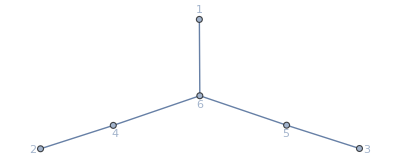

```mathematica
Graph[{1<->6,6<->5,6<->4,2<->4,3<->5},GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]
```

```mathematica
FindGraphIsomorphism[Graph[{1<->6,6<->5,6<->4,2<->4,3<->5}],CreateQuiver[E6partall[[-1]][[1]],"outputlevel"->0]//UndirectedGraph]
```

{<|1→5,6→4,5→3,4→2,2→1,3→6|>}

```mathematica
asso=<|1->5,6->4,5->3,4->2,2->1,3->6|>;
```

```mathematica
E6partall[[-1,2]][[asso/@Range[6]]]
```

{a11,a26,a31,a41,a46,a67}

```mathematica
E6sort=Reap[
Do[
map=FindGraphIsomorphism[Graph[{1<->6,6<->5,6<->4,2<->4,3<->5}],CreateQuiver[E6partall[[i,1]],"outputlevel"->0]//UndirectedGraph][[1]];
Sow[E6partall[[i,2]][[map/@Range[6]]]]
,{i,1,Length[E6partall]}]
][[2,1]];
```

```mathematica
E6sort[[All,1]]//DeleteDuplicates
```

{a13,a17,a15,a11,a12,a16,a14}

```mathematica
E6sort[[All,6]]//DeleteDuplicates
```

{a64,a66,a62,a61,a67,a65,a63}

```mathematica
E6sort[[All,4]]//DeleteDuplicates//Sort
```

{a41,a42,a43,a46,a47,a52,a53,a54,a55,a56,a57}

```mathematica
E6sort[[All,5]]//DeleteDuplicates//Sort
```

{a41,a43,a44,a45,a46,a47,a51,a52,a53,a56,a57}

```mathematica
E6sort[[All,2]]//DeleteDuplicates//Sort
```

{a21,a22,a23,a24,a25,a26,a27,a31,a32,a33,a34,a35,a36,a37}

```mathematica
E6sort[[All,3]]//DeleteDuplicates//Sort
```

{a22,a23,a24,a25,a26,a31,a32,a33,a34,a35,a36,a37}

Draw the clusters

```mathematica
label=Thread@Rule[result[[3]]/.UndirectedEdge->List//Flatten[#,1]&//DeleteDuplicates,Range[833]];
```

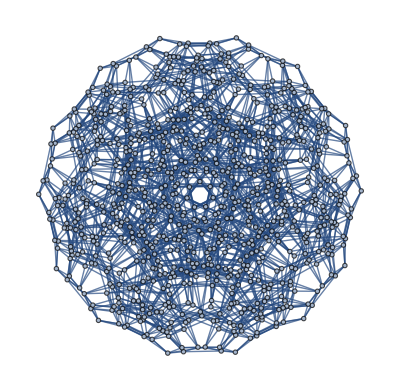

```mathematica
Graph[result[[3]]/.label//DeleteDuplicates[#,(#1===#2||#1===(#2//Reverse))&]&]
```

```mathematica
ColorData[3,"ColorList"]
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]}

```mathematica
Graph3D[result[[4]]//DeleteDuplicates[#,(#1===#2||#1===(#2//Reverse))&]&,VertexStyle->Join[Thread@Rule[{a11,a12,a13,a14,a15,a16,a17},ColorData[3,2]],Thread@Rule[{a21,a22,a23,a24,a25,a26,a27,a31,a32,a33,a34,a35,a36,a37},ColorData[3,6]],Thread@Rule[{a41,a42,a43,a44,a45,a46,a47,a51,a52,a53,a54,a55,a56,a57},ColorData[3,4]],Thread@Rule[{a61,a62,a63,a64,a65,a66,a67},ColorData[3,8]]],GraphLayout->"HighDimensionalEmbedding",VertexLabels->"Name"]
```

-Graphics3D-

Now we study the exchange relations used

```mathematica
Unprotect[S];ClearAll[S];Protect[W];(*definition for symbol and letters*)
S[a___,Times[x_,y__],b___]:=S[a,x,b]+S[a,Times[y],b];
S[a___,Power[x_,n_],b___]:=n*S[a,x,b];
S[___,0|-1,___]:=0;
Protect[S];
Unprotect[d];
ClearAll[Wedge,d];
Protect[d];
Wedge[x_,x_]:=0;
Wedge[Plus[x_,y__],z_]:=Wedge[x,z]+Wedge[Plus[y],z];
Wedge[x_,Plus[y_,z__]]:=Wedge[x,y]+Wedge[x,Plus[z]];
(*Wedge[Times[x__/;(FreeQ[{x},d[_]]),y__],p_]:=Times[x]*Wedge[Times[y],p];
Wedge[p_,Times[x__/;(FreeQ[{x},d[_]]),y__]]:=Times[x]*Wedge[p,Times[y]];
Wedge[Times[y__,x__/;(FreeQ[{x},d[_]])],p_]:=Times[x]*Wedge[Times[y],p];
Wedge[p_,Times[y__,x__/;(FreeQ[{x},d[_]])]]:=Times[x]*Wedge[p,Times[y]];*)
Wedge[Times[x__,d[y_]],p_]:=Times[x]*Wedge[d[y],p];
Wedge[p_,Times[x__,d[y_]]]:=Times[x]*Wedge[p,d[y]];
Wedge[a_,b_]/;(!OrderedQ[{a,b}]):=Signature[{a,b}]*Wedge[Sequence@@Sort[{a,b}]];
```

```mathematica
alphabet42=rewrite//Keys
```

{a11,a12,a13,a14,a15,a16,a17,a21,a22,a23,a24,a25,a26,a27,a31,a32,a33,a34,a35,a36,a37,a41,a42,a43,a44,a45,a46,a47,a51,a52,a53,a54,a55,a56,a57,a61,a62,a63,a64,a65,a66,a67}

```mathematica
basis=Table[Wedge[alphabet42[[i]],alphabet42[[j]]],{i,1,42},{j,i+1,42}]//Flatten;
%//Length
```

861

```mathematica
Select[result[[2]],(Not@FreeQ[#,a11]&&Not@FreeQ[#,a17]&&Not@FreeQ[#,a14]&)]//DeleteDuplicates
```

{-a14+a11 a17-a21 a37}

```mathematica
Position[result[[2]],-a14+a11 a17-a21 a37]
```

{{279},{585},{753},{765},{1347},{1359},{1605},{2451}}

```mathematica
result[[3]][[279]]
```

{a14,a17,a21,a24,a33,a37}<->{a11,a14,a21,a24,a33,a37}

```mathematica
Select[result[[2]],(Not@FreeQ[#,a11]&&Not@FreeQ[#,a21]&&Not@FreeQ[#,a37]&)]//DeleteDuplicates
Select[result[[2]],(Not@FreeQ[#,a25]&&Not@FreeQ[#,a21]&&Not@FreeQ[#,a37]&)]//DeleteDuplicates
```

{-a14+a11 a17-a21 a37,-a11 a24 a33-a21 a37+a14 a62,-a25 a34-a15 a21 a37+a11 a66}

{-a17 a25 a34-a21 a37+a14 a66,-a25 a34-a15 a21 a37+a11 a66}

```mathematica
Select[result[[2]],(Not@FreeQ[#,a25]&&Not@FreeQ[#,a34]&)]//DeleteDuplicates
```

{-a17 a25 a34-a21 a37+a14 a66,-a11+a14 a15-a25 a34,-a25 a34-a15 a21 a37+a11 a66,-a14 a22 a31-a25 a34+a11 a63,-a22 a31-a12 a25 a34+a15 a63}

```mathematica
(-a25 a34-a15 a21 a37+a11 a66)*a14-(-a17 a25 a34-a21 a37+a14 a66)a11//Factor
```

-a14 a25 a34+a11 a17 a25 a34+a11 a21 a37-a14 a15 a21 a37

```mathematica
Select[result[[2]],(Not@FreeQ[#,a15]&&Not@FreeQ[#,a34]&)]//DeleteDuplicates
```

{a15 a24-a34-a53,-a34-a15 a37 a55+a53 a66,-a53-a15 a55+a34 a64,-a22+a15 a42-a34 a47,-a15-a22+a34 a35,-a26 a34-a15 a55+a53 a57,-a15 a37-a34 a47+a22 a66,-a11-a15 a21+a34 a43,-a11+a14 a15-a25 a34,-a25 a34-a15 a21 a37+a11 a66,-a22 a26-a12 a34+a15 a44,-a15-a12 a34+a22 a57,-a11 a26-a31 a34+a15 a46,-a15 a21-a31 a34+a11 a57,-a22 a31-a12 a25 a34+a15 a63}

```mathematica
Select[result[[2]],(Not@FreeQ[#,a66]&&Not@FreeQ[#,a34]&&Not@FreeQ[#,a25]&)]//DeleteDuplicates
```

{-a17 a25 a34-a21 a37+a14 a66,-a25 a34-a15 a21 a37+a11 a66}

6 mutable variables; 0 frozen variables.

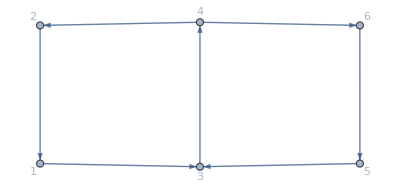

```mathematica
CreateQuiver[result[[5]][[279]]]
```

```mathematica
sys=CoefficientArrays[result[[2]]/.{-a_-b_+c_:>S[c/a,b/a]}/.S->Wedge,basis][[2]]//RowReduce//DeleteCases[#,{0..}]&;
```

```mathematica
sys//Dimensions
```

{132,861}

```mathematica
(*check whether the relations are equivalent*)
```

```mathematica
test=Import["/Users/windfolgen/Documents/datafile/heptagon_dlogrels.m"];
```

```mathematica
testsys=CoefficientArrays[test/.{Rule[a_,b_]:>a-b}/.{dlog[{W[a_],W[b_]}]:>Wedge[alphabet42[[a]],alphabet42[[b]]]},basis][[2]]//Normal;
```

```mathematica
Join[sys,testsys]//MatrixRank
```

132

folding E6 into F4

```mathematica
{a21,a22,a23,a24,a25,a26,a27}/.ainf/.{f[6]->f[1],f[5]->f[2]}
```

{(1+f[2])/(f[1] f[2] f[3]),(f[2] (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]))/f[1],f[1] f[3],(1+f[2]+f[1] f[2]+f[1] f[2] f[4])/(f[1] f[2]^2 f[3] f[4]),(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])/(f[1] f[3]),(1+f[1]) f[2] f[3],(1+f[1]+f[1] f[4])/(f[2] f[4])}

```mathematica
{a37,a31,a32,a33,a34,a35,a36}/.ainf/.{f[6]->f[1],f[5]->f[2]}
```

{(1+f[2])/(f[1] f[2] f[3]),(f[2] (1+f[1]+f[2]+2 f[1] f[2]+f[1]^2 f[2]+f[1]^2 f[2] f[4]+f[1]^2 f[2] f[3] f[4]))/f[1],f[1] f[3],(1+f[2]+f[1] f[2]+f[1] f[2] f[4])/(f[1] f[2]^2 f[3] f[4]),(1+f[2]+f[1] f[2]+f[1] f[2] f[4]+f[1] f[2] f[3] f[4])/(f[1] f[3]),(1+f[1]) f[2] f[3],(1+f[1]+f[1] f[4])/(f[2] f[4])}

Now we try to keep the shape of E6 and perform a set of mutations:

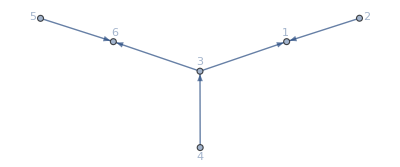

```mathematica
E6part[[1,1]]//CreateQuiver
```

```mathematica
Bmn=E6part[[1,1]]
xv=E6part[[1,2]]
```

{{0,-1,-1,0,0,0},{1,0,0,0,0,0},{1,0,0,-1,0,1},{0,0,1,0,0,0},{0,0,0,0,0,1},{0,0,-1,0,-1,0}}

{a55,a21,a64,a13,a37,a45}

```mathematica
temp={Bmn,xv};
```

```mathematica
ml=Table[{4,3,2,5,1,6},{i,1,24}]//Flatten;
tem=Reap[
temp={{Bmn,xv},1};
Sow[temp];
Do[
temp=MutateBR[temp[[1,1]],temp[[1,2]],ml[[i]],"rep"->ainf,"repinv"->ainfrev];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

```mathematica
tem[[All,1,2]]//Length
```

145

```mathematica
tem[[All,1,2]][[All,4]]//DeleteDuplicates
```

{a13,a15,a17,a12,a14,a16,a11}

```mathematica
tem[[All,1,2]][[All,3]]//DeleteDuplicates
```

{a64,a66,a61,a63,a65,a67,a62}

```mathematica
tem[[All,1,2]][[All,1]]//DeleteDuplicates//Sort
```

{a41,a42,a43,a44,a45,a46,a47,a51,a52,a53,a54,a55,a56,a57}

```mathematica
tem[[All,1,2]][[All,6]]//DeleteDuplicates//Sort
```

{a41,a42,a43,a44,a45,a46,a47,a51,a52,a53,a54,a55,a56,a57}

```mathematica
tem[[All,1,2]][[All,2]]//DeleteDuplicates//Sort
```

{a21,a22,a23,a24,a25,a26,a27,a31,a32,a33,a34,a35,a36,a37}

```mathematica
tem[[All,1,2]][[All,5]]//DeleteDuplicates//Sort
```

{a21,a22,a23,a24,a25,a26,a27,a31,a32,a33,a34,a35,a36,a37}

```mathematica
ml=Table[{4,2,5,3,1,6},{i,1,24}]//Flatten;
tem=Reap[
temp={{Bmn,xv},1};
Sow[temp];
Do[
temp=MutateBR[temp[[1,1]],temp[[1,2]],ml[[i]],"rep"->ainf,"repinv"->ainfrev];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

```mathematica
tem[[All,1,2]][[All,4]]//DeleteDuplicates//Sort
```

{a11,a12,a13,a14,a15,a16,a17}

```mathematica
tem[[All,1,2]][[All,3]]//DeleteDuplicates//Sort
```

{a61,a62,a63,a64,a65,a66,a67}

```mathematica
tem[[All,1,2]][[All,1]]//DeleteDuplicates//Sort
```

{a41,a42,a43,a44,a45,a46,a47,a51,a52,a53,a54,a55,a56,a57}

```mathematica
tem[[All,1,2]][[All,6]]//DeleteDuplicates//Sort
```

{a41,a42,a43,a44,a45,a46,a47,a51,a52,a53,a54,a55,a56,a57}

```mathematica
tem[[All,1,2]][[All,2]]//DeleteDuplicates//Sort
```

{a21,a22,a23,a24,a25,a26,a27,a31,a32,a33,a34,a35,a36,a37}

```mathematica
tem[[All,1,2]][[All,5]]//DeleteDuplicates//Sort
```

{a21,a22,a23,a24,a25,a26,a27,a31,a32,a33,a34,a35,a36,a37}

```mathematica
ml=Table[{1,6,3,2,4,5},{i,1,24}]//Flatten;
tem=Reap[
temp={{Bmn,xv},1};
Sow[temp];
Do[
temp=MutateBR[temp[[1,1]],temp[[1,2]],ml[[i]],"rep"->ainf,"repinv"->ainfrev];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

```mathematica
tem[[All,1,2]][[All,4]]//DeleteDuplicates//Sort
```

{a11,a12,a13,a14,a15,a16,a17}

```mathematica
tem[[All,1,2]][[All,3]]//DeleteDuplicates//Sort
```

{a61,a62,a63,a64,a65,a66,a67}

```mathematica
tem[[All,1,2]][[All,1]]//DeleteDuplicates//Sort
```

{a41,a42,a43,a44,a45,a46,a47,a51,a52,a53,a54,a55,a56,a57}

```mathematica
tem[[All,1,2]][[All,6]]//DeleteDuplicates//Sort
```

{a41,a42,a43,a44,a45,a46,a47,a51,a52,a53,a54,a55,a56,a57}

```mathematica
tem[[All,1,2]][[All,2]]//DeleteDuplicates//Sort
```

{a21,a22,a23,a24,a25,a26,a27,a31,a32,a33,a34,a35,a36,a37}

```mathematica
tem[[All,1,2]][[All,5]]//DeleteDuplicates//Sort
```

{a21,a22,a23,a24,a25,a26,a27,a31,a32,a33,a34,a35,a36,a37}

### A3

```mathematica
ClearAll[g];
g=Graph[{1->2,3->2,3->4,4->5,5->3,6->5,2->6,6->7,7->1,8->7,1->8,8->9,9->1,10->9,2->10,10->11,11->3,4->11},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,Null],5->Button[5,Null],6->Button[6,Null],7->Button[7,Null],8->Button[8,Null],9->Button[9,Null],10->Button[10,Null],11->Button[11,Null]},VertexCoordinates->{1->{0,1},2->{1/2,0},3->{0,-1},4->{0,-2},5->{1,-1},6->{1,0},7->{1,1},8->{0,2},9->{-1,1},10->{-1,0},11->{-1,-1}},GraphLayout->"GridEmbedding"];
Dynamic[g]
```

```mathematica
(*triple term identity*)
```

```mathematica
(GramM[{1},{3}]^2GramM[{1,3,4}]+GramM[{1}]GramM[{1,3},{3,4}]^2)/GramM[{1,3}]//Factor
```

a[1,4]^2 a[3,3]-2 a[1,3] a[1,4] a[3,4]+a[1,3]^2 a[4,4]

```mathematica
GramM[{1}]GramM[{3,4}]-GramM[{1,3,4}]//Factor
```

a[1,4]^2 a[3,3]-2 a[1,3] a[1,4] a[3,4]+a[1,3]^2 a[4,4]

```mathematica
krep/.{Subscript[x, _]->0}
```

{k1·k1→0,k1·p1→m12/2,k1·p2→1/2 (-m12+s),k1·p3→-s/2,p1·p1→m12,p2·p2→0,p3·p3→m32,p1·p2→1/2 (-m12+s),p2·p3→1/2 (-m32+t),p1·p3→1/2 (-s-t)}

```mathematica
arep={a[1,1]->0,a[2,2]->m12,a[3,3]->0,a[4,4]->m32,a[1,2]->(m12)/2,a[2,4]->1/2 (-s-t),a[1,4]->-s/2,a[1,3]->1/2 (-m12+s),a[2,3]->1/2 (-m12+s),a[3,4]->1/2 (-m32+t)};
```

```mathematica
exMat={{0,1,0},{-1,0,-1},{0,1,0},{0,0,-1},{0,0,1},{0,-1,0},{1,0,0},{-1,0,0},{1,0,0},{0,-1,0},{0,0,1}};
xv={GramM[{1,3,4}],GramM[{1,3}],GramM[{3}],1,GramM[{1},{3}],GramM[{1,3},{3,4}],GramM[{1,2,3},{1,3,4}],GramM[{1,2,3,4}],GramM[{1,2,3},{1,3,4}],GramM[{1,3},{3,4}],GramM[{1},{3}]};
```

```mathematica
tem=Reap[
temp={exMat,xv};
Do[
temp=MutateB[temp[[1]],temp[[2]],Mod[i,3]+1];
Sow[temp];
,{i,0,18}];
temp={exMat,xv};
Do[
temp=MutateB[temp[[1]],temp[[2]],Mod[i,2]+1];
Sow[temp];
,{i,0,9}];
temp={exMat,xv};
Do[
temp=MutateB[temp[[1]],temp[[2]],Mod[i,2]*2+1];
Sow[temp];
,{i,0,9}];
][[2,1]];
```

```mathematica
var=Complement[tem[[All,2]]//Flatten,Drop[xv,3]]//Factor
```

{a[1,1],a[3,3],-a[1,3]^2+a[1,1] a[3,3],-a[1,3]^2 a[2,2]+2 a[1,2] a[1,3] a[2,3]-a[1,1] a[2,3]^2-a[1,2]^2 a[3,3]+a[1,1] a[2,2] a[3,3],-a[1,3]^2 a[1,4]^2 a[2,3]^2+2 a[1,3]^3 a[1,4] a[2,3] a[2,4]-a[1,3]^4 a[2,4]^2+2 a[1,2] a[1,3] a[1,4]^2 a[2,3] a[3,3]-a[1,1] a[1,4]^2 a[2,3]^2 a[3,3]-2 a[1,2] a[1,3]^2 a[1,4] a[2,4] a[3,3]+a[1,1] a[1,3]^2 a[2,4]^2 a[3,3]-a[1,2]^2 a[1,4]^2 a[3,3]^2+a[1,1] a[1,4]^2 a[2,2] a[3,3]^2-2 a[1,2] a[1,3]^2 a[1,4] a[2,3] a[3,4]+2 a[1,1] a[1,3] a[1,4] a[2,3]^2 a[3,4]+2 a[1,2] a[1,3]^3 a[2,4] a[3,4]-2 a[1,1] a[1,3]^2 a[2,3] a[2,4] a[3,4]+2 a[1,2]^2 a[1,3] a[1,4] a[3,3] a[3,4]-2 a[1,1] a[1,3] a[1,4] a[2,2] a[3,3] a[3,4]-a[1,2]^2 a[1,3]^2 a[3,4]^2+a[1,1] a[1,3]^2 a[2,2] a[3,4]^2,-a[1,4]^2 a[2,3]^2 a[3,3]+2 a[1,3] a[1,4] a[2,3] a[2,4] a[3,3]-a[1,3]^2 a[2,4]^2 a[3,3]+a[1,4]^2 a[2,2] a[3,3]^2-2 a[1,2] a[1,4] a[2,4] a[3,3]^2+a[1,1] a[2,4]^2 a[3,3]^2-2 a[1,3] a[1,4] a[2,2] a[3,3] a[3,4]+2 a[1,2] a[1,4] a[2,3] a[3,3] a[3,4]+2 a[1,2] a[1,3] a[2,4] a[3,3] a[3,4]-2 a[1,1] a[2,3] a[2,4] a[3,3] a[3,4]+a[1,3]^2 a[2,2] a[3,4]^2-2 a[1,2] a[1,3] a[2,3] a[3,4]^2+a[1,1] a[2,3]^2 a[3,4]^2,a[1,4]^2 a[3,3]-2 a[1,3] a[1,4] a[3,4]+a[1,3]^2 a[4,4],-a[3,4]^2+a[3,3] a[4,4],-a[1,4]^2 a[3,3]+2 a[1,3] a[1,4] a[3,4]-a[1,1] a[3,4]^2-a[1,3]^2 a[4,4]+a[1,1] a[3,3] a[4,4]}

```mathematica
GramM[{1,2,3},{1,2,3}]
```

-a[1,3]^2 a[2,2]+2 a[1,2] a[1,3] a[2,3]-a[1,1] a[2,3]^2-a[1,2]^2 a[3,3]+a[1,1] a[2,2] a[3,3]

```mathematica
var//Length
```

9

```mathematica
arep={a[1,1]->0,a[2,2]->m12,a[3,3]->0,a[4,4]->m32,a[1,2]->(m12)/2,a[2,4]->1/2 (-s-t),a[1,4]->-s/2,a[1,3]->1/2 (-m12+s),a[2,3]->1/2 (-m12+s),a[3,4]->1/2 (-m32+t)};
```

```mathematica
var/.arep//Factor//Flatten//DeleteDuplicates
```

{0,-1/4 (m12-s)^2,-1/64 (-m12+s)^2 (-m12 m32+s t)^2,1/4 (m12-s) (m12 m32-s t),-1/4 (m32-t)^2,-1/4 (m12-s) (m12 m32-s t)}

```mathematica
arep={a[4,4]->0,a[1,1]->m12,a[2,2]->0,a[3,3]->m32,a[4,1]->(m12)/2,a[1,3]->1/2 (-s-t),a[4,3]->-s/2,a[4,2]->1/2 (-m12+s),a[1,2]->1/2 (-m12+s),a[2,3]->1/2 (-m32+t)};
```

```mathematica
var/.arep//Factor//Flatten//DeleteDuplicates
```

{m12,m32,1/4 (4 m12 m32-s^2-2 s t-t^2),-1/4 (m12+m32-s-t) (m12 m32-s t),-1/64 (m12 m32-s t) (4 m12^3 m32+4 m12^2 m32^2-4 m12^2 m32 s-4 m12^2 s^2-3 m12 m32 s^2+4 m12 s^3-4 m12^2 m32 t-4 m12^2 s t-2 m12 m32 s t+8 m12 s^2 t-s^3 t+m12 m32 t^2+4 m12 s t^2-2 s^2 t^2-s t^3),-1/16 (m32-s) (m12 m32-s t) (m12 m32+m12 s-s^2-s t),1/4 m12 (m12 m32-s^2-s t),-s^2/4,-1/4 m12 (m12 m32-s t)}

```mathematica
arep={a[2,2]->0,a[1,1]->m12,a[3,3]->0,a[4,4]->m32,a[1,2]->(m12)/2,a[1,4]->1/2 (-s-t),a[2,4]->-s/2,a[2,3]->1/2 (-m12+s),a[1,3]->1/2 (-m12+s),a[3,4]->1/2 (-m32+t)};
```

```mathematica
var/.arep//Factor//Flatten//DeleteDuplicates
```

{m12,0,-1/4 (m12-s)^2,-1/64 (-m12+s)^2 (-m12 m32+s t)^2,1/4 (m12-s) (m12 m32+m32 t-s t-t^2),-1/4 (m32-t)^2,-1/4 (m12+m32-s-t) (m12 m32-s t)}

```mathematica
perm=Permutations[{1,2,3,4}]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
arept=Table[{a[perm[[i,1]],perm[[i,1]]]->0,a[perm[[i,2]],perm[[i,2]]]->m12,a[perm[[i,3]],perm[[i,3]]]->0,a[perm[[i,4]],perm[[i,4]]]->m32,a[perm[[i,1]],perm[[i,2]]]->(m12)/2,a[perm[[i,2]],perm[[i,4]]]->1/2 (-s-t),a[perm[[i,1]],perm[[i,4]]]->-s/2,a[perm[[i,1]],perm[[i,3]]]->1/2 (-m12+s),a[perm[[i,2]],perm[[i,3]]]->1/2 (-m12+s),a[perm[[i,3]],perm[[i,4]]]->1/2 (-m32+t)},{i,1,Length[perm]}];
```

```mathematica
glist=Table[var/.arept[[i]]//Factor//Flatten//DeleteDuplicates,{i,1,24}];
```

```mathematica
glist
```

{{0,-1/4 (m12-s)^2,-1/64 (-m12+s)^2 (-m12 m32+s t)^2,1/4 (m12-s) (m12 m32-s t),-1/4 (m32-t)^2,-1/4 (m12-s) (m12 m32-s t)},{0,m32,-s^2/4,-1/4 m12 (m12 m32-s t),-1/64 (2 m12-s)^2 (m12 m32-s t)^2,1/16 t (-2 m12 m32+m32 s+m12 t) (m12 m32-s t),1/4 (m12-s) (m12 m32-s t),-1/4 (m32-t)^2,-1/4 (m12-s) (m12 m32-s t)},{0,m12,-m12^2/4,-1/64 m12^2 (m12 m32-s t)^2,-1/16 m12 (m12 m32-s t)^2,1/4 m12 (m12 m32-s t),1/4 (4 m12 m32-s^2-2 s t-t^2),-1/4 m12 (m12 m32-s t)},{0,m12,-m12^2/4,-1/4 m12 (m12 m32-s t),-1/64 m12^2 (m12 m32-s t)^2,1/16 m12 (m12 m32-s t) (m12^2-m12 m32-2 m12 s+s^2+s t),-1/4 (m12-s)^2},{0,m32,-s^2/4,-1/4 (m12-s) (m12 m32-s t),-1/64 (2 m12-s)^2 (m12 m32-s t)^2,-1/16 (m12 m32-s t) (4 m12^2 m32+m12 m32^2-4 m12 m32 s-m12 s^2+s^3-2 m12 s t-m32 s t+2 s^2 t-m12 t^2+s t^2),1/4 m12 (m12 m32-s t),1/4 (4 m12 m32-s^2-2 s t-t^2),-1/4 m12 (m12 m32-s t)},{0,-1/4 (m12-s)^2,-1/4 (m12-s) (m12 m32-s t),-1/64 (-m12+s)^2 (-m12 m32+s t)^2,1/16 (m12-s)^3 (m12 m32-s t)},{m12,0,-1/4 (m12-s)^2,-1/64 (-m12+s)^2 (-m12 m32+s t)^2,1/4 (m12-s) (m12 m32+m32 t-s t-t^2),-1/4 (m32-t)^2,-1/4 (m12+m32-s-t) (m12 m32-s t)},{m12,m32,1/4 (4 m12 m32-s^2-2 s t-t^2),-1/4 m12 (m12 m32-s t),-1/64 (m12 m32-s t) (4 m12^3 m32-4 m12^2 m32 s+m12 m32 s^2+4 m12^2 m32 t-4 m12^2 s t-2 m12 m32 s t+4 m12 s^2 t-s^3 t-4 m12^2 t^2+m12 m32 t^2+4 m12 s t^2-2 s^2 t^2-s t^3),1/16 t (-2 m12 m32+m32 s+m12 t) (m12 m32-s t),1/4 (m12-s) (m12 m32+m32 t-s t-t^2),-1/4 (m32-t)^2,-1/4 (m12+m32-s-t) (m12 m32-s t)},{0,m12,-1/4 (m12-s)^2,-1/64 (-m12+s)^2 (-m12 m32+s t)^2,-1/16 m12 (m12 m32-s t)^2,1/4 (m12+m32-s-t) (m12 m32-s t),1/4 (4 m12 m32-s^2-2 s t-t^2),-1/4 (m12+m32-s-t) (m12 m32-s t)},{m32,m12,1/4 (4 m12 m32-s^2-2 s t-t^2),-1/4 m12 (m12 m32-s t),-1/64 (-m12 m32+s t) (-4 m12^2 m32^2-4 m12^2 m32 s+3 m12 m32 s^2+4 m12^2 m32 t+4 m12^2 s t+2 m12 m32 s t-4 m12 s^2 t+s^3 t-m12 m32 t^2-4 m12 s t^2+2 s^2 t^2+s t^3),1/16 m12 (m12 m32-s t) (m12^2-m12 m32-2 m12 s+s^2+s t),-1/4 (-m32+t) (m12 m32+m12 s-s^2-s t),-1/4 (m12-s)^2,-1/4 (m12+m32-s-t) (m12 m32-s t)},{0,m32,-1/4 (m32-t)^2,-1/4 (m12-s) (m12 m32-s t),-1/64 (2 m12+m32-2 s-t)^2 (m12 m32-s t)^2,-1/16 (m12 m32-s t) (4 m12^2 m32+m12 m32^2-4 m12 m32 s-m12 s^2+s^3-2 m12 s t-m32 s t+2 s^2 t-m12 t^2+s t^2),1/4 (m12+m32-s-t) (m12 m32-s t),1/4 (4 m12 m32-s^2-2 s t-t^2),-1/4 (m12+m32-s-t) (m12 m32-s t)},{m32,0,-1/4 (m32-t)^2,-1/4 (m12-s) (m12 m32-s t),-1/64 (m32-t) (m12 m32-s t) (4 m12^2 m32+m12 m32^2+4 m12^2 s-4 m12 m32 s-8 m12 s^2+4 s^3-m12 m32 t-4 m12 s t-m32 s t+4 s^2 t+s t^2),1/16 (m12-s)^3 (m12 m32-s t),-1/4 (-m32+t) (m12 m32+m12 s-s^2-s t),-1/4 (m12-s)^2,-1/4 (m12+m32-s-t) (m12 m32-s t)},{m12,0,-m12^2/4,-1/64 m12^2 (m12 m32-s t)^2,1/4 m12 (m12 m32-s^2-s t),-s^2/4,-1/4 m12 (m12 m32-s t)},{m12,0,-m12^2/4,-1/4 m12 (m12 m32-s t),1/64 m12^2 (m12 m32-s t) (4 m12^2-m12 m32-8 m12 s+4 s^2+s t),1/16 m12 (m12-s)^2 (m12 m32-s t),-1/4 m12 (m12-s)^2,-1/4 (m12-s)^2},{0,-1/4 (m12-s)^2,-1/64 (-m12+s)^2 (-m12 m32+s t)^2,1/4 (m12-s) (m12 m32-s t),-s^2/4,-1/4 (m12-s) (m12 m32-s t)},{m32,0,-s^2/4,-1/4 m12 (m12 m32-s t),-1/64 s (-m12 m32+s t) (-4 m12^2 m32+3 m12 m32 s+4 m12^2 t-4 m12 s t+s^2 t),1/16 m12 (m12-s)^2 (m12 m32-s t),-1/4 s (-m12+s) (m32-t),-1/4 (m12-s)^2,-1/4 (m12-s) (m12 m32-s t)},{0,-1/4 (m12-s)^2,-1/4 (m12-s) (m12 m32-s t),-1/64 (-m12+s)^2 (-m12 m32+s t)^2,1/16 m12^2 (m12-s) (m12 m32-s t),-m12^2/4},{m32,0,-s^2/4,-1/4 (m12-s) (m12 m32-s t),1/64 s (m12 m32-s t) (-m12 m32 s+4 m12^2 t-4 m12 s t+s^2 t),1/16 m12^2 (m12-s) (m12 m32-s t),-1/4 m12 s t,-m12^2/4,-1/4 m12 (m12 m32-s t)},{m12,m32,1/4 (4 m12 m32-s^2-2 s t-t^2),-1/4 (m12+m32-s-t) (m12 m32-s t),-1/64 (m12 m32-s t) (4 m12^3 m32+4 m12^2 m32^2-4 m12^2 m32 s-4 m12^2 s^2-3 m12 m32 s^2+4 m12 s^3-4 m12^2 m32 t-4 m12^2 s t-2 m12 m32 s t+8 m12 s^2 t-s^3 t+m12 m32 t^2+4 m12 s t^2-2 s^2 t^2-s t^3),-1/16 (m32-s) (m12 m32-s t) (m12 m32+m12 s-s^2-s t),1/4 m12 (m12 m32-s^2-s t),-s^2/4,-1/4 m12 (m12 m32-s t)},{m12,0,-1/4 (m12-s)^2,-1/4 (m12+m32-s-t) (m12 m32-s t),1/64 (m12-s)^2 (m12 m32-s t) (4 m12^2+3 m12 m32-4 m12 s-4 m12 t+s t),1/16 (m12-s)^2 (m12+m32-s-t) (m12 m32-s t),-1/4 m12 (m12-s)^2},{0,m32,-1/4 (m32-t)^2,-1/4 (m12+m32-s-t) (m12 m32-s t),-1/64 (2 m12+m32-2 s-t)^2 (m12 m32-s t)^2,-1/16 (m32-s) (m12 m32-s t) (m12 m32+m12 s-s^2-s t),1/4 (m12-s) (m12 m32-s t),-s^2/4,-1/4 (m12-s) (m12 m32-s t)},{m32,0,-1/4 (m32-t)^2,-1/4 (m12+m32-s-t) (m12 m32-s t),-1/64 (m32-t) (m12 m32-s t) (m12 m32^2+4 m12^2 s+4 m12 m32 s-8 m12 s^2-4 m32 s^2+4 s^3-m12 m32 t-4 m12 s t-m32 s t+4 s^2 t+s t^2),1/16 (m12-s)^2 (m12+m32-s-t) (m12 m32-s t),-1/4 s (-m12+s) (m32-t),-1/4 (m12-s)^2,-1/4 (m12-s) (m12 m32-s t)},{0,m12,-1/4 (m12-s)^2,-1/4 (m12+m32-s-t) (m12 m32-s t),-1/64 (-m12+s)^2 (-m12 m32+s t)^2,1/16 m12 (m12-s) (m12-t) (m12 m32-s t),-m12^2/4},{m32,m12,1/4 (4 m12 m32-s^2-2 s t-t^2),-1/4 (m12+m32-s-t) (m12 m32-s t),1/64 (m12 m32-s t) (-m12 m32 s^2+4 m12^2 s t+2 m12 m32 s t-4 m12 s^2 t+s^3 t-m12 m32 t^2-4 m12 s t^2+2 s^2 t^2+s t^3),1/16 m12 (m12-s) (m12-t) (m12 m32-s t),-1/4 m12 s t,-m12^2/4,-1/4 m12 (m12 m32-s t)}}

```mathematica
glist=Table[Join[xv,var]/.arept[[i]]//Factor//Flatten//DeleteDuplicates,{i,1,24}];
```

```mathematica
glist
```

{{-1/4 (m12-s) (m12 m32-s t),-1/4 (m12-s)^2,0,1,1/2 (-m12+s),1/4 (m12-s) (m32-t),-1/8 (-m12+s) (-m12 m32+s t),1/16 (-m12 m32+s t)^2,-1/64 (-m12+s)^2 (-m12 m32+s t)^2,1/4 (m12-s) (m12 m32-s t),-1/4 (m32-t)^2},{-1/4 (m12-s) (m12 m32-s t),-s^2/4,m32,1,-s/2,1/4 (2 m12 m32-m32 s-s t),-1/8 (2 m12-s) (m12 m32-s t),1/16 (-m12 m32+s t)^2,0,-1/4 m12 (m12 m32-s t),-1/64 (2 m12-s)^2 (m12 m32-s t)^2,1/16 t (-2 m12 m32+m32 s+m12 t) (m12 m32-s t),1/4 (m12-s) (m12 m32-s t),-1/4 (m32-t)^2},{-1/4 m12 (m12 m32-s t),-m12^2/4,m12,1,m12/2,1/4 m12 (s-t),-1/8 m12 (m12 m32-s t),1/16 (-m12 m32+s t)^2,0,-1/64 m12^2 (m12 m32-s t)^2,-1/16 m12 (m12 m32-s t)^2,1/4 m12 (m12 m32-s t),1/4 (4 m12 m32-s^2-2 s t-t^2)},{0,-m12^2/4,m12,1,m12/2,1/4 m12 (m12-s),-1/8 m12 (m12 m32-s t),1/16 (-m12 m32+s t)^2,-1/4 m12 (m12 m32-s t),-1/64 m12^2 (m12 m32-s t)^2,1/16 m12 (m12 m32-s t) (m12^2-m12 m32-2 m12 s+s^2+s t),-1/4 (m12-s)^2},{-1/4 m12 (m12 m32-s t),-s^2/4,m32,1,-s/2,1/4 (-2 m12 m32+s^2+s t),-1/8 (2 m12-s) (m12 m32-s t),1/16 (-m12 m32+s t)^2,0,-1/4 (m12-s) (m12 m32-s t),-1/64 (2 m12-s)^2 (m12 m32-s t)^2,-1/16 (m12 m32-s t) (4 m12^2 m32+m12 m32^2-4 m12 m32 s-m12 s^2+s^3-2 m12 s t-m32 s t+2 s^2 t-m12 t^2+s t^2),1/4 m12 (m12 m32-s t),1/4 (4 m12 m32-s^2-2 s t-t^2)},{0,-1/4 (m12-s)^2,1,1/2 (-m12+s),1/4 (m12-s)^2,-1/8 (-m12+s) (-m12 m32+s t),1/16 (-m12 m32+s t)^2,-1/4 (m12-s) (m12 m32-s t),-1/64 (-m12+s)^2 (-m12 m32+s t)^2,1/16 (m12-s)^3 (m12 m32-s t)},{-1/4 (m12+m32-s-t) (m12 m32-s t),-1/4 (m12-s)^2,0,1,1/2 (-m12+s),1/4 (m12-s) (m32-t),1/8 (-m12+s) (-m12 m32+s t),1/16 (-m12 m32+s t)^2,m12,-1/64 (-m12+s)^2 (-m12 m32+s t)^2,1/4 (m12-s) (m12 m32+m32 t-s t-t^2),-1/4 (m32-t)^2},{-1/4 (m12+m32-s-t) (m12 m32-s t),1/4 (4 m12 m32-s^2-2 s t-t^2),m32,1,1/2 (-s-t),1/4 (2 m12 m32-m32 s+m32 t-s t-t^2),1/8 (2 m12-s-t) (m12 m32-s t),1/16 (-m12 m32+s t)^2,m12,-1/4 m12 (m12 m32-s t),-1/64 (m12 m32-s t) (4 m12^3 m32-4 m12^2 m32 s+m12 m32 s^2+4 m12^2 m32 t-4 m12^2 s t-2 m12 m32 s t+4 m12 s^2 t-s^3 t-4 m12^2 t^2+m12 m32 t^2+4 m12 s t^2-2 s^2 t^2-s t^3),1/16 t (-2 m12 m32+m32 s+m12 t) (m12 m32-s t),1/4 (m12-s) (m12 m32+m32 t-s t-t^2),-1/4 (m32-t)^2},{-1/4 (m12+m32-s-t) (m12 m32-s t),-1/4 (m12-s)^2,m12,1,1/2 (-m12+s),1/4 (2 m12 m32+m12 s-s^2-m12 t-s t),1/8 (-m12+s) (-m12 m32+s t),1/16 (-m12 m32+s t)^2,0,-1/64 (-m12+s)^2 (-m12 m32+s t)^2,-1/16 m12 (m12 m32-s t)^2,1/4 (m12+m32-s-t) (m12 m32-s t),1/4 (4 m12 m32-s^2-2 s t-t^2)},{-1/4 (m12+m32-s-t) (m12 m32-s t),1/4 (4 m12 m32-s^2-2 s t-t^2),m12,1,1/2 (-s-t),1/4 (2 m12 m32+m12 s-s^2-m12 t-s t),1/8 (2 m12-s-t) (m12 m32-s t),1/16 (-m12 m32+s t)^2,m32,-1/4 m12 (m12 m32-s t),-1/64 (-m12 m32+s t) (-4 m12^2 m32^2-4 m12^2 m32 s+3 m12 m32 s^2+4 m12^2 m32 t+4 m12^2 s t+2 m12 m32 s t-4 m12 s^2 t+s^3 t-m12 m32 t^2-4 m12 s t^2+2 s^2 t^2+s t^3),1/16 m12 (m12 m32-s t) (m12^2-m12 m32-2 m12 s+s^2+s t),-1/4 (-m32+t) (m12 m32+m12 s-s^2-s t),-1/4 (m12-s)^2},{-1/4 (m12+m32-s-t) (m12 m32-s t),-1/4 (m32-t)^2,m32,1,1/2 (-m32+t),1/4 (2 m12 m32-m32 s+m32 t-s t-t^2),1/8 (2 m12+m32-2 s-t) (m12 m32-s t),1/16 (-m12 m32+s t)^2,0,-1/4 (m12-s) (m12 m32-s t),-1/64 (2 m12+m32-2 s-t)^2 (m12 m32-s t)^2,-1/16 (m12 m32-s t) (4 m12^2 m32+m12 m32^2-4 m12 m32 s-m12 s^2+s^3-2 m12 s t-m32 s t+2 s^2 t-m12 t^2+s t^2),1/4 (m12+m32-s-t) (m12 m32-s t),1/4 (4 m12 m32-s^2-2 s t-t^2)},{-1/4 (m12+m32-s-t) (m12 m32-s t),-1/4 (m32-t)^2,0,1,1/2 (-m32+t),1/4 (m12-s) (m32-t),1/8 (2 m12+m32-2 s-t) (m12 m32-s t),1/16 (-m12 m32+s t)^2,m32,-1/4 (m12-s) (m12 m32-s t),-1/64 (m32-t) (m12 m32-s t) (4 m12^2 m32+m12 m32^2+4 m12^2 s-4 m12 m32 s-8 m12 s^2+4 s^3-m12 m32 t-4 m12 s t-m32 s t+4 s^2 t+s t^2),1/16 (m12-s)^3 (m12 m32-s t),-1/4 (-m32+t) (m12 m32+m12 s-s^2-s t),-1/4 (m12-s)^2},{-1/4 m12 (m12 m32-s t),-m12^2/4,0,1,m12/2,-(m12 s)/4,-1/8 m12 (m12 m32-s t),1/16 (-m12 m32+s t)^2,m12,-1/64 m12^2 (m12 m32-s t)^2,1/4 m12 (m12 m32-s^2-s t),-s^2/4},{0,-m12^2/4,1,m12/2,-1/4 m12 (m12-s),-1/8 m12 (m12 m32-s t),1/16 (-m12 m32+s t)^2,m12,-1/4 m12 (m12 m32-s t),1/64 m12^2 (m12 m32-s t) (4 m12^2-m12 m32-8 m12 s+4 s^2+s t),1/16 m12 (m12-s)^2 (m12 m32-s t),-1/4 m12 (m12-s)^2,-1/4 (m12-s)^2},{-1/4 (m12-s) (m12 m32-s t),-1/4 (m12-s)^2,0,1,1/2 (-m12+s),-1/4 s (-m12+s),-1/8 (-m12+s) (-m12 m32+s t),1/16 (-m12 m32+s t)^2,-1/64 (-m12+s)^2 (-m12 m32+s t)^2,1/4 (m12-s) (m12 m32-s t),-s^2/4},{-1/4 (m12-s) (m12 m32-s t),-s^2/4,0,1,-s/2,-1/4 s (-m12+s),-1/8 (2 m12-s) (m12 m32-s t),1/16 (-m12 m32+s t)^2,m32,-1/4 m12 (m12 m32-s t),-1/64 s (-m12 m32+s t) (-4 m12^2 m32+3 m12 m32 s+4 m12^2 t-4 m12 s t+s^2 t),1/16 m12 (m12-s)^2 (m12 m32-s t),-1/4 s (-m12+s) (m32-t),-1/4 (m12-s)^2},{0,-1/4 (m12-s)^2,1,1/2 (-m12+s),-1/4 m12 (m12-s),-1/8 (-m12+s) (-m12 m32+s t),1/16 (-m12 m32+s t)^2,-1/4 (m12-s) (m12 m32-s t),-1/64 (-m12+s)^2 (-m12 m32+s t)^2,1/16 m12^2 (m12-s) (m12 m32-s t),-m12^2/4},{-1/4 m12 (m12 m32-s t),-s^2/4,0,1,-s/2,-(m12 s)/4,-1/8 (2 m12-s) (m12 m32-s t),1/16 (-m12 m32+s t)^2,m32,-1/4 (m12-s) (m12 m32-s t),1/64 s (m12 m32-s t) (-m12 m32 s+4 m12^2 t-4 m12 s t+s^2 t),1/16 m12^2 (m12-s) (m12 m32-s t),-1/4 m12 s t,-m12^2/4},{-1/4 m12 (m12 m32-s t),1/4 (4 m12 m32-s^2-2 s t-t^2),m32,1,1/2 (-s-t),1/4 (-2 m12 m32+s^2+s t),1/8 (2 m12-s-t) (m12 m32-s t),1/16 (-m12 m32+s t)^2,m12,-1/4 (m12+m32-s-t) (m12 m32-s t),-1/64 (m12 m32-s t) (4 m12^3 m32+4 m12^2 m32^2-4 m12^2 m32 s-4 m12^2 s^2-3 m12 m32 s^2+4 m12 s^3-4 m12^2 m32 t-4 m12^2 s t-2 m12 m32 s t+8 m12 s^2 t-s^3 t+m12 m32 t^2+4 m12 s t^2-2 s^2 t^2-s t^3),-1/16 (m32-s) (m12 m32-s t) (m12 m32+m12 s-s^2-s t),1/4 m12 (m12 m32-s^2-s t),-s^2/4},{0,-1/4 (m12-s)^2,1,1/2 (-m12+s),1/4 (m12-s)^2,1/8 (-m12+s) (-m12 m32+s t),1/16 (-m12 m32+s t)^2,m12,-1/4 (m12+m32-s-t) (m12 m32-s t),1/64 (m12-s)^2 (m12 m32-s t) (4 m12^2+3 m12 m32-4 m12 s-4 m12 t+s t),1/16 (m12-s)^2 (m12+m32-s-t) (m12 m32-s t),-1/4 m12 (m12-s)^2},{-1/4 (m12-s) (m12 m32-s t),-1/4 (m32-t)^2,m32,1,1/2 (-m32+t),1/4 (2 m12 m32-m32 s-s t),1/8 (2 m12+m32-2 s-t) (m12 m32-s t),1/16 (-m12 m32+s t)^2,0,-1/4 (m12+m32-s-t) (m12 m32-s t),-1/64 (2 m12+m32-2 s-t)^2 (m12 m32-s t)^2,-1/16 (m32-s) (m12 m32-s t) (m12 m32+m12 s-s^2-s t),1/4 (m12-s) (m12 m32-s t),-s^2/4},{-1/4 (m12-s) (m12 m32-s t),-1/4 (m32-t)^2,0,1,1/2 (-m32+t),1/4 (m12-s) (m32-t),1/8 (2 m12+m32-2 s-t) (m12 m32-s t),1/16 (-m12 m32+s t)^2,m32,-1/4 (m12+m32-s-t) (m12 m32-s t),-1/64 (m32-t) (m12 m32-s t) (m12 m32^2+4 m12^2 s+4 m12 m32 s-8 m12 s^2-4 m32 s^2+4 s^3-m12 m32 t-4 m12 s t-m32 s t+4 s^2 t+s t^2),1/16 (m12-s)^2 (m12+m32-s-t) (m12 m32-s t),-1/4 s (-m12+s) (m32-t),-1/4 (m12-s)^2},{0,-1/4 (m12-s)^2,m12,1,1/2 (-m12+s),1/4 m12 (m12-s),1/8 (-m12+s) (-m12 m32+s t),1/16 (-m12 m32+s t)^2,-1/4 (m12+m32-s-t) (m12 m32-s t),-1/64 (-m12+s)^2 (-m12 m32+s t)^2,1/16 m12 (m12-s) (m12-t) (m12 m32-s t),-m12^2/4},{-1/4 m12 (m12 m32-s t),1/4 (4 m12 m32-s^2-2 s t-t^2),m12,1,1/2 (-s-t),1/4 m12 (s-t),1/8 (2 m12-s-t) (m12 m32-s t),1/16 (-m12 m32+s t)^2,m32,-1/4 (m12+m32-s-t) (m12 m32-s t),1/64 (m12 m32-s t) (-m12 m32 s^2+4 m12^2 s t+2 m12 m32 s t-4 m12 s^2 t+s^3 t-m12 m32 t^2-4 m12 s t^2+2 s^2 t^2+s t^3),1/16 m12 (m12-s) (m12-t) (m12 m32-s t),-1/4 m12 s t,-m12^2/4}}

```mathematica
GramM[{1,2,3},{2,3,4}]^2*GramM[{1,2}]+GramM[{1,2},{2,3}]^2*GramM[{1,2,3,4}]//Factor
```

-((a[1,3]^2 a[2,2]-2 a[1,2] a[1,3] a[2,3]+a[1,1] a[2,3]^2+a[1,2]^2 a[3,3]-a[1,1] a[2,2] a[3,3]) (-a[1,4]^2 a[2,2] a[2,3]^2+2 a[1,3] a[1,4] a[2,2] a[2,3] a[2,4]-a[1,3]^2 a[2,2] a[2,4]^2+a[1,4]^2 a[2,2]^2 a[3,3]-2 a[1,2] a[1,4] a[2,2] a[2,4] a[3,3]+a[1,2]^2 a[2,4]^2 a[3,3]-2 a[1,3] a[1,4] a[2,2]^2 a[3,4]+2 a[1,2] a[1,4] a[2,2] a[2,3] a[3,4]+2 a[1,2] a[1,3] a[2,2] a[2,4] a[3,4]-2 a[1,2]^2 a[2,3] a[2,4] a[3,4]+a[1,3]^2 a[2,2]^2 a[4,4]-2 a[1,2] a[1,3] a[2,2] a[2,3] a[4,4]+a[1,2]^2 a[2,3]^2 a[4,4]))

```mathematica
(-a[1,4]^2 a[2,2] a[2,3]^2+2 a[1,3] a[1,4] a[2,2] a[2,3] a[2,4]-a[1,3]^2 a[2,2] a[2,4]^2+a[1,4]^2 a[2,2]^2 a[3,3]-2 a[1,2] a[1,4] a[2,2] a[2,4] a[3,3]+a[1,2]^2 a[2,4]^2 a[3,3]-2 a[1,3] a[1,4] a[2,2]^2 a[3,4]+2 a[1,2] a[1,4] a[2,2] a[2,3] a[3,4]+2 a[1,2] a[1,3] a[2,2] a[2,4] a[3,4]-2 a[1,2]^2 a[2,3] a[2,4] a[3,4]+a[1,3]^2 a[2,2]^2 a[4,4]-2 a[1,2] a[1,3] a[2,2] a[2,3] a[4,4]+a[1,2]^2 a[2,3]^2 a[4,4])/.{a[_,4]->0}
```

0

### A3 (another quiver)

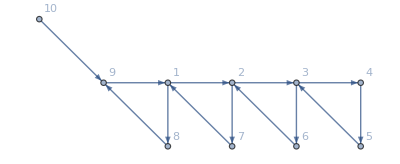

```mathematica
ClearAll[g];
g=Graph[{1->2,2->3,3->4,4->5,5->3,3->6,6->2,2->7,7->1,1->8,9->1,8->9,10->9},VertexLabels->{9->Button[9,g=MutateGraph[g,9];],1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,Null],5->Button[5,Null],6->Button[6,Null],7->Button[7,Null],8->Button[8,Null],10->Button[10,Null]},VertexCoordinates->{1->{0,0},2->{1,0},3->{2,0},4->{3,0},5->{3,-1},6->{2,-1},7->{1,-1},8->{0,-1},9->{-1,0},10->{-2,1}},GraphLayout->"GridEmbedding"]
```

```mathematica
Dynamic[g]
```

```mathematica
ClearAll[a];
SetAttributes[a,{Orderless}];
ClearAll[GramM];
GramM::err="The input should be a square matrix.";
GramM[I_]:=GramM[I,I];
GramM[I_,J_]:=Module[{r,c},
r=I//Sort;
c=J//Sort;
If[Length[I]!=Length[J],Message[GramM::err];Return[$Failed]];
Det[Outer[a,r,c]]
];
```

```mathematica
exMat={{0,1,0},{-1,0,1},{0,-1,0},{0,0,-1},{0,0,2},{0,2,-2},{2,-2,0},{1,0,0}};
xv={GramM[{1}],GramM[{1,2}],GramM[{1,2,3}],GramM[{1,2,3,4}],GramM[{1,2,3},{2,3,4}],GramM[{1,2},{2,3}],GramM[{1},{2}],1};
```

```mathematica
tem=Reap[
temp={exMat,xv};
Do[
temp=MutateB[temp[[1]],temp[[2]],Mod[i,3]+1];
Sow[temp];
,{i,0,17}];
][[2,1]];
```

```mathematica
var=tem[[All,2]][[All,{1,2,3}]]//Flatten//DeleteDuplicates//Sort;
```

```mathematica
var//Length
```

9

```mathematica
var
```

{a[1,1],a[2,2],-a[1,2]^2+a[1,1] a[2,2],a[1,3]^2 a[2,2]-2 a[1,2] a[1,3] a[2,3]+a[1,2]^2 a[3,3],-a[2,3]^2+a[2,2] a[3,3],-a[1,3]^2 a[2,2]+2 a[1,2] a[1,3] a[2,3]-a[1,1] a[2,3]^2-a[1,2]^2 a[3,3]+a[1,1] a[2,2] a[3,3],-a[1,4]^2 a[2,2] a[2,3]^2+2 a[1,3] a[1,4] a[2,2] a[2,3] a[2,4]-a[1,3]^2 a[2,2] a[2,4]^2+a[1,4]^2 a[2,2]^2 a[3,3]-2 a[1,2] a[1,4] a[2,2] a[2,4] a[3,3]+a[1,2]^2 a[2,4]^2 a[3,3]-2 a[1,3] a[1,4] a[2,2]^2 a[3,4]+2 a[1,2] a[1,4] a[2,2] a[2,3] a[3,4]+2 a[1,2] a[1,3] a[2,2] a[2,4] a[3,4]-2 a[1,2]^2 a[2,3] a[2,4] a[3,4]+a[1,3]^2 a[2,2]^2 a[4,4]-2 a[1,2] a[1,3] a[2,2] a[2,3] a[4,4]+a[1,2]^2 a[2,3]^2 a[4,4],-a[1,4]^2 a[2,3]^2+2 a[1,3] a[1,4] a[2,3] a[2,4]-a[1,3]^2 a[2,4]^2+a[1,4]^2 a[2,2] a[3,3]-2 a[1,2] a[1,4] a[2,4] a[3,3]-2 a[1,3] a[1,4] a[2,2] a[3,4]+2 a[1,2] a[1,4] a[2,3] a[3,4]+2 a[1,2] a[1,3] a[2,4] a[3,4]-a[1,2]^2 a[3,4]^2+a[1,3]^2 a[2,2] a[4,4]-2 a[1,2] a[1,3] a[2,3] a[4,4]+a[1,2]^2 a[3,3] a[4,4],-a[2,4]^2 a[3,3]+2 a[2,3] a[2,4] a[3,4]-a[2,2] a[3,4]^2-a[2,3]^2 a[4,4]+a[2,2] a[3,3] a[4,4]}

```mathematica
varcheck={GramM[{1}],GramM[{1,2}],GramM[{1,2,3}],GramM[{2}],GramM[{2,3}],GramM[{2,3,4}],GramM[{1}]*GramM[{2,3,4}]-GramM[{1,2,3,4}],GramM[{1}]*GramM[{2,3}]-GramM[{1,2,3}],GramM[{1,2}]*GramM[{2,3,4}]-GramM[{2}]*GramM[{1,2,3,4}]}//Factor//Sort;
```

```mathematica
var-varcheck
```

{0,0,0,0,0,0,0,0,0}

```mathematica
(*a sub-quiver of above quiver*)
```

```mathematica
ClearAll[g];
g=Graph[{1->2,2->3,3->4,4->5,5->3,3->6,6->2,2->7,7->1,1->8,9->1},VertexLabels->{9->Button[9,g=MutateGraph[g,9];],1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,Null],5->Button[5,Null],6->Button[6,Null],7->Button[7,Null],8->Button[8,Null]},VertexCoordinates->{1->{0,0},2->{1,0},3->{2,0},4->{3,0},5->{3,-1},6->{2,-1},7->{1,-1},8->{0,-1},9->{-1,1}},GraphLayout->"GridEmbedding"];
Dynamic[g]
```

```mathematica
(*triple term identity*)
```

```mathematica
exMat={{0,1,0},{-1,0,1},{0,-1,0},{0,0,-1},{0,0,2},{0,2,-2},{2,-2,0},{-2,0,0},{1,0,0}};
xv={GramM[{1,2}],GramM[{1,2,3}],GramM[{1,2,3,4}],GramM[{1,2,3,4,5}],GramM[{1,2,3,4},{2,3,4,5}],GramM[{1,2,3},{2,3,4}],GramM[{1,2},{2,3}],GramM[{1},{2}],GramM[{1}]};
```

```mathematica
tem=Reap[
temp={exMat,xv};
Do[
temp=MutateB[temp[[1]],temp[[2]],Mod[i,3]+1];
Sow[temp];
,{i,0,18}];
temp={exMat,xv};
Do[
temp=MutateB[temp[[1]],temp[[2]],Mod[i,2]+1];
Sow[temp];
,{i,0,9}];
temp={exMat,xv};
Do[
temp=MutateB[temp[[1]],temp[[2]],Mod[i,2]*2+1];
Sow[temp];
,{i,0,9}];
][[2,1]];
```

```mathematica
var=Complement[tem[[All,2]]//Flatten,Drop[xv,3]]//Factor
```

{-a[1,2]^2+a[1,1] a[2,2],a[1,3]^2 a[2,2]-2 a[1,2] a[1,3] a[2,3]+a[1,2]^2 a[3,3],-a[1,3]^2 a[2,2]+2 a[1,2] a[1,3] a[2,3]-a[1,1] a[2,3]^2-a[1,2]^2 a[3,3]+a[1,1] a[2,2] a[3,3],-a[1,4]^2 a[2,2] a[2,3]^2+2 a[1,3] a[1,4] a[2,2] a[2,3] a[2,4]-a[1,3]^2 a[2,2] a[2,4]^2+a[1,4]^2 a[2,2]^2 a[3,3]-2 a[1,2] a[1,4] a[2,2] a[2,4] a[3,3]+a[1,2]^2 a[2,4]^2 a[3,3]-2 a[1,3] a[1,4] a[2,2]^2 a[3,4]+2 a[1,2] a[1,4] a[2,2] a[2,3] a[3,4]+2 a[1,2] a[1,3] a[2,2] a[2,4] a[3,4]-2 a[1,2]^2 a[2,3] a[2,4] a[3,4]+a[1,3]^2 a[2,2]^2 a[4,4]-2 a[1,2] a[1,3] a[2,2] a[2,3] a[4,4]+a[1,2]^2 a[2,3]^2 a[4,4],-a[1,4]^2 a[2,3]^2+2 a[1,3] a[1,4] a[2,3] a[2,4]-a[1,3]^2 a[2,4]^2+a[1,4]^2 a[2,2] a[3,3]-2 a[1,2] a[1,4] a[2,4] a[3,3]-2 a[1,3] a[1,4] a[2,2] a[3,4]+2 a[1,2] a[1,4] a[2,3] a[3,4]+2 a[1,2] a[1,3] a[2,4] a[3,4]-a[1,2]^2 a[3,4]^2+a[1,3]^2 a[2,2] a[4,4]-2 a[1,2] a[1,3] a[2,3] a[4,4]+a[1,2]^2 a[3,3] a[4,4],a[1,4]^2 a[2,3]^2-2 a[1,3] a[1,4] a[2,3] a[2,4]+a[1,3]^2 a[2,4]^2-a[1,4]^2 a[2,2] a[3,3]+2 a[1,2] a[1,4] a[2,4] a[3,3]-a[1,1] a[2,4]^2 a[3,3]+2 a[1,3] a[1,4] a[2,2] a[3,4]-2 a[1,2] a[1,4] a[2,3] a[3,4]-2 a[1,2] a[1,3] a[2,4] a[3,4]+2 a[1,1] a[2,3] a[2,4] a[3,4]+a[1,2]^2 a[3,4]^2-a[1,1] a[2,2] a[3,4]^2-a[1,3]^2 a[2,2] a[4,4]+2 a[1,2] a[1,3] a[2,3] a[4,4]-a[1,1] a[2,3]^2 a[4,4]-a[1,2]^2 a[3,3] a[4,4]+a[1,1] a[2,2] a[3,3] a[4,4],a[1,5]^2 a[2,3]^2 a[2,4]^2 a[3,3]-2 a[1,4] a[1,5] a[2,3]^2 a[2,4] a[2,5] a[3,3]+a[1,4]^2 a[2,3]^2 a[2,5]^2 a[3,3]-a[1,5]^2 a[2,2] a[2,4]^2 a[3,3]^2+2 a[1,4] a[1,5] a[2,2] a[2,4] a[2,5] a[3,3]^2-a[1,4]^2 a[2,2] a[2,5]^2 a[3,3]^2-2 a[1,5]^2 a[2,3]^3 a[2,4] a[3,4]+2 a[1,4] a[1,5] a[2,3]^3 a[2,5] a[3,4]+2 a[1,3] a[1,5] a[2,3]^2 a[2,4] a[2,5] a[3,4]-2 a[1,3] a[1,4] a[2,3]^2 a[2,5]^2 a[3,4]+2 a[1,5]^2 a[2,2] a[2,3] a[2,4] a[3,3] a[3,4]-2 a[1,4] a[1,5] a[2,2] a[2,3] a[2,5] a[3,3] a[3,4]-2 a[1,3] a[1,5] a[2,2] a[2,4] a[2,5] a[3,3] a[3,4]+2 a[1,3] a[1,4] a[2,2] a[2,5]^2 a[3,3] a[3,4]+a[1,5]^2 a[2,2] a[2,3]^2 a[3,4]^2-2 a[1,2] a[1,5] a[2,3]^2 a[2,5] a[3,4]^2-a[1,3]^2 a[2,2] a[2,5]^2 a[3,4]^2+2 a[1,2] a[1,3] a[2,3] a[2,5]^2 a[3,4]^2-a[1,5]^2 a[2,2]^2 a[3,3] a[3,4]^2+2 a[1,2] a[1,5] a[2,2] a[2,5] a[3,3] a[3,4]^2-a[1,2]^2 a[2,5]^2 a[3,3] a[3,4]^2+2 a[1,4] a[1,5] a[2,3]^3 a[2,4] a[3,5]-2 a[1,3] a[1,5] a[2,3]^2 a[2,4]^2 a[3,5]-2 a[1,4]^2 a[2,3]^3 a[2,5] a[3,5]+2 a[1,3] a[1,4] a[2,3]^2 a[2,4] a[2,5] a[3,5]-2 a[1,4] a[1,5] a[2,2] a[2,3] a[2,4] a[3,3] a[3,5]+2 a[1,3] a[1,5] a[2,2] a[2,4]^2 a[3,3] a[3,5]+2 a[1,4]^2 a[2,2] a[2,3] a[2,5] a[3,3] a[3,5]-2 a[1,3] a[1,4] a[2,2] a[2,4] a[2,5] a[3,3] a[3,5]-2 a[1,4] a[1,5] a[2,2] a[2,3]^2 a[3,4] a[3,5]+2 a[1,2] a[1,5] a[2,3]^2 a[2,4] a[3,4] a[3,5]+2 a[1,2] a[1,4] a[2,3]^2 a[2,5] a[3,4] a[3,5]+2 a[1,3]^2 a[2,2] a[2,4] a[2,5] a[3,4] a[3,5]-4 a[1,2] a[1,3] a[2,3] a[2,4] a[2,5] a[3,4] a[3,5]+2 a[1,4] a[1,5] a[2,2]^2 a[3,3] a[3,4] a[3,5]-2 a[1,2] a[1,5] a[2,2] a[2,4] a[3,3] a[3,4] a[3,5]-2 a[1,2] a[1,4] a[2,2] a[2,5] a[3,3] a[3,4] a[3,5]+2 a[1,2]^2 a[2,4] a[2,5] a[3,3] a[3,4] a[3,5]+a[1,4]^2 a[2,2] a[2,3]^2 a[3,5]^2-2 a[1,2] a[1,4] a[2,3]^2 a[2,4] a[3,5]^2-a[1,3]^2 a[2,2] a[2,4]^2 a[3,5]^2+2 a[1,2] a[1,3] a[2,3] a[2,4]^2 a[3,5]^2-a[1,4]^2 a[2,2]^2 a[3,3] a[3,5]^2+2 a[1,2] a[1,4] a[2,2] a[2,4] a[3,3] a[3,5]^2-a[1,2]^2 a[2,4]^2 a[3,3] a[3,5]^2+a[1,5]^2 a[2,3]^4 a[4,4]-2 a[1,3] a[1,5] a[2,3]^3 a[2,5] a[4,4]+a[1,3]^2 a[2,3]^2 a[2,5]^2 a[4,4]-2 a[1,5]^2 a[2,2] a[2,3]^2 a[3,3] a[4,4]+2 a[1,3] a[1,5] a[2,2] a[2,3] a[2,5] a[3,3] a[4,4]+2 a[1,2] a[1,5] a[2,3]^2 a[2,5] a[3,3] a[4,4]-2 a[1,2] a[1,3] a[2,3] a[2,5]^2 a[3,3] a[4,4]+a[1,5]^2 a[2,2]^2 a[3,3]^2 a[4,4]-2 a[1,2] a[1,5] a[2,2] a[2,5] a[3,3]^2 a[4,4]+a[1,2]^2 a[2,5]^2 a[3,3]^2 a[4,4]+2 a[1,3] a[1,5] a[2,2] a[2,3]^2 a[3,5] a[4,4]-2 a[1,2] a[1,5] a[2,3]^3 a[3,5] a[4,4]-2 a[1,3]^2 a[2,2] a[2,3] a[2,5] a[3,5] a[4,4]+2 a[1,2] a[1,3] a[2,3]^2 a[2,5] a[3,5] a[4,4]-2 a[1,3] a[1,5] a[2,2]^2 a[3,3] a[3,5] a[4,4]+2 a[1,2] a[1,5] a[2,2] a[2,3] a[3,3] a[3,5] a[4,4]+2 a[1,2] a[1,3] a[2,2] a[2,5] a[3,3] a[3,5] a[4,4]-2 a[1,2]^2 a[2,3] a[2,5] a[3,3] a[3,5] a[4,4]+a[1,3]^2 a[2,2]^2 a[3,5]^2 a[4,4]-2 a[1,2] a[1,3] a[2,2] a[2,3] a[3,5]^2 a[4,4]+a[1,2]^2 a[2,3]^2 a[3,5]^2 a[4,4]-2 a[1,4] a[1,5] a[2,3]^4 a[4,5]+2 a[1,3] a[1,5] a[2,3]^3 a[2,4] a[4,5]+2 a[1,3] a[1,4] a[2,3]^3 a[2,5] a[4,5]-2 a[1,3]^2 a[2,3]^2 a[2,4] a[2,5] a[4,5]+4 a[1,4] a[1,5] a[2,2] a[2,3]^2 a[3,3] a[4,5]-2 a[1,3] a[1,5] a[2,2] a[2,3] a[2,4] a[3,3] a[4,5]-2 a[1,2] a[1,5] a[2,3]^2 a[2,4] a[3,3] a[4,5]-2 a[1,3] a[1,4] a[2,2] a[2,3] a[2,5] a[3,3] a[4,5]-2 a[1,2] a[1,4] a[2,3]^2 a[2,5] a[3,3] a[4,5]+4 a[1,2] a[1,3] a[2,3] a[2,4] a[2,5] a[3,3] a[4,5]-2 a[1,4] a[1,5] a[2,2]^2 a[3,3]^2 a[4,5]+2 a[1,2] a[1,5] a[2,2] a[2,4] a[3,3]^2 a[4,5]+2 a[1,2] a[1,4] a[2,2] a[2,5] a[3,3]^2 a[4,5]-2 a[1,2]^2 a[2,4] a[2,5] a[3,3]^2 a[4,5]-2 a[1,3] a[1,5] a[2,2] a[2,3]^2 a[3,4] a[4,5]+2 a[1,2] a[1,5] a[2,3]^3 a[3,4] a[4,5]+2 a[1,3]^2 a[2,2] a[2,3] a[2,5] a[3,4] a[4,5]-2 a[1,2] a[1,3] a[2,3]^2 a[2,5] a[3,4] a[4,5]+2 a[1,3] a[1,5] a[2,2]^2 a[3,3] a[3,4] a[4,5]-2 a[1,2] a[1,5] a[2,2] a[2,3] a[3,3] a[3,4] a[4,5]-2 a[1,2] a[1,3] a[2,2] a[2,5] a[3,3] a[3,4] a[4,5]+2 a[1,2]^2 a[2,3] a[2,5] a[3,3] a[3,4] a[4,5]-2 a[1,3] a[1,4] a[2,2] a[2,3]^2 a[3,5] a[4,5]+2 a[1,2] a[1,4] a[2,3]^3 a[3,5] a[4,5]+2 a[1,3]^2 a[2,2] a[2,3] a[2,4] a[3,5] a[4,5]-2 a[1,2] a[1,3] a[2,3]^2 a[2,4] a[3,5] a[4,5]+2 a[1,3] a[1,4] a[2,2]^2 a[3,3] a[3,5] a[4,5]-2 a[1,2] a[1,4] a[2,2] a[2,3] a[3,3] a[3,5] a[4,5]-2 a[1,2] a[1,3] a[2,2] a[2,4] a[3,3] a[3,5] a[4,5]+2 a[1,2]^2 a[2,3] a[2,4] a[3,3] a[3,5] a[4,5]-2 a[1,3]^2 a[2,2]^2 a[3,4] a[3,5] a[4,5]+4 a[1,2] a[1,3] a[2,2] a[2,3] a[3,4] a[3,5] a[4,5]-2 a[1,2]^2 a[2,3]^2 a[3,4] a[3,5] a[4,5]+a[1,4]^2 a[2,3]^4 a[5,5]-2 a[1,3] a[1,4] a[2,3]^3 a[2,4] a[5,5]+a[1,3]^2 a[2,3]^2 a[2,4]^2 a[5,5]-2 a[1,4]^2 a[2,2] a[2,3]^2 a[3,3] a[5,5]+2 a[1,3] a[1,4] a[2,2] a[2,3] a[2,4] a[3,3] a[5,5]+2 a[1,2] a[1,4] a[2,3]^2 a[2,4] a[3,3] a[5,5]-2 a[1,2] a[1,3] a[2,3] a[2,4]^2 a[3,3] a[5,5]+a[1,4]^2 a[2,2]^2 a[3,3]^2 a[5,5]-2 a[1,2] a[1,4] a[2,2] a[2,4] a[3,3]^2 a[5,5]+a[1,2]^2 a[2,4]^2 a[3,3]^2 a[5,5]+2 a[1,3] a[1,4] a[2,2] a[2,3]^2 a[3,4] a[5,5]-2 a[1,2] a[1,4] a[2,3]^3 a[3,4] a[5,5]-2 a[1,3]^2 a[2,2] a[2,3] a[2,4] a[3,4] a[5,5]+2 a[1,2] a[1,3] a[2,3]^2 a[2,4] a[3,4] a[5,5]-2 a[1,3] a[1,4] a[2,2]^2 a[3,3] a[3,4] a[5,5]+2 a[1,2] a[1,4] a[2,2] a[2,3] a[3,3] a[3,4] a[5,5]+2 a[1,2] a[1,3] a[2,2] a[2,4] a[3,3] a[3,4] a[5,5]-2 a[1,2]^2 a[2,3] a[2,4] a[3,3] a[3,4] a[5,5]+a[1,3]^2 a[2,2]^2 a[3,4]^2 a[5,5]-2 a[1,2] a[1,3] a[2,2] a[2,3] a[3,4]^2 a[5,5]+a[1,2]^2 a[2,3]^2 a[3,4]^2 a[5,5],-a[1,5]^2 a[2,2] a[2,4]^2 a[3,3]+2 a[1,4] a[1,5] a[2,2] a[2,4] a[2,5] a[3,3]-a[1,4]^2 a[2,2] a[2,5]^2 a[3,3]+2 a[1,5]^2 a[2,2] a[2,3] a[2,4] a[3,4]-2 a[1,4] a[1,5] a[2,2] a[2,3] a[2,5] a[3,4]-2 a[1,3] a[1,5] a[2,2] a[2,4] a[2,5] a[3,4]+2 a[1,3] a[1,4] a[2,2] a[2,5]^2 a[3,4]-a[1,5]^2 a[2,2]^2 a[3,4]^2+2 a[1,2] a[1,5] a[2,2] a[2,5] a[3,4]^2-a[1,2]^2 a[2,5]^2 a[3,4]^2-2 a[1,4] a[1,5] a[2,2] a[2,3] a[2,4] a[3,5]+2 a[1,3] a[1,5] a[2,2] a[2,4]^2 a[3,5]+2 a[1,4]^2 a[2,2] a[2,3] a[2,5] a[3,5]-2 a[1,3] a[1,4] a[2,2] a[2,4] a[2,5] a[3,5]+2 a[1,4] a[1,5] a[2,2]^2 a[3,4] a[3,5]-2 a[1,2] a[1,5] a[2,2] a[2,4] a[3,4] a[3,5]-2 a[1,2] a[1,4] a[2,2] a[2,5] a[3,4] a[3,5]+2 a[1,2]^2 a[2,4] a[2,5] a[3,4] a[3,5]-a[1,4]^2 a[2,2]^2 a[3,5]^2+2 a[1,2] a[1,4] a[2,2] a[2,4] a[3,5]^2-a[1,2]^2 a[2,4]^2 a[3,5]^2-a[1,5]^2 a[2,2] a[2,3]^2 a[4,4]+2 a[1,3] a[1,5] a[2,2] a[2,3] a[2,5] a[4,4]-a[1,3]^2 a[2,2] a[2,5]^2 a[4,4]+a[1,5]^2 a[2,2]^2 a[3,3] a[4,4]-2 a[1,2] a[1,5] a[2,2] a[2,5] a[3,3] a[4,4]+a[1,2]^2 a[2,5]^2 a[3,3] a[4,4]-2 a[1,3] a[1,5] a[2,2]^2 a[3,5] a[4,4]+2 a[1,2] a[1,5] a[2,2] a[2,3] a[3,5] a[4,4]+2 a[1,2] a[1,3] a[2,2] a[2,5] a[3,5] a[4,4]-2 a[1,2]^2 a[2,3] a[2,5] a[3,5] a[4,4]+2 a[1,4] a[1,5] a[2,2] a[2,3]^2 a[4,5]-2 a[1,3] a[1,5] a[2,2] a[2,3] a[2,4] a[4,5]-2 a[1,3] a[1,4] a[2,2] a[2,3] a[2,5] a[4,5]+2 a[1,3]^2 a[2,2] a[2,4] a[2,5] a[4,5]-2 a[1,4] a[1,5] a[2,2]^2 a[3,3] a[4,5]+2 a[1,2] a[1,5] a[2,2] a[2,4] a[3,3] a[4,5]+2 a[1,2] a[1,4] a[2,2] a[2,5] a[3,3] a[4,5]-2 a[1,2]^2 a[2,4] a[2,5] a[3,3] a[4,5]+2 a[1,3] a[1,5] a[2,2]^2 a[3,4] a[4,5]-2 a[1,2] a[1,5] a[2,2] a[2,3] a[3,4] a[4,5]-2 a[1,2] a[1,3] a[2,2] a[2,5] a[3,4] a[4,5]+2 a[1,2]^2 a[2,3] a[2,5] a[3,4] a[4,5]+2 a[1,3] a[1,4] a[2,2]^2 a[3,5] a[4,5]-2 a[1,2] a[1,4] a[2,2] a[2,3] a[3,5] a[4,5]-2 a[1,2] a[1,3] a[2,2] a[2,4] a[3,5] a[4,5]+2 a[1,2]^2 a[2,3] a[2,4] a[3,5] a[4,5]-a[1,3]^2 a[2,2]^2 a[4,5]^2+2 a[1,2] a[1,3] a[2,2] a[2,3] a[4,5]^2-a[1,2]^2 a[2,3]^2 a[4,5]^2-a[1,4]^2 a[2,2] a[2,3]^2 a[5,5]+2 a[1,3] a[1,4] a[2,2] a[2,3] a[2,4] a[5,5]-a[1,3]^2 a[2,2] a[2,4]^2 a[5,5]+a[1,4]^2 a[2,2]^2 a[3,3] a[5,5]-2 a[1,2] a[1,4] a[2,2] a[2,4] a[3,3] a[5,5]+a[1,2]^2 a[2,4]^2 a[3,3] a[5,5]-2 a[1,3] a[1,4] a[2,2]^2 a[3,4] a[5,5]+2 a[1,2] a[1,4] a[2,2] a[2,3] a[3,4] a[5,5]+2 a[1,2] a[1,3] a[2,2] a[2,4] a[3,4] a[5,5]-2 a[1,2]^2 a[2,3] a[2,4] a[3,4] a[5,5]+a[1,3]^2 a[2,2]^2 a[4,4] a[5,5]-2 a[1,2] a[1,3] a[2,2] a[2,3] a[4,4] a[5,5]+a[1,2]^2 a[2,3]^2 a[4,4] a[5,5],-a[1,5]^2 a[2,4]^2 a[3,3]+2 a[1,4] a[1,5] a[2,4] a[2,5] a[3,3]-a[1,4]^2 a[2,5]^2 a[3,3]+2 a[1,5]^2 a[2,3] a[2,4] a[3,4]-2 a[1,4] a[1,5] a[2,3] a[2,5] a[3,4]-2 a[1,3] a[1,5] a[2,4] a[2,5] a[3,4]+2 a[1,3] a[1,4] a[2,5]^2 a[3,4]-a[1,5]^2 a[2,2] a[3,4]^2+2 a[1,2] a[1,5] a[2,5] a[3,4]^2-2 a[1,4] a[1,5] a[2,3] a[2,4] a[3,5]+2 a[1,3] a[1,5] a[2,4]^2 a[3,5]+2 a[1,4]^2 a[2,3] a[2,5] a[3,5]-2 a[1,3] a[1,4] a[2,4] a[2,5] a[3,5]+2 a[1,4] a[1,5] a[2,2] a[3,4] a[3,5]-2 a[1,2] a[1,5] a[2,4] a[3,4] a[3,5]-2 a[1,2] a[1,4] a[2,5] a[3,4] a[3,5]-a[1,4]^2 a[2,2] a[3,5]^2+2 a[1,2] a[1,4] a[2,4] a[3,5]^2-a[1,5]^2 a[2,3]^2 a[4,4]+2 a[1,3] a[1,5] a[2,3] a[2,5] a[4,4]-a[1,3]^2 a[2,5]^2 a[4,4]+a[1,5]^2 a[2,2] a[3,3] a[4,4]-2 a[1,2] a[1,5] a[2,5] a[3,3] a[4,4]-2 a[1,3] a[1,5] a[2,2] a[3,5] a[4,4]+2 a[1,2] a[1,5] a[2,3] a[3,5] a[4,4]+2 a[1,2] a[1,3] a[2,5] a[3,5] a[4,4]-a[1,2]^2 a[3,5]^2 a[4,4]+2 a[1,4] a[1,5] a[2,3]^2 a[4,5]-2 a[1,3] a[1,5] a[2,3] a[2,4] a[4,5]-2 a[1,3] a[1,4] a[2,3] a[2,5] a[4,5]+2 a[1,3]^2 a[2,4] a[2,5] a[4,5]-2 a[1,4] a[1,5] a[2,2] a[3,3] a[4,5]+2 a[1,2] a[1,5] a[2,4] a[3,3] a[4,5]+2 a[1,2] a[1,4] a[2,5] a[3,3] a[4,5]+2 a[1,3] a[1,5] a[2,2] a[3,4] a[4,5]-2 a[1,2] a[1,5] a[2,3] a[3,4] a[4,5]-2 a[1,2] a[1,3] a[2,5] a[3,4] a[4,5]+2 a[1,3] a[1,4] a[2,2] a[3,5] a[4,5]-2 a[1,2] a[1,4] a[2,3] a[3,5] a[4,5]-2 a[1,2] a[1,3] a[2,4] a[3,5] a[4,5]+2 a[1,2]^2 a[3,4] a[3,5] a[4,5]-a[1,3]^2 a[2,2] a[4,5]^2+2 a[1,2] a[1,3] a[2,3] a[4,5]^2-a[1,2]^2 a[3,3] a[4,5]^2-a[1,4]^2 a[2,3]^2 a[5,5]+2 a[1,3] a[1,4] a[2,3] a[2,4] a[5,5]-a[1,3]^2 a[2,4]^2 a[5,5]+a[1,4]^2 a[2,2] a[3,3] a[5,5]-2 a[1,2] a[1,4] a[2,4] a[3,3] a[5,5]-2 a[1,3] a[1,4] a[2,2] a[3,4] a[5,5]+2 a[1,2] a[1,4] a[2,3] a[3,4] a[5,5]+2 a[1,2] a[1,3] a[2,4] a[3,4] a[5,5]-a[1,2]^2 a[3,4]^2 a[5,5]+a[1,3]^2 a[2,2] a[4,4] a[5,5]-2 a[1,2] a[1,3] a[2,3] a[4,4] a[5,5]+a[1,2]^2 a[3,3] a[4,4] a[5,5]}

```mathematica
var//Length
```

9

```mathematica
arep={a[1,1]->0,a[1,2]->m12,a[1,3]->s,a[1,4]->0,a[1,5]->1,a[2,2]->0,a[2,3]->0,a[2,4]->t,a[2,5]->1,a[3,3]->0,a[3,4]->m22,a[3,5]->1,a[4,4]->0,a[4,5]->1,a[5,5]->0};
```

```mathematica
var/.arep//Factor//Flatten
```

{-m12^2,0,0,0,-(m12 m22-s t)^2,(m12 m22-s t)^2,0,-m12^2 (m22-t)^2,2 (m12+m22-s-t) (m12 m22-s t)}

```mathematica
perm=Permutations[{1,2,3,4}]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
arept=Table[{a[perm[[i,1]],perm[[i,1]]]->0,a[perm[[i,1]],perm[[i,2]]]->m12,a[perm[[i,1]],perm[[i,3]]]->s,a[perm[[i,1]],perm[[i,4]]]->0,a[perm[[i,1]],5]->1,a[perm[[i,2]],perm[[i,2]]]->0,a[perm[[i,2]],perm[[i,3]]]->0,a[perm[[i,2]],perm[[i,4]]]->t,a[perm[[i,2]],5]->1,a[perm[[i,3]],perm[[i,3]]]->0,a[perm[[i,3]],perm[[i,4]]]->m22,a[perm[[i,3]],5]->1,a[perm[[i,4]],perm[[i,4]]]->0,a[perm[[i,4]],5]->1,a[5,5]->0},{i,1,Length[perm]}];
```

```mathematica
glist=Table[var/.arept[[i]]//Factor//Flatten//DeleteDuplicates,{i,1,24}];
```

```mathematica
(FactorList[#][[All,1]]&/@(glist//Flatten))//Flatten//DeleteDuplicates//DeleteCases[#,_?NumberQ]&//DeleteDuplicates[#,((#1-#2//Factor)==0||(#1+#2//Factor)==0)&]&
```

{m12,m12 m22-s t,m22-t,m12+m22-s-t,t,s,m22,m22-s,m12-t,m12-s}

```mathematica
%//Length
```

10

### A3: G46

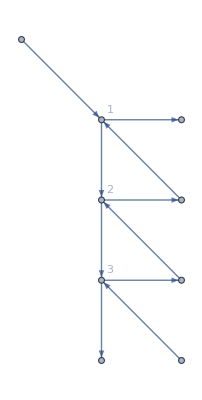

```mathematica
ClearAll[g];
g=Graph[{0->1,1->2,2->3,3->4,1->5,6->1,2->6,7->2,3->7,8->3},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];]},VertexCoordinates->{0->{-1,1},1->{0,0},2->{0,-1},3->{0,-2},4->{0,-3},5->{1,0},6->{1,-1},7->{1,-2},8->{1,-3}},GraphLayout->"GridEmbedding"]
```

```mathematica
Dynamic[g]
```

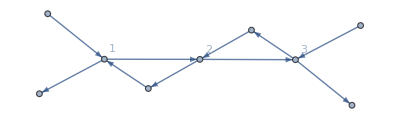

```mathematica
ClearAll[g];
g=Graph[{0->1,1->2,2->3,3->4,1->5,6->1,2->6,7->2,3->7,8->3},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];]}]
```

```mathematica
numM=RandomPrime[10000,{4,6}]
```

{{673,5927,1123,9887,4079,3257},{7589,857,8627,5573,2767,9851},{2293,7177,9901,4177,9817,4111},{911,5651,9839,547,8929,3823}}

```mathematica
SetOptions[fB,"explicitM"->numM];
```

```mathematica
Bm={{0,-1,0},{1,0,-1},{0,1,0},{-1,0,0},{1,0,0},{-1,1,0},{0,-1,1},{0,0,-1},{0,0,1}};
xv={fB[{1,2,3,6}]*fB[{1,3,4,5}]^2,fB[{1,2,3,6}]*fB[{1,2,4,5}]^2,fB[{1,4,5,6}]*fB[{1,2,3,5}]^2,fB[{1,2,3,6}]*fB[{1,4,5,6}]*fB[{2,3,4,5}],fB[{1,2,3,6}]*fB[{3,4,5,6}]^2,fB[{1,2,3,6}]*fB[{1,4,5,6}]*fB[{2,3,4,5}],fB[{2,3,4,5}]*fB[{1,2,5,6}]^2,fB[{1,2,3,6}]*fB[{1,4,5,6}]*fB[{2,3,4,5}],fB[{1,4,5,6}]*fB[{1,2,3,4}]^2};
(*A3*)
```

```mathematica
temX=Reap[
temp={Bm,xv};
Do[
temp=MutateB[temp[[1]],temp[[2]],Mod[i,3]+1];
Sow[temp];
,{i,0,40}];
][[2,1]];
```

```mathematica
varx=temX[[All,2]][[All,{1,2,3}]]//Flatten//DeleteDuplicates//Sort;
```

```mathematica
varx//Length
```

9

```mathematica
yv={y1,y2,y3};
```

```mathematica
MutateY[Bm,yv,1]
```

{{{0,1,0},{-1,0,-1},{0,1,0},{1,-1,0},{-1,0,0},{1,0,0},{0,-1,1},{0,0,-1},{0,0,1}},{1/y1,(1+y1) y2,y3}}

```mathematica
MutateY[%[[1]],%[[2]],2]
```

{{{0,-1,0},{1,0,1},{0,-1,0},{0,1,-1},{-1,0,0},{1,0,0},{-1,1,0},{0,0,-1},{0,0,1}},{(1+y2+y1 y2)/y1,1/((1+y1) y2),(1+y2+y1 y2) y3}}

```mathematica
Bm={{0,1,0},{-1,0,-1},{0,1,0}};
yv={y1,y2,y3};
```

```mathematica
ml={2,1,3,2,1,3,2,1,3,2,1,3,2,1,3,2,1,3,2,1,3,2,1,3};
tem=Reap[
temp={Bm,yv};
Sow[temp];
Do[
temp=MutateY[temp[[1]],temp[[2]],ml[[i]]];
Sow[temp];
,{i,1,Length[ml]}];
][[2,1]];
```

y1->y1*(1+y2)^1

y2-> 1/y2

y3->y3*(1+y2)^1

y1-> 1/y1

y2->y2*(1+y1)^1

y3->y3*(1+y1)^0

y1->y1*(1+y3)^0

y2->y2*(1+y3)^1

y3-> 1/y3

y1->y1*(1+y2)^1

y2-> 1/y2

y3->y3*(1+y2)^1

y1-> 1/y1

y2->y2*(1+y1)^1

y3->y3*(1+y1)^0

y1->y1*(1+y3)^0

y2->y2*(1+y3)^1

y3-> 1/y3

y1->y1*(1+y2)^1

y2-> 1/y2

y3->y3*(1+y2)^1

y1-> 1/y1

y2->y2*(1+y1)^1

y3->y3*(1+y1)^0

y1->y1*(1+y3)^0

y2->y2*(1+y3)^1

y3-> 1/y3

y1->y1*(1+y2)^1

y2-> 1/y2

y3->y3*(1+y2)^1

y1-> 1/y1

y2->y2*(1+y1)^1

y3->y3*(1+y1)^0

y1->y1*(1+y3)^0

y2->y2*(1+y3)^1

y3-> 1/y3

y1->y1*(1+y2)^1

y2-> 1/y2

y3->y3*(1+y2)^1

y1-> 1/y1

y2->y2*(1+y1)^1

y3->y3*(1+y1)^0

y1->y1*(1+y3)^0

y2->y2*(1+y3)^1

y3-> 1/y3

y1->y1*(1+y2)^1

y2-> 1/y2

y3->y3*(1+y2)^1

y1-> 1/y1

y2->y2*(1+y1)^1

y3->y3*(1+y1)^0

y1->y1*(1+y3)^0

y2->y2*(1+y3)^1

y3-> 1/y3

y1->y1*(1+y2)^1

y2-> 1/y2

y3->y3*(1+y2)^1

y1-> 1/y1

y2->y2*(1+y1)^1

y3->y3*(1+y1)^0

y1->y1*(1+y3)^0

y2->y2*(1+y3)^1

y3-> 1/y3

y1->y1*(1+y2)^1

y2-> 1/y2

y3->y3*(1+y2)^1

y1-> 1/y1

y2->y2*(1+y1)^1

y3->y3*(1+y1)^0

y1->y1*(1+y3)^0

y2->y2*(1+y3)^1

y3-> 1/y3

```mathematica
tem[[1;;12]]
```

{{{{0,1,0},{-1,0,-1},{0,1,0}},{y1,y2,y3}},{{{0,-1,0},{1,0,1},{0,-1,0}},{y1 (1+y2),1/y2,(1+y2) y3}},{{{0,1,0},{-1,0,1},{0,-1,0}},{1/(y1 (1+y2)),(1+y1+y1 y2)/y2,(1+y2) y3}},{{{0,1,0},{-1,0,-1},{0,1,0}},{1/(y1 (1+y2)),((1+y1+y1 y2) (1+y3+y2 y3))/y2,1/((1+y2) y3)}},{{{0,-1,0},{1,0,1},{0,-1,0}},{(1+y1+y3+y1 y3+y1 y2 y3)/(y1 y2),y2/((1+y1+y1 y2) (1+y3+y2 y3)),(1+y1+y3+y1 y3+y1 y2 y3)/(y2 y3)}},{{{0,1,0},{-1,0,1},{0,-1,0}},{(y1 y2)/(1+y1+y3+y1 y3+y1 y2 y3),(1+y3)/(y1 (1+y3+y2 y3)),(1+y1+y3+y1 y3+y1 y2 y3)/(y2 y3)}},{{{0,1,0},{-1,0,-1},{0,1,0}},{(y1 y2)/(1+y1+y3+y1 y3+y1 y2 y3),((1+y1) (1+y3))/(y1 y2 y3),(y2 y3)/(1+y1+y3+y1 y3+y1 y2 y3)}},{{{0,-1,0},{1,0,1},{0,-1,0}},{1/y3,(y1 y2 y3)/((1+y1) (1+y3)),1/y1}},{{{0,1,0},{-1,0,1},{0,-1,0}},{y3,(y1 y2)/(1+y1),1/y1}},{{{0,1,0},{-1,0,-1},{0,1,0}},{y3,y2,y1}},{{{0,-1,0},{1,0,1},{0,-1,0}},{(1+y2) y3,1/y2,y1 (1+y2)}},{{{0,1,0},{-1,0,1},{0,-1,0}},{1/((1+y2) y3),(1+y3+y2 y3)/y2,y1 (1+y2)}}}

```mathematica
tem1=Select[tem[[1;;12]],(#[[1,2]]==={1,0,1}||#[[1,2]]==={-1,0,-1})&]
```

{{{{0,1,0},{-1,0,-1},{0,1,0}},{y1,y2,y3}},{{{0,-1,0},{1,0,1},{0,-1,0}},{y1 (1+y2),1/y2,(1+y2) y3}},{{{0,1,0},{-1,0,-1},{0,1,0}},{1/(y1 (1+y2)),((1+y1+y1 y2) (1+y3+y2 y3))/y2,1/((1+y2) y3)}},{{{0,-1,0},{1,0,1},{0,-1,0}},{(1+y1+y3+y1 y3+y1 y2 y3)/(y1 y2),y2/((1+y1+y1 y2) (1+y3+y2 y3)),(1+y1+y3+y1 y3+y1 y2 y3)/(y2 y3)}},{{{0,1,0},{-1,0,-1},{0,1,0}},{(y1 y2)/(1+y1+y3+y1 y3+y1 y2 y3),((1+y1) (1+y3))/(y1 y2 y3),(y2 y3)/(1+y1+y3+y1 y3+y1 y2 y3)}},{{{0,-1,0},{1,0,1},{0,-1,0}},{1/y3,(y1 y2 y3)/((1+y1) (1+y3)),1/y1}},{{{0,1,0},{-1,0,-1},{0,1,0}},{y3,y2,y1}},{{{0,-1,0},{1,0,1},{0,-1,0}},{(1+y2) y3,1/y2,y1 (1+y2)}}}

```mathematica
tem1[[All,2]][[All,2]]/.{y1->f[1],y2->f[2],y3->f[3]}(*/.{f[1]->f[3]}*)//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&
```

{f[2],((1+f[1]+f[1] f[2]) (1+f[3]+f[2] f[3]))/f[2],((1+f[1]) (1+f[3]))/(f[1] f[2] f[3])}

```mathematica
tem1[[All,2]][[All,{1,3}]]/.{y1->f[1],y2->f[2],y3->f[3]}(*/.{f[1]->f[3]}*)//Factor//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&
```

{f[1],f[3],f[1] (1+f[2]),(1+f[2]) f[3],(1+f[1]+f[3]+f[1] f[3]+f[1] f[2] f[3])/(f[1] f[2]),(1+f[1]+f[3]+f[1] f[3]+f[1] f[2] f[3])/(f[2] f[3])}

```mathematica
tem1[[All,2]][[All,2]]/.{y1->f[1],y2->f[2],y3->f[3]}/.{f[1]->f[3]}//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&
```

{f[2],(1+f[3]+f[2] f[3])^2/f[2],(1+f[3])^2/(f[2] f[3]^2)}

```mathematica
tem1[[All,2]][[All,{1,3}]]/.{y1->f[1],y2->f[2],y3->f[3]}/.{f[1]->f[3]}//Factor//Flatten//DeleteDuplicates//DeleteDuplicates[#,((#1*#2===1)&)]&
```

{f[3],(1+f[2]) f[3],(1+2 f[3]+f[3]^2+f[2] f[3]^2)/(f[2] f[3])}

```mathematica
1/((ab[1,2,4,6] ab[1,3,4,5])/(ab[1,2,3,4] ab[1,4,5,6]))//Factor
```

(ab[1,2,3,4] ab[1,4,5,6])/(ab[1,2,4,6] ab[1,3,4,5])

```mathematica
fdefA3={f[1]->(ab[1,2,3,4] ab[1,2,5,6])/(ab[1,2,3,6] ab[1,2,4,5]),f[2]->(ab[1,2,4,6] ab[1,3,4,5])/(ab[1,2,3,4] ab[1,4,5,6]),f[3]->(ab[1,4,5,6] ab[2,3,4,5])/(ab[1,2,4,5] ab[3,4,5,6])}/.{ab->FB};
MatA3={{1,0,0,0},{(1+f[3])/f[3],1,0,0},{1/f[3],(1+f[1]+f[1] f[2])/(f[1] f[2]),1,0},{0,(1+f[1])/(f[1] f[2]),1+f[1],1},{0,0,f[1],1},{0,0,0,1}};
```

```mathematica
{u/(v*w),v/(w u),w/(u v)}/.{u->FB[6,1,2,3]*FB[3,4,5,6]/FB[6,1,3,4]/FB[2,3,5,6],v->FB[1,2,3,4]*FB[4,5,6,1]/FB[1,2,4,5]/FB[3,4,6,1],w->FB[2,3,4,5]*FB[5,6,1,2]/FB[2,3,5,6]/FB[4,5,1,2]}
```

{(FB[1,2,3,6] FB[1,2,4,5]^2 FB[3,4,5,6])/(FB[1,2,3,4] FB[1,2,5,6] FB[1,4,5,6] FB[2,3,4,5]),(FB[1,2,3,4] FB[1,4,5,6] FB[2,3,5,6]^2)/(FB[1,2,3,6] FB[1,2,5,6] FB[2,3,4,5] FB[3,4,5,6]),(FB[1,2,5,6] FB[1,3,4,6]^2 FB[2,3,4,5])/(FB[1,2,3,4] FB[1,2,3,6] FB[1,4,5,6] FB[3,4,5,6])}

```mathematica
{u/(v*w),v/(w u),w/(u v)}/.{u->FB[6,1,2,3]*FB[3,4,5,6]/FB[6,1,3,4]/FB[2,3,5,6],v->FB[1,2,3,4]*FB[4,5,6,1]/FB[1,2,4,5]/FB[3,4,6,1],w->FB[2,3,4,5]*FB[5,6,1,2]/FB[2,3,5,6]/FB[4,5,1,2]}/.{FB[a__]:>fB[a,"explicitM"->MatA3]}(*/.{f[1]->f[3]}*)//Factor
```

{1/(f[1] f[3]),(1+f[1]+f[3]+f[1] f[3]+f[1] f[2] f[3])^2/(f[1] f[2]^2 f[3]),f[1] (1+f[2])^2 f[3]}

```mathematica
Thread@Rule[{u/(v*w),v/(w u),w/(u v)},{1/f[3]^2,((1+2 f[3]+f[3]^2+f[2] f[3]^2)^2)/(f[2]^2 f[3]^2),(1+f[2])^2 f[3]^2}]
```

{u/(v w)→1/f[3]^2,v/(u w)→((1+2 f[3]+f[3]^2+f[2] f[3]^2)^2)/(f[2]^2 f[3]^2),w/(u v)→(1+f[2])^2 f[3]^2}

```mathematica
{u,v,w}/.{u->FB[6,1,2,3]*FB[3,4,5,6]/FB[6,1,3,4]/FB[2,3,5,6],v->FB[1,2,3,4]*FB[4,5,6,1]/FB[1,2,4,5]/FB[3,4,6,1],w->FB[2,3,4,5]*FB[5,6,1,2]/FB[2,3,5,6]/FB[4,5,1,2]}/.{FB[a__]:>fB[a,"explicitM"->MatA3]}//Factor
```

{f[2]/((1+f[2]) (1+f[1]+f[3]+f[1] f[3]+f[1] f[2] f[3])),1/(1+f[2]),(f[1] f[2] f[3])/(1+f[1]+f[3]+f[1] f[3]+f[1] f[2] f[3])}

```mathematica
({(1-u)/u,(1-v)/v,(1-w)/w}/.{u->FB[6,1,2,3]*FB[3,4,5,6]/FB[6,1,3,4]/FB[2,3,5,6],v->FB[1,2,3,4]*FB[4,5,6,1]/FB[1,2,4,5]/FB[3,4,6,1],w->FB[2,3,4,5]*FB[5,6,1,2]/FB[2,3,5,6]/FB[4,5,1,2]}/.{FB[a__]:>fB[a,"explicitM"->MatA3]}//Factor)(*/.{f[1]->f[3]}*)
```

{((1+f[1]+f[1] f[2]) (1+f[3]+f[2] f[3]))/f[2],f[2],((1+f[1]) (1+f[3]))/(f[1] f[2] f[3])}

```mathematica
Thread@Rule[{(1-u)/u,(1-v)/v,(1-w)/w},{(1+f[3]+f[2] f[3])^2/f[2],f[2],(1+f[3])^2/(f[2] f[3]^2)}]
```

{(1-u)/u→(1+f[3]+f[2] f[3])^2/f[2],(1-v)/v→f[2],(1-w)/w→(1+f[3])^2/(f[2] f[3]^2)}

```mathematica
{u/(v*w),v/(w u),w/(u v)}/.{u->FB[6,1,2,3]*FB[3,4,5,6]/FB[6,1,3,4]/FB[2,3,5,6],v->FB[1,2,3,4]*FB[4,5,6,1]/FB[1,2,4,5]/FB[3,4,6,1],w->FB[2,3,4,5]*FB[5,6,1,2]/FB[2,3,5,6]/FB[4,5,1,2]}/.{FB[a__]:>fB[a,"explicitM"->MatA3]}/.{f[1]->f[3]}//Factor
```

{1/f[3]^2,((1+2 f[3]+f[3]^2+f[2] f[3]^2)^2)/(f[2]^2 f[3]^2),(1+f[2])^2 f[3]^2}

```mathematica
({(1-u)/u,(1-v)/v,(1-w)/w}/.{u->FB[6,1,2,3]*FB[3,4,5,6]/FB[6,1,3,4]/FB[2,3,5,6],v->FB[1,2,3,4]*FB[4,5,6,1]/FB[1,2,4,5]/FB[3,4,6,1],w->FB[2,3,4,5]*FB[5,6,1,2]/FB[2,3,5,6]/FB[4,5,1,2]}/.{FB[a__]:>fB[a,"explicitM"->MatA3]}//Factor)/.{f[1]->f[3]}
```

{(1+f[3]+f[2] f[3])^2/f[2],f[2],(1+f[3])^2/(f[2] f[3]^2)}

```mathematica
var=tem[[All,2]]//Flatten//DeleteDuplicates//Sort;
```

```mathematica
var
```

{1/y1,y1,1/((1+y1) y2),y2,(1+y1) y2,(1+y2)/(y1 y2),y1/(1+y2+y1 y2),(1+y2+y1 y2)/y1,1/y3,1/((1+y2) y3),1/((1+y2+y1 y2) y3),y3,(1+y2+y1 y2) y3,(y2 y3)/(1+y3),((1+y1) y2 y3)/(1+y3),(1+y3)/(y2 y3),y2/(1+y3+y2 y3),(y1 y2 y3)/(1+y3+y2 y3),(1+y3+y2 y3)/y2,(1+y3+y2 y3)/(y1 y2 y3),(y1 y2)/((1+y2) (1+y3+y2 y3+y1 y2 y3)),(y1 (1+y3))/(1+y3+y2 y3+y1 y2 y3),(1+y3+y2 y3+y1 y2 y3)/((1+y1) y2),((1+y2) (1+y3+y2 y3+y1 y2 y3))/(y1 y2)}

```mathematica
var//Length
```

24

```mathematica
FactorList[#][[All,1]]&/@var//Flatten//DeleteDuplicates//DeleteCases[#,_?NumericQ]&//SortBy[#,LeafCount]&
```

{y1,y2,y3,1+y1,1+y2,1+y3,1+y2+y1 y2,1+y3+y2 y3,1+y3+y2 y3+y1 y2 y3}

```mathematica
Bms=tem[[All,1]](*//DeleteDuplicates[#,(#1===#2||(-#1)===#2)&]&*);
```

```mathematica
Bms//Length
```

32

reference to the onshellcut_demo.nb

```mathematica
xlist={FB[1,2,3,6]*FB[1,3,4,5]^2,FB[1,2,3,6]*FB[1,2,4,5]^2,FB[1,4,5,6]*FB[1,2,3,5]^2,FB[1,4,5,6]FB[1,2,3,6]FB[2,3,4,5],FB[1,2,3,6]*FB[3,4,5,6]^2,FB[1,4,5,6]FB[1,2,3,6]FB[2,3,4,5],FB[2,3,4,5]FB[1,2,5,6]^2,FB[1,4,5,6]FB[1,2,3,6]FB[2,3,4,5],FB[1,4,5,6]FB[1,2,3,4]^2};
```

```mathematica
ys=Reap[Do[
temp=Bms[[i]]//Transpose;
Sow[Table[Times@@Power@@@Partition[Riffle[xlist,temp[[i]]],2],{i,1,Length[temp]}]//Factor]
,{i,1,Length[Bms]}]][[2,1]];
```

```mathematica
ysinds=ys//Flatten//DeleteDuplicates;
```

```mathematica
ysinds//Length
```

24

```mathematica
ysinds
```

{(FB[1,2,4,5]^2 FB[3,4,5,6]^2)/(FB[1,4,5,6]^2 FB[2,3,4,5]^2),(FB[1,2,3,5]^2 FB[1,4,5,6]^2)/(FB[1,2,5,6]^2 FB[1,3,4,5]^2),(FB[1,2,3,4]^2 FB[1,2,5,6]^2)/(FB[1,2,3,6]^2 FB[1,2,4,5]^2),(FB[1,4,5,6]^2 FB[2,3,4,5]^2)/(FB[1,2,4,5]^2 FB[3,4,5,6]^2),(FB[1,2,3,5]^2 FB[1,3,4,5]^2)/(FB[1,2,5,6]^2 FB[2,3,4,5]^2),(FB[1,2,3,6] FB[1,2,4,5]^2 FB[1,4,5,6])/(FB[1,2,5,6]^2 FB[3,4,5,6]^2),(FB[1,2,5,6]^2 FB[2,3,4,5]^2)/(FB[1,2,3,5]^2 FB[1,3,4,5]^2),(FB[1,2,3,4]^2 FB[1,2,4,5]^2)/(FB[1,2,3,6] FB[1,4,5,6] FB[2,3,4,5]^2),(FB[1,2,3,5]^2 FB[1,2,5,6]^2)/(FB[1,2,3,6]^2 FB[1,3,4,5]^2),(FB[1,2,3,6] FB[1,4,5,6] FB[2,3,4,5]^2)/(FB[1,2,3,4]^2 FB[1,2,4,5]^2),(FB[1,2,5,6]^2 FB[3,4,5,6]^2)/(FB[1,2,3,6] FB[1,2,4,5]^2 FB[1,4,5,6]),(FB[1,2,3,5]^2 FB[1,3,4,5]^2)/(FB[1,2,3,6] FB[2,3,4,5] FB[3,4,5,6]^2),(FB[1,2,4,5]^2 FB[1,2,5,6]^2)/(FB[1,2,3,6] FB[1,4,5,6]^2 FB[2,3,4,5]),(FB[1,2,3,6] FB[2,3,4,5] FB[3,4,5,6]^2)/(FB[1,2,3,5]^2 FB[1,3,4,5]^2),(FB[1,2,3,6] FB[1,2,4,5]^2 FB[2,3,4,5])/(FB[1,2,3,4]^2 FB[3,4,5,6]^2),(FB[1,2,3,5]^2 FB[1,4,5,6] FB[2,3,4,5])/(FB[1,2,3,4]^2 FB[1,3,4,5]^2),(FB[1,2,3,4]^2 FB[3,4,5,6]^2)/(FB[1,2,3,6] FB[1,2,4,5]^2 FB[2,3,4,5]),(FB[1,2,3,6] FB[1,4,5,6]^2 FB[2,3,4,5])/(FB[1,2,4,5]^2 FB[1,2,5,6]^2),(FB[1,2,3,5]^2 FB[1,3,4,5]^2)/(FB[1,2,3,4]^2 FB[1,4,5,6] FB[2,3,4,5]),(FB[1,2,3,6]^2 FB[1,2,4,5]^2)/(FB[1,2,3,4]^2 FB[1,2,5,6]^2),(FB[1,2,3,4]^2 FB[1,4,5,6] FB[2,3,4,5])/(FB[1,2,3,5]^2 FB[1,3,4,5]^2),(FB[1,2,3,4]^2 FB[1,2,3,5]^2 FB[1,4,5,6])/(FB[1,2,3,6]^2 FB[1,3,4,5]^2 FB[2,3,4,5]),(FB[1,2,3,5]^2 FB[1,4,5,6]^2 FB[2,3,4,5])/(FB[1,2,3,6] FB[1,3,4,5]^2 FB[3,4,5,6]^2),(FB[1,2,3,5]^2 FB[3,4,5,6]^2)/(FB[1,2,3,6] FB[1,3,4,5]^2 FB[2,3,4,5])}

{(⟨1245⟩^2 ⟨3456⟩^2)/(⟨1456⟩^2 ⟨2345⟩^2),(⟨1235⟩^2 ⟨1456⟩^2)/(⟨1256⟩^2 ⟨1345⟩^2),(⟨1234⟩^2 ⟨1256⟩^2)/(⟨1236⟩^2 ⟨1245⟩^2),(⟨1456⟩^2 ⟨2345⟩^2)/(⟨1245⟩^2 ⟨3456⟩^2),(⟨1235⟩^2 ⟨1345⟩^2)/(⟨1256⟩^2 ⟨2345⟩^2),(⟨1236⟩ ⟨1245⟩^2 ⟨1456⟩)/(⟨1256⟩^2 ⟨3456⟩^2),(⟨1256⟩^2 ⟨2345⟩^2)/(⟨1235⟩^2 ⟨1345⟩^2),(⟨1234⟩^2 ⟨1245⟩^2)/(⟨1236⟩ ⟨1456⟩ ⟨2345⟩^2),(⟨1235⟩^2 ⟨1256⟩^2)/(⟨1236⟩^2 ⟨1345⟩^2),(⟨1236⟩ ⟨1456⟩ ⟨2345⟩^2)/(⟨1234⟩^2 ⟨1245⟩^2),(⟨1256⟩^2 ⟨3456⟩^2)/(⟨1236⟩ ⟨1245⟩^2 ⟨1456⟩),(⟨1235⟩^2 ⟨1345⟩^2)/(⟨1236⟩ ⟨2345⟩ ⟨3456⟩^2),(⟨1245⟩^2 ⟨1256⟩^2)/(⟨1236⟩ ⟨1456⟩^2 ⟨2345⟩),(⟨1236⟩ ⟨2345⟩ ⟨3456⟩^2)/(⟨1235⟩^2 ⟨1345⟩^2),(⟨1236⟩ ⟨1245⟩^2 ⟨2345⟩)/(⟨1234⟩^2 ⟨3456⟩^2),(⟨1235⟩^2 ⟨1456⟩ ⟨2345⟩)/(⟨1234⟩^2 ⟨1345⟩^2),(⟨1234⟩^2 ⟨3456⟩^2)/(⟨1236⟩ ⟨1245⟩^2 ⟨2345⟩),(⟨1236⟩ ⟨1456⟩^2 ⟨2345⟩)/(⟨1245⟩^2 ⟨1256⟩^2),(⟨1235⟩^2 ⟨1345⟩^2)/(⟨1234⟩^2 ⟨1456⟩ ⟨2345⟩),(⟨1236⟩^2 ⟨1245⟩^2)/(⟨1234⟩^2 ⟨1256⟩^2),(⟨1234⟩^2 ⟨1456⟩ ⟨2345⟩)/(⟨1235⟩^2 ⟨1345⟩^2),(⟨1234⟩^2 ⟨1235⟩^2 ⟨1456⟩)/(⟨1236⟩^2 ⟨1345⟩^2 ⟨2345⟩),(⟨1235⟩^2 ⟨1456⟩^2 ⟨2345⟩)/(⟨1236⟩ ⟨1345⟩^2 ⟨3456⟩^2),(⟨1235⟩^2 ⟨3456⟩^2)/(⟨1236⟩ ⟨1345⟩^2 ⟨2345⟩)}

Check  the relationship between two different four bracket definition

```mathematica
ys[[1]]
```

{(⟨1245⟩^2 ⟨3456⟩^2)/(⟨1456⟩^2 ⟨2345⟩^2),(⟨1235⟩^2 ⟨1456⟩^2)/(⟨1256⟩^2 ⟨1345⟩^2),(⟨1234⟩^2 ⟨1256⟩^2)/(⟨1236⟩^2 ⟨1245⟩^2)}

```mathematica
yvnum={fB[{1,2,4,5}]^2fB[{3,4,5,6}]^2/(fB[{1,4,5,6}]^2fB[{2,3,4,5}]^2),fB[{1,2,3,5}]^2fB[{1,4,5,6}]^2/(fB[{1,2,5,6}]^2fB[{1,3,4,5}]^2),fB[{1,2,3,4}]^2fB[{1,2,5,6}]^2/(fB[{1,2,3,6}]^2fB[{1,2,4,5}]^2)};
```

```mathematica
tem=Reap[
temp={Bm,yvnum};
Sow[temp];
Do[
temp=MutateY[temp[[1]],temp[[2]],Mod[i,3]+1];
Sow[temp];
,{i,0,30}];
][[2,1]];
```

```mathematica
var=tem[[All,2]]//Flatten//DeleteDuplicates//Sort;
```

Now we introduce the infinity, this is the right way to do it!

```mathematica
Bms[[1]]-Bm//Factor
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
numMI=Join[numM//Transpose,{{0,0,1,0},{0,0,0,1}}]//Transpose
```

{{673,5927,1123,9887,4079,3257,0,0},{7589,857,8627,5573,2767,9851,0,0},{2293,7177,9901,4177,9817,4111,1,0},{911,5651,9839,547,8929,3823,0,1}}

```mathematica
xvlist=xv//MTExpand[#,"order"->"intfirst"]&
```

{FB[1,2,3,6] FB[1,3,4,5] FB[4,5,7,8],FB[1,2,3,6] FB[1,2,4,5] FB[4,5,7,8],-FB[1,2,3,5] FB[4,5,7,8],FB[1,2,3,6] FB[2,3,4,5] FB[4,5,7,8],-FB[1,2,3,6] FB[3,4,5,6] FB[4,5,7,8],-FB[1,2,3,6] FB[1,4,5,6] FB[4,5,7,8],FB[1,2,5,6] FB[4,5,7,8],-FB[4,5,7,8],FB[1,2,3,4] FB[4,5,7,8]}

```mathematica
xvlist//DisplayAll
```

{⟨1236⟩ ⟨1345⟩ ⟨4578⟩,⟨1236⟩ ⟨1245⟩ ⟨4578⟩,-⟨1235⟩ ⟨4578⟩,⟨1236⟩ ⟨2345⟩ ⟨4578⟩,-⟨1236⟩ ⟨3456⟩ ⟨4578⟩,-⟨1236⟩ ⟨1456⟩ ⟨4578⟩,⟨1256⟩ ⟨4578⟩,-⟨4578⟩,⟨1234⟩ ⟨4578⟩}

```mathematica
ys=Reap[Do[
temp=Bms[[i]]//Transpose;
Sow[Table[Times@@Power@@@Partition[Riffle[xvlist,temp[[i]]],2],{i,1,Length[temp]}]//Factor//DisplayAll]
,{i,1,1}]][[2,1]]
```

{{(⟨1245⟩ ⟨3456⟩)/(⟨1456⟩ ⟨2345⟩),(⟨1235⟩ ⟨1456⟩)/(⟨1256⟩ ⟨1345⟩),-(⟨1234⟩ ⟨1256⟩)/(⟨1236⟩ ⟨1245⟩)}}

```mathematica
FactorList[#][[All,1]]&/@(ys//Flatten)//Flatten//DeleteDuplicates//DeleteCases[#,_?NumericQ]&
```

{FB[1,2,4,5],FB[1,4,5,6],FB[2,3,4,5],FB[3,4,5,6],FB[1,2,3,5],FB[1,2,5,6],FB[1,3,4,5],FB[1,2,3,4],FB[1,2,3,6]}

```mathematica
{y1,y2,y3,1+y1,1+y2,1+y3,1+y2+y1 y2,1+y3+y2 y3,1+y3+y2 y3+y1 y2 y3}
```

```mathematica
yvnum={fB[{1,2,4,5}]fB[{3,4,5,6}]/(fB[{1,4,5,6}]fB[{2,3,4,5}]),fB[{1,2,3,5}]fB[{1,4,5,6}]/(fB[{1,2,5,6}]fB[{1,3,4,5}]),fB[{1,2,3,4}]fB[{1,2,5,6}]/(fB[{1,2,3,6}]fB[{1,2,4,5}])};
```

```mathematica
tem=Reap[
temp={Bm,yvnum};
Sow[temp];
Do[
temp=MutateY[temp[[1]],temp[[2]],Mod[i,3]+1];
Sow[temp];
,{i,0,30}];
][[2,1]];
```

```mathematica
varI=tem[[All,2]]//Flatten//DeleteDuplicates//Sort;
```

```mathematica
Complement[var,varI*varI]//Length
```

19

Only 5 variables are the same

```mathematica
ys=Reap[Do[
temp=Bms[[i]]//Transpose;
Sow[Table[Times@@Power@@@Partition[Riffle[xvlist,temp[[i]]],2],{i,1,Length[temp]}]//Factor]
,{i,1,Length[Bms]}]][[2,1]];
```

```mathematica
ysind=ys//Flatten//DeleteDuplicates;
```

```mathematica
ysind//Length
```

24

```mathematica
ysind
```

{(FB[1,2,4,5] FB[3,4,5,6])/(FB[1,4,5,6] FB[2,3,4,5]),(FB[1,2,3,5] FB[1,4,5,6])/(FB[1,2,5,6] FB[1,3,4,5]),-(FB[1,2,3,4] FB[1,2,5,6])/(FB[1,2,3,6] FB[1,2,4,5]),(FB[1,4,5,6] FB[2,3,4,5])/(FB[1,2,4,5] FB[3,4,5,6]),-(FB[1,2,3,5] FB[1,3,4,5])/(FB[1,2,5,6] FB[2,3,4,5]),(FB[1,2,3,6] FB[1,2,4,5] FB[1,4,5,6])/(FB[1,2,5,6] FB[3,4,5,6]),-(FB[1,2,5,6] FB[2,3,4,5])/(FB[1,2,3,5] FB[1,3,4,5]),-(FB[1,2,3,4] FB[1,2,4,5])/FB[2,3,4,5],(FB[1,2,3,5] FB[1,2,5,6])/(FB[1,2,3,6] FB[1,3,4,5]),-FB[2,3,4,5]/(FB[1,2,3,4] FB[1,2,4,5]),(FB[1,2,5,6] FB[3,4,5,6])/(FB[1,2,3,6] FB[1,2,4,5] FB[1,4,5,6]),-(FB[1,2,3,5] FB[1,3,4,5])/FB[3,4,5,6],(FB[1,2,4,5] FB[1,2,5,6])/FB[1,4,5,6],-FB[3,4,5,6]/(FB[1,2,3,5] FB[1,3,4,5]),-(FB[1,2,3,6] FB[1,2,4,5] FB[2,3,4,5])/(FB[1,2,3,4] FB[3,4,5,6]),FB[1,2,3,5]/(FB[1,2,3,4] FB[1,2,3,6] FB[1,3,4,5]),-(FB[1,2,3,4] FB[3,4,5,6])/(FB[1,2,3,6] FB[1,2,4,5] FB[2,3,4,5]),FB[1,4,5,6]/(FB[1,2,4,5] FB[1,2,5,6]),(FB[1,2,3,5] FB[1,3,4,5])/(FB[1,2,3,4] FB[1,4,5,6]),-(FB[1,2,3,6] FB[1,2,4,5])/(FB[1,2,3,4] FB[1,2,5,6]),(FB[1,2,3,4] FB[1,4,5,6])/(FB[1,2,3,5] FB[1,3,4,5]),-(FB[1,2,3,4] FB[1,2,3,5])/(FB[1,2,3,6]^2 FB[1,3,4,5] FB[2,3,4,5]),(FB[1,2,3,5] FB[2,3,4,5])/(FB[1,2,3,6] FB[1,3,4,5] FB[3,4,5,6]),-(FB[1,2,3,5] FB[3,4,5,6])/(FB[1,2,3,6] FB[1,3,4,5] FB[1,4,5,6])}

```mathematica
ysind//DisplayAll
```

{(⟨1245⟩ ⟨3456⟩)/(⟨1456⟩ ⟨2345⟩),(⟨1235⟩ ⟨1456⟩)/(⟨1256⟩ ⟨1345⟩),-(⟨1234⟩ ⟨1256⟩)/(⟨1236⟩ ⟨1245⟩),(⟨1456⟩ ⟨2345⟩)/(⟨1245⟩ ⟨3456⟩),-(⟨1235⟩ ⟨1345⟩)/(⟨1256⟩ ⟨2345⟩),(⟨1236⟩ ⟨1245⟩ ⟨1456⟩)/(⟨1256⟩ ⟨3456⟩),-(⟨1256⟩ ⟨2345⟩)/(⟨1235⟩ ⟨1345⟩),-(⟨1234⟩ ⟨1245⟩)/⟨2345⟩,(⟨1235⟩ ⟨1256⟩)/(⟨1236⟩ ⟨1345⟩),-⟨2345⟩/(⟨1234⟩ ⟨1245⟩),(⟨1256⟩ ⟨3456⟩)/(⟨1236⟩ ⟨1245⟩ ⟨1456⟩),-(⟨1235⟩ ⟨1345⟩)/⟨3456⟩,(⟨1245⟩ ⟨1256⟩)/⟨1456⟩,-⟨3456⟩/(⟨1235⟩ ⟨1345⟩),-(⟨1236⟩ ⟨1245⟩ ⟨2345⟩)/(⟨1234⟩ ⟨3456⟩),⟨1235⟩/(⟨1234⟩ ⟨1236⟩ ⟨1345⟩),-(⟨1234⟩ ⟨3456⟩)/(⟨1236⟩ ⟨1245⟩ ⟨2345⟩),⟨1456⟩/(⟨1245⟩ ⟨1256⟩),(⟨1235⟩ ⟨1345⟩)/(⟨1234⟩ ⟨1456⟩),-(⟨1236⟩ ⟨1245⟩)/(⟨1234⟩ ⟨1256⟩),(⟨1234⟩ ⟨1456⟩)/(⟨1235⟩ ⟨1345⟩),-(⟨1234⟩ ⟨1235⟩)/(⟨1236⟩^2 ⟨1345⟩ ⟨2345⟩),(⟨1235⟩ ⟨2345⟩)/(⟨1236⟩ ⟨1345⟩ ⟨3456⟩),-(⟨1235⟩ ⟨3456⟩)/(⟨1236⟩ ⟨1345⟩ ⟨1456⟩)}

```mathematica
(*A3 alphabet*)
```

```mathematica
alphabet={FB[6,1,2,3]*FB[3,4,5,6]/(FB[6,1,3,4]*FB[2,3,5,6]),FB[1,2,3,4]*FB[4,5,6,1]/(FB[1,2,4,5]*FB[3,4,6,1]),FB[2,3,4,5]*FB[5,6,1,2]/(FB[2,3,5,6]*FB[4,5,1,2]),FB[5,6,1,3]*FB[6,2,3,4]/(FB[6,1,3,4]*FB[2,3,5,6]),FB[6,1,2,4]*FB[1,3,4,5]/(FB[1,2,4,5]*FB[3,4,6,1]),FB[1,2,3,5]*FB[2,4,5,6]/(FB[2,3,5,6]*FB[4,5,1,2]),FB[1,3,4,5]*FB[2,4,5,6]*FB[1,2,3,6]/(FB[1,2,3,5]*FB[3,4,5,6]*FB[1,2,4,6]),FB[1,2,3,5]*FB[2,3,4,6]*FB[1,4,5,6]/(FB[1,2,3,4]*FB[2,4,5,6]*FB[1,3,5,6]),FB[2,3,4,5]*FB[1,3,5,6]*FB[1,2,4,6]/(FB[1,3,4,5]*FB[2,3,4,6]*FB[1,2,5,6])};
```

```mathematica
alphabet/.{FB[a__]:>fB[a,"explicitM"->MatA3]}//Factor
```

{f[2]/((1+f[2]) (1+f[1]+f[3]+f[1] f[3]+f[1] f[2] f[3])),1/(1+f[2]),(f[1] f[2] f[3])/(1+f[1]+f[3]+f[1] f[3]+f[1] f[2] f[3]),((1+f[1]+f[1] f[2]) (1+f[3]+f[2] f[3]))/((1+f[2]) (1+f[1]+f[3]+f[1] f[3]+f[1] f[2] f[3])),f[2]/(1+f[2]),((1+f[1]) (1+f[3]))/(1+f[1]+f[3]+f[1] f[3]+f[1] f[2] f[3]),(1+f[3])/(1+f[1]),((1+f[1]) (1+f[3]+f[2] f[3]))/((1+f[1]+f[1] f[2]) (1+f[3])),((1+f[1]+f[1] f[2]) f[3])/(f[1] (1+f[3]+f[2] f[3]))}

```mathematica
(FactorList[#][[All,1]]&/@%)//Flatten//DeleteDuplicates//DeleteCases[#,1]&
```

{f[2],1+f[2],1+f[1]+f[3]+f[1] f[3]+f[1] f[2] f[3],f[1],f[3],1+f[1]+f[1] f[2],1+f[3]+f[2] f[3],1+f[1],1+f[3]}

```mathematica
MatA3//Transpose//MatrixForm
```

(1 | (1+f[3])/f[3] | 1/f[3] | 0 | 0 | 0
0 | 1 | (1+f[1]+f[1] f[2])/(f[1] f[2]) | (1+f[1])/(f[1] f[2]) | 0 | 0
0 | 0 | 1 | 1+f[1] | f[1] | 0
0 | 0 | 0 | 1 | 1 | 1)

```mathematica
z6={{S1/(√F1),0,(√F1)/T1,√F1 T1},{1,0,0,0},{-1,0,0,1},{0,1,-1,1},{0,1,0,0},{0,1/(√F1 S1),(√F1)/T1,0}};
```

```mathematica
(FactorList[#][[All,1]]&/@(alphabet/.{FB[a__]:>fB[a,"explicitM"->z6]}//Factor))//Flatten//DeleteDuplicates//DeleteCases[#,1]&
```

{F1,F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2,S1,1+T1^2,T1,F1 S1+T1,S1+F1 T1,1+F1 S1 T1+T1^2,F1+S1 T1+F1 T1^2}

```mathematica
alphabet/.{FB[a__]:>fB[a,"explicitM"->z6]}//Factor
```

{F1/(F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2),(F1 S1^2)/((1+T1^2) (F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2)),T1^2/(1+T1^2),((F1 S1+T1) (S1+F1 T1))/(F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2),((1+F1 S1 T1+T1^2) (F1+S1 T1+F1 T1^2))/((1+T1^2) (F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2)),1/(1+T1^2),(F1+S1 T1+F1 T1^2)/(F1 (1+F1 S1 T1+T1^2)),(F1 S1+T1)/(F1 (S1+F1 T1)),((S1+F1 T1) (1+F1 S1 T1+T1^2))/((F1 S1+T1) (F1+S1 T1+F1 T1^2))}

```mathematica
alphabet/.{1->2,2->3,3->4,4->5,5->6,6->1}/.{FB[a__]:>fB[a,"explicitM"->z6]}//Factor
```

{(F1 S1^2)/((1+T1^2) (F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2)),T1^2/(1+T1^2),F1/(F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2),((1+F1 S1 T1+T1^2) (F1+S1 T1+F1 T1^2))/((1+T1^2) (F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2)),1/(1+T1^2),((F1 S1+T1) (S1+F1 T1))/(F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2),(F1 (S1+F1 T1))/(F1 S1+T1),((F1 S1+T1) (F1+S1 T1+F1 T1^2))/((S1+F1 T1) (1+F1 S1 T1+T1^2)),(F1 (1+F1 S1 T1+T1^2))/(F1+S1 T1+F1 T1^2)}

```mathematica
FB[2,3,4,5]FB[3,4,5,6]FB[4,5,6,2]FB[5,6,2,3]FB[6,2,3,4]/.{FB[a__]:>fB[a,"explicitM"->z6]}/.{F1->1/F1}//Factor
```

-(S1+F1 T1)/(F1^2 S1 T1^4)

```mathematica
FB[2,3,4,5]FB[3,4,5,6]FB[4,5,6,2]FB[5,6,2,3]FB[6,2,3,4]/.{1->4,2->5,3->6,4->1,5->2,6->3}/.{FB[a__]:>fB[a,"explicitM"->z6]}//Factor
```

-(F1^2 (S1+F1 T1))/(S1 T1^4)

```mathematica
(FB[2,3,4,5]FB[3,4,5,6]FB[4,5,6,2]FB[5,6,2,3]FB[6,2,3,4]/.{1->2,2->3,3->4,4->5,5->6,6->1})/.{FB[a__]:>fB[a,"explicitM"->z6]}/.{F1->1/F1}//Factor
```

-((F1 S1+T1) (1+F1 S1 T1+T1^2) (F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2))/(F1^3 T1^5)

```mathematica
(FB[2,3,4,5]FB[3,4,5,6]FB[4,5,6,2]FB[5,6,2,3]FB[6,2,3,4]/.{1->2,2->3,3->4,4->5,5->6,6->1})/.{1->4,2->5,3->6,4->1,5->2,6->3}/.{FB[a__]:>fB[a,"explicitM"->z6]}//Factor
```

-((F1 S1+T1) (1+F1 S1 T1+T1^2) (F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2))/(F1 S1^4 T1^5)

```mathematica
alphabet/.{6->2,2->6,5->3,3->5}//DisplayAll
```

{(⟨1256⟩ ⟨2345⟩)/(⟨1245⟩ ⟨2356⟩),(⟨1234⟩ ⟨1456⟩)/(⟨1245⟩ ⟨1346⟩),(⟨1236⟩ ⟨3456⟩)/(⟨1346⟩ ⟨2356⟩),(⟨1235⟩ ⟨2456⟩)/(⟨1245⟩ ⟨2356⟩),(⟨1246⟩ ⟨1345⟩)/(⟨1245⟩ ⟨1346⟩),(⟨1356⟩ ⟨2346⟩)/(⟨1346⟩ ⟨2356⟩),(⟨1256⟩ ⟨1345⟩ ⟨2346⟩)/(⟨1246⟩ ⟨1356⟩ ⟨2345⟩),(⟨1234⟩ ⟨1356⟩ ⟨2456⟩)/(⟨1235⟩ ⟨1456⟩ ⟨2346⟩),(⟨1235⟩ ⟨1246⟩ ⟨3456⟩)/(⟨1236⟩ ⟨1345⟩ ⟨2456⟩)}

```mathematica
alphabet/.{FB[a__]:>fB[a,"explicitM"->z6]}/.{F1->1/F1}//Factor
```

{F1/(F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2),(F1 S1^2)/((1+T1^2) (F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2)),T1^2/(1+T1^2),((F1 S1+T1) (S1+F1 T1))/(F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2),((1+F1 S1 T1+T1^2) (F1+S1 T1+F1 T1^2))/((1+T1^2) (F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2)),1/(1+T1^2),(F1 (1+F1 S1 T1+T1^2))/(F1+S1 T1+F1 T1^2),(F1 (S1+F1 T1))/(F1 S1+T1),((F1 S1+T1) (F1+S1 T1+F1 T1^2))/((S1+F1 T1) (1+F1 S1 T1+T1^2))}

```mathematica
alphabet/.{FB[a__]:>fB[a,"explicitM"->z6]}//Factor
```

{F1/(F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2),(F1 S1^2)/((1+T1^2) (F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2)),T1^2/(1+T1^2),((F1 S1+T1) (S1+F1 T1))/(F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2),((1+F1 S1 T1+T1^2) (F1+S1 T1+F1 T1^2))/((1+T1^2) (F1+F1 S1^2+S1 T1+F1^2 S1 T1+F1 T1^2)),1/(1+T1^2),(F1+S1 T1+F1 T1^2)/(F1 (1+F1 S1 T1+T1^2)),(F1 S1+T1)/(F1 (S1+F1 T1)),((S1+F1 T1) (1+F1 S1 T1+T1^2))/((F1 S1+T1) (F1+S1 T1+F1 T1^2))}

```mathematica
alphabet//DisplayAll
```

{(⟨1236⟩ ⟨3456⟩)/(⟨1346⟩ ⟨2356⟩),(⟨1234⟩ ⟨1456⟩)/(⟨1245⟩ ⟨1346⟩),(⟨1256⟩ ⟨2345⟩)/(⟨1245⟩ ⟨2356⟩),(⟨1356⟩ ⟨2346⟩)/(⟨1346⟩ ⟨2356⟩),(⟨1246⟩ ⟨1345⟩)/(⟨1245⟩ ⟨1346⟩),(⟨1235⟩ ⟨2456⟩)/(⟨1245⟩ ⟨2356⟩),(⟨1236⟩ ⟨1345⟩ ⟨2456⟩)/(⟨1235⟩ ⟨1246⟩ ⟨3456⟩),(⟨1235⟩ ⟨1456⟩ ⟨2346⟩)/(⟨1234⟩ ⟨1356⟩ ⟨2456⟩),(⟨1246⟩ ⟨1356⟩ ⟨2345⟩)/(⟨1256⟩ ⟨1345⟩ ⟨2346⟩)}

```mathematica
(FactorList[#][[All,1]]&/@alphabet)//Flatten//DeleteDuplicates//DeleteCases[#,1]&
```

{FB[1,2,3,6],FB[1,3,4,6],FB[2,3,5,6],FB[3,4,5,6],FB[1,2,3,4],FB[1,2,4,5],FB[1,4,5,6],FB[1,2,5,6],FB[2,3,4,5],FB[1,3,5,6],FB[2,3,4,6],FB[1,2,4,6],FB[1,3,4,5],FB[1,2,3,5],FB[2,4,5,6]}

```mathematica
alphanum=alphabet//FBToNum
```

{5782/53621,2604/81055,4051/16770,47839/53621,78451/81055,12719/16770,2165772/326191,1939608/100027,17957021/5079954}

```mathematica
1-alphanum[[3]]
```

12719/16770

```mathematica
(1+alphanum[[3]]-alphanum[[1]]-alphanum[[2]]+Sqrt[(1-alphanum[[1]]-alphanum[[2]]-alphanum[[3]])^2-4*alphanum[[1]]*alphanum[[2]]*alphanum[[3]]])/(1+alphanum[[3]]-alphanum[[1]]-alphanum[[2]]-Sqrt[(1-alphanum[[1]]-alphanum[[2]]-alphanum[[3]])^2-4*alphanum[[1]]*alphanum[[2]]*alphanum[[3]]])
```

17957021/5079954

```mathematica
numM=RandomPrime[100000,{4,6}]
```

{{81173,77899,67589,96697,15319,88667},{36493,35129,23743,74929,25609,37657},{78283,21821,29009,35983,16567,62459},{44579,23293,18223,93479,79757,41161}}

```mathematica
numMI=Join[numM//Transpose,{{0,0,1,0},{0,0,0,1}}]//Transpose
```

{{81173,77899,67589,96697,15319,88667,0,0},{36493,35129,23743,74929,25609,37657,0,0},{78283,21821,29009,35983,16567,62459,1,0},{44579,23293,18223,93479,79757,41161,0,1}}

```mathematica
SetOptions[fB,"explicitM"->numMI];
```

```mathematica
yvnum={fB[{1,2,4,5}]fB[{3,4,5,6}]/(fB[{1,4,5,6}]fB[{2,3,4,5}]),fB[{1,2,3,5}]fB[{1,4,5,6}]/(fB[{1,2,5,6}]fB[{1,3,4,5}]),fB[{1,2,3,4}]fB[{1,2,5,6}]/(fB[{1,2,3,6}]fB[{1,2,4,5}])};
```

```mathematica
ylist={y1,y2,y3,1+y1,1+y2,1+y3,1+y2+y1 y2,1+y3+y2 y3,1+y3+y2 y3+y1 y2 y3}/.{y1->yvnum[[1]],y2->yvnum[[2]],y3->yvnum[[3]]}
```

{641251123246335140561584394325/484561056168893609542975962686,-43861237852644239639639468217245/88671149866740422304133658885554,-1808657766704248662146292580870777/566096122241291415740183913608562,1125812179415228750104560357011/484561056168893609542975962686,44809912014096182664494190668309/88671149866740422304133658885554,-1242561644462957246406108667262215/566096122241291415740183913608562,-25045545522860638048464173469721/167804985982886312671734045651124,-124839026163237244612274646517945/203130974751429311052093354583428,43671183149951905910116779554285/29570272094900361673304636676936}

```mathematica
list=Monitor[Table[FindIntegerNullVector[Join[Log[Abs[#]]&/@(alphabet/.{FB[x__]:>fB[{x}]}),{Log[Abs[ylist[[i]]/.{FB[x__]:>fB[{x}]}]]}],50],{i,1,Length[ylist]}],i];
```

```mathematica
list//DeleteCases[#,_FindIntegerNullVector]&
```

{{-1,1,1,0,0,0,1,1,1,2},{0,-1,1,0,1,-1,0,-1,-1,2},{1,-1,-1,0,0,0,1,1,1,2},{0,1,1,0,-1,-1,0,1,1,2},{0,0,1,-1,1,0,0,0,-1,2},{1,0,0,0,-1,-1,1,0,0,2},{0,0,1,0,0,0,0,0,0,1},{1,0,0,0,1,-1,1,0,0,2},{1,0,1,-1,0,-1,1,0,1,2}}

```mathematica
MatrixRank[list[[All,{1,2,3,4,5,6,7,8,9}]]]
```

9

### A6

```mathematica
ClearAll[gr];
gr=Graph[{1->2,2->3,3->4,3->6,4->2,4->5},VertexLabels->{1->Button[1,gr=MutateGraph[gr,1];],2->Button[2,gr=MutateGraph[gr,2];],3->Button[3,gr=MutateGraph[gr,3];],4->Button[4,gr=MutateGraph[gr,4];],5->Button[5,gr=MutateGraph[gr,5];],6->Button[6,gr=MutateGraph[gr,6];]}(*,VertexCoordinates->{1->{-1,-1},2->{0,0},3->{1,1},4->{2,0},5->{3,-1},6->{1,2}}*),GraphLayout->"SpringElectricalEmbedding"];
```

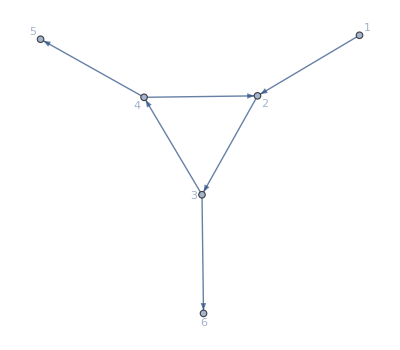

```mathematica
Rotate[gr,Pi/3]
```

```mathematica
Dynamic[gr]
```

### C2

```mathematica
ClearAll[g];
g=Graph[{1},VertexLabels->{1->Button[1,g=MutateGraph[g,1];],2->Button[2,g=MutateGraph[g,2];],3->Button[3,g=MutateGraph[g,3];],4->Button[4,g=MutateGraph[g,4];],5->Button[5,g=MutateGraph[g,5];],6->Button[6,g=MutateGraph[g,6];],7->Button[7,g=MutateGraph[g,7];],8->Button[8,g=MutateGraph[g,8];],9->Button[9,g=MutateGraph[g,9];]}(*,VertexCoordinates->{1->{0,2},2->{1,1},3->{2,0},4->{-1,1},5->{0,0},6->{1,-1},7->{-2,0},8->{-1,-1},9->{0,-2}}*),GraphLayout->"HighDimensionalEmbedding"]
```